# MCHE 470 - Robotics Dynamics and Control

## Loading vector operation tools

```mathematica
<<"C:\\Users\\ambik\\OneDrive - University of Louisiana Lafayette\\Documents\\Wolfram Mathematica\\vectorDefsMM30.m"
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

### Typical rotations

Generic 0 rotation (Identity)

```mathematica
rot0[q_:1]={{1,0,0},{0,1,0},
		            {0,0,1}};MatrixForm [rot0[ ]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Generic 1-rotation

```mathematica
rot1[q_]={{1,0,0},{0,Cos[q],Sin[q]},
		            {0,-Sin[q],Cos[q]}};MatrixForm [rot1[Subscript[q, 1][t]]]
```

(1 | 0 | 0
0 | Cos[q_1[t]] | Sin[q_1[t]]
0 | -Sin[q_1[t]] | Cos[q_1[t]])

Generic 2-rotation

```mathematica
rot2[q_]={{Cos[q],0,-Sin[q]},{0,1,0},
		            {Sin[q],0,Cos[q]}};MatrixForm [rot2[Subscript[q, 2][t]]]
```

(Cos[q_2[t]] | 0 | -Sin[q_2[t]]
0 | 1 | 0
Sin[q_2[t]] | 0 | Cos[q_2[t]])

Generic 3-rotation

```mathematica
rot3[q_]={{Cos[q],Sin[q],0},
		            {-Sin[q],Cos[q],0},
		            {0,0,1}};MatrixForm [rot3[Subscript[q, 3][t]]]
```

(Cos[q_3[t]] | Sin[q_3[t]] | 0
-Sin[q_3[t]] | Cos[q_3[t]] | 0
0 | 0 | 1)

### Define the symbols used for Unit Vectors and Unit Dyads

Define Unit Vectors and Unit Dyads for however many frames we need for the system. For this example we will use three frames of reference, with the frame N being the Newtonian frame.  The header unitVector must be included.  The arguments are [frame, symbol, direction].  So unit vector b[1]=unitVector[B,b,1] is the vector in the B frame in the 1 direction.  The unitDyads are double vectors used to describe inertia properties.

```mathematica
a[x_]:=unitVector[A,a,x]
b[x_]:=unitVector[B,b,x]
c[x_]:=unitVector[C,c,x]
d[x_]:=unitVector[D,d,x]
e[x_]:=unitVector[E,e,x]
f[x_]:=unitVector[F,f,x]
g[x_]:=unitVector[G,g,x]
h[x_]:=unitVector[H,h,x]
n[x_]:=unitVector[N,n,x]
aa[x_,y_]:=unitDyad[a[x],a[y]]
bb[x_,y_]:=unitDyad[b[x],b[y]]
cc[x_,y_]:=unitDyad[c[x],c[y]]
dd[x_,y_]:=unitDyad[d[x],d[y]]
ee[x_,y_]:=unitDyad[e[x],e[y]]
ff[x_,y_]:=unitDyad[f[x],f[y]]
gg[x_,y_]:=unitDyad[g[x],g[y]]
hh[x_,y_]:=unitDyad[h[x],h[y]]
```

### Graphical construction of robot (uses graphic primitives from Mathematica v6 and above)

#### Base platform

Draw the base platform from regular polygons

```mathematica
vecL=2;
```

```mathematica
widthBase=2;depthBase=2;heightBase=1/2;
```

```mathematica
baseShape=Cuboid[
{-widthBase/2,-depthBase/2,-heightBase/2},
{widthBase/2,depthBase/2,heightBase/2}];
```

```mathematica
baseGraphicF={baseShape,
{Text[Subscript[â, 1],{vecL,0,0},{0,1}],Text[Subscript[â, 2],{0,vecL,0},{0,1}],Text[Subscript[â, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[baseGraphicF],ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
baseGraphic={baseShape,
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Riser cylinder

Draw the riser as a cylinder

```mathematica
vecL=1;
```

```mathematica
halfHeightRiser=1/2;
riserBase={0,0,-halfHeightRiser};
riserTop={0,0,halfHeightRiser};
riserRadius=1/2;
```

```mathematica
riserGraphicF={Cylinder[{riserBase,riserTop},riserRadius],
		{AbsoluteThickness[1],{Text[Subscript[b̂, 1],{vecL,0,0},{0,1}],Text[Subscript[b̂, 2],{0,vecL,0},{0,1}],Text[Subscript[b̂, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}}};
```

```mathematica
Show[Graphics3D[riserGraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
riserGraphic={Cylinder[{riserBase,riserTop},riserRadius],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Shoulder cylinder

Draw the shoulder

```mathematica
vecL=1;
```

```mathematica
halfHeightShoulder=1/4+1/4;
shoulderBase={0,0,-halfHeightShoulder};
shoulderTop={0,0,halfHeightShoulder};
shoulderRadius=1/2;
```

```mathematica
shoulderGraphicF={Rotate[Cylinder[{shoulderBase,shoulderTop},shoulderRadius],Pi/2,{1,0,0}],Text[Subscript[ĉ, 1],{vecL,0,0},{0,1}],Text[Subscript[ĉ, 2],{0,vecL,0},{0,1}],Text[Subscript[ĉ, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[shoulderGraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
shoulderGraphic={Rotate[Cylinder[{shoulderBase,shoulderTop},shoulderRadius],Pi/2,{1,0,0}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Arm segment 1

Draw the first arm from polygons

```mathematica
vecL=2;
```

```mathematica
lengthArm1=2;depthArm1=1/2;heightArm1=2 shoulderRadius;
```

```mathematica
arm1Shape=Cuboid[
{-lengthArm1/2,-depthArm1/2,-heightArm1/2},
{lengthArm1/2,depthArm1/2,heightArm1/2}];
```

```mathematica
arm1GraphicF={arm1Shape,
{Text[Subscript[d̂, 1],{vecL,0,0},{0,1}],Text[Subscript[d̂, 2],{0,vecL,0},{0,1}],Text[Subscript[d̂, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[arm1GraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
arm1Graphic={arm1Shape,
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Arm segment 2

Draw the second arm from polygons

```mathematica
vecL=2;
```

```mathematica
lengthArm2=1;depthArm2=1/3;heightArm2=shoulderRadius;
```

```mathematica
arm2Shape=Cuboid[
{-lengthArm2/2,-depthArm2/2,-heightArm2/2},
{lengthArm2/2,depthArm2/2,heightArm2/2}];
```

```mathematica
arm2GraphicF={arm1Shape,
{Text[Subscript[ê, 1],{vecL,0,0},{0,1}],Text[Subscript[ê, 2],{0,vecL,0},{0,1}],Text[Subscript[ê, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[arm2GraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
arm2Graphic={arm2Shape,
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Arm segment 3

Draw the third arm as a cylinder

```mathematica
vecL=1;
```

```mathematica
halfHeightArm3=1/3;
arm3Base={0,0,-halfHeightArm3};
arm3Top={0,0,halfHeightArm3};
arm3Radius=1/8;
```

```mathematica
arm3GraphicF={Rotate[Cylinder[{arm3Base,arm3Top},arm3Radius],Pi/2,{0,1,0}],
Text[Subscript[f̂, 1],{vecL,0,0},{0,1}],Text[Subscript[f̂, 2],{0,vecL,0},{0,1}],Text[Subscript[f̂, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[arm3GraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
arm3Graphic={Rotate[Cylinder[{arm3Base,arm3Top},arm3Radius],Pi/2,{0,1,0}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Wrist1

Draw the wrist and tool pointer as a cylinder and dark line

```mathematica
vecL=1;
```

```mathematica
halfHeightWrist1=1/12;
wrist1Base={0,0,-halfHeightWrist1};
wrist1Top={0,0,halfHeightWrist1};
wrist1Radius=1/6;
```

```mathematica
wristGraphicF={Rotate[Cylinder[{wrist1Base,wrist1Top},wrist1Radius],Pi/2,{1,0,0}],
Text[Subscript[ĝ, 1],{vecL,0,0},{0,1}],Text[Subscript[ĝ, 2],{0,vecL,0},{0,1}],Text[Subscript[ĝ, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[wristGraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wrist1Graphic={Rotate[Cylinder[{wrist1Base,wrist1Top},wrist1Radius],Pi/2,{1,0,0}],
{Thickness[.01],Line[{{wrist1Radius,0,0},{wrist1Radius+pointerLength,0,0}}]},
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Wrist2 and pointer

Draw the wrist and tool pointer as a cylinder and dark line

```mathematica
vecL=1;
```

```mathematica
halfHeightWrist2=1/14;
wrist2Base={0,0,-halfHeightWrist2};
wrist2Top={0,0,halfHeightWrist2};
wrist2Radius=1/6;pointerLength=1/4;
```

```mathematica
wrist2GraphicF={Rotate[Cylinder[{wrist2Base,wrist2Top},wrist2Radius],Pi/2,{0,1,0}],
{Thickness[.02],Line[{{halfHeightWrist2,0,0},{halfHeightWrist2+pointerLength,0,0}}]},
Text[Subscript[ĥ, 1],{vecL,0,0},{0,1}],Text[Subscript[ĥ, 2],{0,vecL,0},{0,1}],Text[Subscript[ĥ, 3],{0,0,vecL},{0,-1}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[wrist2GraphicF],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wrist2Graphic={Rotate[Cylinder[{wrist2Base,wrist2Top},wrist2Radius],Pi/2,{0,1,0}],
{Thickness[.01],Line[{{halfHeightWrist2,0,0},{halfHeightWrist2+pointerLength,0,0}}]},
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

#### Entire robot

```mathematica
robotGraphic=
(*Base graphic*)
{Translate[baseGraphic,{0,0,1/2 heightBase}],

(*Riser graphic*)
Translate[riserGraphic,{0,0,heightBase + halfHeightRiser}],

(*Shoulder graphic*)
Translate[shoulderGraphic,{0,0,heightBase + 2halfHeightRiser + 1/2 shoulderRadius}],

(*Arm1 graphic*)
Translate[arm1Graphic,{1/4 lengthArm1,halfHeightShoulder+ 1/2 depthArm1,heightBase + 2halfHeightRiser + 1/2 shoulderRadius}],

(*Arm2 graphic*)
Translate[arm2Graphic,{lengthArm1 -1/3 lengthArm2,halfHeightShoulder- 1/2 depthArm2 ,heightBase + 2halfHeightRiser + 1/2 shoulderRadius}],

(*Arm3 graphic*)
Translate[arm3Graphic,{3/4 lengthArm1 + 2/3 lengthArm2 + halfHeightArm3,halfHeightShoulder- 1/2 depthArm2 ,heightBase + 2halfHeightRiser + 1/2 shoulderRadius}],

(*Wrist1 graphic*)
Translate[wrist1Graphic,{3/4 lengthArm1 + 2/3 lengthArm2 + 2halfHeightArm3 + wrist1Radius,halfHeightShoulder- 1/2 depthArm2 ,heightBase + 2halfHeightRiser + 1/2 shoulderRadius}],

(*Wrist2 graphic*)
Translate[wrist2Graphic,{3/4 lengthArm1 + 2/3 lengthArm2 + 2halfHeightArm3 +2 wrist1Radius + halfHeightWrist2,halfHeightShoulder- 1/2 depthArm2 ,heightBase + 2halfHeightRiser + 1/2 shoulderRadius}]};
```

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphic,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphic,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphic,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphic,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphic,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphic,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

### Rotations

Lets assume the robot has a moving base, shoulder, and three link arm, with wrist1 and 2.  It has a  3-2-2-1-2-1 rotation sequence.  Starting from the Newtonian frame N we have a 0-rotation to A, then a 0-rotation to B, then a 3-rotation to C, then a 2-rotation to D, then a 2-rotation to E, then a 1-rotation to F, then a 2-rotation to G, then a 1-rotation to H and the tool pointer

```mathematica
rotA=rot0[];
AtoN=rotA.{n[1],n[2],n[3]}
```

{(n̂)_1,(n̂)_2,(n̂)_3}

```mathematica
TranAtoN[x_]:=x//.{a[1]->AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

```mathematica
rotB=rot0[];
BtoN=rotB.{n[1],n[2],n[3]}
```

{(n̂)_1,(n̂)_2,(n̂)_3}

```mathematica
TranBtoN[x_]:=x//.{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
```

```mathematica
rotC=rot3[Subscript[q, 1][t]];
CtoN=rotC.{n[1],n[2],n[3]}
```

{Cos[q_1[t]] (n̂)_1+Sin[q_1[t]] (n̂)_2,-Sin[q_1[t]] (n̂)_1+Cos[q_1[t]] (n̂)_2,(n̂)_3}

```mathematica
TranCtoN[x_]:=x//.{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
```

```mathematica
rotD=rot2[Subscript[q, 2][t]].rot3[Subscript[q, 1][t]];
DtoN=rotD.{n[1],n[2],n[3]}
```

{Cos[q_1[t]] Cos[q_2[t]] (n̂)_1+Cos[q_2[t]] Sin[q_1[t]] (n̂)_2-Sin[q_2[t]] (n̂)_3,-Sin[q_1[t]] (n̂)_1+Cos[q_1[t]] (n̂)_2,Cos[q_1[t]] Sin[q_2[t]] (n̂)_1+Sin[q_1[t]] Sin[q_2[t]] (n̂)_2+Cos[q_2[t]] (n̂)_3}

```mathematica
TranDtoN[x_]:=x//.{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
```

```mathematica
rotE=rot2[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot3[Subscript[q, 1][t]];
EtoN=rotE.{n[1],n[2],n[3]}
```

{Cos[q_1[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) (n̂)_1+Sin[q_1[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) (n̂)_3,-Sin[q_1[t]] (n̂)_1+Cos[q_1[t]] (n̂)_2,Cos[q_1[t]] (Cos[q_3[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_3[t]]) (n̂)_1+Sin[q_1[t]] (Cos[q_3[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_3[t]]) (n̂)_2+(Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3}

```mathematica
TranEtoN[x_]:=x//.{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
```

```mathematica
rotF=rot1[Subscript[q, 4][t]].rot2[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot3[Subscript[q, 1][t]];
FtoN=rotF.{n[1],n[2],n[3]}
```

{Cos[q_1[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) (n̂)_1+Sin[q_1[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) (n̂)_2+(-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) (n̂)_3,(-Cos[q_4[t]] Sin[q_1[t]]+Cos[q_1[t]] (Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]])) (n̂)_1+(Cos[q_1[t]] Cos[q_4[t]]+Sin[q_1[t]] (Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]])) (n̂)_2+(Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]]-Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]) (n̂)_3,(Cos[q_1[t]] (Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]+Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]]) (n̂)_1+(Sin[q_1[t]] (Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]+Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]]) (n̂)_2+(Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]-Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]]) (n̂)_3}

```mathematica
TranFtoN[x_]:=x//.{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
```

```mathematica
rotG=rot2[Subscript[q, 5][t]].rot1[Subscript[q, 4][t]].rot2[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot3[Subscript[q, 1][t]];
GtoN=rotG.{n[1],n[2],n[3]}
```

{(-Sin[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+Cos[q_1[t]] (Sin[q_2[t]] (-Cos[q_5[t]] Sin[q_3[t]]-Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]])+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_5[t]]-Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]))) (n̂)_1+(Cos[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+Sin[q_1[t]] (Sin[q_2[t]] (-Cos[q_5[t]] Sin[q_3[t]]-Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]])+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_5[t]]-Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]))) (n̂)_2+(Cos[q_2[t]] (-Cos[q_5[t]] Sin[q_3[t]]-Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]])-Sin[q_2[t]] (Cos[q_3[t]] Cos[q_5[t]]-Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]])) (n̂)_3,(-Cos[q_4[t]] Sin[q_1[t]]+Cos[q_1[t]] (Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]])) (n̂)_1+(Cos[q_1[t]] Cos[q_4[t]]+Sin[q_1[t]] (Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]]+Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]])) (n̂)_2+(Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]]-Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]) (n̂)_3,(Cos[q_5[t]] Sin[q_1[t]] Sin[q_4[t]]+Cos[q_1[t]] (Cos[q_2[t]] (Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]]+Cos[q_3[t]] Sin[q_5[t]])+Sin[q_2[t]] (Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]-Sin[q_3[t]] Sin[q_5[t]]))) (n̂)_1+(-Cos[q_1[t]] Cos[q_5[t]] Sin[q_4[t]]+Sin[q_1[t]] (Cos[q_2[t]] (Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]]+Cos[q_3[t]] Sin[q_5[t]])+Sin[q_2[t]] (Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]-Sin[q_3[t]] Sin[q_5[t]]))) (n̂)_2+(-Sin[q_2[t]] (Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]]+Cos[q_3[t]] Sin[q_5[t]])+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]-Sin[q_3[t]] Sin[q_5[t]])) (n̂)_3}

```mathematica
TranGtoN[x_]:=x//.{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
```

```mathematica
rotH=rot1[Subscript[q, 6][t]].rot2[Subscript[q, 5][t]].rot1[Subscript[q, 4][t]].rot2[Subscript[q, 3][t]].rot2[Subscript[q, 2][t]].rot3[Subscript[q, 1][t]];
HtoN=rotH.{n[1],n[2],n[3]}
```

{(-Sin[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+Cos[q_1[t]] (Sin[q_2[t]] (-Cos[q_5[t]] Sin[q_3[t]]-Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]])+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_5[t]]-Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]))) (n̂)_1+(Cos[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+Sin[q_1[t]] (Sin[q_2[t]] (-Cos[q_5[t]] Sin[q_3[t]]-Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]])+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_5[t]]-Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]))) (n̂)_2+(Cos[q_2[t]] (-Cos[q_5[t]] Sin[q_3[t]]-Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]])-Sin[q_2[t]] (Cos[q_3[t]] Cos[q_5[t]]-Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]])) (n̂)_3,(-Sin[q_1[t]] (Cos[q_4[t]] Cos[q_6[t]]-Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]])+Cos[q_1[t]] (Sin[q_2[t]] (-Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_3[t]] (Cos[q_6[t]] Sin[q_4[t]]+Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]]))+Cos[q_2[t]] (Cos[q_3[t]] Sin[q_5[t]] Sin[q_6[t]]+Sin[q_3[t]] (Cos[q_6[t]] Sin[q_4[t]]+Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]])))) (n̂)_1+(Cos[q_1[t]] (Cos[q_4[t]] Cos[q_6[t]]-Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]])+Sin[q_1[t]] (Sin[q_2[t]] (-Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_3[t]] (Cos[q_6[t]] Sin[q_4[t]]+Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]]))+Cos[q_2[t]] (Cos[q_3[t]] Sin[q_5[t]] Sin[q_6[t]]+Sin[q_3[t]] (Cos[q_6[t]] Sin[q_4[t]]+Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]])))) (n̂)_2+(Cos[q_2[t]] (-Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_3[t]] (Cos[q_6[t]] Sin[q_4[t]]+Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]]))-Sin[q_2[t]] (Cos[q_3[t]] Sin[q_5[t]] Sin[q_6[t]]+Sin[q_3[t]] (Cos[q_6[t]] Sin[q_4[t]]+Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]]))) (n̂)_3,(-Sin[q_1[t]] (-Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]]-Cos[q_4[t]] Sin[q_6[t]])+Cos[q_1[t]] (Sin[q_2[t]] (-Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]]+Cos[q_3[t]] (Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]]-Sin[q_4[t]] Sin[q_6[t]]))+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_6[t]] Sin[q_5[t]]+Sin[q_3[t]] (Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]]-Sin[q_4[t]] Sin[q_6[t]])))) (n̂)_1+(Cos[q_1[t]] (-Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]]-Cos[q_4[t]] Sin[q_6[t]])+Sin[q_1[t]] (Sin[q_2[t]] (-Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]]+Cos[q_3[t]] (Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]]-Sin[q_4[t]] Sin[q_6[t]]))+Cos[q_2[t]] (Cos[q_3[t]] Cos[q_6[t]] Sin[q_5[t]]+Sin[q_3[t]] (Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]]-Sin[q_4[t]] Sin[q_6[t]])))) (n̂)_2+(Cos[q_2[t]] (-Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]]+Cos[q_3[t]] (Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]]-Sin[q_4[t]] Sin[q_6[t]]))-Sin[q_2[t]] (Cos[q_3[t]] Cos[q_6[t]] Sin[q_5[t]]+Sin[q_3[t]] (Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]]-Sin[q_4[t]] Sin[q_6[t]]))) (n̂)_3}

```mathematica
TranHtoN[x_]:=x//.{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
```

### Relative position vectors

Now lets create vectors to the reference frames of each body relative to the previous body or frame.  See composite robot graphic

```mathematica
Show[Graphics3D[robotGraphic,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

Base

```mathematica
OrAo=x[t] n[1] + y[t] n[2] + 1/2 heightBase n[3]
```

((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Riser

```mathematica
AorBo =(1/2 heightBase + halfHeightRiser)a[3]
```

(3 (â)_3)/4

Shoulder

```mathematica
BorCo=(halfHeightRiser + 1/2 shoulderRadius) b[3]
```

(3 (b̂)_3)/4

Arm1

```mathematica
CorDo= halfHeightShoulder c[2]+  1/2 depthArm1 d[2] + 1/4 lengthArm1 d[1]
```

((ĉ)_2)/2+((d̂)_1)/2+((d̂)_2)/4

Arm2

```mathematica
DorEo= 1/2lengthArm1 d[1] - (1/2 depthArm1 + 1/2 depthArm2) e[2]+1/2 lengthArm2 e[1] - 1/3 lengthArm2 e[1]
```

(d̂)_1+((ê)_1)/6-(5 (ê)_2)/12

Arm3

```mathematica
EorFo= 1/2 lengthArm2 e[1] +  halfHeightArm3 f[1]
```

((ê)_1)/2+((f̂)_1)/3

Wrist1

```mathematica
ForGo= (halfHeightArm3 + wrist1Radius) f[1]
```

((f̂)_1)/2

Wrist2

```mathematica
GorHo=(wrist1Radius + halfHeightWrist2) g[1]
```

(5 (ĝ)_1)/21

Pointer

```mathematica
HorP=(halfHeightWrist2 + pointerLength) h[1]
```

(9 (ĥ)_1)/28

### Graphic transformation function

This function will be used to rotate the graphic primatives using the home-built transformations.  Do not mess with it!!!!

```mathematica
myRotateShape[shape_,myRotationMatrix_]:=Block[{rotmat=myRotationMatrix},shape/.{poly:Polygon[_]:>Map[(rotmat.#)&,poly,{2}],line:Line[_]:>Map[(rotmat.#)&,line,{2}],point:Point[_]:>Map[(rotmat.#)&,point,{1}]}]
```

### Homogeneous Transformation for the Robot

The RotationTransform[] is the function in Mathematica that can be used to implement the homogeneous transformation.  But we will implement with standard tools like from the notes.  This is added just for demonstration purposes, the notebooks do not rely on the Homogeneous Transformation.

Here is the basic form of the T - matrix

```mathematica
T[rot_List,pos_List]:={Append[rot[[1]][[1;;3]],pos[[1]]],Append[rot[[2]][[1;;3]],pos[[2]]],Append[rot[[3]][[1;;3]],pos[[3]]],{0,0,0,1}}
```

Remember the rotation matrix in the T - matrix is the transpose of the C - matrix we defined above because we are rotating the current frame up to the next frame.  Here is how it is used.

```mathematica
T[Transpose[rot3[q]],{x,y,z}]//MatrixForm
```

(Cos[q] | -Sin[q] | 0 | x
Sin[q] | Cos[q] | 0 | y
0 | 0 | 1 | z
0 | 0 | 0 | 1)

#### N to A

Pure translation

```mathematica
NtA = T[Transpose[rot0[]],{OrAo.n[1],OrAo.n[2],OrAo.n[3]}];MatrixForm[NtA]
```

(1 | 0 | 0 | x[t]
0 | 1 | 0 | y[t]
0 | 0 | 1 | 1/4
0 | 0 | 0 | 1)

#### A to B

Pure translation

```mathematica
AtB = T[Transpose[rot0[]],{AorBo.a[1],AorBo.a[2],AorBo.a[3]}];MatrixForm[AtB]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 3/4
0 | 0 | 0 | 1)

#### B to C

Translation then Rotation

```mathematica
BtrC = T[Transpose[rot0[]],{BorCo.b[1],BorCo.b[2],BorCo.b[3]}];MatrixForm[BtrC]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 3/4
0 | 0 | 0 | 1)

```mathematica
BrotC = T[Transpose[rot3[Subscript[q, 1][t]]],{0,0,0}];MatrixForm[BrotC]
```

(Cos[q_1[t]] | -Sin[q_1[t]] | 0 | 0
Sin[q_1[t]] | Cos[q_1[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Complete

```mathematica
BtC=BtrC.BrotC;MatrixForm[BtC]
```

(Cos[q_1[t]] | -Sin[q_1[t]] | 0 | 0
Sin[q_1[t]] | Cos[q_1[t]] | 0 | 0
0 | 0 | 1 | 3/4
0 | 0 | 0 | 1)

#### C to D

Here we need to do multiple steps to get through the body.

First we translate to edge of shoulder

```mathematica
CtrS=T[Transpose[rot0[]],{0,halfHeightShoulder,0}];MatrixForm[CtrS]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 1/2
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Next we rotate to the Arm1 frame

```mathematica
CrotD=T[Transpose[rot2[Subscript[q, 2][t]]],{0,0,0}];MatrixForm[CrotD]
```

(Cos[q_2[t]] | 0 | Sin[q_2[t]] | 0
0 | 1 | 0 | 0
-Sin[q_2[t]] | 0 | Cos[q_2[t]] | 0
0 | 0 | 0 | 1)

Then we translate from edge of shoulder to Arm1 coordinate center

```mathematica
StrD=T[Transpose[rot0[]],{1/4 lengthArm1,1/2 depthArm1,0}];MatrixForm[StrD]
```

(1 | 0 | 0 | 1/2
0 | 1 | 0 | 1/4
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Complete

```mathematica
CtD=CtrS.CrotD.StrD;MatrixForm[CtD]
```

(Cos[q_2[t]] | 0 | Sin[q_2[t]] | 1/2 Cos[q_2[t]]
0 | 1 | 0 | 3/4
-Sin[q_2[t]] | 0 | Cos[q_2[t]] | -1/2 Sin[q_2[t]]
0 | 0 | 0 | 1)

#### D to E

Here we need to do multiple steps to get through the body.

First we translate from the center of Arm1 to the edge of Arm 1

```mathematica
DtrArm1E=T[Transpose[rot0[]],{1/2lengthArm1,- 1/2 depthArm1,0}];MatrixForm[DtrArm1E]
```

(1 | 0 | 0 | 1
0 | 1 | 0 | -1/4
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Next we rotate to the Arm2 frame

```mathematica
DrotE=T[Transpose[rot2[Subscript[q, 3][t]]],{0,0,0}];MatrixForm[DrotE]
```

(Cos[q_3[t]] | 0 | Sin[q_3[t]] | 0
0 | 1 | 0 | 0
-Sin[q_3[t]] | 0 | Cos[q_3[t]] | 0
0 | 0 | 0 | 1)

Then we translate from edge of Arm1 to Arm2 coordinate center

```mathematica
Arm1EtrE=T[Transpose[rot0[]],{1/2 lengthArm2  - 1/3 lengthArm2 ,1/2 depthArm2,0}];MatrixForm[Arm1EtrE]
```

(1 | 0 | 0 | 1/6
0 | 1 | 0 | 1/6
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Complete

```mathematica
DtE=DtrArm1E.DrotE.Arm1EtrE;MatrixForm[DtE]
```

(Cos[q_3[t]] | 0 | Sin[q_3[t]] | 1+1/6 Cos[q_3[t]]
0 | 1 | 0 | -1/12
-Sin[q_3[t]] | 0 | Cos[q_3[t]] | -1/6 Sin[q_3[t]]
0 | 0 | 0 | 1)

#### E to F

Here we need to do multiple steps to get through the body.

First we translate from the center of Arm2 to the edge of Arm 2

```mathematica
EtrArm2E=T[Transpose[rot0[]],{1/2lengthArm2,0,0}];MatrixForm[EtrArm2E]
```

(1 | 0 | 0 | 1/2
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Next we rotate to the Arm3 frame

```mathematica
ErotF=T[Transpose[rot1[Subscript[q, 4][t]]],{0,0,0}];MatrixForm[ErotF]
```

(1 | 0 | 0 | 0
0 | Cos[q_4[t]] | -Sin[q_4[t]] | 0
0 | Sin[q_4[t]] | Cos[q_4[t]] | 0
0 | 0 | 0 | 1)

Then we translate from edge of Arm2 to Arm3 coordinate center

```mathematica
Arm2EtrF=T[Transpose[rot0[]],{halfHeightArm3,0,0}];MatrixForm[Arm2EtrF]
```

(1 | 0 | 0 | 1/3
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Complete

```mathematica
EtF=EtrArm2E.ErotF.Arm2EtrF;MatrixForm[EtF]
```

(1 | 0 | 0 | 5/6
0 | Cos[q_4[t]] | -Sin[q_4[t]] | 0
0 | Sin[q_4[t]] | Cos[q_4[t]] | 0
0 | 0 | 0 | 1)

#### F to G

Here we need to do multiple steps to get through the body.

First we translate from the center of Arm3 to the center of wrist1, it is fixed to Arm3 but allows the next body to rotate around it.

```mathematica
FtrG=T[Transpose[rot0[]],{halfHeightArm3 + wrist1Radius,0,0}];MatrixForm[FtrG]
```

(1 | 0 | 0 | 1/2
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Next we rotate to the Wrist1 frame

```mathematica
FrotG=T[Transpose[rot2[Subscript[q, 5][t]]],{0,0,0}];MatrixForm[FrotG]
```

(Cos[q_5[t]] | 0 | Sin[q_5[t]] | 0
0 | 1 | 0 | 0
-Sin[q_5[t]] | 0 | Cos[q_5[t]] | 0
0 | 0 | 0 | 1)

Complete

```mathematica
FtG=FtrG.FrotG;MatrixForm[FtG]
```

(Cos[q_5[t]] | 0 | Sin[q_5[t]] | 1/2
0 | 1 | 0 | 0
-Sin[q_5[t]] | 0 | Cos[q_5[t]] | 0
0 | 0 | 0 | 1)

#### G to H

Here we need to do multiple steps to get through the body.

First we translate from the center of Wrist1 to the center of Wrist2

```mathematica
GtrH=T[Transpose[rot0[]],{wrist1Radius + halfHeightWrist2,0,0}];MatrixForm[GtrH]
```

(1 | 0 | 0 | 5/21
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Next we rotate to the Wrist2 frame

```mathematica
GrotH=T[Transpose[rot1[Subscript[q, 6][t]]],{0,0,0}];MatrixForm[GrotH]
```

(1 | 0 | 0 | 0
0 | Cos[q_6[t]] | -Sin[q_6[t]] | 0
0 | Sin[q_6[t]] | Cos[q_6[t]] | 0
0 | 0 | 0 | 1)

Complete

```mathematica
GtH=GtrH.GrotH;MatrixForm[GtH]
```

(1 | 0 | 0 | 5/21
0 | Cos[q_6[t]] | -Sin[q_6[t]] | 0
0 | Sin[q_6[t]] | Cos[q_6[t]] | 0
0 | 0 | 0 | 1)

#### H to P

Here we need to simple translation.

```mathematica
HtP=T[Transpose[rot0[]],{halfHeightWrist2 + pointerLength,0,0}];MatrixForm[HtP]
```

(1 | 0 | 0 | 9/28
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

#### N to P

This locates the tool tip in the Newtonian frame as well as the orientation of the H frame as seen in the N frame.

```mathematica
NtP=NtA.AtB.BtC.CtD.DtE.EtF.FtG.GtH.HtP;MatrixForm[NtP]
```

(Cos[q_5[t]] (Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])-(Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]]) Sin[q_5[t]] | Cos[q_6[t]] (-Cos[q_4[t]] Sin[q_1[t]]+(Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]])+(Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]])+(Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]]) Sin[q_6[t]] | Cos[q_6[t]] (Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]])+(Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]])-(-Cos[q_4[t]] Sin[q_1[t]]+(Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]) Sin[q_6[t]] | 1/2 Cos[q_1[t]] Cos[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] (1+1/6 Cos[q_3[t]])-2/3 Sin[q_1[t]]-1/6 Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+4/3 (Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+47/84 (Cos[q_5[t]] (Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])-(Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]]) Sin[q_5[t]])+x[t]
Cos[q_5[t]] (Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])-(Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]]) Sin[q_5[t]] | Cos[q_6[t]] (Cos[q_1[t]] Cos[q_4[t]]+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]]) Sin[q_4[t]])+(Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]])+(Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]]) Sin[q_6[t]] | Cos[q_6[t]] (Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]])+(Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]])-(Cos[q_1[t]] Cos[q_4[t]]+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]]) Sin[q_4[t]]) Sin[q_6[t]] | 2/3 Cos[q_1[t]]+1/2 Cos[q_2[t]] Sin[q_1[t]]+Cos[q_2[t]] (1+1/6 Cos[q_3[t]]) Sin[q_1[t]]-1/6 Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+4/3 (Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])+47/84 (Cos[q_5[t]] (Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])-(Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]]) Sin[q_5[t]])+y[t]
Cos[q_5[t]] (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]])-Cos[q_4[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]] | Cos[q_6[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]+(Cos[q_4[t]] Cos[q_5[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]])+(-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]]) Sin[q_6[t]] | Cos[q_6[t]] (Cos[q_4[t]] Cos[q_5[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]])+(-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]])-(Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]] Sin[q_6[t]] | 7/4-1/2 Sin[q_2[t]]-(1+1/6 Cos[q_3[t]]) Sin[q_2[t]]-1/6 Cos[q_2[t]] Sin[q_3[t]]+4/3 (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]])+47/84 (Cos[q_5[t]] (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]])-Cos[q_4[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]])
0 | 0 | 0 | 1)

### Animation Example

#### Absolute position vectors and coordinates in Newtonian frame

Coordinates for Ao, base.

```mathematica
xAo=OrAo . n[1]
yAo=OrAo . n[2]
zAo=OrAo . n[3]
```

x[t]

y[t]

1/4

Coordinates for Bo, riser.

```mathematica
xBo=(OrAo + AorBo) . n[1]//TranAtoN//TranBtoN
yBo=(OrAo + AorBo) . n[2]//TranAtoN//TranBtoN
zBo=(OrAo + AorBo) . n[3]//TranAtoN//TranBtoN
```

x[t]

y[t]

1

Coordinates for Co, shoulder.

```mathematica
xCo=(OrAo + AorBo + BorCo) . n[1]//TranAtoN//TranBtoN
yCo=(OrAo + AorBo+ BorCo) . n[2]//TranAtoN//TranBtoN
zCo=(OrAo + AorBo+ BorCo) . n[3]//TranAtoN//TranBtoN
```

x[t]

y[t]

7/4

Coordinates for Do, arm1.

```mathematica
xDo=(OrAo + AorBo + BorCo+ CorDo) . n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//distributeScalars
yDo=(OrAo + AorBo+ BorCo + CorDo) . n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//distributeScalars
zDo=(OrAo + AorBo+ BorCo + CorDo) . n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//distributeScalars
```

1/2 Cos[q_1[t]] Cos[q_2[t]]-3/4 Sin[q_1[t]]+x[t]

3/4 Cos[q_1[t]]+1/2 Cos[q_2[t]] Sin[q_1[t]]+y[t]

7/4-1/2 Sin[q_2[t]]

Coordinates for Eo, arm2.

```mathematica
xEo=(OrAo + AorBo + BorCo+ CorDo + DorEo) . n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//distributeScalars
yEo=(OrAo + AorBo+ BorCo + CorDo + DorEo) . n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//distributeScalars
zEo=(OrAo + AorBo+ BorCo + CorDo + DorEo) . n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//distributeScalars
```

3/2 Cos[q_1[t]] Cos[q_2[t]]+1/6 Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-1/3 Sin[q_1[t]]-1/6 Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+x[t]

1/3 Cos[q_1[t]]+3/2 Cos[q_2[t]] Sin[q_1[t]]+1/6 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-1/6 Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+y[t]

7/4-3/2 Sin[q_2[t]]-1/6 Cos[q_3[t]] Sin[q_2[t]]-1/6 Cos[q_2[t]] Sin[q_3[t]]

Coordinates for Fo, arm3.

```mathematica
xFo=(OrAo + AorBo + BorCo+ CorDo + DorEo + EorFo) . n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//distributeScalars
yFo=(OrAo + AorBo+ BorCo + CorDo + DorEo + EorFo) . n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//distributeScalars
zFo=(OrAo + AorBo+ BorCo + CorDo + DorEo + EorFo) . n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//distributeScalars
```

3/2 Cos[q_1[t]] Cos[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-1/3 Sin[q_1[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+x[t]

1/3 Cos[q_1[t]]+3/2 Cos[q_2[t]] Sin[q_1[t]]+Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+y[t]

7/4-3/2 Sin[q_2[t]]-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]

Coordinates for Go, wrist1.

```mathematica
xGo=(OrAo + AorBo + BorCo+ CorDo + DorEo + EorFo + ForGo) . n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//distributeScalars
yGo=(OrAo + AorBo+ BorCo + CorDo + DorEo + EorFo + ForGo) . n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//distributeScalars
zGo=(OrAo + AorBo+ BorCo + CorDo + DorEo + EorFo + ForGo) . n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//distributeScalars
```

3/2 Cos[q_1[t]] Cos[q_2[t]]+3/2 Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-1/3 Sin[q_1[t]]-3/2 Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+x[t]

1/3 Cos[q_1[t]]+3/2 Cos[q_2[t]] Sin[q_1[t]]+3/2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-3/2 Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]+y[t]

7/4-3/2 Sin[q_2[t]]-3/2 Cos[q_3[t]] Sin[q_2[t]]-3/2 Cos[q_2[t]] Sin[q_3[t]]

Coordinates for Ho, wrist2.

```mathematica
xHo=(OrAo + AorBo + BorCo+ CorDo + DorEo + EorFo + ForGo + GorHo) . n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN//distributeScalars
yHo=(OrAo + AorBo+ BorCo + CorDo + DorEo + EorFo + ForGo + GorHo) . n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN//distributeScalars
zHo=(OrAo + AorBo+ BorCo + CorDo + DorEo + EorFo + ForGo + GorHo) . n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after 3/2 Cos[q_1[t]] Cos[q_2[t]]-1/3 Sin[q_1[t]]+3/2 Cos[q_1[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]])+5/21 (-Sin[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+Cos[q_1[t]] (Sin[Subscript[«2»][«1»]] (Times[«3»]+Times[«4»])+Cos[Subscript[«2»][«1»]] (Times[«2»]+Times[«4»])))+x[t] scanned 3 times.

3/2 Cos[q_1[t]] Cos[q_2[t]]+3/2 Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]+5/21 Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]-1/3 Sin[q_1[t]]-3/2 Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]-5/21 Cos[q_1[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]-5/21 Cos[q_1[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]]-5/21 Cos[q_1[t]] Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]-5/21 Sin[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+x[t]

ReplaceRepeated::rrlim: Exiting after 1/3 Cos[q_1[t]]+3/2 Cos[q_2[t]] Sin[q_1[t]]+3/2 Sin[q_1[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]])+5/21 (Cos[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+Sin[q_1[t]] (Sin[Subscript[«2»][«1»]] (Times[«3»]+Times[«4»])+Cos[Subscript[«2»][«1»]] (Times[«2»]+Times[«4»])))+y[t] scanned 3 times.

1/3 Cos[q_1[t]]+3/2 Cos[q_2[t]] Sin[q_1[t]]+3/2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]+5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]-3/2 Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]-5/21 Cos[q_5[t]] Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]-5/21 Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]] Sin[q_2[t]] Sin[q_5[t]]-5/21 Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]] Sin[q_3[t]] Sin[q_5[t]]+5/21 Cos[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]+y[t]

ReplaceRepeated::rrlim: Exiting after 7/4-3/2 Sin[q_2[t]]+3/2 (-Cos[q_3[t]] Sin[q_2[t]]-«1» «1»)+5/21 (Cos[q_2[t]] (-Cos[Subscript[«2»][«1»]] Sin[Subscript[«2»][«1»]]-Cos[Subscript[«2»][«1»]] Cos[Subscript[«2»][«1»]] Sin[Subscript[«2»][«1»]])-Sin[q_2[t]] (Cos[Subscript[«2»][«1»]] Cos[Subscript[«2»][«1»]]-Cos[Subscript[«2»][«1»]] Sin[Subscript[«2»][«1»]] Sin[Subscript[«2»][«1»]])) scanned 2 times.

7/4-3/2 Sin[q_2[t]]-3/2 Cos[q_3[t]] Sin[q_2[t]]-5/21 Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]]-3/2 Cos[q_2[t]] Sin[q_3[t]]-5/21 Cos[q_2[t]] Cos[q_5[t]] Sin[q_3[t]]-5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]]+5/21 Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]

#### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=3;B=1;Cc=0;ω=2 Pi (.1);
```

```mathematica
x[t_]:=A Cos[ω t]
y[t_]:=A Sin[ω t]
Subscript[q, 1][t_]:= B t + Cc
Subscript[q, 2][t_]:= B t + Cc
Subscript[q, 3][t_]:= B t + Cc
Subscript[q, 4][t_]:= B t + Cc
Subscript[q, 5][t_]:= B t + Cc
Subscript[q, 6][t_]:= B t + Cc
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],
(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],
(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],
(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],
(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],
(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],
(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],
(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT[t_]=robotGraphicAnim;
NtPp[t_]=NtP;
```

```mathematica
tf=10;
scale=2.5A;
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500],MatrixForm[NtPp[t]//N]},{t,0,tf,tf/500},AnimationRunning->False]
```

This is the old style way to do animation with stop action frames.

For[t = 0, t <= tf, t += tf/100,
 Print[Show[Graphics3D[robotGraphicAnim, ViewPoint -> {1, 1, 1}, ViewVertical -> {0, 0, 1}, ViewCenter -> {1/2, 1/2, 1/2}, Boxed -> True, Axes -> True, PlotRange -> {{-scale, scale}, {-scale, scale}, {-scale, scale}}, AspectRatio -> 1, AxesLabel -> {"X", "Y", "Z"}]]]]
t =.;

### Inverse Kinematics

We need to set up nonlinear equations to be solved to find angles and positions given desired pointer tip location and the tool frame orientation.

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
```

#### Desired and actual tool orientation

Using the generic rotations from above we will assume an Euler: roll-pitch-yaw sequence or an Euler 1-2-3 sequence to construct the desired tool orientation.

```mathematica
Subscript[C, des][roll_,pitch_ ,yaw_]:=rot3[yaw].rot2[pitch].rot1[roll]
```

Here is an example

```mathematica
MatrixForm[Subscript[C, des][Pi,Pi/2,Pi/3]]
```

(0 | -(√3)/2 | 1/2
0 | -1/2 | -(√3)/2
1 | 0 | 0)

The actual rotation matrix in terms of our robot parameters is given as follows with the time dependence removed for simplicity

```mathematica
Subscript[C, act]=rotH//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

#### Desired and actual tool tip position

The desired position is just a set of three numbers (X_des,Y_des,Z_des).  The actual position vector out to the tool or pointer is given as follows with the time dependence removed

```mathematica
OrP = OrAo + AorBo + BorCo+ CorDo + DorEo + EorFo + ForGo + GorHo + HorP//.{x[t]->Subscript[X, base],y[t]->Subscript[Y, base]}
```

(3 (b̂)_3)/4+(3 (â)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+(5 (f̂)_1)/6+(5 (ĝ)_1)/21+(9 (ĥ)_1)/28+X_base (n̂)_1+Y_base (n̂)_2+((n̂)_3)/4

The Newtonian X,Y,Z position of the point is given as follows with the time dependence removed

```mathematica
Subscript[X, act]=(OrP.n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

3/2 Cos[Q_1] Cos[Q_2]-Sin[Q_1]/3+3/2 Cos[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (-Sin[Q_1] Sin[Q_4] Sin[Q_5]+Cos[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))+X_base

```mathematica
Subscript[Y, act]=(OrP.n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Sin[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (Cos[Q_1] Sin[Q_4] Sin[Q_5]+Sin[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))+Y_base

```mathematica
Subscript[Z, act]=(OrP.n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

7/4-(3 Sin[Q_2])/2+3/2 (-Cos[Q_3] Sin[Q_2]-Cos[Q_2] Sin[Q_3])+47/84 (Cos[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])-Sin[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5]))

#### Create the equations for the actual angles and positions

This robot has 8 degrees of freedom, so we need at least 8 equations.

First enter desired values.

```mathematica
Subscript[X, des]:=1;
Subscript[Y, des]:=1;
Subscript[Z, des]:=3;
Subscript[θ, r]:= Pi/2;
Subscript[θ, p]:=Pi/4;
Subscript[θ, y]:=Pi/4;
```

Lets see if we can reach this point.  Since the base is mobile we need only check the Z direction when the arm is straight up

```mathematica
Subscript[Z, des]<=Subscript[Z, act]//.{Subscript[Q, 1]-> 0,Subscript[Q, 2]-> -Pi/2,Subscript[Q, 3]-> 0,Subscript[Q, 4]-> 0,Subscript[Q, 5]->0,Subscript[Q, 6]->0}
```

True

Here is the current desired tool orientation

```mathematica
MatrixForm[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]
```

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

Using the three positions first, we have

```mathematica
eq1=Subscript[X, act]-Subscript[X, des]//distributeScalars
eq2=Subscript[Y, act]-Subscript[Y, des]//distributeScalars
eq3=Subscript[Z, act]-Subscript[Z, des]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after -1+3/2 Cos[Q_1] Cos[Q_2]-Sin[Q_1]/3+3/2 Cos[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (-Sin[Q_1] Sin[Q_4] Sin[Q_5]+Cos[Q_1] (Sin[Subscript[«2»]] (Times[«3»]+Times[«4»])+Cos[Subscript[«2»]] (Times[«2»]+Times[«4»])))+X_base scanned 3 times.

-1+3/2 Cos[Q_1] Cos[Q_2]+3/2 Cos[Q_1] Cos[Q_2] Cos[Q_3]+47/84 Cos[Q_1] Cos[Q_2] Cos[Q_3] Cos[Q_5]-Sin[Q_1]/3-3/2 Cos[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_5] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_1] Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]-47/84 Sin[Q_1] Sin[Q_4] Sin[Q_5]+X_base

ReplaceRepeated::rrlim: Exiting after -1+Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Sin[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (Cos[Q_1] Sin[Q_4] Sin[Q_5]+Sin[Q_1] (Sin[Subscript[«2»]] (Times[«3»]+Times[«4»])+Cos[Subscript[«2»]] (Times[«2»]+Times[«4»])))+Y_base scanned 3 times.

-1+Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Cos[Q_2] Cos[Q_3] Sin[Q_1]+47/84 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]-3/2 Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_5] Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_3] Cos[Q_4] Sin[Q_1] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_2] Cos[Q_4] Sin[Q_1] Sin[Q_3] Sin[Q_5]+47/84 Cos[Q_1] Sin[Q_4] Sin[Q_5]+Y_base

ReplaceRepeated::rrlim: Exiting after -5/4-(3 Sin[Q_2])/2+3/2 (-Cos[Q_3] Sin[Q_2]-Cos[Q_2] Sin[Q_3])+47/84 (Cos[Q_2] (-Cos[Subscript[«2»]] Sin[Subscript[«2»]]-Cos[Subscript[«2»]] Cos[Subscript[«2»]] Sin[Subscript[«2»]])-Sin[Q_2] (Cos[Subscript[«2»]] Cos[Subscript[«2»]]-Cos[Subscript[«2»]] Sin[Subscript[«2»]] Sin[Subscript[«2»]])) scanned 2 times.

-5/4-(3 Sin[Q_2])/2-3/2 Cos[Q_3] Sin[Q_2]-47/84 Cos[Q_3] Cos[Q_5] Sin[Q_2]-3/2 Cos[Q_2] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_5] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_5]+47/84 Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_5]

where the equations will be set to zero below.  The remaining equations will be selected from the C matrices being equated element by element (set to zero below)

```mathematica
eq4=Subscript[C, act][[1]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]];
eq5=Subscript[C, act][[1]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]];
eq6=Subscript[C, act][[1]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]];

eq7=Subscript[C, act][[2]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]];
eq8=Subscript[C, act][[2]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]];
eq9=Subscript[C, act][[2]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]];

eq10=Subscript[C, act][[3]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]];
eq11=Subscript[C, act][[3]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]];eq12=Subscript[C, act][[3]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]];
```

#### Solve the equations for best first guess at angles and base position

The strategy to solve the inverse kinematics depends on the design of the robot. There are several closed form solutions for industrial robots, see Ch4 of the class textbook by Craig.

First try to lock in initial estimates of the base location and angles , X_base,Y_base, Q_1,Q_2,Q_3,Q_4,Q_5, and Q_6.  Since the base can move this has many possible solutions.

```mathematica
eq1temp=eq1
```

-1+3/2 Cos[Q_1] Cos[Q_2]+3/2 Cos[Q_1] Cos[Q_2] Cos[Q_3]+47/84 Cos[Q_1] Cos[Q_2] Cos[Q_3] Cos[Q_5]-Sin[Q_1]/3-3/2 Cos[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_5] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_1] Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]-47/84 Sin[Q_1] Sin[Q_4] Sin[Q_5]+X_base

```mathematica
eq2temp=eq2
```

-1+Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Cos[Q_2] Cos[Q_3] Sin[Q_1]+47/84 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]-3/2 Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_5] Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_3] Cos[Q_4] Sin[Q_1] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_2] Cos[Q_4] Sin[Q_1] Sin[Q_3] Sin[Q_5]+47/84 Cos[Q_1] Sin[Q_4] Sin[Q_5]+Y_base

```mathematica
eq3temp=eq3
```

-5/4-(3 Sin[Q_2])/2-3/2 Cos[Q_3] Sin[Q_2]-47/84 Cos[Q_3] Cos[Q_5] Sin[Q_2]-3/2 Cos[Q_2] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_5] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_5]+47/84 Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_5]

We need something to drive the base to a position that will not have the robot all tied up on itself or outstretched to far.  So we will try to align the tool axes with the desired axes is some optimal sense.  Here we want the dot products to be 1 for the main components.

```mathematica
desTool1=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]] n[3]
```

((n̂)_1)/2+((n̂)_2)/2+((n̂)_3)/(√2)

```mathematica
eqV1temp=1 == (h[1].desTool1//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==(Cos[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])-Sin[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5]))/(√2)+1/2 (-Sin[Q_1] Sin[Q_4] Sin[Q_5]+Cos[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))+1/2 (Cos[Q_1] Sin[Q_4] Sin[Q_5]+Sin[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))

```mathematica
desTool2=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]] n[3]
```

-((n̂)_1)/2-((n̂)_2)/2+((n̂)_3)/(√2)

```mathematica
eqV2temp=1 == (h[2].desTool2//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==1/(√2)(Cos[Q_2] (-Sin[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))-Sin[Q_2] (Cos[Q_3] Sin[Q_5] Sin[Q_6]+Sin[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6])))+1/2 (Sin[Q_1] (Cos[Q_4] Cos[Q_6]-Cos[Q_5] Sin[Q_4] Sin[Q_6])-Cos[Q_1] (Sin[Q_2] (-Sin[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Sin[Q_5] Sin[Q_6]+Sin[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))))+1/2 (-Cos[Q_1] (Cos[Q_4] Cos[Q_6]-Cos[Q_5] Sin[Q_4] Sin[Q_6])-Sin[Q_1] (Sin[Q_2] (-Sin[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Sin[Q_5] Sin[Q_6]+Sin[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))))

```mathematica
desTool3=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]] n[3]
```

((n̂)_1)/(√2)-((n̂)_2)/(√2)

```mathematica
eqV3temp=1 == (h[3].desTool3//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==1/(√2)(-Sin[Q_1] (-Cos[Q_5] Cos[Q_6] Sin[Q_4]-Cos[Q_4] Sin[Q_6])+Cos[Q_1] (Sin[Q_2] (-Cos[Q_6] Sin[Q_3] Sin[Q_5]+Cos[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Cos[Q_6] Sin[Q_5]+Sin[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))))-1/(√2)(Cos[Q_1] (-Cos[Q_5] Cos[Q_6] Sin[Q_4]-Cos[Q_4] Sin[Q_6])+Sin[Q_1] (Sin[Q_2] (-Cos[Q_6] Sin[Q_3] Sin[Q_5]+Cos[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Cos[Q_6] Sin[Q_5]+Sin[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))))

The robot reach is defined on a sphere about the base coordinate origin.  Need to get the base within reach.  The minimum base position with respect to reach sphere is found subject to the constraints that the tool axes should be closely aligned with the desired axes and that the joint angles have physical limits due to collisions with other parts, etc.

First we calculate the radius of the sphere of reach based on just the straight reach of the robot.  The scaled pointerLength is subtracted to get closer if needed.

```mathematica
scalePointer=1  ;
```

```mathematica
radius=(OrP.n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->0,Subscript[X, base]->0,Subscript[Y, base]->0}
```

299/84

```mathematica
eqReach=(eq1temp)^2+(eq2temp)^2+ (eq3temp)^2 - (radius - scalePointer pointerLength)^2;
```

```mathematica
minQXY=Minimize[{eqReach,eqV1temp,eqV2temp,eqV3temp,- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[X, base],Subscript[Y, base]}]
```

{-10.9529,{Q_1→1.75072,Q_2→-1.14191,Q_3→1.48865,Q_4→0.627561,Q_5→-1.43217,Q_6→0.674693,X_base→1.41219,Y_base→-1.22177}}

Here are the initial guess at the base coordinates and angles

```mathematica
solX=minQXY[[2]][[7]]
```

X_base→1.41219

```mathematica
solY=minQXY[[2]][[8]]
```

Y_base→-1.22177

```mathematica
solQ1=minQXY[[2]][[1]]
```

Q_1→1.75072

```mathematica
solQ2=minQXY[[2]][[2]]
```

Q_2→-1.14191

```mathematica
solQ3=minQXY[[2]][[3]]
```

Q_3→1.48865

```mathematica
solQ4=minQXY[[2]][[4]]
```

Q_4→0.627561

```mathematica
solQ5=minQXY[[2]][[5]]
```

Q_5→-1.43217

```mathematica
solQ6=minQXY[[2]][[6]]
```

Q_6→0.674693

#### Solve the full equations for angles with base positions known

Initial guesses at solution and root finder algorithm to refine the initial solutions.  The optimal search above is too slow for real-time operations, but if we have good initial guesses, they can be refined with this operation and then this result can be used to start the next solution if the next desired location is near this one.

```mathematica
q1o=Subscript[Q, 1]/.solQ1;
q2o=Subscript[Q, 2]/.solQ2;
q3o=Subscript[Q, 3]/.solQ3;
q4o=Subscript[Q, 4]/.solQ4;
q5o=Subscript[Q, 5]/.solQ5;
q6o=Subscript[Q, 6]/.solQ6;
invKinSol=FindRoot[{(eq1/.solX)==0,(eq2/.solY)==0,(eq3)==0,(eq4)==0,(eq8)==0, (eq12)==0},{{Subscript[Q, 1],q1o,-.9 Pi,.9Pi},{Subscript[Q, 2],q2o,- (Pi + Pi/4 ),Pi/4},{Subscript[Q, 3],q3o,- Pi/2,Pi/2},{Subscript[Q, 4],q4o,-2 Pi,2Pi},{Subscript[Q, 5],q5o,- Pi,Pi},{Subscript[Q, 6],q6o,- 2Pi,2Pi}},MaxIterations->10000]
```

{Q_1→1.75068,Q_2→-1.14193,Q_3→1.48871,Q_4→0.627375,Q_5→-1.43216,Q_6→0.674921}

Compare desired to actual orientations

```mathematica
Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]//MatrixForm
Subscript[C, act]//.invKinSol//Chop//MatrixForm
Cerr=(Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]-Subscript[C, act])//.invKinSol//Chop//MatrixForm
```

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

(0.5 | 0.5 | 0.707107
-0.5 | -0.5 | 0.707107
0.707107 | -0.707107 | 0)

(0 | 1.95905×10^-8 | -1.38526×10^-8
1.95905×10^-8 | 0 | 1.38526×10^-8
1.38526×10^-8 | 1.38526×10^-8 | 0)

Compare desired and actual position

```mathematica
Xerr=eq1//.solX//.invKinSol//Chop
Yerr=eq2//.solY//.invKinSol//Chop
Zerr=eq3//.invKinSol//Chop
```

0

0

0

See if these solutions work. Create composite graphic to check the inverse solution feasibility

```mathematica
x[t_]=Subscript[X, base]/.solX;
y[t_]=Subscript[Y, base]/.solY;
Subscript[q, 1][t_]=Subscript[Q, 1]/.invKinSol;
Subscript[q, 2][t_]=Subscript[Q, 2]/.invKinSol;
Subscript[q, 3][t_]=Subscript[Q, 3]/.invKinSol;
Subscript[q, 4][t_]=Subscript[Q, 4]/.invKinSol;
Subscript[q, 5][t_]=Subscript[Q, 5]/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6]/.invKinSol;
```

```mathematica
robotGraphicInvKin={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},

(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],

(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
};
Show[Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]]
```

-Graphics3D-

Various views.  Do they look doable, no collisions between parts, etc.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

Here is just the tool, look for frames to line-up

```mathematica
toolGraphicInvKin={{PointSize[0.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]};
Show[GraphicsGrid[{{Graphics3D[toolGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[toolGraphicInvKin,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

#### Inverse Kinematics Animation

Here we create a simple path plan to get form the rest position to the desired position.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
tf=.
```

```mathematica
x[t_]=Subscript[X, base] t/tf/.solX;
y[t_]=Subscript[Y, base] t/tf/.solY;
Subscript[q, 1][t_]=Subscript[Q, 1] t/tf/.invKinSol;
Subscript[q, 2][t_]=Subscript[Q, 2] t/tf/.invKinSol;
Subscript[q, 3][t_]=Subscript[Q, 3] t/tf/.invKinSol;
Subscript[q, 4][t_]=Subscript[Q, 4] t/tf/.invKinSol;
Subscript[q, 5][t_]=Subscript[Q, 5] t/tf/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6] t/tf/.invKinSol;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicInvKinAnim={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},

(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],

(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
};
```

```mathematica
robotGraphicInvKinAnimT[t_]=robotGraphicInvKinAnim;
```

Loop over time

```mathematica
tf=2;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicInvKinAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

We need to set up nonlinear equations to be solved to find angles and positions given desired pointer tip location and the tool frame orientation.

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
```

#### Desired and actual tool orientation

Using the generic rotations from above we will assume an Euler: roll-pitch-yaw squence or an Euler 1-2-3 sequence to construct the desired tool orientation.

```mathematica
Subscript[C, des][roll_,pitch_ ,yaw_]:=rot3[yaw].rot2[pitch].rot1[roll]
```

Here is an example

```mathematica
MatrixForm[Subscript[C, des][Pi,Pi/2,Pi/3]]
```

(0 | -(√3)/2 | 1/2
0 | -1/2 | -(√3)/2
1 | 0 | 0)

The actual rotation matrix in terms of our robot parameters is given as follows with the time dependence removed for simplicity

```mathematica
Subscript[C, act]=rotH//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

#### Desired and actual tool tip position

The desired position is just a set of three numbers (X_des,Y_des,Z_des).  The actual position vector out to the tool or pointer is given as follows with the time dependence removed

```mathematica
OrP = OrAo + AorBo + BorCo+ CorDo + DorEo + EorFo + ForGo + GorHo + HorP//.{x[t]->Subscript[X, base],y[t]->Subscript[Y, base]}
```

(3 (b̂)_3)/4+(3 (â)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+(5 (f̂)_1)/6+(5 (ĝ)_1)/21+(9 (ĥ)_1)/28+X_base (n̂)_1+Y_base (n̂)_2+((n̂)_3)/4

The Newtonian X,Y,Z position of the point is given as follows with the time dependence removed

```mathematica
Subscript[X, act]=(OrP.n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

3/2 Cos[Q_1] Cos[Q_2]-Sin[Q_1]/3+3/2 Cos[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (-Sin[Q_1] Sin[Q_4] Sin[Q_5]+Cos[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))+X_base

```mathematica
Subscript[Y, act]=(OrP.n[2]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Sin[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (Cos[Q_1] Sin[Q_4] Sin[Q_5]+Sin[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))+Y_base

```mathematica
Subscript[Z, act]=(OrP.n[3]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

7/4-(3 Sin[Q_2])/2+3/2 (-Cos[Q_3] Sin[Q_2]-Cos[Q_2] Sin[Q_3])+47/84 (Cos[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])-Sin[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5]))

#### Create the equations for the actual angles and positions

This robot has 8 degrees of freedom, so we need at least 8 equations.

First enter desired values.

```mathematica
Subscript[X, des]:=1;
Subscript[Y, des]:=1;
Subscript[Z, des]:=3;
Subscript[θ, r]:= Pi/2;
Subscript[θ, p]:=Pi/4;
Subscript[θ, y]:=Pi/4;
```

Lets see if we can reach this point.  Since the base is mobile we need only check the Z direction when the arm is straight up

```mathematica
Subscript[Z, des]<=Subscript[Z, act]//.{Subscript[Q, 1]-> 0,Subscript[Q, 2]-> -Pi/2,Subscript[Q, 3]-> 0,Subscript[Q, 4]-> 0,Subscript[Q, 5]->0,Subscript[Q, 6]->0}
```

True

Here is the current desired tool orientation

```mathematica
MatrixForm[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]
```

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

Using the three positions first, we have

```mathematica
eq1=Subscript[X, act]-Subscript[X, des]//distributeScalars
eq2=Subscript[Y, act]-Subscript[Y, des]//distributeScalars
eq3=Subscript[Z, act]-Subscript[Z, des]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after -1+3/2 Cos[Q_1] Cos[Q_2]-Sin[Q_1]/3+3/2 Cos[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (-Sin[Q_1] Sin[Q_4] Sin[Q_5]+Cos[Q_1] (Sin[Subscript[«2»]] (Times[«3»]+Times[«4»])+Cos[Subscript[«2»]] (Times[«2»]+Times[«4»])))+X_base scanned 3 times.

-1+3/2 Cos[Q_1] Cos[Q_2]+3/2 Cos[Q_1] Cos[Q_2] Cos[Q_3]+47/84 Cos[Q_1] Cos[Q_2] Cos[Q_3] Cos[Q_5]-Sin[Q_1]/3-3/2 Cos[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_5] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_1] Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]-47/84 Sin[Q_1] Sin[Q_4] Sin[Q_5]+X_base

ReplaceRepeated::rrlim: Exiting after -1+Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Sin[Q_1] (Cos[Q_2] Cos[Q_3]-Sin[Q_2] Sin[Q_3])+47/84 (Cos[Q_1] Sin[Q_4] Sin[Q_5]+Sin[Q_1] (Sin[Subscript[«2»]] (Times[«3»]+Times[«4»])+Cos[Subscript[«2»]] (Times[«2»]+Times[«4»])))+Y_base scanned 3 times.

-1+Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Cos[Q_2] Cos[Q_3] Sin[Q_1]+47/84 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]-3/2 Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_5] Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_3] Cos[Q_4] Sin[Q_1] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_2] Cos[Q_4] Sin[Q_1] Sin[Q_3] Sin[Q_5]+47/84 Cos[Q_1] Sin[Q_4] Sin[Q_5]+Y_base

ReplaceRepeated::rrlim: Exiting after -5/4-(3 Sin[Q_2])/2+3/2 (-Cos[Q_3] Sin[Q_2]-Cos[Q_2] Sin[Q_3])+47/84 (Cos[Q_2] (-Cos[Subscript[«2»]] Sin[Subscript[«2»]]-Cos[Subscript[«2»]] Cos[Subscript[«2»]] Sin[Subscript[«2»]])-Sin[Q_2] (Cos[Subscript[«2»]] Cos[Subscript[«2»]]-Cos[Subscript[«2»]] Sin[Subscript[«2»]] Sin[Subscript[«2»]])) scanned 2 times.

-5/4-(3 Sin[Q_2])/2-3/2 Cos[Q_3] Sin[Q_2]-47/84 Cos[Q_3] Cos[Q_5] Sin[Q_2]-3/2 Cos[Q_2] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_5] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_5]+47/84 Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_5]

where the equations will be set to zero below.  The remaining equations will be selected from the C matrices being equated element by element (set to zero below)

```mathematica
eq4=Subscript[C, act][[1]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]];
eq5=Subscript[C, act][[1]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]];
eq6=Subscript[C, act][[1]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]];

eq7=Subscript[C, act][[2]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]];
eq8=Subscript[C, act][[2]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]];
eq9=Subscript[C, act][[2]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]];

eq10=Subscript[C, act][[3]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]];
eq11=Subscript[C, act][[3]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]];eq12=Subscript[C, act][[3]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]];
```

#### Solve the equations for best first guess at angles and base position

The strategy to solve the inverse kinematics depends on the design of the robot. There are several closed form solutions for industrial robots, see Ch4 of the class textbook by Craig.

First try to lock in initial estimates of the base location and angles , X_base,Y_base, Q_1,Q_2,Q_3,Q_4,Q_5, and Q_6.  Since the base can move this has many possible solutions.

```mathematica
eq1temp=eq1
```

-1+3/2 Cos[Q_1] Cos[Q_2]+3/2 Cos[Q_1] Cos[Q_2] Cos[Q_3]+47/84 Cos[Q_1] Cos[Q_2] Cos[Q_3] Cos[Q_5]-Sin[Q_1]/3-3/2 Cos[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_5] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_1] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_1] Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]-47/84 Sin[Q_1] Sin[Q_4] Sin[Q_5]+X_base

```mathematica
eq2temp=eq2
```

-1+Cos[Q_1]/3+3/2 Cos[Q_2] Sin[Q_1]+3/2 Cos[Q_2] Cos[Q_3] Sin[Q_1]+47/84 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]-3/2 Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_5] Sin[Q_1] Sin[Q_2] Sin[Q_3]-47/84 Cos[Q_3] Cos[Q_4] Sin[Q_1] Sin[Q_2] Sin[Q_5]-47/84 Cos[Q_2] Cos[Q_4] Sin[Q_1] Sin[Q_3] Sin[Q_5]+47/84 Cos[Q_1] Sin[Q_4] Sin[Q_5]+Y_base

```mathematica
eq3temp=eq3
```

-5/4-(3 Sin[Q_2])/2-3/2 Cos[Q_3] Sin[Q_2]-47/84 Cos[Q_3] Cos[Q_5] Sin[Q_2]-3/2 Cos[Q_2] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_5] Sin[Q_3]-47/84 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_5]+47/84 Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_5]

We need something to drive the base to a position that will not have the robot all tied up on itself or outstretched to far.  So we will try to align the tool axes with the desired axes is some optimal sense.  Here we want the dot products to be 1 for the main components.

```mathematica
desTool1=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]] n[3]
```

((n̂)_1)/2+((n̂)_2)/2+((n̂)_3)/(√2)

```mathematica
eqV1temp=1 == (h[1].desTool1//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==(Cos[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])-Sin[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5]))/(√2)+1/2 (-Sin[Q_1] Sin[Q_4] Sin[Q_5]+Cos[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))+1/2 (Cos[Q_1] Sin[Q_4] Sin[Q_5]+Sin[Q_1] (Sin[Q_2] (-Cos[Q_5] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_5])+Cos[Q_2] (Cos[Q_3] Cos[Q_5]-Cos[Q_4] Sin[Q_3] Sin[Q_5])))

```mathematica
desTool2=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]] n[3]
```

-((n̂)_1)/2-((n̂)_2)/2+((n̂)_3)/(√2)

```mathematica
eqV2temp=1 == (h[2].desTool2//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==1/(√2)(Cos[Q_2] (-Sin[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))-Sin[Q_2] (Cos[Q_3] Sin[Q_5] Sin[Q_6]+Sin[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6])))+1/2 (Sin[Q_1] (Cos[Q_4] Cos[Q_6]-Cos[Q_5] Sin[Q_4] Sin[Q_6])-Cos[Q_1] (Sin[Q_2] (-Sin[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Sin[Q_5] Sin[Q_6]+Sin[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))))+1/2 (-Cos[Q_1] (Cos[Q_4] Cos[Q_6]-Cos[Q_5] Sin[Q_4] Sin[Q_6])-Sin[Q_1] (Sin[Q_2] (-Sin[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Sin[Q_5] Sin[Q_6]+Sin[Q_3] (Cos[Q_6] Sin[Q_4]+Cos[Q_4] Cos[Q_5] Sin[Q_6]))))

```mathematica
desTool3=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]] n[3]
```

((n̂)_1)/(√2)-((n̂)_2)/(√2)

```mathematica
eqV3temp=1 == (h[3].desTool3//TranHtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==1/(√2)(-Sin[Q_1] (-Cos[Q_5] Cos[Q_6] Sin[Q_4]-Cos[Q_4] Sin[Q_6])+Cos[Q_1] (Sin[Q_2] (-Cos[Q_6] Sin[Q_3] Sin[Q_5]+Cos[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Cos[Q_6] Sin[Q_5]+Sin[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))))-1/(√2)(Cos[Q_1] (-Cos[Q_5] Cos[Q_6] Sin[Q_4]-Cos[Q_4] Sin[Q_6])+Sin[Q_1] (Sin[Q_2] (-Cos[Q_6] Sin[Q_3] Sin[Q_5]+Cos[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))+Cos[Q_2] (Cos[Q_3] Cos[Q_6] Sin[Q_5]+Sin[Q_3] (Cos[Q_4] Cos[Q_5] Cos[Q_6]-Sin[Q_4] Sin[Q_6]))))

The robot reach is defined on a sphere about the base coordinate origin.  Need to get the base within reach.  The minimum base position with respect to reach sphere is found subject to the constraints that the tool axes should be closely aligned with the desired axes and that the joint angles have physical limits due to collisions with other parts, etc.

First we calculate the radius of the sphere of reach based on just the straight reach of the robot.  The scaled pointerLength is subtracted to get closer if needed.

```mathematica
scalePointer=1  ;
```

```mathematica
radius=(OrP.n[1]//TranAtoN//TranBtoN//TranCtoN//TranDtoN//TranEtoN//TranFtoN//TranGtoN//TranHtoN)//.{Subscript[q, n_][t]->0,Subscript[X, base]->0,Subscript[Y, base]->0}
```

299/84

```mathematica
eqReach=(eq1temp)^2+(eq2temp)^2+ (eq3temp)^2 - (radius - scalePointer pointerLength)^2;
```

```mathematica
minQXY=Minimize[{eqReach,eqV1temp,eqV2temp,eqV3temp,- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[X, base],Subscript[Y, base]}]
```

{-10.9529,{Q_1→1.75072,Q_2→-1.14191,Q_3→1.48865,Q_4→0.627561,Q_5→-1.43217,Q_6→0.674693,X_base→1.41219,Y_base→-1.22177}}

Here are the initial guess at the base coordinates and angles

```mathematica
solX=minQXY[[2]][[7]]
```

X_base→1.41219

```mathematica
solY=minQXY[[2]][[8]]
```

Y_base→-1.22177

```mathematica
solQ1=minQXY[[2]][[1]]
```

Q_1→1.75072

```mathematica
solQ2=minQXY[[2]][[2]]
```

Q_2→-1.14191

```mathematica
solQ3=minQXY[[2]][[3]]
```

Q_3→1.48865

```mathematica
solQ4=minQXY[[2]][[4]]
```

Q_4→0.627561

```mathematica
solQ5=minQXY[[2]][[5]]
```

Q_5→-1.43217

```mathematica
solQ6=minQXY[[2]][[6]]
```

Q_6→0.674693

#### Solve the full equations for angles with base positions known

Initial guesses at solution and root finder algorithm to refine the initial solutions.  The optimal search above is too slow for real-time operations, but if we have good initial guesses, they can be refined with this operation and then this result can be used to start the next solution if the next desired location is near this one.

```mathematica
q1o=Subscript[Q, 1]/.solQ1;
q2o=Subscript[Q, 2]/.solQ2;
q3o=Subscript[Q, 3]/.solQ3;
q4o=Subscript[Q, 4]/.solQ4;
q5o=Subscript[Q, 5]/.solQ5;
q6o=Subscript[Q, 6]/.solQ6;
invKinSol=FindRoot[{(eq1/.solX)==0,(eq2/.solY)==0,(eq3)==0,(eq4)==0,(eq8)==0, (eq12)==0},{{Subscript[Q, 1],q1o,-.9 Pi,.9Pi},{Subscript[Q, 2],q2o,- (Pi + Pi/4 ),Pi/4},{Subscript[Q, 3],q3o,- Pi/2,Pi/2},{Subscript[Q, 4],q4o,-2 Pi,2Pi},{Subscript[Q, 5],q5o,- Pi,Pi},{Subscript[Q, 6],q6o,- 2Pi,2Pi}},MaxIterations->10000]
```

{Q_1→1.75068,Q_2→-1.14193,Q_3→1.48871,Q_4→0.627375,Q_5→-1.43216,Q_6→0.674921}

Compare desired to actual orientations

```mathematica
Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]//MatrixForm
Subscript[C, act]//.invKinSol//Chop//MatrixForm
```

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

(0.5 | 0.5 | 0.707107
-0.5 | -0.5 | 0.707107
0.707107 | -0.707107 | 0)

See if these solutions work. Create composite graphic to check the inverse solution feasibility

```mathematica
x[t_]=Subscript[X, base]/.solX;
y[t_]=Subscript[Y, base]/.solY;
Subscript[q, 1][t_]=Subscript[Q, 1]/.invKinSol;
Subscript[q, 2][t_]=Subscript[Q, 2]/.invKinSol;
Subscript[q, 3][t_]=Subscript[Q, 3]/.invKinSol;
Subscript[q, 4][t_]=Subscript[Q, 4]/.invKinSol;
Subscript[q, 5][t_]=Subscript[Q, 5]/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6]/.invKinSol;
```

```mathematica
robotGraphicInvKin={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},

(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],

(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
};
Show[Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]]
```

-Graphics3D-

Various views.  Do they look doable, no collisions between parts, etc.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[robotGraphicInvKin,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

Here is just the tool, look for frames to line-up

```mathematica
toolGraphicInvKin={{PointSize[0.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]};
Show[GraphicsGrid[{{Graphics3D[toolGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[toolGraphicInvKin,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],Graphics3D[toolGraphicInvKin,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

#### Inverse Kinematics Animation

Here we create a simple path plan to get form the rest position to the desired position.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
tf=.
```

```mathematica
x[t_]=Subscript[X, base] t/tf/.solX;
y[t_]=Subscript[Y, base] t/tf/.solY;
Subscript[q, 1][t_]=Subscript[Q, 1] t/tf/.invKinSol;
Subscript[q, 2][t_]=Subscript[Q, 2] t/tf/.invKinSol;
Subscript[q, 3][t_]=Subscript[Q, 3] t/tf/.invKinSol;
Subscript[q, 4][t_]=Subscript[Q, 4] t/tf/.invKinSol;
Subscript[q, 5][t_]=Subscript[Q, 5] t/tf/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6] t/tf/.invKinSol;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicInvKinAnim={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},

(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],

(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
};
```

```mathematica
robotGraphicInvKinAnimT[t_]=robotGraphicInvKinAnim;
```

Loop over time

```mathematica
tf=2;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicInvKinAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

### Dynamic Equations of Motion

In this section we will generate the equations of motion for the system.  We will use this to calculate loads that must be equilibriated to maintain static equilibrium, as well we will use the equations to predict motion given motor forces and torques.  The method we will used is based on the projection method called Kane's equations, or Kane's form of the Gibbs-Appell equations.

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
A=.
B=.
t=.
```

```mathematica
Show[Graphics3D[robotGraphic,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

Create the needed terms for each body

#### Base platform

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body. The forces F_motxand F_moty are from the positional motors.

```mathematica
Subscript[F, app][1]=- Subscript[M, 1] g n[3] + Subscript[F, motx] a[1] + Subscript[F, moty] a[2]
```

F_motx (â)_1+F_moty (â)_2-g M_1 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][1]= 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[1] = OrAo
BrCM[1] = 0
```

((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[1] = OrB[1] + BrCM[1]
```

((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[1] = omega[N,A]=0
```

0

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[1] = DvDt[N,OrB[1]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OvCM[1] = DvDt[N,OrCM[1]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OxB[1] = DvDt[N,OvB[1]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

```mathematica
OxCM[1] = DvDt[N,OvCM[1]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

We also need the angular acceleration.

```mathematica
NαB[1]=DvDt[N,NωB[1]]
```

0

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][1] = Subscript[Ai, 11] aa[1,1] + Subscript[Ai, 22] aa[2,2] +Subscript[Ai, 33] aa[3,3]
```

Ai_11 ((â)_1(â)_1)+Ai_22 ((â)_2(â)_2)+Ai_33 ((â)_3(â)_3)

Next we develop a transformation from this body to the previous body or frame, not all the way back to the Newtonian frame in general.

```mathematica
relT[1]=rot0[].{n[1],n[2],n[3]};
```

```mathematica
relTran[1]={a[1]->relT[1][[1]],a[2]->relT[1][[2]],a[3]->relT[1][[3]]}
```

{(â)_1→(n̂)_1,(â)_2→(n̂)_2,(â)_3→(n̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][1]= Subscript[M, 1] OxCM[1]//distributeScalars
```

M_1 (n̂)_1 x''[t]+M_1 (n̂)_2 y''[t]

```mathematica
Subscript[I, t][1]= (Subscript[M, 1] BrCM[1] × OxB[1] + Subscript[I, b][1]. NαB[1]+ (NωB[1] ×Subscript[I, b][1]).NωB[1])
```

0

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[1]=Subscript[M, 1] g n[3].OrCM[1]
```

(g M_1)/4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[1]=1/2 Subscript[M, 1] OvB[1].OvB[1]+Subscript[M, 1] OvB[1].(NωB[1] ×BrCM[1])+1/2( NωB[1] .Subscript[I, b][1]).NωB[1]//Expand
```

1/2 M_1 x'[t]^2+1/2 M_1 y'[t]^2

#### Riser cylinder

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][2]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][2]= -Subscript[T, mot][1] b[3]
```

-(b̂)_3 T_mot[1]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[2] = OrAo + AorBo
BrCM[2] = 0
```

(3 (â)_3)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[2] = OrB[2] + BrCM[2]
```

(3 (â)_3)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[2] = omega[N,B]=0
```

0

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[2] = DvDt[N,OrB[2]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OvCM[2] = DvDt[N,OrCM[2]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OxB[2] = DvDt[N,OvB[2]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

```mathematica
OxCM[2] = DvDt[N,OvCM[2]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

We also need the angular acceleration.

```mathematica
NαB[2]=DvDt[N,NωB[2]]
```

0

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][2] = Subscript[Bi, 11] bb[1,1] + Subscript[Bi, 22] bb[2,2] + Subscript[Bi, 33] bb[3,3]
```

Bi_11 ((b̂)_1(b̂)_1)+Bi_22 ((b̂)_2(b̂)_2)+Bi_33 ((b̂)_3(b̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[2]=rot0[].{a[1],a[2],a[3]};
```

```mathematica
relTran[2]={b[1]->relT[2][[1]],b[2]->relT[2][[2]],b[3]->relT[2][[3]]}
```

{(b̂)_1→(â)_1,(b̂)_2→(â)_2,(b̂)_3→(â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][2]= Subscript[M, 2] OxCM[2]//distributeScalars
```

M_2 (n̂)_1 x''[t]+M_2 (n̂)_2 y''[t]

```mathematica
Subscript[I, t][2]= (Subscript[M, 2] BrCM[2] × OxB[2] + Subscript[I, b][2]. NαB[2] + (NωB[2] ×Subscript[I, b][2]).NωB[2])
```

0

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[2]=Subscript[M, 2] g n[3].OrCM[2]//Expand
```

(g M_2)/4+3/4 g (â)_3.(n̂)_3 M_2

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[2]=1/2 Subscript[M, 2] OvB[2].OvB[2]+Subscript[M, 2] OvB[2].(NωB[2] ×BrCM[2])+1/2( NωB[2] .Subscript[I, b][2]).NωB[2]//Expand
```

1/2 M_2 x'[t]^2+1/2 M_2 y'[t]^2

#### Shoulder cylinder

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][3]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][3]= Subscript[T, mot][1] c[3] -  Subscript[T, mot][2] c[2]
```

(ĉ)_3 T_mot[1]-(ĉ)_2 T_mot[2]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[3] = OrAo + AorBo + BorCo
BrCM[3] = 0
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[3] = OrB[3] + BrCM[3]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[3] = omega[N,C]=Subscript[q, 1]'[t] c[3]
```

(ĉ)_3 q_1'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[3] = DvDt[N,OrB[3]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OvCM[3] = DvDt[N,OrCM[3]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OxB[3] = DvDt[N,OvB[3]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

```mathematica
OxCM[3] = DvDt[N,OvCM[3]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

We also need the angular acceleration.

```mathematica
NαB[3]=DvDt[N,NωB[3]]
```

(ĉ)_3 q_1''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][3] = Subscript[Ci, 11] cc[1,1] + Subscript[Ci, 22] cc[2,2] + Subscript[Ci, 33] cc[3,3]
```

Ci_11 ((ĉ)_1(ĉ)_1)+Ci_22 ((ĉ)_2(ĉ)_2)+Ci_33 ((ĉ)_3(ĉ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[3]=rot3[Subscript[q, 1][t]].{b[1],b[2],b[3]};
```

```mathematica
relTran[3]={c[1]->relT[3][[1]],c[2]->relT[3][[2]],c[3]->relT[3][[3]]}
```

{(ĉ)_1→Cos[q_1[t]] (b̂)_1+Sin[q_1[t]] (b̂)_2,(ĉ)_2→-Sin[q_1[t]] (b̂)_1+Cos[q_1[t]] (b̂)_2,(ĉ)_3→(b̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][3]=  Subscript[M, 3] OxCM[3]//distributeScalars
```

M_3 (n̂)_1 x''[t]+M_3 (n̂)_2 y''[t]

```mathematica
Subscript[I, t][3]= (Subscript[M, 3] BrCM[3] × OxB[3] + Subscript[I, b][3]. NαB[3]  + (NωB[3] ×Subscript[I, b][3]).NωB[3])
```

Ci_33 (ĉ)_3 q_1''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[3]=Subscript[M, 3] g n[3].OrCM[3]//Expand
```

(g M_3)/4+3/4 g (â)_3.(n̂)_3 M_3+3/4 g (b̂)_3.(n̂)_3 M_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[3]=1/2 Subscript[M, 3] OvB[3].OvB[3]+Subscript[M, 3] OvB[3].(NωB[3] ×BrCM[3])+1/2( NωB[3] .Subscript[I, b][3]).NωB[3]//Expand
```

1/2 M_3 x'[t]^2+1/2 M_3 y'[t]^2+1/2 Ci_33 q_1'[t]^2

#### Arm segment 1

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][4]=- Subscript[M, 4] g n[3]
```

-g M_4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][4]= Subscript[T, mot][2] d[2] -  Subscript[T, mot][3] d[2]
```

(d̂)_2 T_mot[2]-(d̂)_2 T_mot[3]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[4] = OrAo + AorBo + BorCo + CorDo
BrCM[4] = 0 d[1]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+((d̂)_1)/2+((d̂)_2)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[4] = OrB[4] + BrCM[4]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+((d̂)_1)/2+((d̂)_2)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[4] = omega[N,D]=Subscript[q, 1]'[t] c[3] + Subscript[q, 2]'[t]c[2]
```

(ĉ)_3 q_1'[t]+(ĉ)_2 q_2'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[4] = DvDt[N,OrB[4]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+1/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]

```mathematica
OvCM[4] = DvDt[N,OrCM[4]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+1/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]

```mathematica
OxB[4] = DvDt[N,OvB[4]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«4»+1/4 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_2 q_2''[t]) scanned 2 times.

-1/2 (ĉ)_2 q_1'[t]^2+1/2 ((ĉ)_3.(d̂)_1 (ĉ)_3-(d̂)_1) q_1'[t]^2+1/4 ((ĉ)_3.(d̂)_2 (ĉ)_3-(d̂)_2) q_1'[t]^2-1/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]+1/2 (ĉ)_3.(d̂)_1 (ĉ)_2 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 (ĉ)_2 q_1'[t] q_2'[t]+1/2 q_2'[t] ((ĉ)_2.(d̂)_1 (ĉ)_3 q_1'[t]+((ĉ)_2.(d̂)_1 (ĉ)_2-(d̂)_1) q_2'[t])+1/4 q_2'[t] ((ĉ)_2.(d̂)_2 (ĉ)_3 q_1'[t]+((ĉ)_2.(d̂)_2 (ĉ)_2-(d̂)_2) q_2'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+1/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]

```mathematica
OxCM[4] = DvDt[N,OvCM[4]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«4»+1/4 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_2 q_2''[t]) scanned 2 times.

-1/2 (ĉ)_2 q_1'[t]^2+1/2 ((ĉ)_3.(d̂)_1 (ĉ)_3-(d̂)_1) q_1'[t]^2+1/4 ((ĉ)_3.(d̂)_2 (ĉ)_3-(d̂)_2) q_1'[t]^2-1/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]+1/2 (ĉ)_3.(d̂)_1 (ĉ)_2 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 (ĉ)_2 q_1'[t] q_2'[t]+1/2 q_2'[t] ((ĉ)_2.(d̂)_1 (ĉ)_3 q_1'[t]+((ĉ)_2.(d̂)_1 (ĉ)_2-(d̂)_1) q_2'[t])+1/4 q_2'[t] ((ĉ)_2.(d̂)_2 (ĉ)_3 q_1'[t]+((ĉ)_2.(d̂)_2 (ĉ)_2-(d̂)_2) q_2'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+1/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]

We also need the angular acceleration.

```mathematica
NαB[4]=DvDt[N,NωB[4]]
```

-(ĉ)_1 q_1'[t] q_2'[t]+(ĉ)_3 q_1''[t]+(ĉ)_2 q_2''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][4] = Subscript[Di, 11] dd[1,1] + Subscript[Di, 22] dd[2,2] +Subscript[Di, 33] dd[3,3]
```

Di_11 ((d̂)_1(d̂)_1)+Di_22 ((d̂)_2(d̂)_2)+Di_33 ((d̂)_3(d̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[4]=rot2[Subscript[q, 2][t]].{c[1],c[2],c[3]};
```

```mathematica
relTran[4]={d[1]->relT[4][[1]],d[2]->relT[4][[2]],d[3]->relT[4][[3]]}
```

{(d̂)_1→Cos[q_2[t]] (ĉ)_1-Sin[q_2[t]] (ĉ)_3,(d̂)_2→(ĉ)_2,(d̂)_3→Sin[q_2[t]] (ĉ)_1+Cos[q_2[t]] (ĉ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][4]=  Subscript[M, 4] OxCM[4]//distributeScalars//gatherVectors
```

-1/2 (ĉ)_1×(d̂)_1 M_4 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 M_4 q_1'[t] q_2'[t]+(ĉ)_3 (1/2 (ĉ)_3.(d̂)_1 M_4 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 M_4 q_1'[t]^2+1/2 (ĉ)_2.(d̂)_1 M_4 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 M_4 q_1'[t] q_2'[t])+(d̂)_1 (-1/2 M_4 q_1'[t]^2-1/2 M_4 q_2'[t]^2)+(d̂)_2 (-1/4 M_4 q_1'[t]^2-1/4 M_4 q_2'[t]^2)+(ĉ)_2 (-1/2 M_4 q_1'[t]^2+1/2 (ĉ)_3.(d̂)_1 M_4 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 M_4 q_1'[t] q_2'[t]+1/2 (ĉ)_2.(d̂)_1 M_4 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 M_4 q_2'[t]^2)+M_4 (n̂)_1 x''[t]+M_4 (n̂)_2 y''[t]+1/2 (ĉ)_3×(d̂)_1 M_4 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 M_4 q_1''[t]-1/2 M_4 (ĉ)_1 q_1''[t]+1/2 (ĉ)_2×(d̂)_1 M_4 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 M_4 q_2''[t]

```mathematica
Subscript[I, t][4]= (Subscript[M, 4] BrCM[4] × OxB[4] + Subscript[I, b][4]. NαB[4] + (NωB[4] ×Subscript[I, b][4]).NωB[4])//.{0×A_->0}//distributeScalars//gatherVectors
```

(ĉ)_3×(d̂)_1 ((ĉ)_3.(d̂)_1 Di_11 q_1'[t]^2+(ĉ)_2.(d̂)_1 Di_11 q_1'[t] q_2'[t])+(ĉ)_3×(d̂)_2 ((ĉ)_3.(d̂)_2 Di_22 q_1'[t]^2+(ĉ)_2.(d̂)_2 Di_22 q_1'[t] q_2'[t])+(ĉ)_3×(d̂)_3 ((ĉ)_3.(d̂)_3 Di_33 q_1'[t]^2+(ĉ)_2.(d̂)_3 Di_33 q_1'[t] q_2'[t])+(ĉ)_2×(d̂)_1 ((ĉ)_3.(d̂)_1 Di_11 q_1'[t] q_2'[t]+(ĉ)_2.(d̂)_1 Di_11 q_2'[t]^2)+(ĉ)_2×(d̂)_2 ((ĉ)_3.(d̂)_2 Di_22 q_1'[t] q_2'[t]+(ĉ)_2.(d̂)_2 Di_22 q_2'[t]^2)+(ĉ)_2×(d̂)_3 ((ĉ)_3.(d̂)_3 Di_33 q_1'[t] q_2'[t]+(ĉ)_2.(d̂)_3 Di_33 q_2'[t]^2)+(d̂)_1 (-(ĉ)_1.(d̂)_1 Di_11 q_1'[t] q_2'[t]+(ĉ)_3.(d̂)_1 Di_11 q_1''[t]+(ĉ)_2.(d̂)_1 Di_11 q_2''[t])+(d̂)_2 (-(ĉ)_1.(d̂)_2 Di_22 q_1'[t] q_2'[t]+(ĉ)_3.(d̂)_2 Di_22 q_1''[t]+(ĉ)_2.(d̂)_2 Di_22 q_2''[t])+(d̂)_3 (-(ĉ)_1.(d̂)_3 Di_33 q_1'[t] q_2'[t]+(ĉ)_3.(d̂)_3 Di_33 q_1''[t]+(ĉ)_2.(d̂)_3 Di_33 q_2''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[4]=Subscript[M, 4] g n[3].OrCM[4]
```

g (1/4+3/4 (â)_3.(n̂)_3+3/4 (b̂)_3.(n̂)_3+1/2 (ĉ)_2.(n̂)_3+1/2 (d̂)_1.(n̂)_3+1/4 (d̂)_2.(n̂)_3) M_4

```mathematica
g (1/4+3/4 Subscript[â, 3].Subscript[n̂, 3]+3/4 Subscript[b̂, 3].Subscript[n̂, 3]+1/2 Subscript[ĉ, 2].Subscript[n̂, 3]+1/2 Subscript[d̂, 1].Subscript[n̂, 3]+1/4 Subscript[d̂, 2].Subscript[n̂, 3]) Subscript[M, 4]//Expand
```

(g M_4)/4+3/4 g (â)_3.(n̂)_3 M_4+3/4 g (b̂)_3.(n̂)_3 M_4+1/2 g (ĉ)_2.(n̂)_3 M_4+1/2 g (d̂)_1.(n̂)_3 M_4+1/4 g (d̂)_2.(n̂)_3 M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[4]=1/2 Subscript[M, 4] OvB[4].OvB[4]+Subscript[M, 4] OvB[4].(NωB[4] ×BrCM[4])+1/2( NωB[4] .Subscript[I, b][4]).NωB[4]//Expand
```

1/2 M_4 x'[t]^2+1/2 M_4 y'[t]^2+1/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_4 x'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_4 x'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_1 M_4 x'[t] q_1'[t]+1/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_4 y'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_4 y'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_2 M_4 y'[t] q_1'[t]+1/2 ((ĉ)_3.(d̂)_1)^2 Di_11 q_1'[t]^2+1/2 ((ĉ)_3.(d̂)_2)^2 Di_22 q_1'[t]^2+1/2 ((ĉ)_3.(d̂)_3)^2 Di_33 q_1'[t]^2+9/32 M_4 q_1'[t]^2+1/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(d̂)_2 M_4 q_1'[t]^2+1/16 (ĉ)_3×(d̂)_2.(ĉ)_3×(d̂)_1 M_4 q_1'[t]^2+1/4 (ĉ)_2.(d̂)_1 M_4 q_1'[t]^2+1/8 (ĉ)_2.(d̂)_2 M_4 q_1'[t]^2+1/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_4 x'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_4 x'[t] q_2'[t]+1/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_4 y'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_4 y'[t] q_2'[t]+(ĉ)_2.(d̂)_1 (ĉ)_3.(d̂)_1 Di_11 q_1'[t] q_2'[t]+(ĉ)_2.(d̂)_2 (ĉ)_3.(d̂)_2 Di_22 q_1'[t] q_2'[t]+(ĉ)_2.(d̂)_3 (ĉ)_3.(d̂)_3 Di_33 q_1'[t] q_2'[t]+1/8 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_1 M_4 q_1'[t] q_2'[t]+1/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_2 M_4 q_1'[t] q_2'[t]+1/16 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_1 M_4 q_1'[t] q_2'[t]+1/32 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_2 M_4 q_1'[t] q_2'[t]+1/8 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_1 M_4 q_1'[t] q_2'[t]+1/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_2 M_4 q_1'[t] q_2'[t]+1/16 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_1 M_4 q_1'[t] q_2'[t]+1/32 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_2 M_4 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_1 M_4 q_1'[t] q_2'[t]-1/8 (ĉ)_3.(d̂)_2 M_4 q_1'[t] q_2'[t]+1/2 ((ĉ)_2.(d̂)_1)^2 Di_11 q_2'[t]^2+1/2 ((ĉ)_2.(d̂)_2)^2 Di_22 q_2'[t]^2+1/2 ((ĉ)_2.(d̂)_3)^2 Di_33 q_2'[t]^2+5/32 M_4 q_2'[t]^2+1/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(d̂)_2 M_4 q_2'[t]^2+1/16 (ĉ)_2×(d̂)_2.(ĉ)_2×(d̂)_1 M_4 q_2'[t]^2

#### Arm segment 2

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][5]=- Subscript[M, 5] g n[3]
```

-g M_5 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][5]= Subscript[T, mot][3] e[2] -  Subscript[T, mot][4] e[1]
```

(ê)_2 T_mot[3]-(ê)_1 T_mot[4]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[5] = OrAo + AorBo + BorCo + CorDo + DorEo
BrCM[5] = 0 e[1]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+((ê)_1)/6-(5 (ê)_2)/12+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[5] = OrB[5] + BrCM[5]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+((ê)_1)/6-(5 (ê)_2)/12+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[5] = omega[N,E]=Subscript[q, 1]'[t] c[3] + Subscript[q, 2]'[t]c[2]+ Subscript[q, 3]'[t]d[2]
```

(ĉ)_3 q_1'[t]+(ĉ)_2 q_2'[t]+(d̂)_2 q_3'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[5] = DvDt[N,OrB[5]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+1/6 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+1/6 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+1/6 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]

```mathematica
OvCM[5] = DvDt[N,OrCM[5]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+1/6 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+1/6 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+1/6 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]

```mathematica
OxB[5] = DvDt[N,OvB[5]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+1/6 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t]+(Times[«2»]+Times[«3»]) Subscript[«2»]'[t])+(ĉ)_2×(ê)_1 q_2''[t])+«3» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-1/6 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+1/6 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+1/6 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+1/6 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+1/6 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2)+(ê)_1 (-1/6 q_1'[t]^2-1/6 q_2'[t]^2-1/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-1/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-1/6 q_3'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+1/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+1/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+1/6 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+1/6 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+1/6 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+1/6 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]

```mathematica
OxCM[5] = DvDt[N,OvCM[5]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+1/6 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t]+(Times[«2»]+Times[«3»]) Subscript[«2»]'[t])+(ĉ)_2×(ê)_1 q_2''[t])+«3» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-1/6 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+1/6 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+1/6 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+1/6 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+1/6 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2)+(ê)_1 (-1/6 q_1'[t]^2-1/6 q_2'[t]^2-1/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-1/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-1/6 q_3'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+1/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+1/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+1/6 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+1/6 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+1/6 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+1/6 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]

We also need the angular acceleration.

```mathematica
NαB[5]=DvDt[N,NωB[5]]//distributeScalars
```

-(ĉ)_1 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2 q_2'[t] q_3'[t]+(ĉ)_3 q_1''[t]+(ĉ)_2 q_2''[t]+(d̂)_2 q_3''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][5] = Subscript[Ei, 11] ee[1,1] + Subscript[Ei, 22] ee[2,2] +Subscript[Ei, 33] ee[3,3]
```

Ei_11 ((ê)_1(ê)_1)+Ei_22 ((ê)_2(ê)_2)+Ei_33 ((ê)_3(ê)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[5]=rot2[Subscript[q, 3][t]].{d[1],d[2],d[3]};
```

```mathematica
relTran[5]={e[1]->relT[5][[1]],e[2]->relT[5][[2]],e[3]->relT[5][[3]]}
```

{(ê)_1→Cos[q_3[t]] (d̂)_1-Sin[q_3[t]] (d̂)_3,(ê)_2→(d̂)_2,(ê)_3→Sin[q_3[t]] (d̂)_1+Cos[q_3[t]] (d̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][5]=  Subscript[M, 5] OxCM[5]//distributeScalars//gatherVectors
```

-3/2 (ĉ)_1×(d̂)_1 M_5 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 M_5 q_1'[t] q_2'[t]-1/6 (ĉ)_1×(ê)_1 M_5 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 M_5 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 M_5 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 M_5 q_1'[t]^2+1/6 (ĉ)_3.(ê)_1 M_5 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 M_5 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 M_5 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 M_5 q_1'[t] q_2'[t]+1/6 (ĉ)_2.(ê)_1 M_5 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 M_5 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 M_5 q_1'[t]^2-3/2 M_5 q_2'[t]^2)+(ĉ)_2 (-1/2 M_5 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 M_5 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_2'[t]+1/6 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 M_5 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 M_5 q_2'[t]^2+1/6 (ĉ)_2.(ê)_1 M_5 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 M_5 q_2'[t]^2)+(ê)_1 (-1/6 M_5 q_1'[t]^2-1/6 M_5 q_2'[t]^2-1/3 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_3'[t]-1/3 (ĉ)_2.(d̂)_2 M_5 q_2'[t] q_3'[t]-1/6 M_5 q_3'[t]^2)+(ê)_2 (5/12 M_5 q_1'[t]^2+5/12 M_5 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 M_5 q_2'[t] q_3'[t]+5/12 M_5 q_3'[t]^2)+(d̂)_2 (-1/4 M_5 q_1'[t]^2-1/4 M_5 q_2'[t]^2+1/3 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_3'[t]+1/3 (ĉ)_2.(ê)_1 M_5 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 M_5 q_2'[t] q_3'[t]+1/6 (d̂)_2.(ê)_1 M_5 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 M_5 q_3'[t]^2)+M_5 (n̂)_1 x''[t]+M_5 (n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 M_5 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 M_5 q_1''[t]+1/6 (ĉ)_3×(ê)_1 M_5 q_1''[t]-5/12 (ĉ)_3×(ê)_2 M_5 q_1''[t]-1/2 M_5 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 M_5 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 M_5 q_2''[t]+1/6 (ĉ)_2×(ê)_1 M_5 q_2''[t]-5/12 (ĉ)_2×(ê)_2 M_5 q_2''[t]+1/6 (d̂)_2×(ê)_1 M_5 q_3''[t]-5/12 (d̂)_2×(ê)_2 M_5 q_3''[t]

```mathematica
Subscript[I, t][5]= ((Subscript[M, 5] BrCM[5] × OxB[5] + Subscript[I, b][5]. NαB[5] + (NωB[5] ×Subscript[I, b][5]).NωB[5])//distributeScalars//gatherVectors)//.{0×A_->0}
```

ReplaceRepeated::rrlim: Exiting after … scanned 6 times.

(ĉ)_3×(ê)_1 ((ĉ)_3.(ê)_1 Ei_11 q_1'[t]^2+(ĉ)_2.(ê)_1 Ei_11 q_1'[t] q_2'[t]+(d̂)_2.(ê)_1 Ei_11 q_1'[t] q_3'[t])+(ĉ)_3×(ê)_2 ((ĉ)_3.(ê)_2 Ei_22 q_1'[t]^2+(ĉ)_2.(ê)_2 Ei_22 q_1'[t] q_2'[t]+(d̂)_2.(ê)_2 Ei_22 q_1'[t] q_3'[t])+(ĉ)_3×(ê)_3 ((ĉ)_3.(ê)_3 Ei_33 q_1'[t]^2+(ĉ)_2.(ê)_3 Ei_33 q_1'[t] q_2'[t]+(d̂)_2.(ê)_3 Ei_33 q_1'[t] q_3'[t])+(ĉ)_2×(ê)_1 ((ĉ)_3.(ê)_1 Ei_11 q_1'[t] q_2'[t]+(ĉ)_2.(ê)_1 Ei_11 q_2'[t]^2+(d̂)_2.(ê)_1 Ei_11 q_2'[t] q_3'[t])+(ĉ)_2×(ê)_2 ((ĉ)_3.(ê)_2 Ei_22 q_1'[t] q_2'[t]+(ĉ)_2.(ê)_2 Ei_22 q_2'[t]^2+(d̂)_2.(ê)_2 Ei_22 q_2'[t] q_3'[t])+(ĉ)_2×(ê)_3 ((ĉ)_3.(ê)_3 Ei_33 q_1'[t] q_2'[t]+(ĉ)_2.(ê)_3 Ei_33 q_2'[t]^2+(d̂)_2.(ê)_3 Ei_33 q_2'[t] q_3'[t])+(d̂)_2×(ê)_1 ((ĉ)_3.(ê)_1 Ei_11 q_1'[t] q_3'[t]+(ĉ)_2.(ê)_1 Ei_11 q_2'[t] q_3'[t]+(d̂)_2.(ê)_1 Ei_11 q_3'[t]^2)+(d̂)_2×(ê)_2 ((ĉ)_3.(ê)_2 Ei_22 q_1'[t] q_3'[t]+(ĉ)_2.(ê)_2 Ei_22 q_2'[t] q_3'[t]+(d̂)_2.(ê)_2 Ei_22 q_3'[t]^2)+(d̂)_2×(ê)_3 ((ĉ)_3.(ê)_3 Ei_33 q_1'[t] q_3'[t]+(ĉ)_2.(ê)_3 Ei_33 q_2'[t] q_3'[t]+(d̂)_2.(ê)_3 Ei_33 q_3'[t]^2)+(ê)_1 (-(ĉ)_1.(ê)_1 Ei_11 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ê)_1 Ei_11 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ê)_1 Ei_11 q_2'[t] q_3'[t]+(ĉ)_3.(ê)_1 Ei_11 q_1''[t]+(ĉ)_2.(ê)_1 Ei_11 q_2''[t]+(d̂)_2.(ê)_1 Ei_11 q_3''[t])+(ê)_2 (-(ĉ)_1.(ê)_2 Ei_22 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ê)_2 Ei_22 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ê)_2 Ei_22 q_2'[t] q_3'[t]+(ĉ)_3.(ê)_2 Ei_22 q_1''[t]+(ĉ)_2.(ê)_2 Ei_22 q_2''[t]+(d̂)_2.(ê)_2 Ei_22 q_3''[t])+(ê)_3 (-(ĉ)_1.(ê)_3 Ei_33 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ê)_3 Ei_33 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ê)_3 Ei_33 q_2'[t] q_3'[t]+(ĉ)_3.(ê)_3 Ei_33 q_1''[t]+(ĉ)_2.(ê)_3 Ei_33 q_2''[t]+(d̂)_2.(ê)_3 Ei_33 q_3''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[5]=Subscript[M, 5] g n[3].OrCM[5]
```

g (1/4+3/4 (â)_3.(n̂)_3+3/4 (b̂)_3.(n̂)_3+1/2 (ĉ)_2.(n̂)_3+3/2 (d̂)_1.(n̂)_3+1/4 (d̂)_2.(n̂)_3+1/6 (ê)_1.(n̂)_3-5/12 (ê)_2.(n̂)_3) M_5

```mathematica
g (1/4+3/4 Subscript[â, 3].Subscript[n̂, 3]+3/4 Subscript[b̂, 3].Subscript[n̂, 3]+1/2 Subscript[ĉ, 2].Subscript[n̂, 3]+3/2 Subscript[d̂, 1].Subscript[n̂, 3]+1/4 Subscript[d̂, 2].Subscript[n̂, 3]+1/6 Subscript[ê, 1].Subscript[n̂, 3]-5/12 Subscript[ê, 2].Subscript[n̂, 3]) Subscript[M, 5]//Expand
```

(g M_5)/4+3/4 g (â)_3.(n̂)_3 M_5+3/4 g (b̂)_3.(n̂)_3 M_5+1/2 g (ĉ)_2.(n̂)_3 M_5+3/2 g (d̂)_1.(n̂)_3 M_5+1/4 g (d̂)_2.(n̂)_3 M_5+1/6 g (ê)_1.(n̂)_3 M_5-5/12 g (ê)_2.(n̂)_3 M_5

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[5]=1/2 Subscript[M, 5] OvB[5].OvB[5]+Subscript[M, 5] OvB[5].(NωB[5] ×BrCM[5])+1/2( NωB[5] .Subscript[I, b][5]).NωB[5]//Expand
```

1/2 M_5 x'[t]^2+1/2 M_5 y'[t]^2+3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_5 x'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_5 x'[t] q_1'[t]+1/6 (ĉ)_3×(ê)_1.(n̂)_1 M_5 x'[t] q_1'[t]-5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_5 x'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_1 M_5 x'[t] q_1'[t]+3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_5 y'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_5 y'[t] q_1'[t]+1/6 (ĉ)_3×(ê)_1.(n̂)_2 M_5 y'[t] q_1'[t]-5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_5 y'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_2 M_5 y'[t] q_1'[t]+1/2 ((ĉ)_3.(ê)_1)^2 Ei_11 q_1'[t]^2+1/2 ((ĉ)_3.(ê)_2)^2 Ei_22 q_1'[t]^2+1/2 ((ĉ)_3.(ê)_3)^2 Ei_33 q_1'[t]^2+199/144 M_5 q_1'[t]^2+3/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(d̂)_2 M_5 q_1'[t]^2+1/8 (ĉ)_3×(d̂)_1.(ĉ)_3×(ê)_1 M_5 q_1'[t]^2-5/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(ê)_2 M_5 q_1'[t]^2+3/16 (ĉ)_3×(d̂)_2.(ĉ)_3×(d̂)_1 M_5 q_1'[t]^2+1/48 (ĉ)_3×(d̂)_2.(ĉ)_3×(ê)_1 M_5 q_1'[t]^2-5/96 (ĉ)_3×(d̂)_2.(ĉ)_3×(ê)_2 M_5 q_1'[t]^2+1/8 (ĉ)_3×(ê)_1.(ĉ)_3×(d̂)_1 M_5 q_1'[t]^2+1/48 (ĉ)_3×(ê)_1.(ĉ)_3×(d̂)_2 M_5 q_1'[t]^2-5/144 (ĉ)_3×(ê)_1.(ĉ)_3×(ê)_2 M_5 q_1'[t]^2-5/16 (ĉ)_3×(ê)_2.(ĉ)_3×(d̂)_1 M_5 q_1'[t]^2-5/96 (ĉ)_3×(ê)_2.(ĉ)_3×(d̂)_2 M_5 q_1'[t]^2-5/144 (ĉ)_3×(ê)_2.(ĉ)_3×(ê)_1 M_5 q_1'[t]^2+3/4 (ĉ)_2.(d̂)_1 M_5 q_1'[t]^2+1/8 (ĉ)_2.(d̂)_2 M_5 q_1'[t]^2+1/12 (ĉ)_2.(ê)_1 M_5 q_1'[t]^2-5/24 (ĉ)_2.(ê)_2 M_5 q_1'[t]^2+3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_5 x'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_5 x'[t] q_2'[t]+1/6 (ĉ)_2×(ê)_1.(n̂)_1 M_5 x'[t] q_2'[t]-5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_5 x'[t] q_2'[t]+3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_5 y'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_5 y'[t] q_2'[t]+1/6 (ĉ)_2×(ê)_1.(n̂)_2 M_5 y'[t] q_2'[t]-5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_5 y'[t] q_2'[t]+(ĉ)_2.(ê)_1 (ĉ)_3.(ê)_1 Ei_11 q_1'[t] q_2'[t]+(ĉ)_2.(ê)_2 (ĉ)_3.(ê)_2 Ei_22 q_1'[t] q_2'[t]+(ĉ)_2.(ê)_3 (ĉ)_3.(ê)_3 Ei_33 q_1'[t] q_2'[t]+9/8 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_1 M_5 q_1'[t] q_2'[t]+3/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_2 M_5 q_1'[t] q_2'[t]+1/8 (ĉ)_2×(d̂)_1.(ĉ)_3×(ê)_1 M_5 q_1'[t] q_2'[t]-5/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(ê)_2 M_5 q_1'[t] q_2'[t]+3/16 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_1 M_5 q_1'[t] q_2'[t]+1/32 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_2 M_5 q_1'[t] q_2'[t]+1/48 (ĉ)_2×(d̂)_2.(ĉ)_3×(ê)_1 M_5 q_1'[t] q_2'[t]-5/96 (ĉ)_2×(d̂)_2.(ĉ)_3×(ê)_2 M_5 q_1'[t] q_2'[t]+1/8 (ĉ)_2×(ê)_1.(ĉ)_3×(d̂)_1 M_5 q_1'[t] q_2'[t]+1/48 (ĉ)_2×(ê)_1.(ĉ)_3×(d̂)_2 M_5 q_1'[t] q_2'[t]+1/72 (ĉ)_2×(ê)_1.(ĉ)_3×(ê)_1 M_5 q_1'[t] q_2'[t]-5/144 (ĉ)_2×(ê)_1.(ĉ)_3×(ê)_2 M_5 q_1'[t] q_2'[t]-5/16 (ĉ)_2×(ê)_2.(ĉ)_3×(d̂)_1 M_5 q_1'[t] q_2'[t]-5/96 (ĉ)_2×(ê)_2.(ĉ)_3×(d̂)_2 M_5 q_1'[t] q_2'[t]-5/144 (ĉ)_2×(ê)_2.(ĉ)_3×(ê)_1 M_5 q_1'[t] q_2'[t]+25/288 (ĉ)_2×(ê)_2.(ĉ)_3×(ê)_2 M_5 q_1'[t] q_2'[t]+9/8 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_1 M_5 q_1'[t] q_2'[t]+3/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_2 M_5 q_1'[t] q_2'[t]+1/8 (ĉ)_3×(d̂)_1.(ĉ)_2×(ê)_1 M_5 q_1'[t] q_2'[t]-5/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(ê)_2 M_5 q_1'[t] q_2'[t]+3/16 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_1 M_5 q_1'[t] q_2'[t]+1/32 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_2 M_5 q_1'[t] q_2'[t]+1/48 (ĉ)_3×(d̂)_2.(ĉ)_2×(ê)_1 M_5 q_1'[t] q_2'[t]-5/96 (ĉ)_3×(d̂)_2.(ĉ)_2×(ê)_2 M_5 q_1'[t] q_2'[t]+1/8 (ĉ)_3×(ê)_1.(ĉ)_2×(d̂)_1 M_5 q_1'[t] q_2'[t]+1/48 (ĉ)_3×(ê)_1.(ĉ)_2×(d̂)_2 M_5 q_1'[t] q_2'[t]+1/72 (ĉ)_3×(ê)_1.(ĉ)_2×(ê)_1 M_5 q_1'[t] q_2'[t]-5/144 (ĉ)_3×(ê)_1.(ĉ)_2×(ê)_2 M_5 q_1'[t] q_2'[t]-5/16 (ĉ)_3×(ê)_2.(ĉ)_2×(d̂)_1 M_5 q_1'[t] q_2'[t]-5/96 (ĉ)_3×(ê)_2.(ĉ)_2×(d̂)_2 M_5 q_1'[t] q_2'[t]-5/144 (ĉ)_3×(ê)_2.(ĉ)_2×(ê)_1 M_5 q_1'[t] q_2'[t]+25/288 (ĉ)_3×(ê)_2.(ĉ)_2×(ê)_2 M_5 q_1'[t] q_2'[t]-3/4 (ĉ)_3.(d̂)_1 M_5 q_1'[t] q_2'[t]-1/8 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_2'[t]-1/12 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_2'[t]+5/24 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_2'[t]+1/2 ((ĉ)_2.(ê)_1)^2 Ei_11 q_2'[t]^2+1/2 ((ĉ)_2.(ê)_2)^2 Ei_22 q_2'[t]^2+1/2 ((ĉ)_2.(ê)_3)^2 Ei_33 q_2'[t]^2+181/144 M_5 q_2'[t]^2+3/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(d̂)_2 M_5 q_2'[t]^2+1/8 (ĉ)_2×(d̂)_1.(ĉ)_2×(ê)_1 M_5 q_2'[t]^2-5/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(ê)_2 M_5 q_2'[t]^2+3/16 (ĉ)_2×(d̂)_2.(ĉ)_2×(d̂)_1 M_5 q_2'[t]^2+1/48 (ĉ)_2×(d̂)_2.(ĉ)_2×(ê)_1 M_5 q_2'[t]^2-5/96 (ĉ)_2×(d̂)_2.(ĉ)_2×(ê)_2 M_5 q_2'[t]^2+1/8 (ĉ)_2×(ê)_1.(ĉ)_2×(d̂)_1 M_5 q_2'[t]^2+1/48 (ĉ)_2×(ê)_1.(ĉ)_2×(d̂)_2 M_5 q_2'[t]^2-5/144 (ĉ)_2×(ê)_1.(ĉ)_2×(ê)_2 M_5 q_2'[t]^2-5/16 (ĉ)_2×(ê)_2.(ĉ)_2×(d̂)_1 M_5 q_2'[t]^2-5/96 (ĉ)_2×(ê)_2.(ĉ)_2×(d̂)_2 M_5 q_2'[t]^2-5/144 (ĉ)_2×(ê)_2.(ĉ)_2×(ê)_1 M_5 q_2'[t]^2+1/6 (d̂)_2×(ê)_1.(n̂)_1 M_5 x'[t] q_3'[t]-5/12 (d̂)_2×(ê)_2.(n̂)_1 M_5 x'[t] q_3'[t]+1/6 (d̂)_2×(ê)_1.(n̂)_2 M_5 y'[t] q_3'[t]-5/12 (d̂)_2×(ê)_2.(n̂)_2 M_5 y'[t] q_3'[t]+(ĉ)_3.(ê)_1 (d̂)_2.(ê)_1 Ei_11 q_1'[t] q_3'[t]+(ĉ)_3.(ê)_2 (d̂)_2.(ê)_2 Ei_22 q_1'[t] q_3'[t]+(ĉ)_3.(ê)_3 (d̂)_2.(ê)_3 Ei_33 q_1'[t] q_3'[t]-1/12 (ĉ)_1×(d̂)_2.(ê)_1 M_5 q_1'[t] q_3'[t]+5/24 (ĉ)_1×(d̂)_2.(ê)_2 M_5 q_1'[t] q_3'[t]+1/8 (ĉ)_3×(d̂)_1.(d̂)_2×(ê)_1 M_5 q_1'[t] q_3'[t]-5/16 (ĉ)_3×(d̂)_1.(d̂)_2×(ê)_2 M_5 q_1'[t] q_3'[t]+1/48 (ĉ)_3×(d̂)_2.(d̂)_2×(ê)_1 M_5 q_1'[t] q_3'[t]-5/96 (ĉ)_3×(d̂)_2.(d̂)_2×(ê)_2 M_5 q_1'[t] q_3'[t]+1/72 (ĉ)_3×(ê)_1.(d̂)_2×(ê)_1 M_5 q_1'[t] q_3'[t]-5/144 (ĉ)_3×(ê)_1.(d̂)_2×(ê)_2 M_5 q_1'[t] q_3'[t]-5/144 (ĉ)_3×(ê)_2.(d̂)_2×(ê)_1 M_5 q_1'[t] q_3'[t]+25/288 (ĉ)_3×(ê)_2.(d̂)_2×(ê)_2 M_5 q_1'[t] q_3'[t]+1/8 (d̂)_2×(ê)_1.(ĉ)_3×(d̂)_1 M_5 q_1'[t] q_3'[t]+1/48 (d̂)_2×(ê)_1.(ĉ)_3×(d̂)_2 M_5 q_1'[t] q_3'[t]+1/72 (d̂)_2×(ê)_1.(ĉ)_3×(ê)_1 M_5 q_1'[t] q_3'[t]-5/144 (d̂)_2×(ê)_1.(ĉ)_3×(ê)_2 M_5 q_1'[t] q_3'[t]-5/16 (d̂)_2×(ê)_2.(ĉ)_3×(d̂)_1 M_5 q_1'[t] q_3'[t]-5/96 (d̂)_2×(ê)_2.(ĉ)_3×(d̂)_2 M_5 q_1'[t] q_3'[t]-5/144 (d̂)_2×(ê)_2.(ĉ)_3×(ê)_1 M_5 q_1'[t] q_3'[t]+25/288 (d̂)_2×(ê)_2.(ĉ)_3×(ê)_2 M_5 q_1'[t] q_3'[t]+(ĉ)_2.(ê)_1 (d̂)_2.(ê)_1 Ei_11 q_2'[t] q_3'[t]+(ĉ)_2.(ê)_2 (d̂)_2.(ê)_2 Ei_22 q_2'[t] q_3'[t]+(ĉ)_2.(ê)_3 (d̂)_2.(ê)_3 Ei_33 q_2'[t] q_3'[t]+1/8 (ĉ)_2×(d̂)_1.(d̂)_2×(ê)_1 M_5 q_2'[t] q_3'[t]-5/16 (ĉ)_2×(d̂)_1.(d̂)_2×(ê)_2 M_5 q_2'[t] q_3'[t]+1/48 (ĉ)_2×(d̂)_2.(d̂)_2×(ê)_1 M_5 q_2'[t] q_3'[t]-5/96 (ĉ)_2×(d̂)_2.(d̂)_2×(ê)_2 M_5 q_2'[t] q_3'[t]+1/72 (ĉ)_2×(ê)_1.(d̂)_2×(ê)_1 M_5 q_2'[t] q_3'[t]-5/144 (ĉ)_2×(ê)_1.(d̂)_2×(ê)_2 M_5 q_2'[t] q_3'[t]-5/144 (ĉ)_2×(ê)_2.(d̂)_2×(ê)_1 M_5 q_2'[t] q_3'[t]+25/288 (ĉ)_2×(ê)_2.(d̂)_2×(ê)_2 M_5 q_2'[t] q_3'[t]+1/8 (d̂)_2×(ê)_1.(ĉ)_2×(d̂)_1 M_5 q_2'[t] q_3'[t]+1/48 (d̂)_2×(ê)_1.(ĉ)_2×(d̂)_2 M_5 q_2'[t] q_3'[t]+1/72 (d̂)_2×(ê)_1.(ĉ)_2×(ê)_1 M_5 q_2'[t] q_3'[t]-5/144 (d̂)_2×(ê)_1.(ĉ)_2×(ê)_2 M_5 q_2'[t] q_3'[t]-5/16 (d̂)_2×(ê)_2.(ĉ)_2×(d̂)_1 M_5 q_2'[t] q_3'[t]-5/96 (d̂)_2×(ê)_2.(ĉ)_2×(d̂)_2 M_5 q_2'[t] q_3'[t]-5/144 (d̂)_2×(ê)_2.(ĉ)_2×(ê)_1 M_5 q_2'[t] q_3'[t]+25/288 (d̂)_2×(ê)_2.(ĉ)_2×(ê)_2 M_5 q_2'[t] q_3'[t]+1/2 ((d̂)_2.(ê)_1)^2 Ei_11 q_3'[t]^2+1/2 ((d̂)_2.(ê)_2)^2 Ei_22 q_3'[t]^2+1/2 ((d̂)_2.(ê)_3)^2 Ei_33 q_3'[t]^2+29/288 M_5 q_3'[t]^2-5/144 (d̂)_2×(ê)_1.(d̂)_2×(ê)_2 M_5 q_3'[t]^2-5/144 (d̂)_2×(ê)_2.(d̂)_2×(ê)_1 M_5 q_3'[t]^2

#### Arm segment 3

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][6]=- Subscript[M, 6] g n[3]
```

-g M_6 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][6]= Subscript[T, mot][4] f[1] -  Subscript[T, mot][5] f[2]
```

(f̂)_1 T_mot[4]-(f̂)_2 T_mot[5]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[6] = OrAo + AorBo + BorCo + CorDo + DorEo + EorFo
BrCM[6] = 0 f[1]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+((f̂)_1)/3+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[6] = OrB[6] + BrCM[6]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+((f̂)_1)/3+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[6] = omega[N,F]=Subscript[q, 1]'[t] c[3] + Subscript[q, 2]'[t]c[2]+ Subscript[q, 3]'[t]d[2]+ Subscript[q, 4]'[t]e[1]
```

(ĉ)_3 q_1'[t]+(ĉ)_2 q_2'[t]+(d̂)_2 q_3'[t]+(ê)_1 q_4'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[6] = DvDt[N,OrB[6]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+2/3 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]+1/3 (ĉ)_3×(f̂)_1 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+2/3 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+1/3 (ĉ)_2×(f̂)_1 q_2'[t]+2/3 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]+1/3 (d̂)_2×(f̂)_1 q_3'[t]+1/3 (ê)_1×(f̂)_1 q_4'[t]

```mathematica
OvCM[6] = DvDt[N,OrCM[6]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+2/3 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]+1/3 (ĉ)_3×(f̂)_1 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+2/3 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+1/3 (ĉ)_2×(f̂)_1 q_2'[t]+2/3 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]+1/3 (d̂)_2×(f̂)_1 q_3'[t]+1/3 (ê)_1×(f̂)_1 q_4'[t]

```mathematica
OxB[6] = DvDt[N,OvB[6]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+1/4 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_2 q_2''[t])+«7» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]-1/3 (ĉ)_1×(f̂)_1 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+1/3 (ĉ)_3.(f̂)_1 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t]+1/3 (ĉ)_2.(f̂)_1 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+1/3 (ĉ)_3.(f̂)_1 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2+1/3 (ĉ)_2.(f̂)_1 q_2'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+2/3 (ĉ)_3.(f̂)_1 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+2/3 (ĉ)_2.(f̂)_1 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2+1/3 (d̂)_2.(f̂)_1 q_3'[t]^2)+(f̂)_1 (-1/3 q_1'[t]^2-1/3 q_2'[t]^2-2/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-2/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-1/3 q_3'[t]^2-2/3 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-2/3 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-2/3 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-1/3 q_4'[t]^2)+(ê)_1 (-2/3 q_1'[t]^2-2/3 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-2/3 q_3'[t]^2+2/3 (ĉ)_3.(f̂)_1 q_1'[t] q_4'[t]+2/3 (ĉ)_2.(f̂)_1 q_2'[t] q_4'[t]+2/3 (d̂)_2.(f̂)_1 q_3'[t] q_4'[t]+1/3 (ê)_1.(f̂)_1 q_4'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+2/3 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]+1/3 (ĉ)_3×(f̂)_1 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+2/3 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+1/3 (ĉ)_2×(f̂)_1 q_2''[t]+2/3 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]+1/3 (d̂)_2×(f̂)_1 q_3''[t]+1/3 (ê)_1×(f̂)_1 q_4''[t]

```mathematica
OxCM[6] = DvDt[N,OvCM[6]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+1/4 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_2 q_2''[t])+«7» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]-1/3 (ĉ)_1×(f̂)_1 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+1/3 (ĉ)_3.(f̂)_1 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t]+1/3 (ĉ)_2.(f̂)_1 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+1/3 (ĉ)_3.(f̂)_1 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2+1/3 (ĉ)_2.(f̂)_1 q_2'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+2/3 (ĉ)_3.(f̂)_1 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+2/3 (ĉ)_2.(f̂)_1 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2+1/3 (d̂)_2.(f̂)_1 q_3'[t]^2)+(f̂)_1 (-1/3 q_1'[t]^2-1/3 q_2'[t]^2-2/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-2/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-1/3 q_3'[t]^2-2/3 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-2/3 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-2/3 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-1/3 q_4'[t]^2)+(ê)_1 (-2/3 q_1'[t]^2-2/3 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-2/3 q_3'[t]^2+2/3 (ĉ)_3.(f̂)_1 q_1'[t] q_4'[t]+2/3 (ĉ)_2.(f̂)_1 q_2'[t] q_4'[t]+2/3 (d̂)_2.(f̂)_1 q_3'[t] q_4'[t]+1/3 (ê)_1.(f̂)_1 q_4'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+2/3 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]+1/3 (ĉ)_3×(f̂)_1 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+2/3 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+1/3 (ĉ)_2×(f̂)_1 q_2''[t]+2/3 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]+1/3 (d̂)_2×(f̂)_1 q_3''[t]+1/3 (ê)_1×(f̂)_1 q_4''[t]

We also need the angular acceleration.

```mathematica
NαB[6]=DvDt[N,NωB[6]]//distributeScalars
```

-(ĉ)_1 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1 q_3'[t] q_4'[t]+(ĉ)_3 q_1''[t]+(ĉ)_2 q_2''[t]+(d̂)_2 q_3''[t]+(ê)_1 q_4''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][6] = Subscript[Fi, 11] ff[1,1] + Subscript[Fi, 22] ff[2,2] +Subscript[Fi, 33] ff[3,3]
```

Fi_11 ((f̂)_1(f̂)_1)+Fi_22 ((f̂)_2(f̂)_2)+Fi_33 ((f̂)_3(f̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[6]=rot1[Subscript[q, 4][t]].{e[1],e[2],e[3]};
```

```mathematica
relTran[6]={f[1]->relT[6][[1]],f[2]->relT[6][[2]],f[3]->relT[6][[3]]}
```

{(f̂)_1→(ê)_1,(f̂)_2→Cos[q_4[t]] (ê)_2+Sin[q_4[t]] (ê)_3,(f̂)_3→-Sin[q_4[t]] (ê)_2+Cos[q_4[t]] (ê)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][6]=  Subscript[M, 6] OxCM[6]//distributeScalars//gatherVectors
```

-3/2 (ĉ)_1×(d̂)_1 M_6 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 M_6 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 M_6 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 M_6 q_1'[t] q_2'[t]-1/3 (ĉ)_1×(f̂)_1 M_6 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 M_6 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 M_6 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 M_6 q_1'[t]^2+1/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 M_6 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 M_6 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 M_6 q_1'[t] q_2'[t]+1/3 (ĉ)_2.(f̂)_1 M_6 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 M_6 q_1'[t]^2-3/2 M_6 q_2'[t]^2)+(ĉ)_2 (-1/2 M_6 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_2'[t]+1/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 M_6 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 M_6 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 M_6 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 M_6 q_2'[t]^2+1/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t]^2)+(ê)_2 (5/12 M_6 q_1'[t]^2+5/12 M_6 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]+5/12 M_6 q_3'[t]^2)+(d̂)_2 (-1/4 M_6 q_1'[t]^2-1/4 M_6 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_3'[t]+2/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 M_6 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 M_6 q_2'[t] q_3'[t]+2/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 M_6 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 M_6 q_3'[t]^2+1/3 (d̂)_2.(f̂)_1 M_6 q_3'[t]^2)+(f̂)_1 (-1/3 M_6 q_1'[t]^2-1/3 M_6 q_2'[t]^2-2/3 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]-2/3 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]-1/3 M_6 q_3'[t]^2-2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_4'[t]-2/3 (ĉ)_2.(ê)_1 M_6 q_2'[t] q_4'[t]-2/3 (d̂)_2.(ê)_1 M_6 q_3'[t] q_4'[t]-1/3 M_6 q_4'[t]^2)+(ê)_1 (-2/3 M_6 q_1'[t]^2-2/3 M_6 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]-2/3 M_6 q_3'[t]^2+2/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_4'[t]+2/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t] q_4'[t]+2/3 (d̂)_2.(f̂)_1 M_6 q_3'[t] q_4'[t]+1/3 (ê)_1.(f̂)_1 M_6 q_4'[t]^2)+M_6 (n̂)_1 x''[t]+M_6 (n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 M_6 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 M_6 q_1''[t]+2/3 (ĉ)_3×(ê)_1 M_6 q_1''[t]-5/12 (ĉ)_3×(ê)_2 M_6 q_1''[t]+1/3 (ĉ)_3×(f̂)_1 M_6 q_1''[t]-1/2 M_6 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 M_6 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 M_6 q_2''[t]+2/3 (ĉ)_2×(ê)_1 M_6 q_2''[t]-5/12 (ĉ)_2×(ê)_2 M_6 q_2''[t]+1/3 (ĉ)_2×(f̂)_1 M_6 q_2''[t]+2/3 (d̂)_2×(ê)_1 M_6 q_3''[t]-5/12 (d̂)_2×(ê)_2 M_6 q_3''[t]+1/3 (d̂)_2×(f̂)_1 M_6 q_3''[t]+1/3 (ê)_1×(f̂)_1 M_6 q_4''[t]

```mathematica
Subscript[I, t][6]= ((Subscript[M, 6] BrCM[6] × OxB[6] + Subscript[I, b][6]. NαB[6]  + (NωB[6] ×Subscript[I, b][6]).NωB[6])//distributeScalars//gatherVectors)//.{0×A_->0}
```

ReplaceRepeated::rrlim: Exiting after … scanned 6 times.

(ĉ)_3×(f̂)_1 ((ĉ)_3.(f̂)_1 Fi_11 q_1'[t]^2+(ĉ)_2.(f̂)_1 Fi_11 q_1'[t] q_2'[t]+(d̂)_2.(f̂)_1 Fi_11 q_1'[t] q_3'[t]+(ê)_1.(f̂)_1 Fi_11 q_1'[t] q_4'[t])+(ĉ)_3×(f̂)_2 ((ĉ)_3.(f̂)_2 Fi_22 q_1'[t]^2+(ĉ)_2.(f̂)_2 Fi_22 q_1'[t] q_2'[t]+(d̂)_2.(f̂)_2 Fi_22 q_1'[t] q_3'[t]+(ê)_1.(f̂)_2 Fi_22 q_1'[t] q_4'[t])+(ĉ)_3×(f̂)_3 ((ĉ)_3.(f̂)_3 Fi_33 q_1'[t]^2+(ĉ)_2.(f̂)_3 Fi_33 q_1'[t] q_2'[t]+(d̂)_2.(f̂)_3 Fi_33 q_1'[t] q_3'[t]+(ê)_1.(f̂)_3 Fi_33 q_1'[t] q_4'[t])+(ĉ)_2×(f̂)_1 ((ĉ)_3.(f̂)_1 Fi_11 q_1'[t] q_2'[t]+(ĉ)_2.(f̂)_1 Fi_11 q_2'[t]^2+(d̂)_2.(f̂)_1 Fi_11 q_2'[t] q_3'[t]+(ê)_1.(f̂)_1 Fi_11 q_2'[t] q_4'[t])+(ĉ)_2×(f̂)_2 ((ĉ)_3.(f̂)_2 Fi_22 q_1'[t] q_2'[t]+(ĉ)_2.(f̂)_2 Fi_22 q_2'[t]^2+(d̂)_2.(f̂)_2 Fi_22 q_2'[t] q_3'[t]+(ê)_1.(f̂)_2 Fi_22 q_2'[t] q_4'[t])+(ĉ)_2×(f̂)_3 ((ĉ)_3.(f̂)_3 Fi_33 q_1'[t] q_2'[t]+(ĉ)_2.(f̂)_3 Fi_33 q_2'[t]^2+(d̂)_2.(f̂)_3 Fi_33 q_2'[t] q_3'[t]+(ê)_1.(f̂)_3 Fi_33 q_2'[t] q_4'[t])+(d̂)_2×(f̂)_1 ((ĉ)_3.(f̂)_1 Fi_11 q_1'[t] q_3'[t]+(ĉ)_2.(f̂)_1 Fi_11 q_2'[t] q_3'[t]+(d̂)_2.(f̂)_1 Fi_11 q_3'[t]^2+(ê)_1.(f̂)_1 Fi_11 q_3'[t] q_4'[t])+(d̂)_2×(f̂)_2 ((ĉ)_3.(f̂)_2 Fi_22 q_1'[t] q_3'[t]+(ĉ)_2.(f̂)_2 Fi_22 q_2'[t] q_3'[t]+(d̂)_2.(f̂)_2 Fi_22 q_3'[t]^2+(ê)_1.(f̂)_2 Fi_22 q_3'[t] q_4'[t])+(d̂)_2×(f̂)_3 ((ĉ)_3.(f̂)_3 Fi_33 q_1'[t] q_3'[t]+(ĉ)_2.(f̂)_3 Fi_33 q_2'[t] q_3'[t]+(d̂)_2.(f̂)_3 Fi_33 q_3'[t]^2+(ê)_1.(f̂)_3 Fi_33 q_3'[t] q_4'[t])+(ê)_1×(f̂)_1 ((ĉ)_3.(f̂)_1 Fi_11 q_1'[t] q_4'[t]+(ĉ)_2.(f̂)_1 Fi_11 q_2'[t] q_4'[t]+(d̂)_2.(f̂)_1 Fi_11 q_3'[t] q_4'[t]+(ê)_1.(f̂)_1 Fi_11 q_4'[t]^2)+(ê)_1×(f̂)_2 ((ĉ)_3.(f̂)_2 Fi_22 q_1'[t] q_4'[t]+(ĉ)_2.(f̂)_2 Fi_22 q_2'[t] q_4'[t]+(d̂)_2.(f̂)_2 Fi_22 q_3'[t] q_4'[t]+(ê)_1.(f̂)_2 Fi_22 q_4'[t]^2)+(ê)_1×(f̂)_3 ((ĉ)_3.(f̂)_3 Fi_33 q_1'[t] q_4'[t]+(ĉ)_2.(f̂)_3 Fi_33 q_2'[t] q_4'[t]+(d̂)_2.(f̂)_3 Fi_33 q_3'[t] q_4'[t]+(ê)_1.(f̂)_3 Fi_33 q_4'[t]^2)+(f̂)_1 (-(ĉ)_1.(f̂)_1 Fi_11 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(f̂)_1 Fi_11 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(f̂)_1 Fi_11 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(f̂)_1 Fi_11 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(f̂)_1 Fi_11 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(f̂)_1 Fi_11 q_3'[t] q_4'[t]+(ĉ)_3.(f̂)_1 Fi_11 q_1''[t]+(ĉ)_2.(f̂)_1 Fi_11 q_2''[t]+(d̂)_2.(f̂)_1 Fi_11 q_3''[t]+(ê)_1.(f̂)_1 Fi_11 q_4''[t])+(f̂)_2 (-(ĉ)_1.(f̂)_2 Fi_22 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(f̂)_2 Fi_22 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(f̂)_2 Fi_22 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(f̂)_2 Fi_22 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(f̂)_2 Fi_22 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(f̂)_2 Fi_22 q_3'[t] q_4'[t]+(ĉ)_3.(f̂)_2 Fi_22 q_1''[t]+(ĉ)_2.(f̂)_2 Fi_22 q_2''[t]+(d̂)_2.(f̂)_2 Fi_22 q_3''[t]+(ê)_1.(f̂)_2 Fi_22 q_4''[t])+(f̂)_3 (-(ĉ)_1.(f̂)_3 Fi_33 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(f̂)_3 Fi_33 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(f̂)_3 Fi_33 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(f̂)_3 Fi_33 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(f̂)_3 Fi_33 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(f̂)_3 Fi_33 q_3'[t] q_4'[t]+(ĉ)_3.(f̂)_3 Fi_33 q_1''[t]+(ĉ)_2.(f̂)_3 Fi_33 q_2''[t]+(d̂)_2.(f̂)_3 Fi_33 q_3''[t]+(ê)_1.(f̂)_3 Fi_33 q_4''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[6]=Subscript[M, 6] g n[3].OrCM[6]
```

g (1/4+3/4 (â)_3.(n̂)_3+3/4 (b̂)_3.(n̂)_3+1/2 (ĉ)_2.(n̂)_3+3/2 (d̂)_1.(n̂)_3+1/4 (d̂)_2.(n̂)_3+2/3 (ê)_1.(n̂)_3-5/12 (ê)_2.(n̂)_3+1/3 (f̂)_1.(n̂)_3) M_6

```mathematica
g (1/4+3/4 Subscript[â, 3].Subscript[n̂, 3]+3/4 Subscript[b̂, 3].Subscript[n̂, 3]+1/2 Subscript[ĉ, 2].Subscript[n̂, 3]+3/2 Subscript[d̂, 1].Subscript[n̂, 3]+1/4 Subscript[d̂, 2].Subscript[n̂, 3]+2/3 Subscript[ê, 1].Subscript[n̂, 3]-5/12 Subscript[ê, 2].Subscript[n̂, 3]+1/3 Subscript[f̂, 1].Subscript[n̂, 3]) Subscript[M, 6]//Expand
```

(g M_6)/4+3/4 g (â)_3.(n̂)_3 M_6+3/4 g (b̂)_3.(n̂)_3 M_6+1/2 g (ĉ)_2.(n̂)_3 M_6+3/2 g (d̂)_1.(n̂)_3 M_6+1/4 g (d̂)_2.(n̂)_3 M_6+2/3 g (ê)_1.(n̂)_3 M_6-5/12 g (ê)_2.(n̂)_3 M_6+1/3 g (f̂)_1.(n̂)_3 M_6

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[6]=1/2 Subscript[M, 6] OvB[6].OvB[6]+Subscript[M, 6] OvB[6].(NωB[6] ×BrCM[6])+1/2( NωB[6] .Subscript[I, b][6]).NωB[6]//Expand
```

1/2 M_6 x'[t]^2+1/2 M_6 y'[t]^2+3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_6 x'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_6 x'[t] q_1'[t]+2/3 (ĉ)_3×(ê)_1.(n̂)_1 M_6 x'[t] q_1'[t]-5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_6 x'[t] q_1'[t]+1/3 (ĉ)_3×(f̂)_1.(n̂)_1 M_6 x'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_1 M_6 x'[t] q_1'[t]+3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_6 y'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_6 y'[t] q_1'[t]+2/3 (ĉ)_3×(ê)_1.(n̂)_2 M_6 y'[t] q_1'[t]-5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_6 y'[t] q_1'[t]+1/3 (ĉ)_3×(f̂)_1.(n̂)_2 M_6 y'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_2 M_6 y'[t] q_1'[t]+1/2 ((ĉ)_3.(f̂)_1)^2 Fi_11 q_1'[t]^2+1/2 ((ĉ)_3.(f̂)_2)^2 Fi_22 q_1'[t]^2+1/2 ((ĉ)_3.(f̂)_3)^2 Fi_33 q_1'[t]^2+79/48 M_6 q_1'[t]^2+3/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t]^2+1/2 (ĉ)_3×(d̂)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t]^2-5/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t]^2+1/4 (ĉ)_3×(d̂)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t]^2+3/16 (ĉ)_3×(d̂)_2.(ĉ)_3×(d̂)_1 M_6 q_1'[t]^2+1/12 (ĉ)_3×(d̂)_2.(ĉ)_3×(ê)_1 M_6 q_1'[t]^2-5/96 (ĉ)_3×(d̂)_2.(ĉ)_3×(ê)_2 M_6 q_1'[t]^2+1/24 (ĉ)_3×(d̂)_2.(ĉ)_3×(f̂)_1 M_6 q_1'[t]^2+1/2 (ĉ)_3×(ê)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t]^2+1/12 (ĉ)_3×(ê)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t]^2-5/36 (ĉ)_3×(ê)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t]^2+1/9 (ĉ)_3×(ê)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t]^2-5/16 (ĉ)_3×(ê)_2.(ĉ)_3×(d̂)_1 M_6 q_1'[t]^2-5/96 (ĉ)_3×(ê)_2.(ĉ)_3×(d̂)_2 M_6 q_1'[t]^2-5/36 (ĉ)_3×(ê)_2.(ĉ)_3×(ê)_1 M_6 q_1'[t]^2-5/72 (ĉ)_3×(ê)_2.(ĉ)_3×(f̂)_1 M_6 q_1'[t]^2+1/4 (ĉ)_3×(f̂)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t]^2+1/24 (ĉ)_3×(f̂)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t]^2+1/9 (ĉ)_3×(f̂)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t]^2-5/72 (ĉ)_3×(f̂)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t]^2+3/4 (ĉ)_2.(d̂)_1 M_6 q_1'[t]^2+1/8 (ĉ)_2.(d̂)_2 M_6 q_1'[t]^2+1/3 (ĉ)_2.(ê)_1 M_6 q_1'[t]^2-5/24 (ĉ)_2.(ê)_2 M_6 q_1'[t]^2+1/6 (ĉ)_2.(f̂)_1 M_6 q_1'[t]^2+3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_6 x'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_6 x'[t] q_2'[t]+2/3 (ĉ)_2×(ê)_1.(n̂)_1 M_6 x'[t] q_2'[t]-5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_6 x'[t] q_2'[t]+1/3 (ĉ)_2×(f̂)_1.(n̂)_1 M_6 x'[t] q_2'[t]+3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_6 y'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_6 y'[t] q_2'[t]+2/3 (ĉ)_2×(ê)_1.(n̂)_2 M_6 y'[t] q_2'[t]-5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_6 y'[t] q_2'[t]+1/3 (ĉ)_2×(f̂)_1.(n̂)_2 M_6 y'[t] q_2'[t]+(ĉ)_2.(f̂)_1 (ĉ)_3.(f̂)_1 Fi_11 q_1'[t] q_2'[t]+(ĉ)_2.(f̂)_2 (ĉ)_3.(f̂)_2 Fi_22 q_1'[t] q_2'[t]+(ĉ)_2.(f̂)_3 (ĉ)_3.(f̂)_3 Fi_33 q_1'[t] q_2'[t]+9/8 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_2'[t]+3/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_2'[t]+1/2 (ĉ)_2×(d̂)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_2'[t]-5/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_2'[t]+3/16 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_2'[t]+1/32 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_2'[t]+1/12 (ĉ)_2×(d̂)_2.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_2'[t]-5/96 (ĉ)_2×(d̂)_2.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_2'[t]+1/24 (ĉ)_2×(d̂)_2.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_2'[t]+1/2 (ĉ)_2×(ê)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_2'[t]+1/12 (ĉ)_2×(ê)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_2'[t]+2/9 (ĉ)_2×(ê)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_2'[t]-5/36 (ĉ)_2×(ê)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_2'[t]+1/9 (ĉ)_2×(ê)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_2'[t]-5/16 (ĉ)_2×(ê)_2.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_2'[t]-5/96 (ĉ)_2×(ê)_2.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_2'[t]-5/36 (ĉ)_2×(ê)_2.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_2'[t]+25/288 (ĉ)_2×(ê)_2.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_2'[t]-5/72 (ĉ)_2×(ê)_2.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_2×(f̂)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_2'[t]+1/24 (ĉ)_2×(f̂)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_2'[t]+1/9 (ĉ)_2×(f̂)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_2'[t]-5/72 (ĉ)_2×(f̂)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_2'[t]+1/18 (ĉ)_2×(f̂)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_2'[t]+9/8 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_1 M_6 q_1'[t] q_2'[t]+3/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_2 M_6 q_1'[t] q_2'[t]+1/2 (ĉ)_3×(d̂)_1.(ĉ)_2×(ê)_1 M_6 q_1'[t] q_2'[t]-5/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(ê)_2 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_3×(d̂)_1.(ĉ)_2×(f̂)_1 M_6 q_1'[t] q_2'[t]+3/16 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_1 M_6 q_1'[t] q_2'[t]+1/32 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_2 M_6 q_1'[t] q_2'[t]+1/12 (ĉ)_3×(d̂)_2.(ĉ)_2×(ê)_1 M_6 q_1'[t] q_2'[t]-5/96 (ĉ)_3×(d̂)_2.(ĉ)_2×(ê)_2 M_6 q_1'[t] q_2'[t]+1/24 (ĉ)_3×(d̂)_2.(ĉ)_2×(f̂)_1 M_6 q_1'[t] q_2'[t]+1/2 (ĉ)_3×(ê)_1.(ĉ)_2×(d̂)_1 M_6 q_1'[t] q_2'[t]+1/12 (ĉ)_3×(ê)_1.(ĉ)_2×(d̂)_2 M_6 q_1'[t] q_2'[t]+2/9 (ĉ)_3×(ê)_1.(ĉ)_2×(ê)_1 M_6 q_1'[t] q_2'[t]-5/36 (ĉ)_3×(ê)_1.(ĉ)_2×(ê)_2 M_6 q_1'[t] q_2'[t]+1/9 (ĉ)_3×(ê)_1.(ĉ)_2×(f̂)_1 M_6 q_1'[t] q_2'[t]-5/16 (ĉ)_3×(ê)_2.(ĉ)_2×(d̂)_1 M_6 q_1'[t] q_2'[t]-5/96 (ĉ)_3×(ê)_2.(ĉ)_2×(d̂)_2 M_6 q_1'[t] q_2'[t]-5/36 (ĉ)_3×(ê)_2.(ĉ)_2×(ê)_1 M_6 q_1'[t] q_2'[t]+25/288 (ĉ)_3×(ê)_2.(ĉ)_2×(ê)_2 M_6 q_1'[t] q_2'[t]-5/72 (ĉ)_3×(ê)_2.(ĉ)_2×(f̂)_1 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_3×(f̂)_1.(ĉ)_2×(d̂)_1 M_6 q_1'[t] q_2'[t]+1/24 (ĉ)_3×(f̂)_1.(ĉ)_2×(d̂)_2 M_6 q_1'[t] q_2'[t]+1/9 (ĉ)_3×(f̂)_1.(ĉ)_2×(ê)_1 M_6 q_1'[t] q_2'[t]-5/72 (ĉ)_3×(f̂)_1.(ĉ)_2×(ê)_2 M_6 q_1'[t] q_2'[t]+1/18 (ĉ)_3×(f̂)_1.(ĉ)_2×(f̂)_1 M_6 q_1'[t] q_2'[t]-3/4 (ĉ)_3.(d̂)_1 M_6 q_1'[t] q_2'[t]-1/8 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_2'[t]-1/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_2'[t]+5/24 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_2'[t]-1/6 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_2'[t]+1/2 ((ĉ)_2.(f̂)_1)^2 Fi_11 q_2'[t]^2+1/2 ((ĉ)_2.(f̂)_2)^2 Fi_22 q_2'[t]^2+1/2 ((ĉ)_2.(f̂)_3)^2 Fi_33 q_2'[t]^2+73/48 M_6 q_2'[t]^2+3/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(d̂)_2 M_6 q_2'[t]^2+1/2 (ĉ)_2×(d̂)_1.(ĉ)_2×(ê)_1 M_6 q_2'[t]^2-5/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(ê)_2 M_6 q_2'[t]^2+1/4 (ĉ)_2×(d̂)_1.(ĉ)_2×(f̂)_1 M_6 q_2'[t]^2+3/16 (ĉ)_2×(d̂)_2.(ĉ)_2×(d̂)_1 M_6 q_2'[t]^2+1/12 (ĉ)_2×(d̂)_2.(ĉ)_2×(ê)_1 M_6 q_2'[t]^2-5/96 (ĉ)_2×(d̂)_2.(ĉ)_2×(ê)_2 M_6 q_2'[t]^2+1/24 (ĉ)_2×(d̂)_2.(ĉ)_2×(f̂)_1 M_6 q_2'[t]^2+1/2 (ĉ)_2×(ê)_1.(ĉ)_2×(d̂)_1 M_6 q_2'[t]^2+1/12 (ĉ)_2×(ê)_1.(ĉ)_2×(d̂)_2 M_6 q_2'[t]^2-5/36 (ĉ)_2×(ê)_1.(ĉ)_2×(ê)_2 M_6 q_2'[t]^2+1/9 (ĉ)_2×(ê)_1.(ĉ)_2×(f̂)_1 M_6 q_2'[t]^2-5/16 (ĉ)_2×(ê)_2.(ĉ)_2×(d̂)_1 M_6 q_2'[t]^2-5/96 (ĉ)_2×(ê)_2.(ĉ)_2×(d̂)_2 M_6 q_2'[t]^2-5/36 (ĉ)_2×(ê)_2.(ĉ)_2×(ê)_1 M_6 q_2'[t]^2-5/72 (ĉ)_2×(ê)_2.(ĉ)_2×(f̂)_1 M_6 q_2'[t]^2+1/4 (ĉ)_2×(f̂)_1.(ĉ)_2×(d̂)_1 M_6 q_2'[t]^2+1/24 (ĉ)_2×(f̂)_1.(ĉ)_2×(d̂)_2 M_6 q_2'[t]^2+1/9 (ĉ)_2×(f̂)_1.(ĉ)_2×(ê)_1 M_6 q_2'[t]^2-5/72 (ĉ)_2×(f̂)_1.(ĉ)_2×(ê)_2 M_6 q_2'[t]^2+2/3 (d̂)_2×(ê)_1.(n̂)_1 M_6 x'[t] q_3'[t]-5/12 (d̂)_2×(ê)_2.(n̂)_1 M_6 x'[t] q_3'[t]+1/3 (d̂)_2×(f̂)_1.(n̂)_1 M_6 x'[t] q_3'[t]+2/3 (d̂)_2×(ê)_1.(n̂)_2 M_6 y'[t] q_3'[t]-5/12 (d̂)_2×(ê)_2.(n̂)_2 M_6 y'[t] q_3'[t]+1/3 (d̂)_2×(f̂)_1.(n̂)_2 M_6 y'[t] q_3'[t]+(ĉ)_3.(f̂)_1 (d̂)_2.(f̂)_1 Fi_11 q_1'[t] q_3'[t]+(ĉ)_3.(f̂)_2 (d̂)_2.(f̂)_2 Fi_22 q_1'[t] q_3'[t]+(ĉ)_3.(f̂)_3 (d̂)_2.(f̂)_3 Fi_33 q_1'[t] q_3'[t]-1/3 (ĉ)_1×(d̂)_2.(ê)_1 M_6 q_1'[t] q_3'[t]+5/24 (ĉ)_1×(d̂)_2.(ê)_2 M_6 q_1'[t] q_3'[t]-1/6 (ĉ)_1×(d̂)_2.(f̂)_1 M_6 q_1'[t] q_3'[t]+1/2 (ĉ)_3×(d̂)_1.(d̂)_2×(ê)_1 M_6 q_1'[t] q_3'[t]-5/16 (ĉ)_3×(d̂)_1.(d̂)_2×(ê)_2 M_6 q_1'[t] q_3'[t]+1/4 (ĉ)_3×(d̂)_1.(d̂)_2×(f̂)_1 M_6 q_1'[t] q_3'[t]+1/12 (ĉ)_3×(d̂)_2.(d̂)_2×(ê)_1 M_6 q_1'[t] q_3'[t]-5/96 (ĉ)_3×(d̂)_2.(d̂)_2×(ê)_2 M_6 q_1'[t] q_3'[t]+1/24 (ĉ)_3×(d̂)_2.(d̂)_2×(f̂)_1 M_6 q_1'[t] q_3'[t]+2/9 (ĉ)_3×(ê)_1.(d̂)_2×(ê)_1 M_6 q_1'[t] q_3'[t]-5/36 (ĉ)_3×(ê)_1.(d̂)_2×(ê)_2 M_6 q_1'[t] q_3'[t]+1/9 (ĉ)_3×(ê)_1.(d̂)_2×(f̂)_1 M_6 q_1'[t] q_3'[t]-5/36 (ĉ)_3×(ê)_2.(d̂)_2×(ê)_1 M_6 q_1'[t] q_3'[t]+25/288 (ĉ)_3×(ê)_2.(d̂)_2×(ê)_2 M_6 q_1'[t] q_3'[t]-5/72 (ĉ)_3×(ê)_2.(d̂)_2×(f̂)_1 M_6 q_1'[t] q_3'[t]+1/9 (ĉ)_3×(f̂)_1.(d̂)_2×(ê)_1 M_6 q_1'[t] q_3'[t]-5/72 (ĉ)_3×(f̂)_1.(d̂)_2×(ê)_2 M_6 q_1'[t] q_3'[t]+1/18 (ĉ)_3×(f̂)_1.(d̂)_2×(f̂)_1 M_6 q_1'[t] q_3'[t]+1/2 (d̂)_2×(ê)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_3'[t]+1/12 (d̂)_2×(ê)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_3'[t]+2/9 (d̂)_2×(ê)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_3'[t]-5/36 (d̂)_2×(ê)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_3'[t]+1/9 (d̂)_2×(ê)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_3'[t]-5/16 (d̂)_2×(ê)_2.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_3'[t]-5/96 (d̂)_2×(ê)_2.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_3'[t]-5/36 (d̂)_2×(ê)_2.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_3'[t]+25/288 (d̂)_2×(ê)_2.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_3'[t]-5/72 (d̂)_2×(ê)_2.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_3'[t]+1/4 (d̂)_2×(f̂)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_3'[t]+1/24 (d̂)_2×(f̂)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_3'[t]+1/9 (d̂)_2×(f̂)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_3'[t]-5/72 (d̂)_2×(f̂)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_3'[t]+1/18 (d̂)_2×(f̂)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_3'[t]+(ĉ)_2.(f̂)_1 (d̂)_2.(f̂)_1 Fi_11 q_2'[t] q_3'[t]+(ĉ)_2.(f̂)_2 (d̂)_2.(f̂)_2 Fi_22 q_2'[t] q_3'[t]+(ĉ)_2.(f̂)_3 (d̂)_2.(f̂)_3 Fi_33 q_2'[t] q_3'[t]+1/2 (ĉ)_2×(d̂)_1.(d̂)_2×(ê)_1 M_6 q_2'[t] q_3'[t]-5/16 (ĉ)_2×(d̂)_1.(d̂)_2×(ê)_2 M_6 q_2'[t] q_3'[t]+1/4 (ĉ)_2×(d̂)_1.(d̂)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]+1/12 (ĉ)_2×(d̂)_2.(d̂)_2×(ê)_1 M_6 q_2'[t] q_3'[t]-5/96 (ĉ)_2×(d̂)_2.(d̂)_2×(ê)_2 M_6 q_2'[t] q_3'[t]+1/24 (ĉ)_2×(d̂)_2.(d̂)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]+2/9 (ĉ)_2×(ê)_1.(d̂)_2×(ê)_1 M_6 q_2'[t] q_3'[t]-5/36 (ĉ)_2×(ê)_1.(d̂)_2×(ê)_2 M_6 q_2'[t] q_3'[t]+1/9 (ĉ)_2×(ê)_1.(d̂)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]-5/36 (ĉ)_2×(ê)_2.(d̂)_2×(ê)_1 M_6 q_2'[t] q_3'[t]+25/288 (ĉ)_2×(ê)_2.(d̂)_2×(ê)_2 M_6 q_2'[t] q_3'[t]-5/72 (ĉ)_2×(ê)_2.(d̂)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]+1/9 (ĉ)_2×(f̂)_1.(d̂)_2×(ê)_1 M_6 q_2'[t] q_3'[t]-5/72 (ĉ)_2×(f̂)_1.(d̂)_2×(ê)_2 M_6 q_2'[t] q_3'[t]+1/18 (ĉ)_2×(f̂)_1.(d̂)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]+1/2 (d̂)_2×(ê)_1.(ĉ)_2×(d̂)_1 M_6 q_2'[t] q_3'[t]+1/12 (d̂)_2×(ê)_1.(ĉ)_2×(d̂)_2 M_6 q_2'[t] q_3'[t]+2/9 (d̂)_2×(ê)_1.(ĉ)_2×(ê)_1 M_6 q_2'[t] q_3'[t]-5/36 (d̂)_2×(ê)_1.(ĉ)_2×(ê)_2 M_6 q_2'[t] q_3'[t]+1/9 (d̂)_2×(ê)_1.(ĉ)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]-5/16 (d̂)_2×(ê)_2.(ĉ)_2×(d̂)_1 M_6 q_2'[t] q_3'[t]-5/96 (d̂)_2×(ê)_2.(ĉ)_2×(d̂)_2 M_6 q_2'[t] q_3'[t]-5/36 (d̂)_2×(ê)_2.(ĉ)_2×(ê)_1 M_6 q_2'[t] q_3'[t]+25/288 (d̂)_2×(ê)_2.(ĉ)_2×(ê)_2 M_6 q_2'[t] q_3'[t]-5/72 (d̂)_2×(ê)_2.(ĉ)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]+1/4 (d̂)_2×(f̂)_1.(ĉ)_2×(d̂)_1 M_6 q_2'[t] q_3'[t]+1/24 (d̂)_2×(f̂)_1.(ĉ)_2×(d̂)_2 M_6 q_2'[t] q_3'[t]+1/9 (d̂)_2×(f̂)_1.(ĉ)_2×(ê)_1 M_6 q_2'[t] q_3'[t]-5/72 (d̂)_2×(f̂)_1.(ĉ)_2×(ê)_2 M_6 q_2'[t] q_3'[t]+1/18 (d̂)_2×(f̂)_1.(ĉ)_2×(f̂)_1 M_6 q_2'[t] q_3'[t]+1/2 ((d̂)_2.(f̂)_1)^2 Fi_11 q_3'[t]^2+1/2 ((d̂)_2.(f̂)_2)^2 Fi_22 q_3'[t]^2+1/2 ((d̂)_2.(f̂)_3)^2 Fi_33 q_3'[t]^2+35/96 M_6 q_3'[t]^2-5/36 (d̂)_2×(ê)_1.(d̂)_2×(ê)_2 M_6 q_3'[t]^2+1/9 (d̂)_2×(ê)_1.(d̂)_2×(f̂)_1 M_6 q_3'[t]^2-5/36 (d̂)_2×(ê)_2.(d̂)_2×(ê)_1 M_6 q_3'[t]^2-5/72 (d̂)_2×(ê)_2.(d̂)_2×(f̂)_1 M_6 q_3'[t]^2+1/9 (d̂)_2×(f̂)_1.(d̂)_2×(ê)_1 M_6 q_3'[t]^2-5/72 (d̂)_2×(f̂)_1.(d̂)_2×(ê)_2 M_6 q_3'[t]^2+1/3 (ê)_1×(f̂)_1.(n̂)_1 M_6 x'[t] q_4'[t]+1/3 (ê)_1×(f̂)_1.(n̂)_2 M_6 y'[t] q_4'[t]+(ĉ)_3.(f̂)_1 (ê)_1.(f̂)_1 Fi_11 q_1'[t] q_4'[t]+(ĉ)_3.(f̂)_2 (ê)_1.(f̂)_2 Fi_22 q_1'[t] q_4'[t]+(ĉ)_3.(f̂)_3 (ê)_1.(f̂)_3 Fi_33 q_1'[t] q_4'[t]-1/6 (ĉ)_1×(ê)_1.(f̂)_1 M_6 q_1'[t] q_4'[t]+1/4 (ĉ)_3×(d̂)_1.(ê)_1×(f̂)_1 M_6 q_1'[t] q_4'[t]+1/24 (ĉ)_3×(d̂)_2.(ê)_1×(f̂)_1 M_6 q_1'[t] q_4'[t]+1/9 (ĉ)_3×(ê)_1.(ê)_1×(f̂)_1 M_6 q_1'[t] q_4'[t]-5/72 (ĉ)_3×(ê)_2.(ê)_1×(f̂)_1 M_6 q_1'[t] q_4'[t]+1/18 (ĉ)_3×(f̂)_1.(ê)_1×(f̂)_1 M_6 q_1'[t] q_4'[t]+1/4 (ê)_1×(f̂)_1.(ĉ)_3×(d̂)_1 M_6 q_1'[t] q_4'[t]+1/24 (ê)_1×(f̂)_1.(ĉ)_3×(d̂)_2 M_6 q_1'[t] q_4'[t]+1/9 (ê)_1×(f̂)_1.(ĉ)_3×(ê)_1 M_6 q_1'[t] q_4'[t]-5/72 (ê)_1×(f̂)_1.(ĉ)_3×(ê)_2 M_6 q_1'[t] q_4'[t]+1/18 (ê)_1×(f̂)_1.(ĉ)_3×(f̂)_1 M_6 q_1'[t] q_4'[t]+(ĉ)_2.(f̂)_1 (ê)_1.(f̂)_1 Fi_11 q_2'[t] q_4'[t]+(ĉ)_2.(f̂)_2 (ê)_1.(f̂)_2 Fi_22 q_2'[t] q_4'[t]+(ĉ)_2.(f̂)_3 (ê)_1.(f̂)_3 Fi_33 q_2'[t] q_4'[t]+1/4 (ĉ)_2×(d̂)_1.(ê)_1×(f̂)_1 M_6 q_2'[t] q_4'[t]+1/24 (ĉ)_2×(d̂)_2.(ê)_1×(f̂)_1 M_6 q_2'[t] q_4'[t]+1/9 (ĉ)_2×(ê)_1.(ê)_1×(f̂)_1 M_6 q_2'[t] q_4'[t]-5/72 (ĉ)_2×(ê)_2.(ê)_1×(f̂)_1 M_6 q_2'[t] q_4'[t]+1/18 (ĉ)_2×(f̂)_1.(ê)_1×(f̂)_1 M_6 q_2'[t] q_4'[t]+1/4 (ê)_1×(f̂)_1.(ĉ)_2×(d̂)_1 M_6 q_2'[t] q_4'[t]+1/24 (ê)_1×(f̂)_1.(ĉ)_2×(d̂)_2 M_6 q_2'[t] q_4'[t]+1/9 (ê)_1×(f̂)_1.(ĉ)_2×(ê)_1 M_6 q_2'[t] q_4'[t]-5/72 (ê)_1×(f̂)_1.(ĉ)_2×(ê)_2 M_6 q_2'[t] q_4'[t]+1/18 (ê)_1×(f̂)_1.(ĉ)_2×(f̂)_1 M_6 q_2'[t] q_4'[t]+(d̂)_2.(f̂)_1 (ê)_1.(f̂)_1 Fi_11 q_3'[t] q_4'[t]+(d̂)_2.(f̂)_2 (ê)_1.(f̂)_2 Fi_22 q_3'[t] q_4'[t]+(d̂)_2.(f̂)_3 (ê)_1.(f̂)_3 Fi_33 q_3'[t] q_4'[t]+1/9 (d̂)_2×(ê)_1.(ê)_1×(f̂)_1 M_6 q_3'[t] q_4'[t]-5/72 (d̂)_2×(ê)_2.(ê)_1×(f̂)_1 M_6 q_3'[t] q_4'[t]+1/18 (d̂)_2×(f̂)_1.(ê)_1×(f̂)_1 M_6 q_3'[t] q_4'[t]+1/9 (ê)_1×(f̂)_1.(d̂)_2×(ê)_1 M_6 q_3'[t] q_4'[t]-5/72 (ê)_1×(f̂)_1.(d̂)_2×(ê)_2 M_6 q_3'[t] q_4'[t]+1/18 (ê)_1×(f̂)_1.(d̂)_2×(f̂)_1 M_6 q_3'[t] q_4'[t]+1/2 ((ê)_1.(f̂)_1)^2 Fi_11 q_4'[t]^2+1/2 ((ê)_1.(f̂)_2)^2 Fi_22 q_4'[t]^2+1/2 ((ê)_1.(f̂)_3)^2 Fi_33 q_4'[t]^2+1/18 M_6 q_4'[t]^2

#### Wrist1

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][7]=- Subscript[M, 7] g n[3]
```

-g M_7 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][7]= Subscript[T, mot][5] g[2] -  Subscript[T, mot][6] g[1]
```

(ĝ)_2 T_mot[5]-(ĝ)_1 T_mot[6]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[7] = OrAo + AorBo + BorCo + CorDo + DorEo + EorFo + ForGo
BrCM[7] = 0 g[1]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+(5 (f̂)_1)/6+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[7] = OrB[7] + BrCM[7]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+(5 (f̂)_1)/6+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[7] = omega[N,G]=Subscript[q, 1]'[t] c[3] + Subscript[q, 2]'[t]c[2]+ Subscript[q, 3]'[t]d[2]+ Subscript[q, 4]'[t]e[1]+ Subscript[q, 5]'[t]f[2]
```

(ĉ)_3 q_1'[t]+(ĉ)_2 q_2'[t]+(d̂)_2 q_3'[t]+(ê)_1 q_4'[t]+(f̂)_2 q_5'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[7] = DvDt[N,OrB[7]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+2/3 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]+5/6 (ĉ)_3×(f̂)_1 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+2/3 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+5/6 (ĉ)_2×(f̂)_1 q_2'[t]+2/3 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]+5/6 (d̂)_2×(f̂)_1 q_3'[t]+5/6 (ê)_1×(f̂)_1 q_4'[t]

```mathematica
OvCM[7] = DvDt[N,OrCM[7]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+2/3 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]+5/6 (ĉ)_3×(f̂)_1 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+2/3 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+5/6 (ĉ)_2×(f̂)_1 q_2'[t]+2/3 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]+5/6 (d̂)_2×(f̂)_1 q_3'[t]+5/6 (ê)_1×(f̂)_1 q_4'[t]

```mathematica
OxB[7] = DvDt[N,OvB[7]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+1/4 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_2 q_2''[t])+«7» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]-5/6 (ĉ)_1×(f̂)_1 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+5/6 (ĉ)_3.(f̂)_1 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_2.(f̂)_1 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_3.(f̂)_1 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2+5/6 (ĉ)_2.(f̂)_1 q_2'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2+5/6 (d̂)_2.(f̂)_1 q_3'[t]^2)+(f̂)_1 (-5/6 q_1'[t]^2-5/6 q_2'[t]^2-5/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-5/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-5/6 q_3'[t]^2-5/3 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-5/3 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-5/6 q_4'[t]^2)+(ê)_1 (-2/3 q_1'[t]^2-2/3 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-2/3 q_3'[t]^2+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_4'[t]+5/3 (d̂)_2.(f̂)_1 q_3'[t] q_4'[t]+5/6 (ê)_1.(f̂)_1 q_4'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+2/3 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]+5/6 (ĉ)_3×(f̂)_1 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+2/3 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+5/6 (ĉ)_2×(f̂)_1 q_2''[t]+2/3 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]+5/6 (d̂)_2×(f̂)_1 q_3''[t]+5/6 (ê)_1×(f̂)_1 q_4''[t]

```mathematica
OxCM[7] = DvDt[N,OvCM[7]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+1/4 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_2 q_2''[t])+«7» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]-5/6 (ĉ)_1×(f̂)_1 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+5/6 (ĉ)_3.(f̂)_1 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_2.(f̂)_1 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_3.(f̂)_1 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2+5/6 (ĉ)_2.(f̂)_1 q_2'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2+5/6 (d̂)_2.(f̂)_1 q_3'[t]^2)+(f̂)_1 (-5/6 q_1'[t]^2-5/6 q_2'[t]^2-5/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-5/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-5/6 q_3'[t]^2-5/3 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-5/3 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-5/6 q_4'[t]^2)+(ê)_1 (-2/3 q_1'[t]^2-2/3 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-2/3 q_3'[t]^2+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_4'[t]+5/3 (d̂)_2.(f̂)_1 q_3'[t] q_4'[t]+5/6 (ê)_1.(f̂)_1 q_4'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+2/3 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]+5/6 (ĉ)_3×(f̂)_1 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+2/3 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+5/6 (ĉ)_2×(f̂)_1 q_2''[t]+2/3 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]+5/6 (d̂)_2×(f̂)_1 q_3''[t]+5/6 (ê)_1×(f̂)_1 q_4''[t]

We also need the angular acceleration.

```mathematica
NαB[7]=DvDt[N,NωB[7]]//distributeScalars
```

-(ĉ)_1 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2 q_4'[t] q_5'[t]+(ĉ)_3 q_1''[t]+(ĉ)_2 q_2''[t]+(d̂)_2 q_3''[t]+(ê)_1 q_4''[t]+(f̂)_2 q_5''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][7] = Subscript[Gi, 11] gg[1,1] + Subscript[Gi, 22] gg[2,2] +Subscript[Gi, 33] gg[3,3]
```

Gi_11 ((ĝ)_1(ĝ)_1)+Gi_22 ((ĝ)_2(ĝ)_2)+Gi_33 ((ĝ)_3(ĝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[7]=rot2[Subscript[q, 5][t]].{f[1],f[2],f[3]};
```

```mathematica
relTran[7]={g[1]->relT[7][[1]],g[2]->relT[7][[2]],g[3]->relT[7][[3]]}
```

{(ĝ)_1→Cos[q_5[t]] (f̂)_1-Sin[q_5[t]] (f̂)_3,(ĝ)_2→(f̂)_2,(ĝ)_3→Sin[q_5[t]] (f̂)_1+Cos[q_5[t]] (f̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][7]=  Subscript[M, 7] OxCM[7]//distributeScalars//gatherVectors
```

-3/2 (ĉ)_1×(d̂)_1 M_7 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 M_7 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 M_7 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 M_7 q_1'[t] q_2'[t]-5/6 (ĉ)_1×(f̂)_1 M_7 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 M_7 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 M_7 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 M_7 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 M_7 q_1'[t]^2+5/6 (ĉ)_3.(f̂)_1 M_7 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 M_7 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 M_7 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 M_7 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 M_7 q_1'[t] q_2'[t]+5/6 (ĉ)_2.(f̂)_1 M_7 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 M_7 q_1'[t]^2-3/2 M_7 q_2'[t]^2)+(ĉ)_2 (-1/2 M_7 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 M_7 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_2'[t]+5/6 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 M_7 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 M_7 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 M_7 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 M_7 q_2'[t]^2+5/6 (ĉ)_2.(f̂)_1 M_7 q_2'[t]^2)+(ê)_2 (5/12 M_7 q_1'[t]^2+5/12 M_7 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]+5/12 M_7 q_3'[t]^2)+(d̂)_2 (-1/4 M_7 q_1'[t]^2-1/4 M_7 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_3'[t]+5/3 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 M_7 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 M_7 q_2'[t] q_3'[t]+5/3 (ĉ)_2.(f̂)_1 M_7 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 M_7 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 M_7 q_3'[t]^2+5/6 (d̂)_2.(f̂)_1 M_7 q_3'[t]^2)+(f̂)_1 (-5/6 M_7 q_1'[t]^2-5/6 M_7 q_2'[t]^2-5/3 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]-5/3 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]-5/6 M_7 q_3'[t]^2-5/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(ê)_1 M_7 q_2'[t] q_4'[t]-5/3 (d̂)_2.(ê)_1 M_7 q_3'[t] q_4'[t]-5/6 M_7 q_4'[t]^2)+(ê)_1 (-2/3 M_7 q_1'[t]^2-2/3 M_7 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]-2/3 M_7 q_3'[t]^2+5/3 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(f̂)_1 M_7 q_2'[t] q_4'[t]+5/3 (d̂)_2.(f̂)_1 M_7 q_3'[t] q_4'[t]+5/6 (ê)_1.(f̂)_1 M_7 q_4'[t]^2)+M_7 (n̂)_1 x''[t]+M_7 (n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 M_7 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 M_7 q_1''[t]+2/3 (ĉ)_3×(ê)_1 M_7 q_1''[t]-5/12 (ĉ)_3×(ê)_2 M_7 q_1''[t]+5/6 (ĉ)_3×(f̂)_1 M_7 q_1''[t]-1/2 M_7 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 M_7 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 M_7 q_2''[t]+2/3 (ĉ)_2×(ê)_1 M_7 q_2''[t]-5/12 (ĉ)_2×(ê)_2 M_7 q_2''[t]+5/6 (ĉ)_2×(f̂)_1 M_7 q_2''[t]+2/3 (d̂)_2×(ê)_1 M_7 q_3''[t]-5/12 (d̂)_2×(ê)_2 M_7 q_3''[t]+5/6 (d̂)_2×(f̂)_1 M_7 q_3''[t]+5/6 (ê)_1×(f̂)_1 M_7 q_4''[t]

```mathematica
Subscript[I, t][7]= ((Subscript[M, 7] BrCM[7] × OxB[7] +Subscript[I, b][7]. NαB[7]  + (NωB[7] ×Subscript[I, b][7]).NωB[7])//distributeScalars//gatherVectors)//.{0×A_->0}
```

ReplaceRepeated::rrlim: Exiting after … scanned 6 times.

(ĉ)_3×(ĝ)_1 ((ĉ)_3.(ĝ)_1 Gi_11 q_1'[t]^2+(ĉ)_2.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]+(d̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]+(ê)_1.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]+(f̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_5'[t])+(ĉ)_3×(ĝ)_2 ((ĉ)_3.(ĝ)_2 Gi_22 q_1'[t]^2+(ĉ)_2.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]+(d̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]+(ê)_1.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]+(f̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_5'[t])+(ĉ)_3×(ĝ)_3 ((ĉ)_3.(ĝ)_3 Gi_33 q_1'[t]^2+(ĉ)_2.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]+(d̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]+(ê)_1.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]+(f̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_5'[t])+(ĉ)_2×(ĝ)_1 ((ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]+(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t]^2+(d̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]+(ê)_1.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]+(f̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_5'[t])+(ĉ)_2×(ĝ)_2 ((ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]+(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t]^2+(d̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]+(ê)_1.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]+(f̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_5'[t])+(ĉ)_2×(ĝ)_3 ((ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]+(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t]^2+(d̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]+(ê)_1.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]+(f̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_5'[t])+(d̂)_2×(ĝ)_1 ((ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]+(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]+(d̂)_2.(ĝ)_1 Gi_11 q_3'[t]^2+(ê)_1.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]+(f̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_5'[t])+(d̂)_2×(ĝ)_2 ((ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]+(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]+(d̂)_2.(ĝ)_2 Gi_22 q_3'[t]^2+(ê)_1.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]+(f̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_5'[t])+(d̂)_2×(ĝ)_3 ((ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]+(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]+(d̂)_2.(ĝ)_3 Gi_33 q_3'[t]^2+(ê)_1.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]+(f̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_5'[t])+(ê)_1×(ĝ)_1 ((ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]+(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]+(d̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]+(ê)_1.(ĝ)_1 Gi_11 q_4'[t]^2+(f̂)_2.(ĝ)_1 Gi_11 q_4'[t] q_5'[t])+(ê)_1×(ĝ)_2 ((ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]+(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]+(d̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]+(ê)_1.(ĝ)_2 Gi_22 q_4'[t]^2+(f̂)_2.(ĝ)_2 Gi_22 q_4'[t] q_5'[t])+(ê)_1×(ĝ)_3 ((ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]+(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]+(d̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]+(ê)_1.(ĝ)_3 Gi_33 q_4'[t]^2+(f̂)_2.(ĝ)_3 Gi_33 q_4'[t] q_5'[t])+(f̂)_2×(ĝ)_1 ((ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_5'[t]+(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t] q_5'[t]+(d̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_5'[t]+(ê)_1.(ĝ)_1 Gi_11 q_4'[t] q_5'[t]+(f̂)_2.(ĝ)_1 Gi_11 q_5'[t]^2)+(f̂)_2×(ĝ)_2 ((ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_5'[t]+(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t] q_5'[t]+(d̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_5'[t]+(ê)_1.(ĝ)_2 Gi_22 q_4'[t] q_5'[t]+(f̂)_2.(ĝ)_2 Gi_22 q_5'[t]^2)+(f̂)_2×(ĝ)_3 ((ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_5'[t]+(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t] q_5'[t]+(d̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_5'[t]+(ê)_1.(ĝ)_3 Gi_33 q_4'[t] q_5'[t]+(f̂)_2.(ĝ)_3 Gi_33 q_5'[t]^2)+(ĝ)_1 (-(ĉ)_1.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2.(ĝ)_1 Gi_11 q_4'[t] q_5'[t]+(ĉ)_3.(ĝ)_1 Gi_11 q_1''[t]+(ĉ)_2.(ĝ)_1 Gi_11 q_2''[t]+(d̂)_2.(ĝ)_1 Gi_11 q_3''[t]+(ê)_1.(ĝ)_1 Gi_11 q_4''[t]+(f̂)_2.(ĝ)_1 Gi_11 q_5''[t])+(ĝ)_2 (-(ĉ)_1.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2.(ĝ)_2 Gi_22 q_4'[t] q_5'[t]+(ĉ)_3.(ĝ)_2 Gi_22 q_1''[t]+(ĉ)_2.(ĝ)_2 Gi_22 q_2''[t]+(d̂)_2.(ĝ)_2 Gi_22 q_3''[t]+(ê)_1.(ĝ)_2 Gi_22 q_4''[t]+(f̂)_2.(ĝ)_2 Gi_22 q_5''[t])+(ĝ)_3 (-(ĉ)_1.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2.(ĝ)_3 Gi_33 q_4'[t] q_5'[t]+(ĉ)_3.(ĝ)_3 Gi_33 q_1''[t]+(ĉ)_2.(ĝ)_3 Gi_33 q_2''[t]+(d̂)_2.(ĝ)_3 Gi_33 q_3''[t]+(ê)_1.(ĝ)_3 Gi_33 q_4''[t]+(f̂)_2.(ĝ)_3 Gi_33 q_5''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[7]=Subscript[M, 7] g n[3].OrCM[7]//Expand
```

(g M_7)/4+3/4 g (â)_3.(n̂)_3 M_7+3/4 g (b̂)_3.(n̂)_3 M_7+1/2 g (ĉ)_2.(n̂)_3 M_7+3/2 g (d̂)_1.(n̂)_3 M_7+1/4 g (d̂)_2.(n̂)_3 M_7+2/3 g (ê)_1.(n̂)_3 M_7-5/12 g (ê)_2.(n̂)_3 M_7+5/6 g (f̂)_1.(n̂)_3 M_7

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[7]=1/2 Subscript[M, 7] OvB[7].OvB[7]+Subscript[M, 7] OvB[7].(NωB[7] ×BrCM[7])+1/2( NωB[7] .Subscript[I, b][7]).NωB[7]//Expand
```

1/2 M_7 x'[t]^2+1/2 M_7 y'[t]^2+3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_7 x'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_7 x'[t] q_1'[t]+2/3 (ĉ)_3×(ê)_1.(n̂)_1 M_7 x'[t] q_1'[t]-5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_7 x'[t] q_1'[t]+5/6 (ĉ)_3×(f̂)_1.(n̂)_1 M_7 x'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_1 M_7 x'[t] q_1'[t]+3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_7 y'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_7 y'[t] q_1'[t]+2/3 (ĉ)_3×(ê)_1.(n̂)_2 M_7 y'[t] q_1'[t]-5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_7 y'[t] q_1'[t]+5/6 (ĉ)_3×(f̂)_1.(n̂)_2 M_7 y'[t] q_1'[t]-1/2 (ĉ)_1.(n̂)_2 M_7 y'[t] q_1'[t]+1/2 ((ĉ)_3.(ĝ)_1)^2 Gi_11 q_1'[t]^2+1/2 ((ĉ)_3.(ĝ)_2)^2 Gi_22 q_1'[t]^2+1/2 ((ĉ)_3.(ĝ)_3)^2 Gi_33 q_1'[t]^2+31/16 M_7 q_1'[t]^2+3/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t]^2+1/2 (ĉ)_3×(d̂)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t]^2-5/16 (ĉ)_3×(d̂)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t]^2+5/8 (ĉ)_3×(d̂)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t]^2+3/16 (ĉ)_3×(d̂)_2.(ĉ)_3×(d̂)_1 M_7 q_1'[t]^2+1/12 (ĉ)_3×(d̂)_2.(ĉ)_3×(ê)_1 M_7 q_1'[t]^2-5/96 (ĉ)_3×(d̂)_2.(ĉ)_3×(ê)_2 M_7 q_1'[t]^2+5/48 (ĉ)_3×(d̂)_2.(ĉ)_3×(f̂)_1 M_7 q_1'[t]^2+1/2 (ĉ)_3×(ê)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t]^2+1/12 (ĉ)_3×(ê)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t]^2-5/36 (ĉ)_3×(ê)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t]^2+5/18 (ĉ)_3×(ê)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t]^2-5/16 (ĉ)_3×(ê)_2.(ĉ)_3×(d̂)_1 M_7 q_1'[t]^2-5/96 (ĉ)_3×(ê)_2.(ĉ)_3×(d̂)_2 M_7 q_1'[t]^2-5/36 (ĉ)_3×(ê)_2.(ĉ)_3×(ê)_1 M_7 q_1'[t]^2-25/144 (ĉ)_3×(ê)_2.(ĉ)_3×(f̂)_1 M_7 q_1'[t]^2+5/8 (ĉ)_3×(f̂)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t]^2+5/48 (ĉ)_3×(f̂)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t]^2+5/18 (ĉ)_3×(f̂)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t]^2-25/144 (ĉ)_3×(f̂)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t]^2+3/4 (ĉ)_2.(d̂)_1 M_7 q_1'[t]^2+1/8 (ĉ)_2.(d̂)_2 M_7 q_1'[t]^2+1/3 (ĉ)_2.(ê)_1 M_7 q_1'[t]^2-5/24 (ĉ)_2.(ê)_2 M_7 q_1'[t]^2+5/12 (ĉ)_2.(f̂)_1 M_7 q_1'[t]^2+3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_7 x'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_7 x'[t] q_2'[t]+2/3 (ĉ)_2×(ê)_1.(n̂)_1 M_7 x'[t] q_2'[t]-5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_7 x'[t] q_2'[t]+5/6 (ĉ)_2×(f̂)_1.(n̂)_1 M_7 x'[t] q_2'[t]+3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_7 y'[t] q_2'[t]+1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_7 y'[t] q_2'[t]+2/3 (ĉ)_2×(ê)_1.(n̂)_2 M_7 y'[t] q_2'[t]-5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_7 y'[t] q_2'[t]+5/6 (ĉ)_2×(f̂)_1.(n̂)_2 M_7 y'[t] q_2'[t]+(ĉ)_2.(ĝ)_1 (ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]+(ĉ)_2.(ĝ)_2 (ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]+(ĉ)_2.(ĝ)_3 (ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]+9/8 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_2'[t]+3/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_2'[t]+1/2 (ĉ)_2×(d̂)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_2'[t]-5/16 (ĉ)_2×(d̂)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_2'[t]+5/8 (ĉ)_2×(d̂)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_2'[t]+3/16 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_2'[t]+1/32 (ĉ)_2×(d̂)_2.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_2'[t]+1/12 (ĉ)_2×(d̂)_2.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_2'[t]-5/96 (ĉ)_2×(d̂)_2.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_2'[t]+5/48 (ĉ)_2×(d̂)_2.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_2'[t]+1/2 (ĉ)_2×(ê)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_2'[t]+1/12 (ĉ)_2×(ê)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_2'[t]+2/9 (ĉ)_2×(ê)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_2'[t]-5/36 (ĉ)_2×(ê)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_2'[t]+5/18 (ĉ)_2×(ê)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_2'[t]-5/16 (ĉ)_2×(ê)_2.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_2'[t]-5/96 (ĉ)_2×(ê)_2.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_2'[t]-5/36 (ĉ)_2×(ê)_2.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_2'[t]+25/288 (ĉ)_2×(ê)_2.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_2'[t]-25/144 (ĉ)_2×(ê)_2.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_2'[t]+5/8 (ĉ)_2×(f̂)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_2'[t]+5/48 (ĉ)_2×(f̂)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_2'[t]+5/18 (ĉ)_2×(f̂)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_2'[t]-25/144 (ĉ)_2×(f̂)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_2'[t]+25/72 (ĉ)_2×(f̂)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_2'[t]+9/8 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_1 M_7 q_1'[t] q_2'[t]+3/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(d̂)_2 M_7 q_1'[t] q_2'[t]+1/2 (ĉ)_3×(d̂)_1.(ĉ)_2×(ê)_1 M_7 q_1'[t] q_2'[t]-5/16 (ĉ)_3×(d̂)_1.(ĉ)_2×(ê)_2 M_7 q_1'[t] q_2'[t]+5/8 (ĉ)_3×(d̂)_1.(ĉ)_2×(f̂)_1 M_7 q_1'[t] q_2'[t]+3/16 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_1 M_7 q_1'[t] q_2'[t]+1/32 (ĉ)_3×(d̂)_2.(ĉ)_2×(d̂)_2 M_7 q_1'[t] q_2'[t]+1/12 (ĉ)_3×(d̂)_2.(ĉ)_2×(ê)_1 M_7 q_1'[t] q_2'[t]-5/96 (ĉ)_3×(d̂)_2.(ĉ)_2×(ê)_2 M_7 q_1'[t] q_2'[t]+5/48 (ĉ)_3×(d̂)_2.(ĉ)_2×(f̂)_1 M_7 q_1'[t] q_2'[t]+1/2 (ĉ)_3×(ê)_1.(ĉ)_2×(d̂)_1 M_7 q_1'[t] q_2'[t]+1/12 (ĉ)_3×(ê)_1.(ĉ)_2×(d̂)_2 M_7 q_1'[t] q_2'[t]+2/9 (ĉ)_3×(ê)_1.(ĉ)_2×(ê)_1 M_7 q_1'[t] q_2'[t]-5/36 (ĉ)_3×(ê)_1.(ĉ)_2×(ê)_2 M_7 q_1'[t] q_2'[t]+5/18 (ĉ)_3×(ê)_1.(ĉ)_2×(f̂)_1 M_7 q_1'[t] q_2'[t]-5/16 (ĉ)_3×(ê)_2.(ĉ)_2×(d̂)_1 M_7 q_1'[t] q_2'[t]-5/96 (ĉ)_3×(ê)_2.(ĉ)_2×(d̂)_2 M_7 q_1'[t] q_2'[t]-5/36 (ĉ)_3×(ê)_2.(ĉ)_2×(ê)_1 M_7 q_1'[t] q_2'[t]+25/288 (ĉ)_3×(ê)_2.(ĉ)_2×(ê)_2 M_7 q_1'[t] q_2'[t]-25/144 (ĉ)_3×(ê)_2.(ĉ)_2×(f̂)_1 M_7 q_1'[t] q_2'[t]+5/8 (ĉ)_3×(f̂)_1.(ĉ)_2×(d̂)_1 M_7 q_1'[t] q_2'[t]+5/48 (ĉ)_3×(f̂)_1.(ĉ)_2×(d̂)_2 M_7 q_1'[t] q_2'[t]+5/18 (ĉ)_3×(f̂)_1.(ĉ)_2×(ê)_1 M_7 q_1'[t] q_2'[t]-25/144 (ĉ)_3×(f̂)_1.(ĉ)_2×(ê)_2 M_7 q_1'[t] q_2'[t]+25/72 (ĉ)_3×(f̂)_1.(ĉ)_2×(f̂)_1 M_7 q_1'[t] q_2'[t]-3/4 (ĉ)_3.(d̂)_1 M_7 q_1'[t] q_2'[t]-1/8 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_2'[t]-1/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_2'[t]+5/24 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_2'[t]+1/2 ((ĉ)_2.(ĝ)_1)^2 Gi_11 q_2'[t]^2+1/2 ((ĉ)_2.(ĝ)_2)^2 Gi_22 q_2'[t]^2+1/2 ((ĉ)_2.(ĝ)_3)^2 Gi_33 q_2'[t]^2+29/16 M_7 q_2'[t]^2+3/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(d̂)_2 M_7 q_2'[t]^2+1/2 (ĉ)_2×(d̂)_1.(ĉ)_2×(ê)_1 M_7 q_2'[t]^2-5/16 (ĉ)_2×(d̂)_1.(ĉ)_2×(ê)_2 M_7 q_2'[t]^2+5/8 (ĉ)_2×(d̂)_1.(ĉ)_2×(f̂)_1 M_7 q_2'[t]^2+3/16 (ĉ)_2×(d̂)_2.(ĉ)_2×(d̂)_1 M_7 q_2'[t]^2+1/12 (ĉ)_2×(d̂)_2.(ĉ)_2×(ê)_1 M_7 q_2'[t]^2-5/96 (ĉ)_2×(d̂)_2.(ĉ)_2×(ê)_2 M_7 q_2'[t]^2+5/48 (ĉ)_2×(d̂)_2.(ĉ)_2×(f̂)_1 M_7 q_2'[t]^2+1/2 (ĉ)_2×(ê)_1.(ĉ)_2×(d̂)_1 M_7 q_2'[t]^2+1/12 (ĉ)_2×(ê)_1.(ĉ)_2×(d̂)_2 M_7 q_2'[t]^2-5/36 (ĉ)_2×(ê)_1.(ĉ)_2×(ê)_2 M_7 q_2'[t]^2+5/18 (ĉ)_2×(ê)_1.(ĉ)_2×(f̂)_1 M_7 q_2'[t]^2-5/16 (ĉ)_2×(ê)_2.(ĉ)_2×(d̂)_1 M_7 q_2'[t]^2-5/96 (ĉ)_2×(ê)_2.(ĉ)_2×(d̂)_2 M_7 q_2'[t]^2-5/36 (ĉ)_2×(ê)_2.(ĉ)_2×(ê)_1 M_7 q_2'[t]^2-25/144 (ĉ)_2×(ê)_2.(ĉ)_2×(f̂)_1 M_7 q_2'[t]^2+5/8 (ĉ)_2×(f̂)_1.(ĉ)_2×(d̂)_1 M_7 q_2'[t]^2+5/48 (ĉ)_2×(f̂)_1.(ĉ)_2×(d̂)_2 M_7 q_2'[t]^2+5/18 (ĉ)_2×(f̂)_1.(ĉ)_2×(ê)_1 M_7 q_2'[t]^2-25/144 (ĉ)_2×(f̂)_1.(ĉ)_2×(ê)_2 M_7 q_2'[t]^2+2/3 (d̂)_2×(ê)_1.(n̂)_1 M_7 x'[t] q_3'[t]-5/12 (d̂)_2×(ê)_2.(n̂)_1 M_7 x'[t] q_3'[t]+5/6 (d̂)_2×(f̂)_1.(n̂)_1 M_7 x'[t] q_3'[t]+2/3 (d̂)_2×(ê)_1.(n̂)_2 M_7 y'[t] q_3'[t]-5/12 (d̂)_2×(ê)_2.(n̂)_2 M_7 y'[t] q_3'[t]+5/6 (d̂)_2×(f̂)_1.(n̂)_2 M_7 y'[t] q_3'[t]+(ĉ)_3.(ĝ)_1 (d̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]+(ĉ)_3.(ĝ)_2 (d̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]+(ĉ)_3.(ĝ)_3 (d̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]-1/3 (ĉ)_1×(d̂)_2.(ê)_1 M_7 q_1'[t] q_3'[t]+5/24 (ĉ)_1×(d̂)_2.(ê)_2 M_7 q_1'[t] q_3'[t]-5/12 (ĉ)_1×(d̂)_2.(f̂)_1 M_7 q_1'[t] q_3'[t]+1/2 (ĉ)_3×(d̂)_1.(d̂)_2×(ê)_1 M_7 q_1'[t] q_3'[t]-5/16 (ĉ)_3×(d̂)_1.(d̂)_2×(ê)_2 M_7 q_1'[t] q_3'[t]+5/8 (ĉ)_3×(d̂)_1.(d̂)_2×(f̂)_1 M_7 q_1'[t] q_3'[t]+1/12 (ĉ)_3×(d̂)_2.(d̂)_2×(ê)_1 M_7 q_1'[t] q_3'[t]-5/96 (ĉ)_3×(d̂)_2.(d̂)_2×(ê)_2 M_7 q_1'[t] q_3'[t]+5/48 (ĉ)_3×(d̂)_2.(d̂)_2×(f̂)_1 M_7 q_1'[t] q_3'[t]+2/9 (ĉ)_3×(ê)_1.(d̂)_2×(ê)_1 M_7 q_1'[t] q_3'[t]-5/36 (ĉ)_3×(ê)_1.(d̂)_2×(ê)_2 M_7 q_1'[t] q_3'[t]+5/18 (ĉ)_3×(ê)_1.(d̂)_2×(f̂)_1 M_7 q_1'[t] q_3'[t]-5/36 (ĉ)_3×(ê)_2.(d̂)_2×(ê)_1 M_7 q_1'[t] q_3'[t]+25/288 (ĉ)_3×(ê)_2.(d̂)_2×(ê)_2 M_7 q_1'[t] q_3'[t]-25/144 (ĉ)_3×(ê)_2.(d̂)_2×(f̂)_1 M_7 q_1'[t] q_3'[t]+5/18 (ĉ)_3×(f̂)_1.(d̂)_2×(ê)_1 M_7 q_1'[t] q_3'[t]-25/144 (ĉ)_3×(f̂)_1.(d̂)_2×(ê)_2 M_7 q_1'[t] q_3'[t]+25/72 (ĉ)_3×(f̂)_1.(d̂)_2×(f̂)_1 M_7 q_1'[t] q_3'[t]+1/2 (d̂)_2×(ê)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_3'[t]+1/12 (d̂)_2×(ê)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_3'[t]+2/9 (d̂)_2×(ê)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_3'[t]-5/36 (d̂)_2×(ê)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_3'[t]+5/18 (d̂)_2×(ê)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_3'[t]-5/16 (d̂)_2×(ê)_2.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_3'[t]-5/96 (d̂)_2×(ê)_2.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_3'[t]-5/36 (d̂)_2×(ê)_2.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_3'[t]+25/288 (d̂)_2×(ê)_2.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_3'[t]-25/144 (d̂)_2×(ê)_2.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_3'[t]+5/8 (d̂)_2×(f̂)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_3'[t]+5/48 (d̂)_2×(f̂)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_3'[t]+5/18 (d̂)_2×(f̂)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_3'[t]-25/144 (d̂)_2×(f̂)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_3'[t]+25/72 (d̂)_2×(f̂)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_3'[t]+(ĉ)_2.(ĝ)_1 (d̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]+(ĉ)_2.(ĝ)_2 (d̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]+(ĉ)_2.(ĝ)_3 (d̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]+1/2 (ĉ)_2×(d̂)_1.(d̂)_2×(ê)_1 M_7 q_2'[t] q_3'[t]-5/16 (ĉ)_2×(d̂)_1.(d̂)_2×(ê)_2 M_7 q_2'[t] q_3'[t]+5/8 (ĉ)_2×(d̂)_1.(d̂)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]+1/12 (ĉ)_2×(d̂)_2.(d̂)_2×(ê)_1 M_7 q_2'[t] q_3'[t]-5/96 (ĉ)_2×(d̂)_2.(d̂)_2×(ê)_2 M_7 q_2'[t] q_3'[t]+5/48 (ĉ)_2×(d̂)_2.(d̂)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]+2/9 (ĉ)_2×(ê)_1.(d̂)_2×(ê)_1 M_7 q_2'[t] q_3'[t]-5/36 (ĉ)_2×(ê)_1.(d̂)_2×(ê)_2 M_7 q_2'[t] q_3'[t]+5/18 (ĉ)_2×(ê)_1.(d̂)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]-5/36 (ĉ)_2×(ê)_2.(d̂)_2×(ê)_1 M_7 q_2'[t] q_3'[t]+25/288 (ĉ)_2×(ê)_2.(d̂)_2×(ê)_2 M_7 q_2'[t] q_3'[t]-25/144 (ĉ)_2×(ê)_2.(d̂)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]+5/18 (ĉ)_2×(f̂)_1.(d̂)_2×(ê)_1 M_7 q_2'[t] q_3'[t]-25/144 (ĉ)_2×(f̂)_1.(d̂)_2×(ê)_2 M_7 q_2'[t] q_3'[t]+25/72 (ĉ)_2×(f̂)_1.(d̂)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]+1/2 (d̂)_2×(ê)_1.(ĉ)_2×(d̂)_1 M_7 q_2'[t] q_3'[t]+1/12 (d̂)_2×(ê)_1.(ĉ)_2×(d̂)_2 M_7 q_2'[t] q_3'[t]+2/9 (d̂)_2×(ê)_1.(ĉ)_2×(ê)_1 M_7 q_2'[t] q_3'[t]-5/36 (d̂)_2×(ê)_1.(ĉ)_2×(ê)_2 M_7 q_2'[t] q_3'[t]+5/18 (d̂)_2×(ê)_1.(ĉ)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]-5/16 (d̂)_2×(ê)_2.(ĉ)_2×(d̂)_1 M_7 q_2'[t] q_3'[t]-5/96 (d̂)_2×(ê)_2.(ĉ)_2×(d̂)_2 M_7 q_2'[t] q_3'[t]-5/36 (d̂)_2×(ê)_2.(ĉ)_2×(ê)_1 M_7 q_2'[t] q_3'[t]+25/288 (d̂)_2×(ê)_2.(ĉ)_2×(ê)_2 M_7 q_2'[t] q_3'[t]-25/144 (d̂)_2×(ê)_2.(ĉ)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]+5/8 (d̂)_2×(f̂)_1.(ĉ)_2×(d̂)_1 M_7 q_2'[t] q_3'[t]+5/48 (d̂)_2×(f̂)_1.(ĉ)_2×(d̂)_2 M_7 q_2'[t] q_3'[t]+5/18 (d̂)_2×(f̂)_1.(ĉ)_2×(ê)_1 M_7 q_2'[t] q_3'[t]-25/144 (d̂)_2×(f̂)_1.(ĉ)_2×(ê)_2 M_7 q_2'[t] q_3'[t]+25/72 (d̂)_2×(f̂)_1.(ĉ)_2×(f̂)_1 M_7 q_2'[t] q_3'[t]+1/2 ((d̂)_2.(ĝ)_1)^2 Gi_11 q_3'[t]^2+1/2 ((d̂)_2.(ĝ)_2)^2 Gi_22 q_3'[t]^2+1/2 ((d̂)_2.(ĝ)_3)^2 Gi_33 q_3'[t]^2+21/32 M_7 q_3'[t]^2-5/36 (d̂)_2×(ê)_1.(d̂)_2×(ê)_2 M_7 q_3'[t]^2+5/18 (d̂)_2×(ê)_1.(d̂)_2×(f̂)_1 M_7 q_3'[t]^2-5/36 (d̂)_2×(ê)_2.(d̂)_2×(ê)_1 M_7 q_3'[t]^2-25/144 (d̂)_2×(ê)_2.(d̂)_2×(f̂)_1 M_7 q_3'[t]^2+5/18 (d̂)_2×(f̂)_1.(d̂)_2×(ê)_1 M_7 q_3'[t]^2-25/144 (d̂)_2×(f̂)_1.(d̂)_2×(ê)_2 M_7 q_3'[t]^2+5/6 (ê)_1×(f̂)_1.(n̂)_1 M_7 x'[t] q_4'[t]+5/6 (ê)_1×(f̂)_1.(n̂)_2 M_7 y'[t] q_4'[t]+(ĉ)_3.(ĝ)_1 (ê)_1.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]+(ĉ)_3.(ĝ)_2 (ê)_1.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]+(ĉ)_3.(ĝ)_3 (ê)_1.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]-5/12 (ĉ)_1×(ê)_1.(f̂)_1 M_7 q_1'[t] q_4'[t]+5/8 (ĉ)_3×(d̂)_1.(ê)_1×(f̂)_1 M_7 q_1'[t] q_4'[t]+5/48 (ĉ)_3×(d̂)_2.(ê)_1×(f̂)_1 M_7 q_1'[t] q_4'[t]+5/18 (ĉ)_3×(ê)_1.(ê)_1×(f̂)_1 M_7 q_1'[t] q_4'[t]-25/144 (ĉ)_3×(ê)_2.(ê)_1×(f̂)_1 M_7 q_1'[t] q_4'[t]+25/72 (ĉ)_3×(f̂)_1.(ê)_1×(f̂)_1 M_7 q_1'[t] q_4'[t]+5/8 (ê)_1×(f̂)_1.(ĉ)_3×(d̂)_1 M_7 q_1'[t] q_4'[t]+5/48 (ê)_1×(f̂)_1.(ĉ)_3×(d̂)_2 M_7 q_1'[t] q_4'[t]+5/18 (ê)_1×(f̂)_1.(ĉ)_3×(ê)_1 M_7 q_1'[t] q_4'[t]-25/144 (ê)_1×(f̂)_1.(ĉ)_3×(ê)_2 M_7 q_1'[t] q_4'[t]+25/72 (ê)_1×(f̂)_1.(ĉ)_3×(f̂)_1 M_7 q_1'[t] q_4'[t]+(ĉ)_2.(ĝ)_1 (ê)_1.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]+(ĉ)_2.(ĝ)_2 (ê)_1.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]+(ĉ)_2.(ĝ)_3 (ê)_1.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]+5/8 (ĉ)_2×(d̂)_1.(ê)_1×(f̂)_1 M_7 q_2'[t] q_4'[t]+5/48 (ĉ)_2×(d̂)_2.(ê)_1×(f̂)_1 M_7 q_2'[t] q_4'[t]+5/18 (ĉ)_2×(ê)_1.(ê)_1×(f̂)_1 M_7 q_2'[t] q_4'[t]-25/144 (ĉ)_2×(ê)_2.(ê)_1×(f̂)_1 M_7 q_2'[t] q_4'[t]+25/72 (ĉ)_2×(f̂)_1.(ê)_1×(f̂)_1 M_7 q_2'[t] q_4'[t]+5/8 (ê)_1×(f̂)_1.(ĉ)_2×(d̂)_1 M_7 q_2'[t] q_4'[t]+5/48 (ê)_1×(f̂)_1.(ĉ)_2×(d̂)_2 M_7 q_2'[t] q_4'[t]+5/18 (ê)_1×(f̂)_1.(ĉ)_2×(ê)_1 M_7 q_2'[t] q_4'[t]-25/144 (ê)_1×(f̂)_1.(ĉ)_2×(ê)_2 M_7 q_2'[t] q_4'[t]+25/72 (ê)_1×(f̂)_1.(ĉ)_2×(f̂)_1 M_7 q_2'[t] q_4'[t]+(d̂)_2.(ĝ)_1 (ê)_1.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]+(d̂)_2.(ĝ)_2 (ê)_1.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]+(d̂)_2.(ĝ)_3 (ê)_1.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]+5/18 (d̂)_2×(ê)_1.(ê)_1×(f̂)_1 M_7 q_3'[t] q_4'[t]-25/144 (d̂)_2×(ê)_2.(ê)_1×(f̂)_1 M_7 q_3'[t] q_4'[t]+25/72 (d̂)_2×(f̂)_1.(ê)_1×(f̂)_1 M_7 q_3'[t] q_4'[t]+5/18 (ê)_1×(f̂)_1.(d̂)_2×(ê)_1 M_7 q_3'[t] q_4'[t]-25/144 (ê)_1×(f̂)_1.(d̂)_2×(ê)_2 M_7 q_3'[t] q_4'[t]+25/72 (ê)_1×(f̂)_1.(d̂)_2×(f̂)_1 M_7 q_3'[t] q_4'[t]+1/2 ((ê)_1.(ĝ)_1)^2 Gi_11 q_4'[t]^2+1/2 ((ê)_1.(ĝ)_2)^2 Gi_22 q_4'[t]^2+1/2 ((ê)_1.(ĝ)_3)^2 Gi_33 q_4'[t]^2+25/72 M_7 q_4'[t]^2+(ĉ)_3.(ĝ)_1 (f̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_5'[t]+(ĉ)_3.(ĝ)_2 (f̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_5'[t]+(ĉ)_3.(ĝ)_3 (f̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_5'[t]+(ĉ)_2.(ĝ)_1 (f̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_5'[t]+(ĉ)_2.(ĝ)_2 (f̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_5'[t]+(ĉ)_2.(ĝ)_3 (f̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_5'[t]+(d̂)_2.(ĝ)_1 (f̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_5'[t]+(d̂)_2.(ĝ)_2 (f̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_5'[t]+(d̂)_2.(ĝ)_3 (f̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_5'[t]+(ê)_1.(ĝ)_1 (f̂)_2.(ĝ)_1 Gi_11 q_4'[t] q_5'[t]+(ê)_1.(ĝ)_2 (f̂)_2.(ĝ)_2 Gi_22 q_4'[t] q_5'[t]+(ê)_1.(ĝ)_3 (f̂)_2.(ĝ)_3 Gi_33 q_4'[t] q_5'[t]+1/2 ((f̂)_2.(ĝ)_1)^2 Gi_11 q_5'[t]^2+1/2 ((f̂)_2.(ĝ)_2)^2 Gi_22 q_5'[t]^2+1/2 ((f̂)_2.(ĝ)_3)^2 Gi_33 q_5'[t]^2

#### Wrist2 and tool

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.  We have added a load force at the tool.

```mathematica
Subscript[F, app][8]=- Subscript[M, 8] g n[3] -(  Subscript[F, toolx] h[1]+  Subscript[F, tooly] h[2]+  Subscript[F, toolz] h[3])
```

-F_toolx (ĥ)_1-F_tooly (ĥ)_2-F_toolz (ĥ)_3-g M_8 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.  We have added a load torque at the tool.

```mathematica
Subscript[T, app][8]= Subscript[T, mot][6] h[1] -(  Subscript[T, toolx] h[1]+ Subscript[T, tooly] h[2]+  Subscript[T, toolz] h[3])
```

-T_toolx (ĥ)_1-T_tooly (ĥ)_2-T_toolz (ĥ)_3+(ĥ)_1 T_mot[6]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[8] = OrAo + AorBo + BorCo + CorDo + DorEo + EorFo + ForGo + GorHo
BrCM[8] = 0 h[1]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+(5 (f̂)_1)/6+(5 (ĝ)_1)/21+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[8] = OrB[8] + BrCM[8]
```

(3 (â)_3)/4+(3 (b̂)_3)/4+((ĉ)_2)/2+(3 (d̂)_1)/2+((d̂)_2)/4+(2 (ê)_1)/3-(5 (ê)_2)/12+(5 (f̂)_1)/6+(5 (ĝ)_1)/21+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[8] = omega[N,H]=Subscript[q, 1]'[t] c[3] + Subscript[q, 2]'[t]c[2]+ Subscript[q, 3]'[t]d[2]+ Subscript[q, 4]'[t]e[1]+ Subscript[q, 5]'[t]f[2]+ Subscript[q, 6]'[t]g[1]
```

(ĉ)_3 q_1'[t]+(ĉ)_2 q_2'[t]+(d̂)_2 q_3'[t]+(ê)_1 q_4'[t]+(f̂)_2 q_5'[t]+(ĝ)_1 q_6'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[8] = DvDt[N,OrB[8]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+2/3 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]+5/6 (ĉ)_3×(f̂)_1 q_1'[t]+5/21 (ĉ)_3×(ĝ)_1 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+2/3 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+5/6 (ĉ)_2×(f̂)_1 q_2'[t]+5/21 (ĉ)_2×(ĝ)_1 q_2'[t]+2/3 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]+5/6 (d̂)_2×(f̂)_1 q_3'[t]+5/21 (d̂)_2×(ĝ)_1 q_3'[t]+5/6 (ê)_1×(f̂)_1 q_4'[t]+5/21 ((ê)_1×(ĝ)_1 q_4'[t]+(f̂)_2×(ĝ)_1 q_5'[t])

```mathematica
OvCM[8] = DvDt[N,OrCM[8]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

(n̂)_1 x'[t]+(n̂)_2 y'[t]+3/2 (ĉ)_3×(d̂)_1 q_1'[t]+1/4 (ĉ)_3×(d̂)_2 q_1'[t]+2/3 (ĉ)_3×(ê)_1 q_1'[t]-5/12 (ĉ)_3×(ê)_2 q_1'[t]+5/6 (ĉ)_3×(f̂)_1 q_1'[t]+5/21 (ĉ)_3×(ĝ)_1 q_1'[t]-1/2 (ĉ)_1 q_1'[t]+3/2 (ĉ)_2×(d̂)_1 q_2'[t]+1/4 (ĉ)_2×(d̂)_2 q_2'[t]+2/3 (ĉ)_2×(ê)_1 q_2'[t]-5/12 (ĉ)_2×(ê)_2 q_2'[t]+5/6 (ĉ)_2×(f̂)_1 q_2'[t]+5/21 (ĉ)_2×(ĝ)_1 q_2'[t]+2/3 (d̂)_2×(ê)_1 q_3'[t]-5/12 (d̂)_2×(ê)_2 q_3'[t]+5/6 (d̂)_2×(f̂)_1 q_3'[t]+5/21 (d̂)_2×(ĝ)_1 q_3'[t]+5/6 (ê)_1×(f̂)_1 q_4'[t]+5/21 ((ê)_1×(ĝ)_1 q_4'[t]+(f̂)_2×(ĝ)_1 q_5'[t])

```mathematica
OxB[8] = DvDt[N,OvB[8]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+3/2 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_1 q_2''[t])+«11» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]-5/6 (ĉ)_1×(f̂)_1 q_1'[t] q_2'[t]-5/21 (ĉ)_1×(ĝ)_1 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+5/6 (ĉ)_3.(f̂)_1 q_1'[t]^2+5/21 (ĉ)_3.(ĝ)_1 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_2.(f̂)_1 q_1'[t] q_2'[t]+5/21 (ĉ)_2.(ĝ)_1 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_3.(f̂)_1 q_1'[t] q_2'[t]+5/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2+5/6 (ĉ)_2.(f̂)_1 q_2'[t]^2+5/21 (ĉ)_2.(ĝ)_1 q_2'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_3'[t]+10/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_3'[t]+10/21 (ĉ)_2.(ĝ)_1 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2+5/6 (d̂)_2.(f̂)_1 q_3'[t]^2+5/21 (d̂)_2.(ĝ)_1 q_3'[t]^2)+(f̂)_1 (-5/6 q_1'[t]^2-5/6 q_2'[t]^2-5/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-5/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-5/6 q_3'[t]^2-5/3 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-5/3 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-5/6 q_4'[t]^2)+(ê)_1 (-2/3 q_1'[t]^2-2/3 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-2/3 q_3'[t]^2+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_4'[t]+10/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_4'[t]+10/21 (ĉ)_2.(ĝ)_1 q_2'[t] q_4'[t]+5/3 (d̂)_2.(f̂)_1 q_3'[t] q_4'[t]+10/21 (d̂)_2.(ĝ)_1 q_3'[t] q_4'[t]+5/6 (ê)_1.(f̂)_1 q_4'[t]^2+5/21 (ê)_1.(ĝ)_1 q_4'[t]^2)+(ĝ)_1 (-5/21 q_1'[t]^2-5/21 q_2'[t]^2-10/21 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-10/21 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-5/21 q_3'[t]^2-10/21 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-10/21 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-10/21 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-5/21 q_4'[t]^2-10/21 (ĉ)_3.(f̂)_2 q_1'[t] q_5'[t]-10/21 (ĉ)_2.(f̂)_2 q_2'[t] q_5'[t]-10/21 (d̂)_2.(f̂)_2 q_3'[t] q_5'[t]-10/21 (ê)_1.(f̂)_2 q_4'[t] q_5'[t]-5/21 q_5'[t]^2)+(f̂)_2 (10/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_5'[t]+10/21 (ĉ)_2.(ĝ)_1 q_2'[t] q_5'[t]+10/21 (d̂)_2.(ĝ)_1 q_3'[t] q_5'[t]+10/21 (ê)_1.(ĝ)_1 q_4'[t] q_5'[t]+5/21 (f̂)_2.(ĝ)_1 q_5'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+2/3 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]+5/6 (ĉ)_3×(f̂)_1 q_1''[t]+5/21 (ĉ)_3×(ĝ)_1 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+2/3 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+5/6 (ĉ)_2×(f̂)_1 q_2''[t]+5/21 (ĉ)_2×(ĝ)_1 q_2''[t]+2/3 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]+5/6 (d̂)_2×(f̂)_1 q_3''[t]+5/21 (d̂)_2×(ĝ)_1 q_3''[t]+5/6 (ê)_1×(f̂)_1 q_4''[t]+5/21 (ê)_1×(ĝ)_1 q_4''[t]+5/21 (f̂)_2×(ĝ)_1 q_5''[t]

```mathematica
OxCM[8] = DvDt[N,OvCM[8]]//distributeScalars//gatherVectors
```

ReplaceRepeated::rrlim: Exiting after (n̂)_1 x''[t]+(n̂)_2 y''[t]+«8»+3/2 (q_2'[t] (-unitVector[«3»]×unitVector[«3»] Subscript[«2»]'[t]+unitVector[«3»].unitVector[«3»] (ĉ)_3 Subscript[«2»]'[t]+(Times[«2»]+Times[«2»]) Subscript[«2»]'[t])+(ĉ)_2×(d̂)_1 q_2''[t])+«11» scanned 2 times.

-3/2 (ĉ)_1×(d̂)_1 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 q_1'[t] q_2'[t]-5/6 (ĉ)_1×(f̂)_1 q_1'[t] q_2'[t]-5/21 (ĉ)_1×(ĝ)_1 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 q_1'[t]^2+5/6 (ĉ)_3.(f̂)_1 q_1'[t]^2+5/21 (ĉ)_3.(ĝ)_1 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_2.(f̂)_1 q_1'[t] q_2'[t]+5/21 (ĉ)_2.(ĝ)_1 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 q_1'[t]^2-3/2 q_2'[t]^2)+(ĉ)_2 (-1/2 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 q_1'[t] q_2'[t]+5/6 (ĉ)_3.(f̂)_1 q_1'[t] q_2'[t]+5/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 q_2'[t]^2+5/6 (ĉ)_2.(f̂)_1 q_2'[t]^2+5/21 (ĉ)_2.(ĝ)_1 q_2'[t]^2)+(ê)_2 (5/12 q_1'[t]^2+5/12 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]+5/12 q_3'[t]^2)+(d̂)_2 (-1/4 q_1'[t]^2-1/4 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 q_1'[t] q_3'[t]+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_3'[t]+10/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 q_2'[t] q_3'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_3'[t]+10/21 (ĉ)_2.(ĝ)_1 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 q_3'[t]^2+5/6 (d̂)_2.(f̂)_1 q_3'[t]^2+5/21 (d̂)_2.(ĝ)_1 q_3'[t]^2)+(f̂)_1 (-5/6 q_1'[t]^2-5/6 q_2'[t]^2-5/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-5/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-5/6 q_3'[t]^2-5/3 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-5/3 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-5/6 q_4'[t]^2)+(ê)_1 (-2/3 q_1'[t]^2-2/3 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-2/3 q_3'[t]^2+5/3 (ĉ)_3.(f̂)_1 q_1'[t] q_4'[t]+10/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(f̂)_1 q_2'[t] q_4'[t]+10/21 (ĉ)_2.(ĝ)_1 q_2'[t] q_4'[t]+5/3 (d̂)_2.(f̂)_1 q_3'[t] q_4'[t]+10/21 (d̂)_2.(ĝ)_1 q_3'[t] q_4'[t]+5/6 (ê)_1.(f̂)_1 q_4'[t]^2+5/21 (ê)_1.(ĝ)_1 q_4'[t]^2)+(ĝ)_1 (-5/21 q_1'[t]^2-5/21 q_2'[t]^2-10/21 (ĉ)_3.(d̂)_2 q_1'[t] q_3'[t]-10/21 (ĉ)_2.(d̂)_2 q_2'[t] q_3'[t]-5/21 q_3'[t]^2-10/21 (ĉ)_3.(ê)_1 q_1'[t] q_4'[t]-10/21 (ĉ)_2.(ê)_1 q_2'[t] q_4'[t]-10/21 (d̂)_2.(ê)_1 q_3'[t] q_4'[t]-5/21 q_4'[t]^2-10/21 (ĉ)_3.(f̂)_2 q_1'[t] q_5'[t]-10/21 (ĉ)_2.(f̂)_2 q_2'[t] q_5'[t]-10/21 (d̂)_2.(f̂)_2 q_3'[t] q_5'[t]-10/21 (ê)_1.(f̂)_2 q_4'[t] q_5'[t]-5/21 q_5'[t]^2)+(f̂)_2 (10/21 (ĉ)_3.(ĝ)_1 q_1'[t] q_5'[t]+10/21 (ĉ)_2.(ĝ)_1 q_2'[t] q_5'[t]+10/21 (d̂)_2.(ĝ)_1 q_3'[t] q_5'[t]+10/21 (ê)_1.(ĝ)_1 q_4'[t] q_5'[t]+5/21 (f̂)_2.(ĝ)_1 q_5'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 q_1''[t]+2/3 (ĉ)_3×(ê)_1 q_1''[t]-5/12 (ĉ)_3×(ê)_2 q_1''[t]+5/6 (ĉ)_3×(f̂)_1 q_1''[t]+5/21 (ĉ)_3×(ĝ)_1 q_1''[t]-1/2 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 q_2''[t]+2/3 (ĉ)_2×(ê)_1 q_2''[t]-5/12 (ĉ)_2×(ê)_2 q_2''[t]+5/6 (ĉ)_2×(f̂)_1 q_2''[t]+5/21 (ĉ)_2×(ĝ)_1 q_2''[t]+2/3 (d̂)_2×(ê)_1 q_3''[t]-5/12 (d̂)_2×(ê)_2 q_3''[t]+5/6 (d̂)_2×(f̂)_1 q_3''[t]+5/21 (d̂)_2×(ĝ)_1 q_3''[t]+5/6 (ê)_1×(f̂)_1 q_4''[t]+5/21 (ê)_1×(ĝ)_1 q_4''[t]+5/21 (f̂)_2×(ĝ)_1 q_5''[t]

We also need the angular acceleration.

```mathematica
NαB[8]=DvDt[N,NωB[8]]//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 4 times.

-(ĉ)_1 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2 q_4'[t] q_5'[t]+(ĉ)_3×(ĝ)_1 q_1'[t] q_6'[t]+(ĉ)_2×(ĝ)_1 q_2'[t] q_6'[t]+(d̂)_2×(ĝ)_1 q_3'[t] q_6'[t]+(ê)_1×(ĝ)_1 q_4'[t] q_6'[t]+(f̂)_2×(ĝ)_1 q_5'[t] q_6'[t]+(ĉ)_3 q_1''[t]+(ĉ)_2 q_2''[t]+(d̂)_2 q_3''[t]+(ê)_1 q_4''[t]+(f̂)_2 q_5''[t]+(ĝ)_1 q_6''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][8] = Subscript[Hi, 11] hh[1,1] + Subscript[Hi, 22] hh[2,2] +Subscript[Hi, 33] hh[3,3]
```

Hi_11 ((ĥ)_1(ĥ)_1)+Hi_22 ((ĥ)_2(ĥ)_2)+Hi_33 ((ĥ)_3(ĥ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[8]=rot1[Subscript[q, 6][t]].{g[1],g[2],g[3]};
```

```mathematica
relTran[8]={h[1]->relT[8][[1]],h[2]->relT[8][[2]],h[3]->relT[8][[3]]}
```

{(ĥ)_1→(ĝ)_1,(ĥ)_2→Cos[q_6[t]] (ĝ)_2+Sin[q_6[t]] (ĝ)_3,(ĥ)_3→-Sin[q_6[t]] (ĝ)_2+Cos[q_6[t]] (ĝ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][8]=  Subscript[M, 8] OxCM[8]//distributeScalars//gatherVectors
```

-3/2 (ĉ)_1×(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_1×(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_1×(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_1×(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_1×(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_1×(ĝ)_1 M_8 q_1'[t] q_2'[t]+(ĉ)_3 (3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t]^2+1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t]^2+2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t]^2-5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t]^2+5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t]^2+5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t]^2+3/2 (ĉ)_2.(d̂)_1 M_8 q_1'[t] q_2'[t]+1/4 (ĉ)_2.(d̂)_2 M_8 q_1'[t] q_2'[t]+2/3 (ĉ)_2.(ê)_1 M_8 q_1'[t] q_2'[t]-5/12 (ĉ)_2.(ê)_2 M_8 q_1'[t] q_2'[t]+5/6 (ĉ)_2.(f̂)_1 M_8 q_1'[t] q_2'[t]+5/21 (ĉ)_2.(ĝ)_1 M_8 q_1'[t] q_2'[t])+(d̂)_1 (-3/2 M_8 q_1'[t]^2-3/2 M_8 q_2'[t]^2)+(ĉ)_2 (-1/2 M_8 q_1'[t]^2+3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t] q_2'[t]+1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_2'[t]+2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_2'[t]-5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_2'[t]+5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_2'[t]+5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_2'[t]+3/2 (ĉ)_2.(d̂)_1 M_8 q_2'[t]^2+1/4 (ĉ)_2.(d̂)_2 M_8 q_2'[t]^2+2/3 (ĉ)_2.(ê)_1 M_8 q_2'[t]^2-5/12 (ĉ)_2.(ê)_2 M_8 q_2'[t]^2+5/6 (ĉ)_2.(f̂)_1 M_8 q_2'[t]^2+5/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t]^2)+(ê)_2 (5/12 M_8 q_1'[t]^2+5/12 M_8 q_2'[t]^2+5/6 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+5/6 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+5/12 M_8 q_3'[t]^2)+(d̂)_2 (-1/4 M_8 q_1'[t]^2-1/4 M_8 q_2'[t]^2+4/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_3'[t]-5/6 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_3'[t]+5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_3'[t]+10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_3'[t]-5/6 (ĉ)_2.(ê)_2 M_8 q_2'[t] q_3'[t]+5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_3'[t]+10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_3'[t]+2/3 (d̂)_2.(ê)_1 M_8 q_3'[t]^2-5/12 (d̂)_2.(ê)_2 M_8 q_3'[t]^2+5/6 (d̂)_2.(f̂)_1 M_8 q_3'[t]^2+5/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t]^2)+(f̂)_1 (-5/6 M_8 q_1'[t]^2-5/6 M_8 q_2'[t]^2-5/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]-5/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]-5/6 M_8 q_3'[t]^2-5/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]-5/3 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]-5/6 M_8 q_4'[t]^2)+(ê)_1 (-2/3 M_8 q_1'[t]^2-2/3 M_8 q_2'[t]^2-4/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]-2/3 M_8 q_3'[t]^2+5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_4'[t]+10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_4'[t]+10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_4'[t]+5/3 (d̂)_2.(f̂)_1 M_8 q_3'[t] q_4'[t]+10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_4'[t]+5/6 (ê)_1.(f̂)_1 M_8 q_4'[t]^2+5/21 (ê)_1.(ĝ)_1 M_8 q_4'[t]^2)+(ĝ)_1 (-5/21 M_8 q_1'[t]^2-5/21 M_8 q_2'[t]^2-10/21 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]-10/21 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]-5/21 M_8 q_3'[t]^2-10/21 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]-10/21 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]-10/21 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]-5/21 M_8 q_4'[t]^2-10/21 (ĉ)_3.(f̂)_2 M_8 q_1'[t] q_5'[t]-10/21 (ĉ)_2.(f̂)_2 M_8 q_2'[t] q_5'[t]-10/21 (d̂)_2.(f̂)_2 M_8 q_3'[t] q_5'[t]-10/21 (ê)_1.(f̂)_2 M_8 q_4'[t] q_5'[t]-5/21 M_8 q_5'[t]^2)+(f̂)_2 (10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_5'[t]+10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_5'[t]+10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_5'[t]+10/21 (ê)_1.(ĝ)_1 M_8 q_4'[t] q_5'[t]+5/21 (f̂)_2.(ĝ)_1 M_8 q_5'[t]^2)+M_8 (n̂)_1 x''[t]+M_8 (n̂)_2 y''[t]+3/2 (ĉ)_3×(d̂)_1 M_8 q_1''[t]+1/4 (ĉ)_3×(d̂)_2 M_8 q_1''[t]+2/3 (ĉ)_3×(ê)_1 M_8 q_1''[t]-5/12 (ĉ)_3×(ê)_2 M_8 q_1''[t]+5/6 (ĉ)_3×(f̂)_1 M_8 q_1''[t]+5/21 (ĉ)_3×(ĝ)_1 M_8 q_1''[t]-1/2 M_8 (ĉ)_1 q_1''[t]+3/2 (ĉ)_2×(d̂)_1 M_8 q_2''[t]+1/4 (ĉ)_2×(d̂)_2 M_8 q_2''[t]+2/3 (ĉ)_2×(ê)_1 M_8 q_2''[t]-5/12 (ĉ)_2×(ê)_2 M_8 q_2''[t]+5/6 (ĉ)_2×(f̂)_1 M_8 q_2''[t]+5/21 (ĉ)_2×(ĝ)_1 M_8 q_2''[t]+2/3 (d̂)_2×(ê)_1 M_8 q_3''[t]-5/12 (d̂)_2×(ê)_2 M_8 q_3''[t]+5/6 (d̂)_2×(f̂)_1 M_8 q_3''[t]+5/21 (d̂)_2×(ĝ)_1 M_8 q_3''[t]+5/6 (ê)_1×(f̂)_1 M_8 q_4''[t]+5/21 (ê)_1×(ĝ)_1 M_8 q_4''[t]+5/21 (f̂)_2×(ĝ)_1 M_8 q_5''[t]

```mathematica
Subscript[I, t][8]= ((Subscript[M, 8] BrCM[8] × OxB[8] + Subscript[I, b][8]. NαB[8] + (NωB[8] ×Subscript[I, b][8]).NωB[8])//distributeScalars//gatherVectors)//.{0×A_->0}
```

ReplaceRepeated::rrlim: Exiting after … scanned 6 times.

(ĉ)_3×(ĥ)_1 ((ĉ)_3.(ĥ)_1 Hi_11 q_1'[t]^2+(ĉ)_2.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]+(d̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]+(ê)_1.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]+(f̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]+(ĝ)_1.(ĥ)_1 Hi_11 q_1'[t] q_6'[t])+(ĉ)_3×(ĥ)_2 ((ĉ)_3.(ĥ)_2 Hi_22 q_1'[t]^2+(ĉ)_2.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]+(d̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]+(ê)_1.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]+(f̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]+(ĝ)_1.(ĥ)_2 Hi_22 q_1'[t] q_6'[t])+(ĉ)_3×(ĥ)_3 ((ĉ)_3.(ĥ)_3 Hi_33 q_1'[t]^2+(ĉ)_2.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]+(d̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]+(ê)_1.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]+(f̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]+(ĝ)_1.(ĥ)_3 Hi_33 q_1'[t] q_6'[t])+(ĉ)_2×(ĥ)_1 ((ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]+(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t]^2+(d̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]+(ê)_1.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]+(f̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]+(ĝ)_1.(ĥ)_1 Hi_11 q_2'[t] q_6'[t])+(ĉ)_2×(ĥ)_2 ((ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]+(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t]^2+(d̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]+(ê)_1.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]+(f̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]+(ĝ)_1.(ĥ)_2 Hi_22 q_2'[t] q_6'[t])+(ĉ)_2×(ĥ)_3 ((ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]+(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t]^2+(d̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]+(ê)_1.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]+(f̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]+(ĝ)_1.(ĥ)_3 Hi_33 q_2'[t] q_6'[t])+(d̂)_2×(ĥ)_1 ((ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]+(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]+(d̂)_2.(ĥ)_1 Hi_11 q_3'[t]^2+(ê)_1.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]+(f̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]+(ĝ)_1.(ĥ)_1 Hi_11 q_3'[t] q_6'[t])+(d̂)_2×(ĥ)_2 ((ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]+(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]+(d̂)_2.(ĥ)_2 Hi_22 q_3'[t]^2+(ê)_1.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]+(f̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]+(ĝ)_1.(ĥ)_2 Hi_22 q_3'[t] q_6'[t])+(d̂)_2×(ĥ)_3 ((ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]+(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]+(d̂)_2.(ĥ)_3 Hi_33 q_3'[t]^2+(ê)_1.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]+(f̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]+(ĝ)_1.(ĥ)_3 Hi_33 q_3'[t] q_6'[t])+(ê)_1×(ĥ)_1 ((ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]+(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]+(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]+(ê)_1.(ĥ)_1 Hi_11 q_4'[t]^2+(f̂)_2.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]+(ĝ)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t])+(ê)_1×(ĥ)_2 ((ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]+(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]+(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]+(ê)_1.(ĥ)_2 Hi_22 q_4'[t]^2+(f̂)_2.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]+(ĝ)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t])+(ê)_1×(ĥ)_3 ((ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]+(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]+(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]+(ê)_1.(ĥ)_3 Hi_33 q_4'[t]^2+(f̂)_2.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]+(ĝ)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t])+(f̂)_2×(ĥ)_1 ((ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]+(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]+(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]+(ê)_1.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]+(f̂)_2.(ĥ)_1 Hi_11 q_5'[t]^2+(ĝ)_1.(ĥ)_1 Hi_11 q_5'[t] q_6'[t])+(f̂)_2×(ĥ)_2 ((ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]+(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]+(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]+(ê)_1.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]+(f̂)_2.(ĥ)_2 Hi_22 q_5'[t]^2+(ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t])+(f̂)_2×(ĥ)_3 ((ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]+(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]+(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]+(ê)_1.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]+(f̂)_2.(ĥ)_3 Hi_33 q_5'[t]^2+(ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t])+(ĝ)_1×(ĥ)_1 ((ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_6'[t]+(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_6'[t]+(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_6'[t]+(ê)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t]+(f̂)_2.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]+(ĝ)_1.(ĥ)_1 Hi_11 q_6'[t]^2)+(ĝ)_1×(ĥ)_2 ((ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_6'[t]+(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_6'[t]+(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_6'[t]+(ê)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t]+(f̂)_2.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]+(ĝ)_1.(ĥ)_2 Hi_22 q_6'[t]^2)+(ĝ)_1×(ĥ)_3 ((ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_6'[t]+(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_6'[t]+(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_6'[t]+(ê)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t]+(f̂)_2.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]+(ĝ)_1.(ĥ)_3 Hi_33 q_6'[t]^2)+(ĥ)_1 (-(ĉ)_1.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]+(ĉ)_3×(ĝ)_1.(ĥ)_1 Hi_11 q_1'[t] q_6'[t]+(ĉ)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_2'[t] q_6'[t]+(d̂)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_3'[t] q_6'[t]+(ê)_1×(ĝ)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t]+(f̂)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]+(ĉ)_3.(ĥ)_1 Hi_11 q_1''[t]+(ĉ)_2.(ĥ)_1 Hi_11 q_2''[t]+(d̂)_2.(ĥ)_1 Hi_11 q_3''[t]+(ê)_1.(ĥ)_1 Hi_11 q_4''[t]+(f̂)_2.(ĥ)_1 Hi_11 q_5''[t]+(ĝ)_1.(ĥ)_1 Hi_11 q_6''[t])+(ĥ)_2 (-(ĉ)_1.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]+(ĉ)_3×(ĝ)_1.(ĥ)_2 Hi_22 q_1'[t] q_6'[t]+(ĉ)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_2'[t] q_6'[t]+(d̂)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_3'[t] q_6'[t]+(ê)_1×(ĝ)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t]+(f̂)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]+(ĉ)_3.(ĥ)_2 Hi_22 q_1''[t]+(ĉ)_2.(ĥ)_2 Hi_22 q_2''[t]+(d̂)_2.(ĥ)_2 Hi_22 q_3''[t]+(ê)_1.(ĥ)_2 Hi_22 q_4''[t]+(f̂)_2.(ĥ)_2 Hi_22 q_5''[t]+(ĝ)_1.(ĥ)_2 Hi_22 q_6''[t])+(ĥ)_3 (-(ĉ)_1.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]+(ĉ)_3×(d̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]+(ĉ)_2×(d̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]+(ĉ)_3×(ê)_1.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]+(ĉ)_2×(ê)_1.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]+(d̂)_2×(ê)_1.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]+(ĉ)_3×(f̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]+(ĉ)_2×(f̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]+(d̂)_2×(f̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]+(ê)_1×(f̂)_2.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]+(ĉ)_3×(ĝ)_1.(ĥ)_3 Hi_33 q_1'[t] q_6'[t]+(ĉ)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_2'[t] q_6'[t]+(d̂)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_3'[t] q_6'[t]+(ê)_1×(ĝ)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t]+(f̂)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]+(ĉ)_3.(ĥ)_3 Hi_33 q_1''[t]+(ĉ)_2.(ĥ)_3 Hi_33 q_2''[t]+(d̂)_2.(ĥ)_3 Hi_33 q_3''[t]+(ê)_1.(ĥ)_3 Hi_33 q_4''[t]+(f̂)_2.(ĥ)_3 Hi_33 q_5''[t]+(ĝ)_1.(ĥ)_3 Hi_33 q_6''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[8]=Subscript[M, 8] g n[3].OrCM[8]//Expand
```

(g M_8)/4+3/4 g (â)_3.(n̂)_3 M_8+3/4 g (b̂)_3.(n̂)_3 M_8+1/2 g (ĉ)_2.(n̂)_3 M_8+3/2 g (d̂)_1.(n̂)_3 M_8+1/4 g (d̂)_2.(n̂)_3 M_8+2/3 g (ê)_1.(n̂)_3 M_8-5/12 g (ê)_2.(n̂)_3 M_8+5/6 g (f̂)_1.(n̂)_3 M_8+5/21 g (ĝ)_1.(n̂)_3 M_8

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[8]=1/2 Subscript[M, 8] OvB[8].OvB[8]+Subscript[M, 8] OvB[8].(NωB[8] ×BrCM[8])+1/2( NωB[8] .Subscript[I, b][8]).NωB[8]//Expand//distributeScalars
```

1/2 M_8 x'[t]^2+1/2 M_8 y'[t]^2+3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_8 x'[t] q_1'[t]+1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_8 x'[t] q_1'[t]+578+(f̂)_2.(ĥ)_2 (ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]+(f̂)_2.(ĥ)_3 (ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]+1/2 ((ĝ)_1.(ĥ)_1)^2 Hi_11 q_6'[t]^2+1/2 ((ĝ)_1.(ĥ)_2)^2 Hi_22 q_6'[t]^2+1/2 ((ĝ)_1.(ĥ)_3)^2 Hi_33 q_6'[t]^2
 |  |  |  |

#### Equations of motion

For this robot we have:

```mathematica
Subscript[N, bodies]=8;
Subscript[N, dof]=8;
```

These next equations are written for each degree of freedom or coordinate used.

For x[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[1]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],x'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],x'[t]])
```

(â)_1.(n̂)_1 F_motx+(â)_2.(n̂)_1 F_moty-(ĥ)_1.(n̂)_1 F_toolx-(ĥ)_2.(n̂)_1 F_tooly-(ĥ)_3.(n̂)_1 F_toolz+1/2 (ĉ)_1×(d̂)_1.(n̂)_1 M_4 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_1 M_4 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_1 M_5 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_1 M_5 q_1'[t] q_2'[t]+1/6 (ĉ)_1×(ê)_1.(n̂)_1 M_5 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_1 M_5 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_1 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_1 M_6 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(n̂)_1 M_6 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_1 M_6 q_1'[t] q_2'[t]+1/3 (ĉ)_1×(f̂)_1.(n̂)_1 M_6 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_1 M_7 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_1 M_7 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(n̂)_1 M_7 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_1 M_7 q_1'[t] q_2'[t]+5/6 (ĉ)_1×(f̂)_1.(n̂)_1 M_7 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_1 M_8 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_1 M_8 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(n̂)_1 M_8 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_1 M_8 q_1'[t] q_2'[t]+5/6 (ĉ)_1×(f̂)_1.(n̂)_1 M_8 q_1'[t] q_2'[t]+5/21 (ĉ)_1×(ĝ)_1.(n̂)_1 M_8 q_1'[t] q_2'[t]+(ĉ)_3.(n̂)_1 (-1/2 (ĉ)_3.(d̂)_1 M_4 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_4 q_1'[t]^2-1/2 (ĉ)_2.(d̂)_1 M_4 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_4 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_1 (-3/2 (ĉ)_3.(d̂)_1 M_5 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_5 q_1'[t]^2-1/6 (ĉ)_3.(ê)_1 M_5 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_5 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_5 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_5 q_1'[t] q_2'[t]-1/6 (ĉ)_2.(ê)_1 M_5 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_5 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_1 (-3/2 (ĉ)_3.(d̂)_1 M_6 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_6 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_6 q_1'[t]^2-1/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_6 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_6 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_6 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_6 q_1'[t] q_2'[t]-1/3 (ĉ)_2.(f̂)_1 M_6 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_1 (-3/2 (ĉ)_3.(d̂)_1 M_7 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_7 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_7 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_7 q_1'[t]^2-5/6 (ĉ)_3.(f̂)_1 M_7 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_7 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_7 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_7 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_7 q_1'[t] q_2'[t]-5/6 (ĉ)_2.(f̂)_1 M_7 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_1 (-3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t]^2-5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t]^2-5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_2.(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_2.(ĝ)_1 M_8 q_1'[t] q_2'[t])+(d̂)_2.(n̂)_1 (1/4 M_4 q_1'[t]^2+1/4 M_4 q_2'[t]^2)+(d̂)_1.(n̂)_1 (1/2 M_4 q_1'[t]^2+1/2 M_4 q_2'[t]^2)+(ĉ)_2.(n̂)_1 (1/2 M_4 q_1'[t]^2-1/2 (ĉ)_3.(d̂)_1 M_4 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_4 q_1'[t] q_2'[t]-1/2 (ĉ)_2.(d̂)_1 M_4 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_4 q_2'[t]^2)+(d̂)_1.(n̂)_1 (3/2 M_5 q_1'[t]^2+3/2 M_5 q_2'[t]^2)+(ĉ)_2.(n̂)_1 (1/2 M_5 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_5 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_2'[t]-1/6 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_5 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_5 q_2'[t]^2-1/6 (ĉ)_2.(ê)_1 M_5 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_5 q_2'[t]^2)+(d̂)_1.(n̂)_1 (3/2 M_6 q_1'[t]^2+3/2 M_6 q_2'[t]^2)+(ĉ)_2.(n̂)_1 (1/2 M_6 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_6 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_2'[t]-1/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_6 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_6 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_6 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_6 q_2'[t]^2-1/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t]^2)+(d̂)_1.(n̂)_1 (3/2 M_7 q_1'[t]^2+3/2 M_7 q_2'[t]^2)+(ĉ)_2.(n̂)_1 (1/2 M_7 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_7 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_2'[t]-5/6 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_7 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_7 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_7 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_7 q_2'[t]^2-5/6 (ĉ)_2.(f̂)_1 M_7 q_2'[t]^2)+(d̂)_1.(n̂)_1 (3/2 M_8 q_1'[t]^2+3/2 M_8 q_2'[t]^2)+(ĉ)_2.(n̂)_1 (1/2 M_8 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_8 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_8 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_8 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_8 q_2'[t]^2-5/6 (ĉ)_2.(f̂)_1 M_8 q_2'[t]^2-5/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t]^2)+(ê)_2.(n̂)_1 (-5/12 M_5 q_1'[t]^2-5/12 M_5 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_5 q_2'[t] q_3'[t]-5/12 M_5 q_3'[t]^2)+(ê)_1.(n̂)_1 (1/6 M_5 q_1'[t]^2+1/6 M_5 q_2'[t]^2+1/3 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_3'[t]+1/3 (ĉ)_2.(d̂)_2 M_5 q_2'[t] q_3'[t]+1/6 M_5 q_3'[t]^2)+(d̂)_2.(n̂)_1 (1/4 M_5 q_1'[t]^2+1/4 M_5 q_2'[t]^2-1/3 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_3'[t]-1/3 (ĉ)_2.(ê)_1 M_5 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_5 q_2'[t] q_3'[t]-1/6 (d̂)_2.(ê)_1 M_5 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_5 q_3'[t]^2)+(ê)_2.(n̂)_1 (-5/12 M_6 q_1'[t]^2-5/12 M_6 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]-5/12 M_6 q_3'[t]^2)+(d̂)_2.(n̂)_1 (1/4 M_6 q_1'[t]^2+1/4 M_6 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_3'[t]-2/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_6 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_6 q_2'[t] q_3'[t]-2/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_6 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_6 q_3'[t]^2-1/3 (d̂)_2.(f̂)_1 M_6 q_3'[t]^2)+(ê)_2.(n̂)_1 (-5/12 M_7 q_1'[t]^2-5/12 M_7 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]-5/12 M_7 q_3'[t]^2)+(d̂)_2.(n̂)_1 (1/4 M_7 q_1'[t]^2+1/4 M_7 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_3'[t]-5/3 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_7 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_7 q_2'[t] q_3'[t]-5/3 (ĉ)_2.(f̂)_1 M_7 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_7 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_7 q_3'[t]^2-5/6 (d̂)_2.(f̂)_1 M_7 q_3'[t]^2)+(ê)_2.(n̂)_1 (-5/12 M_8 q_1'[t]^2-5/12 M_8 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]-5/12 M_8 q_3'[t]^2)+(d̂)_2.(n̂)_1 (1/4 M_8 q_1'[t]^2+1/4 M_8 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_3'[t]-5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_3'[t]-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_8 q_2'[t] q_3'[t]-5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_3'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_8 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_8 q_3'[t]^2-5/6 (d̂)_2.(f̂)_1 M_8 q_3'[t]^2-5/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t]^2)+(f̂)_1.(n̂)_1 (1/3 M_6 q_1'[t]^2+1/3 M_6 q_2'[t]^2+2/3 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]+2/3 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]+1/3 M_6 q_3'[t]^2+2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_4'[t]+2/3 (ĉ)_2.(ê)_1 M_6 q_2'[t] q_4'[t]+2/3 (d̂)_2.(ê)_1 M_6 q_3'[t] q_4'[t]+1/3 M_6 q_4'[t]^2)+(ê)_1.(n̂)_1 (2/3 M_6 q_1'[t]^2+2/3 M_6 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]+2/3 M_6 q_3'[t]^2-2/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_4'[t]-2/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t] q_4'[t]-2/3 (d̂)_2.(f̂)_1 M_6 q_3'[t] q_4'[t]-1/3 (ê)_1.(f̂)_1 M_6 q_4'[t]^2)+(f̂)_1.(n̂)_1 (5/6 M_7 q_1'[t]^2+5/6 M_7 q_2'[t]^2+5/3 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]+5/3 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]+5/6 M_7 q_3'[t]^2+5/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(ê)_1 M_7 q_2'[t] q_4'[t]+5/3 (d̂)_2.(ê)_1 M_7 q_3'[t] q_4'[t]+5/6 M_7 q_4'[t]^2)+(ê)_1.(n̂)_1 (2/3 M_7 q_1'[t]^2+2/3 M_7 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]+2/3 M_7 q_3'[t]^2-5/3 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(f̂)_1 M_7 q_2'[t] q_4'[t]-5/3 (d̂)_2.(f̂)_1 M_7 q_3'[t] q_4'[t]-5/6 (ê)_1.(f̂)_1 M_7 q_4'[t]^2)+(f̂)_1.(n̂)_1 (5/6 M_8 q_1'[t]^2+5/6 M_8 q_2'[t]^2+5/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+5/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+5/6 M_8 q_3'[t]^2+5/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]+5/3 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]+5/6 M_8 q_4'[t]^2)+(ê)_1.(n̂)_1 (2/3 M_8 q_1'[t]^2+2/3 M_8 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+2/3 M_8 q_3'[t]^2-5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_4'[t]-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_4'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_4'[t]-5/3 (d̂)_2.(f̂)_1 M_8 q_3'[t] q_4'[t]-10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_4'[t]-5/6 (ê)_1.(f̂)_1 M_8 q_4'[t]^2-5/21 (ê)_1.(ĝ)_1 M_8 q_4'[t]^2)+(ĝ)_1.(n̂)_1 (5/21 M_8 q_1'[t]^2+5/21 M_8 q_2'[t]^2+10/21 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+10/21 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+5/21 M_8 q_3'[t]^2+10/21 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]+10/21 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]+10/21 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]+5/21 M_8 q_4'[t]^2+10/21 (ĉ)_3.(f̂)_2 M_8 q_1'[t] q_5'[t]+10/21 (ĉ)_2.(f̂)_2 M_8 q_2'[t] q_5'[t]+10/21 (d̂)_2.(f̂)_2 M_8 q_3'[t] q_5'[t]+10/21 (ê)_1.(f̂)_2 M_8 q_4'[t] q_5'[t]+5/21 M_8 q_5'[t]^2)+(f̂)_2.(n̂)_1 (-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_5'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_5'[t]-10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_5'[t]-10/21 (ê)_1.(ĝ)_1 M_8 q_4'[t] q_5'[t]-5/21 (f̂)_2.(ĝ)_1 M_8 q_5'[t]^2)-M_1 x''[t]-M_2 x''[t]-M_3 x''[t]-M_4 x''[t]-M_5 x''[t]-M_6 x''[t]-M_7 x''[t]-M_8 x''[t]-1/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_4 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_4 q_1''[t]+1/2 (ĉ)_1.(n̂)_1 M_4 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_5 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_5 q_1''[t]-1/6 (ĉ)_3×(ê)_1.(n̂)_1 M_5 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_5 q_1''[t]+1/2 (ĉ)_1.(n̂)_1 M_5 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_6 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_6 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(n̂)_1 M_6 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_6 q_1''[t]-1/3 (ĉ)_3×(f̂)_1.(n̂)_1 M_6 q_1''[t]+1/2 (ĉ)_1.(n̂)_1 M_6 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_7 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_7 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(n̂)_1 M_7 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_7 q_1''[t]-5/6 (ĉ)_3×(f̂)_1.(n̂)_1 M_7 q_1''[t]+1/2 (ĉ)_1.(n̂)_1 M_7 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_1 M_8 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_1 M_8 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(n̂)_1 M_8 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_1 M_8 q_1''[t]-5/6 (ĉ)_3×(f̂)_1.(n̂)_1 M_8 q_1''[t]-5/21 (ĉ)_3×(ĝ)_1.(n̂)_1 M_8 q_1''[t]+1/2 (ĉ)_1.(n̂)_1 M_8 q_1''[t]-1/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_4 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_4 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_5 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_5 q_2''[t]-1/6 (ĉ)_2×(ê)_1.(n̂)_1 M_5 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_5 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_6 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_6 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(n̂)_1 M_6 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_6 q_2''[t]-1/3 (ĉ)_2×(f̂)_1.(n̂)_1 M_6 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_7 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_7 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(n̂)_1 M_7 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_7 q_2''[t]-5/6 (ĉ)_2×(f̂)_1.(n̂)_1 M_7 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_1 M_8 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_1 M_8 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(n̂)_1 M_8 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_1 M_8 q_2''[t]-5/6 (ĉ)_2×(f̂)_1.(n̂)_1 M_8 q_2''[t]-5/21 (ĉ)_2×(ĝ)_1.(n̂)_1 M_8 q_2''[t]-1/6 (d̂)_2×(ê)_1.(n̂)_1 M_5 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_1 M_5 q_3''[t]-2/3 (d̂)_2×(ê)_1.(n̂)_1 M_6 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_1 M_6 q_3''[t]-1/3 (d̂)_2×(f̂)_1.(n̂)_1 M_6 q_3''[t]-2/3 (d̂)_2×(ê)_1.(n̂)_1 M_7 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_1 M_7 q_3''[t]-5/6 (d̂)_2×(f̂)_1.(n̂)_1 M_7 q_3''[t]-2/3 (d̂)_2×(ê)_1.(n̂)_1 M_8 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_1 M_8 q_3''[t]-5/6 (d̂)_2×(f̂)_1.(n̂)_1 M_8 q_3''[t]-5/21 (d̂)_2×(ĝ)_1.(n̂)_1 M_8 q_3''[t]-1/3 (ê)_1×(f̂)_1.(n̂)_1 M_6 q_4''[t]-5/6 (ê)_1×(f̂)_1.(n̂)_1 M_7 q_4''[t]-5/6 (ê)_1×(f̂)_1.(n̂)_1 M_8 q_4''[t]-5/21 (ê)_1×(ĝ)_1.(n̂)_1 M_8 q_4''[t]-5/21 (f̂)_2×(ĝ)_1.(n̂)_1 M_8 q_5''[t]

For y[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[2]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],y'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],y'[t]])
```

(â)_1.(n̂)_2 F_motx+(â)_2.(n̂)_2 F_moty-(ĥ)_1.(n̂)_2 F_toolx-(ĥ)_2.(n̂)_2 F_tooly-(ĥ)_3.(n̂)_2 F_toolz+1/2 (ĉ)_1×(d̂)_1.(n̂)_2 M_4 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_2 M_4 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_2 M_5 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_2 M_5 q_1'[t] q_2'[t]+1/6 (ĉ)_1×(ê)_1.(n̂)_2 M_5 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_2 M_5 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_2 M_6 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_2 M_6 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(n̂)_2 M_6 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_2 M_6 q_1'[t] q_2'[t]+1/3 (ĉ)_1×(f̂)_1.(n̂)_2 M_6 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_2 M_7 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_2 M_7 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(n̂)_2 M_7 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_2 M_7 q_1'[t] q_2'[t]+5/6 (ĉ)_1×(f̂)_1.(n̂)_2 M_7 q_1'[t] q_2'[t]+3/2 (ĉ)_1×(d̂)_1.(n̂)_2 M_8 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(n̂)_2 M_8 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(n̂)_2 M_8 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(n̂)_2 M_8 q_1'[t] q_2'[t]+5/6 (ĉ)_1×(f̂)_1.(n̂)_2 M_8 q_1'[t] q_2'[t]+5/21 (ĉ)_1×(ĝ)_1.(n̂)_2 M_8 q_1'[t] q_2'[t]+(ĉ)_3.(n̂)_2 (-1/2 (ĉ)_3.(d̂)_1 M_4 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_4 q_1'[t]^2-1/2 (ĉ)_2.(d̂)_1 M_4 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_4 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_2 (-3/2 (ĉ)_3.(d̂)_1 M_5 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_5 q_1'[t]^2-1/6 (ĉ)_3.(ê)_1 M_5 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_5 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_5 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_5 q_1'[t] q_2'[t]-1/6 (ĉ)_2.(ê)_1 M_5 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_5 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_2 (-3/2 (ĉ)_3.(d̂)_1 M_6 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_6 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_6 q_1'[t]^2-1/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_6 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_6 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_6 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_6 q_1'[t] q_2'[t]-1/3 (ĉ)_2.(f̂)_1 M_6 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_2 (-3/2 (ĉ)_3.(d̂)_1 M_7 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_7 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_7 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_7 q_1'[t]^2-5/6 (ĉ)_3.(f̂)_1 M_7 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_7 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_7 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_7 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_7 q_1'[t] q_2'[t]-5/6 (ĉ)_2.(f̂)_1 M_7 q_1'[t] q_2'[t])+(ĉ)_3.(n̂)_2 (-3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t]^2-5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t]^2-5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_2.(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_2.(ĝ)_1 M_8 q_1'[t] q_2'[t])+(d̂)_2.(n̂)_2 (1/4 M_4 q_1'[t]^2+1/4 M_4 q_2'[t]^2)+(d̂)_1.(n̂)_2 (1/2 M_4 q_1'[t]^2+1/2 M_4 q_2'[t]^2)+(ĉ)_2.(n̂)_2 (1/2 M_4 q_1'[t]^2-1/2 (ĉ)_3.(d̂)_1 M_4 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_4 q_1'[t] q_2'[t]-1/2 (ĉ)_2.(d̂)_1 M_4 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_4 q_2'[t]^2)+(d̂)_1.(n̂)_2 (3/2 M_5 q_1'[t]^2+3/2 M_5 q_2'[t]^2)+(ĉ)_2.(n̂)_2 (1/2 M_5 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_5 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_2'[t]-1/6 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_5 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_5 q_2'[t]^2-1/6 (ĉ)_2.(ê)_1 M_5 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_5 q_2'[t]^2)+(d̂)_1.(n̂)_2 (3/2 M_6 q_1'[t]^2+3/2 M_6 q_2'[t]^2)+(ĉ)_2.(n̂)_2 (1/2 M_6 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_6 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_2'[t]-1/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_6 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_6 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_6 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_6 q_2'[t]^2-1/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t]^2)+(d̂)_1.(n̂)_2 (3/2 M_7 q_1'[t]^2+3/2 M_7 q_2'[t]^2)+(ĉ)_2.(n̂)_2 (1/2 M_7 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_7 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_2'[t]-5/6 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_7 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_7 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_7 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_7 q_2'[t]^2-5/6 (ĉ)_2.(f̂)_1 M_7 q_2'[t]^2)+(d̂)_1.(n̂)_2 (3/2 M_8 q_1'[t]^2+3/2 M_8 q_2'[t]^2)+(ĉ)_2.(n̂)_2 (1/2 M_8 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_8 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_8 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_8 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_8 q_2'[t]^2-5/6 (ĉ)_2.(f̂)_1 M_8 q_2'[t]^2-5/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t]^2)+(ê)_2.(n̂)_2 (-5/12 M_5 q_1'[t]^2-5/12 M_5 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_5 q_2'[t] q_3'[t]-5/12 M_5 q_3'[t]^2)+(ê)_1.(n̂)_2 (1/6 M_5 q_1'[t]^2+1/6 M_5 q_2'[t]^2+1/3 (ĉ)_3.(d̂)_2 M_5 q_1'[t] q_3'[t]+1/3 (ĉ)_2.(d̂)_2 M_5 q_2'[t] q_3'[t]+1/6 M_5 q_3'[t]^2)+(d̂)_2.(n̂)_2 (1/4 M_5 q_1'[t]^2+1/4 M_5 q_2'[t]^2-1/3 (ĉ)_3.(ê)_1 M_5 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_5 q_1'[t] q_3'[t]-1/3 (ĉ)_2.(ê)_1 M_5 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_5 q_2'[t] q_3'[t]-1/6 (d̂)_2.(ê)_1 M_5 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_5 q_3'[t]^2)+(ê)_2.(n̂)_2 (-5/12 M_6 q_1'[t]^2-5/12 M_6 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]-5/12 M_6 q_3'[t]^2)+(d̂)_2.(n̂)_2 (1/4 M_6 q_1'[t]^2+1/4 M_6 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_6 q_1'[t] q_3'[t]-2/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_6 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_6 q_2'[t] q_3'[t]-2/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_6 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_6 q_3'[t]^2-1/3 (d̂)_2.(f̂)_1 M_6 q_3'[t]^2)+(ê)_2.(n̂)_2 (-5/12 M_7 q_1'[t]^2-5/12 M_7 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]-5/12 M_7 q_3'[t]^2)+(d̂)_2.(n̂)_2 (1/4 M_7 q_1'[t]^2+1/4 M_7 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_7 q_1'[t] q_3'[t]-5/3 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_7 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_7 q_2'[t] q_3'[t]-5/3 (ĉ)_2.(f̂)_1 M_7 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_7 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_7 q_3'[t]^2-5/6 (d̂)_2.(f̂)_1 M_7 q_3'[t]^2)+(ê)_2.(n̂)_2 (-5/12 M_8 q_1'[t]^2-5/12 M_8 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]-5/12 M_8 q_3'[t]^2)+(d̂)_2.(n̂)_2 (1/4 M_8 q_1'[t]^2+1/4 M_8 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_3'[t]-5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_3'[t]-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_8 q_2'[t] q_3'[t]-5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_3'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_8 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_8 q_3'[t]^2-5/6 (d̂)_2.(f̂)_1 M_8 q_3'[t]^2-5/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t]^2)+(f̂)_1.(n̂)_2 (1/3 M_6 q_1'[t]^2+1/3 M_6 q_2'[t]^2+2/3 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]+2/3 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]+1/3 M_6 q_3'[t]^2+2/3 (ĉ)_3.(ê)_1 M_6 q_1'[t] q_4'[t]+2/3 (ĉ)_2.(ê)_1 M_6 q_2'[t] q_4'[t]+2/3 (d̂)_2.(ê)_1 M_6 q_3'[t] q_4'[t]+1/3 M_6 q_4'[t]^2)+(ê)_1.(n̂)_2 (2/3 M_6 q_1'[t]^2+2/3 M_6 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_6 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_6 q_2'[t] q_3'[t]+2/3 M_6 q_3'[t]^2-2/3 (ĉ)_3.(f̂)_1 M_6 q_1'[t] q_4'[t]-2/3 (ĉ)_2.(f̂)_1 M_6 q_2'[t] q_4'[t]-2/3 (d̂)_2.(f̂)_1 M_6 q_3'[t] q_4'[t]-1/3 (ê)_1.(f̂)_1 M_6 q_4'[t]^2)+(f̂)_1.(n̂)_2 (5/6 M_7 q_1'[t]^2+5/6 M_7 q_2'[t]^2+5/3 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]+5/3 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]+5/6 M_7 q_3'[t]^2+5/3 (ĉ)_3.(ê)_1 M_7 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(ê)_1 M_7 q_2'[t] q_4'[t]+5/3 (d̂)_2.(ê)_1 M_7 q_3'[t] q_4'[t]+5/6 M_7 q_4'[t]^2)+(ê)_1.(n̂)_2 (2/3 M_7 q_1'[t]^2+2/3 M_7 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_7 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_7 q_2'[t] q_3'[t]+2/3 M_7 q_3'[t]^2-5/3 (ĉ)_3.(f̂)_1 M_7 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(f̂)_1 M_7 q_2'[t] q_4'[t]-5/3 (d̂)_2.(f̂)_1 M_7 q_3'[t] q_4'[t]-5/6 (ê)_1.(f̂)_1 M_7 q_4'[t]^2)+(f̂)_1.(n̂)_2 (5/6 M_8 q_1'[t]^2+5/6 M_8 q_2'[t]^2+5/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+5/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+5/6 M_8 q_3'[t]^2+5/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]+5/3 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]+5/6 M_8 q_4'[t]^2)+(ê)_1.(n̂)_2 (2/3 M_8 q_1'[t]^2+2/3 M_8 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+2/3 M_8 q_3'[t]^2-5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_4'[t]-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_4'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_4'[t]-5/3 (d̂)_2.(f̂)_1 M_8 q_3'[t] q_4'[t]-10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_4'[t]-5/6 (ê)_1.(f̂)_1 M_8 q_4'[t]^2-5/21 (ê)_1.(ĝ)_1 M_8 q_4'[t]^2)+(ĝ)_1.(n̂)_2 (5/21 M_8 q_1'[t]^2+5/21 M_8 q_2'[t]^2+10/21 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+10/21 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+5/21 M_8 q_3'[t]^2+10/21 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]+10/21 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]+10/21 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]+5/21 M_8 q_4'[t]^2+10/21 (ĉ)_3.(f̂)_2 M_8 q_1'[t] q_5'[t]+10/21 (ĉ)_2.(f̂)_2 M_8 q_2'[t] q_5'[t]+10/21 (d̂)_2.(f̂)_2 M_8 q_3'[t] q_5'[t]+10/21 (ê)_1.(f̂)_2 M_8 q_4'[t] q_5'[t]+5/21 M_8 q_5'[t]^2)+(f̂)_2.(n̂)_2 (-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_5'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_5'[t]-10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_5'[t]-10/21 (ê)_1.(ĝ)_1 M_8 q_4'[t] q_5'[t]-5/21 (f̂)_2.(ĝ)_1 M_8 q_5'[t]^2)-M_1 y''[t]-M_2 y''[t]-M_3 y''[t]-M_4 y''[t]-M_5 y''[t]-M_6 y''[t]-M_7 y''[t]-M_8 y''[t]-1/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_4 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_4 q_1''[t]+1/2 (ĉ)_1.(n̂)_2 M_4 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_5 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_5 q_1''[t]-1/6 (ĉ)_3×(ê)_1.(n̂)_2 M_5 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_5 q_1''[t]+1/2 (ĉ)_1.(n̂)_2 M_5 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_6 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_6 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(n̂)_2 M_6 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_6 q_1''[t]-1/3 (ĉ)_3×(f̂)_1.(n̂)_2 M_6 q_1''[t]+1/2 (ĉ)_1.(n̂)_2 M_6 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_7 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_7 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(n̂)_2 M_7 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_7 q_1''[t]-5/6 (ĉ)_3×(f̂)_1.(n̂)_2 M_7 q_1''[t]+1/2 (ĉ)_1.(n̂)_2 M_7 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(n̂)_2 M_8 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(n̂)_2 M_8 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(n̂)_2 M_8 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(n̂)_2 M_8 q_1''[t]-5/6 (ĉ)_3×(f̂)_1.(n̂)_2 M_8 q_1''[t]-5/21 (ĉ)_3×(ĝ)_1.(n̂)_2 M_8 q_1''[t]+1/2 (ĉ)_1.(n̂)_2 M_8 q_1''[t]-1/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_4 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_4 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_5 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_5 q_2''[t]-1/6 (ĉ)_2×(ê)_1.(n̂)_2 M_5 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_5 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_6 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_6 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(n̂)_2 M_6 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_6 q_2''[t]-1/3 (ĉ)_2×(f̂)_1.(n̂)_2 M_6 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_7 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_7 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(n̂)_2 M_7 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_7 q_2''[t]-5/6 (ĉ)_2×(f̂)_1.(n̂)_2 M_7 q_2''[t]-3/2 (ĉ)_2×(d̂)_1.(n̂)_2 M_8 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(n̂)_2 M_8 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(n̂)_2 M_8 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(n̂)_2 M_8 q_2''[t]-5/6 (ĉ)_2×(f̂)_1.(n̂)_2 M_8 q_2''[t]-5/21 (ĉ)_2×(ĝ)_1.(n̂)_2 M_8 q_2''[t]-1/6 (d̂)_2×(ê)_1.(n̂)_2 M_5 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_2 M_5 q_3''[t]-2/3 (d̂)_2×(ê)_1.(n̂)_2 M_6 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_2 M_6 q_3''[t]-1/3 (d̂)_2×(f̂)_1.(n̂)_2 M_6 q_3''[t]-2/3 (d̂)_2×(ê)_1.(n̂)_2 M_7 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_2 M_7 q_3''[t]-5/6 (d̂)_2×(f̂)_1.(n̂)_2 M_7 q_3''[t]-2/3 (d̂)_2×(ê)_1.(n̂)_2 M_8 q_3''[t]+5/12 (d̂)_2×(ê)_2.(n̂)_2 M_8 q_3''[t]-5/6 (d̂)_2×(f̂)_1.(n̂)_2 M_8 q_3''[t]-5/21 (d̂)_2×(ĝ)_1.(n̂)_2 M_8 q_3''[t]-1/3 (ê)_1×(f̂)_1.(n̂)_2 M_6 q_4''[t]-5/6 (ê)_1×(f̂)_1.(n̂)_2 M_7 q_4''[t]-5/6 (ê)_1×(f̂)_1.(n̂)_2 M_8 q_4''[t]-5/21 (ê)_1×(ĝ)_1.(n̂)_2 M_8 q_4''[t]-5/21 (f̂)_2×(ĝ)_1.(n̂)_2 M_8 q_5''[t]

For q_1[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[3]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 1]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 1]'[t]])
```

-3/2 (ĉ)_3×(d̂)_1.(ĥ)_1 F_toolx-1/4 (ĉ)_3×(d̂)_2.(ĥ)_1 F_toolx-2/3 (ĉ)_3×(ê)_1.(ĥ)_1 F_toolx+5/12 (ĉ)_3×(ê)_2.(ĥ)_1 F_toolx-5/6 (ĉ)_3×(f̂)_1.(ĥ)_1 F_toolx-5/21 (ĉ)_3×(ĝ)_1.(ĥ)_1 F_toolx+1151+(ĉ)_3.(ĝ)_1 (1)+(ĉ)_3.(ĝ)_2 (1)+(ĉ)_3.(ĝ)_3 (1)+(ĉ)_3.(ĥ)_1 (1)+(ĉ)_3.(ĥ)_2 (1)+(ĉ)_3.(ĥ)_3 (1)
 |  |  |  |

For q_2[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[4]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 2]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 2]'[t]])
```

-3/2 (ĉ)_2×(d̂)_1.(ĥ)_1 F_toolx-1/4 (ĉ)_2×(d̂)_2.(ĥ)_1 F_toolx-2/3 (ĉ)_2×(ê)_1.(ĥ)_1 F_toolx+1027+(ĉ)_2.(ĝ)_1 (1)+(ĉ)_2.(ĝ)_2 (1)+(ĉ)_2.(ĝ)_3 (1)+(ĉ)_2.(ĥ)_1 (1)+(ĉ)_2.(ĥ)_2 (1)+(ĉ)_2.(ĥ)_3 (1)
 |  |  |  |

For q_3[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[5]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 3]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 3]'[t]])
```

-2/3 (d̂)_2×(ê)_1.(ĥ)_1 F_toolx+5/12 (d̂)_2×(ê)_2.(ĥ)_1 F_toolx-5/6 (d̂)_2×(f̂)_1.(ĥ)_1 F_toolx-5/21 (d̂)_2×(ĝ)_1.(ĥ)_1 F_toolx-2/3 (d̂)_2×(ê)_1.(ĥ)_2 F_tooly+630+(d̂)_2.(ĝ)_1 (1)+(d̂)_2.(ĝ)_2 (1)+(d̂)_2.(ĝ)_3 (1)+(d̂)_2.(ĥ)_1 (1)+(d̂)_2.(ĥ)_2 (1)+(d̂)_2.(ĥ)_3 (1)
 |  |  |  |

For q_4[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[6]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 4]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 4]'[t]])
```

206+(ê)_1.(ĝ)_1 (1)+(ê)_1.(ĝ)_2 (1)+(ê)_1.(ĝ)_3 (1)+(ê)_1.(ĥ)_1 (1)+(ê)_1.(ĥ)_2 (1)+(ê)_1.(ĥ)_3 (1)
 |  |  |  |

For q_5[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[7]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 5]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 5]'[t]])
```

-(f̂)_2.(ĥ)_1 T_toolx-(f̂)_2.(ĥ)_2 T_tooly-(f̂)_2.(ĥ)_3 T_toolz+(f̂)_2.(ĝ)_2 T_mot[5]-(f̂)_2.(ĝ)_1 T_mot[6]+(f̂)_2.(ĥ)_1 T_mot[6]-(ĉ)_3×(f̂)_2.(ĝ)_1 (-(ĉ)_3.(ĝ)_1 Gi_11 q_1'[t]^2-(ĉ)_2.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]-(d̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]-(ê)_1.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]-(f̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_5'[t])-(ĉ)_3×(f̂)_2.(ĝ)_2 (-(ĉ)_3.(ĝ)_2 Gi_22 q_1'[t]^2-(ĉ)_2.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]-(d̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]-(ê)_1.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]-(f̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_5'[t])-(ĉ)_3×(f̂)_2.(ĝ)_3 (-(ĉ)_3.(ĝ)_3 Gi_33 q_1'[t]^2-(ĉ)_2.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]-(d̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]-(ê)_1.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]-(f̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_5'[t])-(ĉ)_2×(f̂)_2.(ĝ)_1 (-(ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]-(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t]^2-(d̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]-(ê)_1.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]-(f̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_5'[t])-(ĉ)_2×(f̂)_2.(ĝ)_2 (-(ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]-(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t]^2-(d̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]-(ê)_1.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]-(f̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_5'[t])-(ĉ)_2×(f̂)_2.(ĝ)_3 (-(ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]-(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t]^2-(d̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]-(ê)_1.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]-(f̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_5'[t])-(d̂)_2×(f̂)_2.(ĝ)_1 (-(ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]-(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]-(d̂)_2.(ĝ)_1 Gi_11 q_3'[t]^2-(ê)_1.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]-(f̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_5'[t])-(d̂)_2×(f̂)_2.(ĝ)_2 (-(ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]-(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]-(d̂)_2.(ĝ)_2 Gi_22 q_3'[t]^2-(ê)_1.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]-(f̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_5'[t])-(d̂)_2×(f̂)_2.(ĝ)_3 (-(ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]-(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]-(d̂)_2.(ĝ)_3 Gi_33 q_3'[t]^2-(ê)_1.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]-(f̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_5'[t])-(ê)_1×(f̂)_2.(ĝ)_1 (-(ĉ)_3.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]-(ĉ)_2.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]-(d̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]-(ê)_1.(ĝ)_1 Gi_11 q_4'[t]^2-(f̂)_2.(ĝ)_1 Gi_11 q_4'[t] q_5'[t])-(ê)_1×(f̂)_2.(ĝ)_2 (-(ĉ)_3.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]-(ĉ)_2.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]-(d̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]-(ê)_1.(ĝ)_2 Gi_22 q_4'[t]^2-(f̂)_2.(ĝ)_2 Gi_22 q_4'[t] q_5'[t])-(ê)_1×(f̂)_2.(ĝ)_3 (-(ĉ)_3.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]-(ĉ)_2.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]-(d̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]-(ê)_1.(ĝ)_3 Gi_33 q_4'[t]^2-(f̂)_2.(ĝ)_3 Gi_33 q_4'[t] q_5'[t])-(ĉ)_3×(f̂)_2.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t]^2-(ĉ)_2.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]-(ê)_1.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_1'[t] q_6'[t])-(ĉ)_3×(f̂)_2.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t]^2-(ĉ)_2.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]-(ê)_1.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_1'[t] q_6'[t])-(ĉ)_3×(f̂)_2.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t]^2-(ĉ)_2.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]-(ê)_1.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_1'[t] q_6'[t])-(ĉ)_2×(f̂)_2.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t]^2-(d̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]-(ê)_1.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_2'[t] q_6'[t])-(ĉ)_2×(f̂)_2.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t]^2-(d̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]-(ê)_1.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_2'[t] q_6'[t])-(ĉ)_2×(f̂)_2.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t]^2-(d̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]-(ê)_1.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_2'[t] q_6'[t])-(d̂)_2×(f̂)_2.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3'[t]^2-(ê)_1.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_3'[t] q_6'[t])-(d̂)_2×(f̂)_2.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3'[t]^2-(ê)_1.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_3'[t] q_6'[t])-(d̂)_2×(f̂)_2.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3'[t]^2-(ê)_1.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_3'[t] q_6'[t])-(ê)_1×(f̂)_2.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]-(ê)_1.(ĥ)_1 Hi_11 q_4'[t]^2-(f̂)_2.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t])-(ê)_1×(f̂)_2.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]-(ê)_1.(ĥ)_2 Hi_22 q_4'[t]^2-(f̂)_2.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t])-(ê)_1×(f̂)_2.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]-(ê)_1.(ĥ)_3 Hi_33 q_4'[t]^2-(f̂)_2.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t])+(f̂)_2×(ĝ)_1.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_6'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_6'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_6'[t]-(ê)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_6'[t]^2)+(f̂)_2×(ĝ)_1.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_6'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_6'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_6'[t]-(ê)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_6'[t]^2)+(f̂)_2×(ĝ)_1.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_6'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_6'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_6'[t]-(ê)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_6'[t]^2)+(f̂)_2.(ĝ)_1 ((ĉ)_1.(ĝ)_1 Gi_11 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĝ)_1 Gi_11 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĝ)_1 Gi_11 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĝ)_1 Gi_11 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĝ)_1 Gi_11 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĝ)_1 Gi_11 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĝ)_1 Gi_11 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĝ)_1 Gi_11 q_4'[t] q_5'[t]-(ĉ)_3.(ĝ)_1 Gi_11 q_1''[t]-(ĉ)_2.(ĝ)_1 Gi_11 q_2''[t]-(d̂)_2.(ĝ)_1 Gi_11 q_3''[t]-(ê)_1.(ĝ)_1 Gi_11 q_4''[t]-(f̂)_2.(ĝ)_1 Gi_11 q_5''[t])+(f̂)_2.(ĝ)_2 ((ĉ)_1.(ĝ)_2 Gi_22 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĝ)_2 Gi_22 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĝ)_2 Gi_22 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĝ)_2 Gi_22 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĝ)_2 Gi_22 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĝ)_2 Gi_22 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĝ)_2 Gi_22 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĝ)_2 Gi_22 q_4'[t] q_5'[t]-(ĉ)_3.(ĝ)_2 Gi_22 q_1''[t]-(ĉ)_2.(ĝ)_2 Gi_22 q_2''[t]-(d̂)_2.(ĝ)_2 Gi_22 q_3''[t]-(ê)_1.(ĝ)_2 Gi_22 q_4''[t]-(f̂)_2.(ĝ)_2 Gi_22 q_5''[t])+(f̂)_2.(ĝ)_3 ((ĉ)_1.(ĝ)_3 Gi_33 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĝ)_3 Gi_33 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĝ)_3 Gi_33 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĝ)_3 Gi_33 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĝ)_3 Gi_33 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĝ)_3 Gi_33 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĝ)_3 Gi_33 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĝ)_3 Gi_33 q_4'[t] q_5'[t]-(ĉ)_3.(ĝ)_3 Gi_33 q_1''[t]-(ĉ)_2.(ĝ)_3 Gi_33 q_2''[t]-(d̂)_2.(ĝ)_3 Gi_33 q_3''[t]-(ê)_1.(ĝ)_3 Gi_33 q_4''[t]-(f̂)_2.(ĝ)_3 Gi_33 q_5''[t])+5/21 (-(f̂)_2×(ĝ)_1.(ĥ)_1 F_toolx-(f̂)_2×(ĝ)_1.(ĥ)_2 F_tooly-(f̂)_2×(ĝ)_1.(ĥ)_3 F_toolz-g (f̂)_2×(ĝ)_1.(n̂)_3 M_8+3/2 (ĉ)_1×(d̂)_1.(f̂)_2×(ĝ)_1 M_8 q_1'[t] q_2'[t]+1/4 (ĉ)_1×(d̂)_2.(f̂)_2×(ĝ)_1 M_8 q_1'[t] q_2'[t]+2/3 (ĉ)_1×(ê)_1.(f̂)_2×(ĝ)_1 M_8 q_1'[t] q_2'[t]-5/12 (ĉ)_1×(ê)_2.(f̂)_2×(ĝ)_1 M_8 q_1'[t] q_2'[t]+5/6 (ĉ)_1×(f̂)_1.(f̂)_2×(ĝ)_1 M_8 q_1'[t] q_2'[t]+5/21 (ĉ)_1×(ĝ)_1.(f̂)_2×(ĝ)_1 M_8 q_1'[t] q_2'[t]+(ĉ)_3×(f̂)_2.(ĝ)_1 (-3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t]^2-1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t]^2-2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t]^2+5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t]^2-5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t]^2-5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t]^2-3/2 (ĉ)_2.(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_2.(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_2.(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_2.(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_2.(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_2.(ĝ)_1 M_8 q_1'[t] q_2'[t])+(d̂)_1×(f̂)_2.(ĝ)_1 (3/2 M_8 q_1'[t]^2+3/2 M_8 q_2'[t]^2)+(ĉ)_2×(f̂)_2.(ĝ)_1 (1/2 M_8 q_1'[t]^2-3/2 (ĉ)_3.(d̂)_1 M_8 q_1'[t] q_2'[t]-1/4 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_2'[t]-2/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_2'[t]+5/12 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_2'[t]-5/6 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_2'[t]-5/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_2'[t]-3/2 (ĉ)_2.(d̂)_1 M_8 q_2'[t]^2-1/4 (ĉ)_2.(d̂)_2 M_8 q_2'[t]^2-2/3 (ĉ)_2.(ê)_1 M_8 q_2'[t]^2+5/12 (ĉ)_2.(ê)_2 M_8 q_2'[t]^2-5/6 (ĉ)_2.(f̂)_1 M_8 q_2'[t]^2-5/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t]^2)+(ê)_2×(f̂)_2.(ĝ)_1 (-5/12 M_8 q_1'[t]^2-5/12 M_8 q_2'[t]^2-5/6 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]-5/6 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]-5/12 M_8 q_3'[t]^2)+(d̂)_2×(f̂)_2.(ĝ)_1 (1/4 M_8 q_1'[t]^2+1/4 M_8 q_2'[t]^2-4/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_3'[t]+5/6 (ĉ)_3.(ê)_2 M_8 q_1'[t] q_3'[t]-5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_3'[t]-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_3'[t]-4/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_3'[t]+5/6 (ĉ)_2.(ê)_2 M_8 q_2'[t] q_3'[t]-5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_3'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_3'[t]-2/3 (d̂)_2.(ê)_1 M_8 q_3'[t]^2+5/12 (d̂)_2.(ê)_2 M_8 q_3'[t]^2-5/6 (d̂)_2.(f̂)_1 M_8 q_3'[t]^2-5/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t]^2)+(f̂)_3.(ĝ)_1 (5/6 M_8 q_1'[t]^2+5/6 M_8 q_2'[t]^2+5/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+5/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+5/6 M_8 q_3'[t]^2+5/3 (ĉ)_3.(ê)_1 M_8 q_1'[t] q_4'[t]+5/3 (ĉ)_2.(ê)_1 M_8 q_2'[t] q_4'[t]+5/3 (d̂)_2.(ê)_1 M_8 q_3'[t] q_4'[t]+5/6 M_8 q_4'[t]^2)+(ê)_1×(f̂)_2.(ĝ)_1 (2/3 M_8 q_1'[t]^2+2/3 M_8 q_2'[t]^2+4/3 (ĉ)_3.(d̂)_2 M_8 q_1'[t] q_3'[t]+4/3 (ĉ)_2.(d̂)_2 M_8 q_2'[t] q_3'[t]+2/3 M_8 q_3'[t]^2-5/3 (ĉ)_3.(f̂)_1 M_8 q_1'[t] q_4'[t]-10/21 (ĉ)_3.(ĝ)_1 M_8 q_1'[t] q_4'[t]-5/3 (ĉ)_2.(f̂)_1 M_8 q_2'[t] q_4'[t]-10/21 (ĉ)_2.(ĝ)_1 M_8 q_2'[t] q_4'[t]-5/3 (d̂)_2.(f̂)_1 M_8 q_3'[t] q_4'[t]-10/21 (d̂)_2.(ĝ)_1 M_8 q_3'[t] q_4'[t]-5/6 (ê)_1.(f̂)_1 M_8 q_4'[t]^2-5/21 (ê)_1.(ĝ)_1 M_8 q_4'[t]^2)-(f̂)_2×(ĝ)_1.(n̂)_1 M_8 x''[t]-(f̂)_2×(ĝ)_1.(n̂)_2 M_8 y''[t]+1/2 (ĉ)_1×(f̂)_2.(ĝ)_1 M_8 q_1''[t]-3/2 (ĉ)_3×(d̂)_1.(f̂)_2×(ĝ)_1 M_8 q_1''[t]-1/4 (ĉ)_3×(d̂)_2.(f̂)_2×(ĝ)_1 M_8 q_1''[t]-2/3 (ĉ)_3×(ê)_1.(f̂)_2×(ĝ)_1 M_8 q_1''[t]+5/12 (ĉ)_3×(ê)_2.(f̂)_2×(ĝ)_1 M_8 q_1''[t]-5/6 (ĉ)_3×(f̂)_1.(f̂)_2×(ĝ)_1 M_8 q_1''[t]-5/21 (ĉ)_3×(ĝ)_1.(f̂)_2×(ĝ)_1 M_8 q_1''[t]-3/2 (ĉ)_2×(d̂)_1.(f̂)_2×(ĝ)_1 M_8 q_2''[t]-1/4 (ĉ)_2×(d̂)_2.(f̂)_2×(ĝ)_1 M_8 q_2''[t]-2/3 (ĉ)_2×(ê)_1.(f̂)_2×(ĝ)_1 M_8 q_2''[t]+5/12 (ĉ)_2×(ê)_2.(f̂)_2×(ĝ)_1 M_8 q_2''[t]-5/6 (ĉ)_2×(f̂)_1.(f̂)_2×(ĝ)_1 M_8 q_2''[t]-5/21 (ĉ)_2×(ĝ)_1.(f̂)_2×(ĝ)_1 M_8 q_2''[t]-2/3 (d̂)_2×(ê)_1.(f̂)_2×(ĝ)_1 M_8 q_3''[t]+5/12 (d̂)_2×(ê)_2.(f̂)_2×(ĝ)_1 M_8 q_3''[t]-5/6 (d̂)_2×(f̂)_1.(f̂)_2×(ĝ)_1 M_8 q_3''[t]-5/21 (d̂)_2×(ĝ)_1.(f̂)_2×(ĝ)_1 M_8 q_3''[t]-5/6 (ê)_1×(f̂)_1.(f̂)_2×(ĝ)_1 M_8 q_4''[t]-5/21 (ê)_1×(ĝ)_1.(f̂)_2×(ĝ)_1 M_8 q_4''[t]-5/21 M_8 q_5''[t])+(f̂)_2.(ĥ)_1 ((ĉ)_1.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]-(ĉ)_3×(ĝ)_1.(ĥ)_1 Hi_11 q_1'[t] q_6'[t]-(ĉ)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_2'[t] q_6'[t]-(d̂)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_3'[t] q_6'[t]-(ê)_1×(ĝ)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t]-(f̂)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]-(ĉ)_3.(ĥ)_1 Hi_11 q_1''[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2''[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3''[t]-(ê)_1.(ĥ)_1 Hi_11 q_4''[t]-(f̂)_2.(ĥ)_1 Hi_11 q_5''[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_6''[t])+(f̂)_2.(ĥ)_2 ((ĉ)_1.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]-(ĉ)_3×(ĝ)_1.(ĥ)_2 Hi_22 q_1'[t] q_6'[t]-(ĉ)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_2'[t] q_6'[t]-(d̂)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_3'[t] q_6'[t]-(ê)_1×(ĝ)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t]-(f̂)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]-(ĉ)_3.(ĥ)_2 Hi_22 q_1''[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2''[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3''[t]-(ê)_1.(ĥ)_2 Hi_22 q_4''[t]-(f̂)_2.(ĥ)_2 Hi_22 q_5''[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_6''[t])+(f̂)_2.(ĥ)_3 ((ĉ)_1.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]-(ĉ)_3×(ĝ)_1.(ĥ)_3 Hi_33 q_1'[t] q_6'[t]-(ĉ)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_2'[t] q_6'[t]-(d̂)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_3'[t] q_6'[t]-(ê)_1×(ĝ)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t]-(f̂)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]-(ĉ)_3.(ĥ)_3 Hi_33 q_1''[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2''[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3''[t]-(ê)_1.(ĥ)_3 Hi_33 q_4''[t]-(f̂)_2.(ĥ)_3 Hi_33 q_5''[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_6''[t])

For q_6[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[8]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 6]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 6]'[t]])
```

-(ĝ)_1.(ĥ)_1 T_toolx-(ĝ)_1.(ĥ)_2 T_tooly-(ĝ)_1.(ĥ)_3 T_toolz+(ĝ)_1.(ĥ)_1 T_mot[6]-(ĉ)_3×(ĝ)_1.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t]^2-(ĉ)_2.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]-(ê)_1.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_1'[t] q_6'[t])-(ĉ)_3×(ĝ)_1.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t]^2-(ĉ)_2.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]-(ê)_1.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_1'[t] q_6'[t])-(ĉ)_3×(ĝ)_1.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t]^2-(ĉ)_2.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]-(ê)_1.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_1'[t] q_6'[t])-(ĉ)_2×(ĝ)_1.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t]^2-(d̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]-(ê)_1.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_2'[t] q_6'[t])-(ĉ)_2×(ĝ)_1.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t]^2-(d̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]-(ê)_1.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_2'[t] q_6'[t])-(ĉ)_2×(ĝ)_1.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t]^2-(d̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]-(ê)_1.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_2'[t] q_6'[t])-(d̂)_2×(ĝ)_1.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3'[t]^2-(ê)_1.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_3'[t] q_6'[t])-(d̂)_2×(ĝ)_1.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3'[t]^2-(ê)_1.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_3'[t] q_6'[t])-(d̂)_2×(ĝ)_1.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3'[t]^2-(ê)_1.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_3'[t] q_6'[t])-(ê)_1×(ĝ)_1.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]-(ê)_1.(ĥ)_1 Hi_11 q_4'[t]^2-(f̂)_2.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t])-(ê)_1×(ĝ)_1.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]-(ê)_1.(ĥ)_2 Hi_22 q_4'[t]^2-(f̂)_2.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t])-(ê)_1×(ĝ)_1.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]-(ê)_1.(ĥ)_3 Hi_33 q_4'[t]^2-(f̂)_2.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t])-(f̂)_2×(ĝ)_1.(ĥ)_1 (-(ĉ)_3.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]-(ê)_1.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]-(f̂)_2.(ĥ)_1 Hi_11 q_5'[t]^2-(ĝ)_1.(ĥ)_1 Hi_11 q_5'[t] q_6'[t])-(f̂)_2×(ĝ)_1.(ĥ)_2 (-(ĉ)_3.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]-(ê)_1.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]-(f̂)_2.(ĥ)_2 Hi_22 q_5'[t]^2-(ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t])-(f̂)_2×(ĝ)_1.(ĥ)_3 (-(ĉ)_3.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]-(ê)_1.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]-(f̂)_2.(ĥ)_3 Hi_33 q_5'[t]^2-(ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t])+(ĝ)_1.(ĥ)_1 ((ĉ)_1.(ĥ)_1 Hi_11 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĥ)_1 Hi_11 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĥ)_1 Hi_11 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĥ)_1 Hi_11 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĥ)_1 Hi_11 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĥ)_1 Hi_11 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĥ)_1 Hi_11 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĥ)_1 Hi_11 q_4'[t] q_5'[t]-(ĉ)_3×(ĝ)_1.(ĥ)_1 Hi_11 q_1'[t] q_6'[t]-(ĉ)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_2'[t] q_6'[t]-(d̂)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_3'[t] q_6'[t]-(ê)_1×(ĝ)_1.(ĥ)_1 Hi_11 q_4'[t] q_6'[t]-(f̂)_2×(ĝ)_1.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]-(ĉ)_3.(ĥ)_1 Hi_11 q_1''[t]-(ĉ)_2.(ĥ)_1 Hi_11 q_2''[t]-(d̂)_2.(ĥ)_1 Hi_11 q_3''[t]-(ê)_1.(ĥ)_1 Hi_11 q_4''[t]-(f̂)_2.(ĥ)_1 Hi_11 q_5''[t]-(ĝ)_1.(ĥ)_1 Hi_11 q_6''[t])+(ĝ)_1.(ĥ)_2 ((ĉ)_1.(ĥ)_2 Hi_22 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĥ)_2 Hi_22 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĥ)_2 Hi_22 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĥ)_2 Hi_22 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĥ)_2 Hi_22 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĥ)_2 Hi_22 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĥ)_2 Hi_22 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĥ)_2 Hi_22 q_4'[t] q_5'[t]-(ĉ)_3×(ĝ)_1.(ĥ)_2 Hi_22 q_1'[t] q_6'[t]-(ĉ)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_2'[t] q_6'[t]-(d̂)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_3'[t] q_6'[t]-(ê)_1×(ĝ)_1.(ĥ)_2 Hi_22 q_4'[t] q_6'[t]-(f̂)_2×(ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]-(ĉ)_3.(ĥ)_2 Hi_22 q_1''[t]-(ĉ)_2.(ĥ)_2 Hi_22 q_2''[t]-(d̂)_2.(ĥ)_2 Hi_22 q_3''[t]-(ê)_1.(ĥ)_2 Hi_22 q_4''[t]-(f̂)_2.(ĥ)_2 Hi_22 q_5''[t]-(ĝ)_1.(ĥ)_2 Hi_22 q_6''[t])+(ĝ)_1.(ĥ)_3 ((ĉ)_1.(ĥ)_3 Hi_33 q_1'[t] q_2'[t]-(ĉ)_3×(d̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_3'[t]-(ĉ)_2×(d̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_3'[t]-(ĉ)_3×(ê)_1.(ĥ)_3 Hi_33 q_1'[t] q_4'[t]-(ĉ)_2×(ê)_1.(ĥ)_3 Hi_33 q_2'[t] q_4'[t]-(d̂)_2×(ê)_1.(ĥ)_3 Hi_33 q_3'[t] q_4'[t]-(ĉ)_3×(f̂)_2.(ĥ)_3 Hi_33 q_1'[t] q_5'[t]-(ĉ)_2×(f̂)_2.(ĥ)_3 Hi_33 q_2'[t] q_5'[t]-(d̂)_2×(f̂)_2.(ĥ)_3 Hi_33 q_3'[t] q_5'[t]-(ê)_1×(f̂)_2.(ĥ)_3 Hi_33 q_4'[t] q_5'[t]-(ĉ)_3×(ĝ)_1.(ĥ)_3 Hi_33 q_1'[t] q_6'[t]-(ĉ)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_2'[t] q_6'[t]-(d̂)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_3'[t] q_6'[t]-(ê)_1×(ĝ)_1.(ĥ)_3 Hi_33 q_4'[t] q_6'[t]-(f̂)_2×(ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]-(ĉ)_3.(ĥ)_3 Hi_33 q_1''[t]-(ĉ)_2.(ĥ)_3 Hi_33 q_2''[t]-(d̂)_2.(ĥ)_3 Hi_33 q_3''[t]-(ê)_1.(ĥ)_3 Hi_33 q_4''[t]-(f̂)_2.(ĥ)_3 Hi_33 q_5''[t]-(ĝ)_1.(ĥ)_3 Hi_33 q_6''[t])

Transform these equations recursively

```mathematica
tRules=Join[relTran[8],relTran[7],relTran[6],relTran[5],relTran[4],relTran[3],relTran[2],relTran[1]]
```

{(ĥ)_1→(ĝ)_1,(ĥ)_2→Cos[q_6[t]] (ĝ)_2+Sin[q_6[t]] (ĝ)_3,(ĥ)_3→-Sin[q_6[t]] (ĝ)_2+Cos[q_6[t]] (ĝ)_3,(ĝ)_1→Cos[q_5[t]] (f̂)_1-Sin[q_5[t]] (f̂)_3,(ĝ)_2→(f̂)_2,(ĝ)_3→Sin[q_5[t]] (f̂)_1+Cos[q_5[t]] (f̂)_3,(f̂)_1→(ê)_1,(f̂)_2→Cos[q_4[t]] (ê)_2+Sin[q_4[t]] (ê)_3,(f̂)_3→-Sin[q_4[t]] (ê)_2+Cos[q_4[t]] (ê)_3,(ê)_1→Cos[q_3[t]] (d̂)_1-Sin[q_3[t]] (d̂)_3,(ê)_2→(d̂)_2,(ê)_3→Sin[q_3[t]] (d̂)_1+Cos[q_3[t]] (d̂)_3,(d̂)_1→Cos[q_2[t]] (ĉ)_1-Sin[q_2[t]] (ĉ)_3,(d̂)_2→(ĉ)_2,(d̂)_3→Sin[q_2[t]] (ĉ)_1+Cos[q_2[t]] (ĉ)_3,(ĉ)_1→Cos[q_1[t]] (b̂)_1+Sin[q_1[t]] (b̂)_2,(ĉ)_2→-Sin[q_1[t]] (b̂)_1+Cos[q_1[t]] (b̂)_2,(ĉ)_3→(b̂)_3,(b̂)_1→(â)_1,(b̂)_2→(â)_2,(b̂)_3→(â)_3,(â)_1→(n̂)_1,(â)_2→(n̂)_2,(â)_3→(n̂)_3}

```mathematica
relTransform[x_]:=x//.tRules
```

These may take a while to complete, be patient!

```mathematica
eqT[1]=eq[1]//relTransform;
```

```mathematica
eqT[2]=eq[2]//relTransform;
```

```mathematica
eqT[3]=eq[3]//relTransform;
```

```mathematica
eqT[4]=eq[4]//relTransform;
```

```mathematica
eqT[5]=eq[5]//relTransform;
```

```mathematica
eqT[6]=eq[6]//relTransform;
```

```mathematica
eqT[7]=eq[7]//relTransform;
```

```mathematica
eqT[8]=eq[8]//relTransform;
```

### Total Energy

#### Potential Energy

```mathematica
PEt=(∑_(i=1)^Subscript[N, bodies] PE[i])//relTransform
```

(g M_1)/4+g M_2+(7 g M_3)/4+g (7/4-1/2 Sin[q_2[t]]) M_4+g (7/4-3/2 Sin[q_2[t]]+1/6 (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]])) M_5+g (7/4-3/2 Sin[q_2[t]]-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) M_6+(7 g M_7)/4-3/2 g Sin[q_2[t]] M_7+3/2 g (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) M_7+(7 g M_8)/4-3/2 g Sin[q_2[t]] M_8+3/2 g (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]]) M_8+5/21 g (Cos[q_5[t]] (-Cos[q_3[t]] Sin[q_2[t]]-Cos[q_2[t]] Sin[q_3[t]])-Cos[q_4[t]] (Cos[q_2[t]] Cos[q_3[t]]-Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]]) M_8

#### Kinetic Energy

```mathematica
KEt=(∑_(i=1)^Subscript[N, bodies] KE[i])//relTransform
```

1/2 M_1 x'[t]^2+1/2 M_2 x'[t]^2+1/2 M_3 x'[t]^2+1/2 M_4 x'[t]^2+1/2 M_5 x'[t]^2+1/2 M_6 1^2+576+1+1+(1) 3 q_6'[t]+1/2 (Cos[q_5[t]] (1)-Sin[q_5[t]] (1))^2 Hi_11 q_6'[t]^2+1/2 (5+1)^2 Hi_22 q_6'[t]^2+1/2 (-Cos[q_6[t]] Sin[q_5[t]] (1)+1-1+(-Cos[q_4[t]] (Cos[q_1[t]]^2+Sin[q_1[t]]^2) Sin[q_4[t]]+Cos[q_4[t]] (Cos[q_3[t]] (1^2 Cos[1]+4) Sin[q_4[t]]+1)) Sin[q_5[t]] Sin[q_6[t]])^2 Hi_33 q_6'[t]^2
 |  |  |  |

#### Total Energy

```mathematica
TEt=PEt+KEt;
```

### Static equilibrium equations (gravity loads and braking torques/forces)

In this section we set up the equations to find the gravity loads.  These loads will make the robot collapse when the motors are not powered, so we must determine the braking torques/forces required to keep the robot safe.

Here is a graphic to use to see what configurations are found when maximum brake forces are required.

```mathematica
robotGraphicBrakes={

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],

(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
}//.{Subscript[q, n_][t]->Subscript[Q, n],x[t]->0,y[t]->0};
```

First we set all derivatives to zero (this is a static analysis).  Distribute scalars and loosen dots as many times as needed to get the equations evaluated.

```mathematica
eqS[1]=eqT[1]//.Derivative[_][_][t]->0
```

F_motx-(Cos[q_5[t]] (Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])-(Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]]) Sin[q_5[t]]) F_toolx-(Cos[q_6[t]] (-Cos[q_4[t]] Sin[q_1[t]]+(Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]])+(Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]])+(Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]]) Sin[q_6[t]]) F_tooly-(Cos[q_6[t]] (Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]])+Sin[q_1[t]] Sin[q_4[t]])+(Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]-Cos[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]])-(-Cos[q_4[t]] Sin[q_1[t]]+(Cos[q_1[t]] Cos[q_3[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Sin[q_3[t]]) Sin[q_4[t]]) Sin[q_6[t]]) F_toolz

```mathematica
eqS[2]=eqT[2]//.Derivative[_][_][t]->0
```

F_moty-(Cos[q_5[t]] (Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]])-(Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]]) Sin[q_5[t]]) F_toolx-(Cos[q_6[t]] (Cos[q_1[t]] Cos[q_4[t]]+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]]) Sin[q_4[t]])+(Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]])+(Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]]) Sin[q_6[t]]) F_tooly-(Cos[q_6[t]] (Cos[q_5[t]] (Cos[q_4[t]] (Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]])-Cos[q_1[t]] Sin[q_4[t]])+(Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]-Sin[q_1[t]] Sin[q_2[t]] Sin[q_3[t]]) Sin[q_5[t]])-(Cos[q_1[t]] Cos[q_4[t]]+(Cos[q_3[t]] Sin[q_1[t]] Sin[q_2[t]]+Cos[q_2[t]] Sin[q_1[t]] Sin[q_3[t]]) Sin[q_4[t]]) Sin[q_6[t]]) F_toolz

```mathematica
eqS[3]=(eqT[3]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after «17»+«15» scanned 4 times.

1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] F_toolx+1/3 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 F_toolx-1/3 Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] F_toolx-1/3 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] F_toolx-1/3 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]] F_toolx-1/3 Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] F_toolx-1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]] F_toolx-1/3 Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] F_toolx+3/2 Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] F_toolx+3/2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_6[t]] F_tooly-3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_tooly-3/2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 F_tooly-3/2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 F_tooly-5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] F_tooly+3/2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] F_tooly+5/21 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] F_tooly+1/3 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] F_tooly+1/3 Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] F_tooly+1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] F_tooly+1/3 Cos[q_2[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]] F_tooly+5/21 Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]] F_tooly+5/21 Cos[q_2[t]] Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly+5/21 Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly+5/21 Cos[q_2[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly+1/3 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_6[t]] F_tooly+1/3 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_6[t]] F_tooly+1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_6[t]] F_tooly+1/3 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_tooly-3/2 Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_tooly-3/2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_tooly-5/21 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_tooly+1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly+1/3 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_tooly-1/3 Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly-1/3 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly-5/21 Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly-5/21 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+1/3 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] F_toolz+1/3 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] F_toolz+1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] F_toolz+1/3 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_4[t]] F_toolz+3/2 Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_toolz+3/2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_toolz+5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] F_toolz-3/2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] F_toolz-5/21 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] F_toolz+1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_5[t]] F_toolz+1/3 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]] F_toolz-1/3 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] F_toolz-1/3 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_4[t]] Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]]^2 F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]]^2 F_toolz-5/21 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_6[t]] F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_toolz+3/2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_6[t]] F_toolz+3/2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_6[t]] F_toolz+5/21 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_6[t]] F_toolz-1/3 Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-1/3 Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-1/3 Cos[q_1[t]]^2 Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-1/3 Cos[q_2[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_2[t]] Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]]^2 Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_2[t]] Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_2[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]] T_toolx+Cos[q_2[t]] Cos[q_5[t]] Sin[q_3[t]] T_toolx+Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]] T_toolx-Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolx-Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_4[t]] T_tooly+Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_6[t]] T_tooly+Cos[q_3[t]] Sin[q_2[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] T_toolz+Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] T_toolz+Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]] T_toolz+Cos[q_2[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+T_mot[1]

```mathematica
eqS[4]=(eqT[4]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after «18»+«27» scanned 4 times.

-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_3[t]] F_toolx-3/2 Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] F_toolx-3/2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly-3/2 Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly-3/2 Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly-3/2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] F_toolz+3/2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 F_toolz+3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 F_toolz+3/2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 F_toolz+3/2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 F_toolz+3/2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+3/2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]] F_toolz-3/2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] F_toolz-3/2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz+1/2 g Cos[q_1[t]]^2 Cos[q_2[t]] M_4+1/2 g Cos[q_2[t]] Sin[q_1[t]]^2 M_4+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] M_5+1/6 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_5+3/2 g Cos[q_2[t]] Sin[q_1[t]]^2 M_5+1/6 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_5-1/6 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_5-1/6 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_5+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] M_6+g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_6+3/2 g Cos[q_2[t]] Sin[q_1[t]]^2 M_6+g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_6-g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_6-g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_6+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] M_7+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_7+3/2 g Cos[q_2[t]] Sin[q_1[t]]^2 M_7+3/2 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_7-3/2 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_7-3/2 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_7+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] M_8+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_8+5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] M_8+3/2 g Cos[q_2[t]] Sin[q_1[t]]^2 M_8+3/2 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_8+5/21 g Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 M_8-3/2 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] M_8-3/2 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] M_8-Cos[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx-Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_6[t]] T_tooly-Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 T_tooly+Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly+Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] T_toolz+Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 T_mot[2]+Sin[q_1[t]]^2 T_mot[2]

```mathematica
eqS[5]=(eqT[5]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after «17»+«18» scanned 4 times.

-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx-3/2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_toolx+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+5/21 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] F_toolz+3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 F_toolz+3/2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 F_toolz+3/2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 F_toolz+3/2 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+3/2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-3/2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz-5/21 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] F_toolz+1/6 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_5+1/6 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_5-1/6 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_5-1/6 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_5+g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_6+g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_6-g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_6-g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_6+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_7+3/2 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_7-3/2 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_7-3/2 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_7+3/2 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] M_8+5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] M_8+3/2 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 M_8+5/21 g Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 M_8-3/2 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] M_8-3/2 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] M_8-Cos[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx-Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_6[t]] T_tooly-Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 T_tooly+Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly+Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] T_toolz+Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 T_mot[3]+Sin[q_1[t]]^2 T_mot[3]

```mathematica
eqS[6]=(eqT[6]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after «19»+«5» scanned 4 times.

ReplaceRepeated::rrlim: Exiting after 5/6 Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]] Sin[q_2[t]]^2 Sin[q_3[t]] F_toolx+«14»+«144» scanned 10 times.

-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_5[t]] F_tooly-5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly-5/21 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz+5/21 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] F_toolz-5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] M_8+5/21 g Cos[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] M_8+5/21 g Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] M_8-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] T_toolx-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 T_toolx-Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 T_toolx-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] T_toolx+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] T_toolx+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_toolx-Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_3[t]]^2 T_toolx-Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_toolx-Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_toolx-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]] T_toolx+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]] T_toolx+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] T_toolx-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolx+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolx+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx+Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx-Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx+Cos[q_2[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolx-Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolx+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly+Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_tooly+Cos[q_2[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_tooly+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly+Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] T_toolz-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] T_toolz-Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] T_toolz+Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] T_toolz-Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 T_toolz+Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]] T_toolz-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_2[t]] Cos[q_3[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_2[t]] Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_3[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_2[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_2[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 T_mot[4]+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 T_mot[4]+Cos[q_3[t]]^2 Sin[q_2[t]]^2 T_mot[4]+2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] T_mot[4]-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] T_mot[4]-2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_mot[4]+Cos[q_2[t]]^2 Sin[q_3[t]]^2 T_mot[4]+Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_mot[4]+Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_mot[4]

```mathematica
eqS[7]=(eqT[7]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars//distributeScalars//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after «10»+(Cos[q_4[t]] (Cos[Subscript[«2»][«1»]]^2+Sin[Subscript[«2»][«1»]]^2) Sin[q_4[t]] Sin[q_5[t]]+Sin[q_4[t]] (Cos[Subscript[«2»][«1»]] Sin[Subscript[«2»][«1»]] (Times[«3»]+Times[«2»])+Cos[Subscript[«2»][«1»]] Cos[Subscript[«2»][«1»]] (Times[«2»]+Times[«2»])-Cos[Subscript[«2»][«1»]] (Times[«3»]+Times[«3»]) Sin[Subscript[«2»][«1»]]-Sin[Subscript[«2»][«1»]] (Times[«3»]+Times[«4»]) Sin[Subscript[«2»][«1»]])) T_mot[6] scanned 3 times.

ReplaceRepeated::rrlim: Exiting after «18»+«32» scanned 8 times.

5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] F_tooly+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_4[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_1[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 F_toolz+5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] M_8+5/21 g Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 M_8-5/21 g Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_2[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]]^2 Sin[q_3[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_2[t]] Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]] Sin[q_4[t]]^2 Sin[q_5[t]] M_8-5/21 g Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]]^2 Sin[q_5[t]] M_8-5/21 g Cos[q_1[t]]^2 Cos[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_5[t]] M_8-5/21 g Cos[q_2[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_5[t]] M_8+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_4[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_4[t]] T_toolx-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] T_toolx+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] T_toolx-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_toolx-Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_toolx+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_toolx+Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_toolx-Cos[q_2[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_toolx+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_toolx+Cos[q_2[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolx+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolx-Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx+Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolx+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolx+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolx+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx+Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx+Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolx-Cos[q_1[t]]^2 Cos[q_4[t]]^2 Cos[q_6[t]] T_tooly-Cos[q_4[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_4[t]]^2 T_tooly-Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]]^2 T_tooly-Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 T_tooly+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 T_tooly-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 T_tooly-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_tooly-Cos[q_2[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_tooly-Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_tooly+Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly+Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly-Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly-Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_3[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_3[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]] T_toolz+Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] T_toolz-Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] T_toolz+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] T_toolz-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] T_toolz-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] T_toolz-Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] T_toolz+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz-Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz+Cos[q_3[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolz+Cos[q_2[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_4[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz-2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_4[t]]^2 T_mot[5]+Cos[q_4[t]]^2 Sin[q_1[t]]^2 T_mot[5]+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Sin[q_4[t]]^2 T_mot[5]+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 T_mot[5]+Cos[q_3[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]]^2 T_mot[5]-2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 T_mot[5]+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 T_mot[5]+2 Cos[q_2[t]] Cos[q_3[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]]^2 T_mot[5]+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_mot[5]+Cos[q_2[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_mot[5]+Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]]^2 T_mot[5]

```mathematica
eqS[8]=(eqT[8]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars
```

ReplaceRepeated::rrlim: Exiting after … scanned 3 times.

ReplaceRepeated::rrlim: Exiting after -Cos[q_3[t]] Cos[q_5[t]]^2 (Cos[q_2[t]] Cos[q_3[t]] (Cos[«1»]^2 Cos[Subscript[«2»][«1»]]+Cos[Subscript[«2»][«1»]] Sin[«1»]^2)+Cos[q_3[t]] Sin[q_2[t]]^2+Cos[q_2[t]] Sin[q_2[t]] Sin[q_3[t]]-Cos[q_2[t]] (Cos[«1»]^2 Sin[Subscript[«2»][«1»]]+Sin[«1»]^2 Sin[Subscript[«2»][«1»]]) Sin[q_3[t]]) T_toolx+«12»+«22» scanned 7 times.

-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 T_toolx-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 T_toolx-Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 T_toolx-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_toolx+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_toolx+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_toolx-Cos[q_2[t]]^2 Cos[q_5[t]]^2 Sin[q_3[t]]^2 T_toolx-Cos[q_1[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_toolx-Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_toolx-2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_5[t]] T_toolx+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_5[t]] T_toolx+2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] T_toolx-2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolx+2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolx+2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx+2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx-2 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx-2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_toolx+2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolx-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolx-2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolx-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_5[t]]^2 T_toolx-Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 T_toolx-Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 T_toolx+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_toolx-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_toolx-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_toolx-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_toolx-Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_toolx-Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_toolx-Cos[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 T_toolx-Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 T_toolx+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly+Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] T_tooly-Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_tooly+Cos[q_2[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_4[t]] Sin[q_5[t]] T_tooly-Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_tooly-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_tooly+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_tooly+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] T_tooly+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly+Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_4[t]]^2 Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_5[t]] Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly+Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly-Cos[q_2[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 Sin[q_6[t]] T_tooly+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]] T_toolz-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_3[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_3[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] T_toolz-Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] T_toolz+Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] T_toolz-Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 T_toolz+Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]]^2 Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_5[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_3[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_3[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]] T_toolz-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_4[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_5[t]] Cos[q_6[t]] Sin[q_4[t]]^2 Sin[q_5[t]] T_toolz+Cos[q_5[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]] T_toolz-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]]^2 T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_5[t]]^2 T_toolz+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]]^2 T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 T_toolz+Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 T_toolz-Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 T_toolz-Cos[q_3[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]]^2 T_toolz+Cos[q_2[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_toolz-Cos[q_2[t]] Cos[q_4[t]] Cos[q_6[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_toolz-Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_3[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_2[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_toolz-Cos[q_2[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_4[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz+Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-Cos[q_3[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-Cos[q_2[t]]^2 Cos[q_4[t]] Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz-Cos[q_4[t]] Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_4[t]] Sin[q_5[t]] Sin[q_6[t]] T_toolz+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 T_mot[6]+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_1[t]]^2 T_mot[6]+Cos[q_3[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 T_mot[6]+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_mot[6]-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_mot[6]-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] T_mot[6]+Cos[q_2[t]]^2 Cos[q_5[t]]^2 Sin[q_3[t]]^2 T_mot[6]+Cos[q_1[t]]^2 Cos[q_5[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_mot[6]+Cos[q_5[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 T_mot[6]+2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_5[t]] T_mot[6]-2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_5[t]] T_mot[6]-2 Cos[q_2[t]] Cos[q_3[t]]^2 Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_5[t]] T_mot[6]+2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_5[t]] T_mot[6]-2 Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_3[t]] Sin[q_5[t]] T_mot[6]-2 Cos[q_2[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_mot[6]-2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_mot[6]+2 Cos[q_1[t]]^2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_mot[6]+2 Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]] Sin[q_5[t]] T_mot[6]-2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_mot[6]+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_mot[6]+2 Cos[q_2[t]] Cos[q_4[t]] Cos[q_5[t]] Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]]^2 Sin[q_5[t]] T_mot[6]+Cos[q_2[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_5[t]]^2 T_mot[6]+Cos[q_1[t]]^2 Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 T_mot[6]+Cos[q_3[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]]^2 Sin[q_5[t]]^2 T_mot[6]-2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_mot[6]+2 Cos[q_1[t]]^2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_mot[6]+2 Cos[q_2[t]] Cos[q_3[t]] Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_2[t]] Sin[q_3[t]] Sin[q_5[t]]^2 T_mot[6]+Cos[q_1[t]]^2 Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_mot[6]+Cos[q_2[t]]^2 Cos[q_4[t]]^2 Sin[q_1[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_mot[6]+Cos[q_4[t]]^2 Sin[q_2[t]]^2 Sin[q_3[t]]^2 Sin[q_5[t]]^2 T_mot[6]+Cos[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 T_mot[6]+Sin[q_1[t]]^2 Sin[q_4[t]]^2 Sin[q_5[t]]^2 T_mot[6]

Now solve for the force and torque expressions

```mathematica
brakeSol=Solve[{eqS[1]==0,eqS[2]==0,eqS[3]==0,eqS[4]==0,eqS[5]==0,eqS[6]==0,eqS[7]==0,eqS[8]==0},{Subscript[F, motx],Subscript[F, moty],Subscript[T, mot][1],Subscript[T, mot][2],Subscript[T, mot][3],Subscript[T, mot][4],Subscript[T, mot][5],Subscript[T, mot][6]}]
```

{{F_motx→(Cos[q_1[t]] Cos[q_2[t]] Cos[q_3[t]] Cos[q_5[t]]-Cos[q_1[t]] Cos[q_5[t]] Sin[q_2[t]] Sin[q_3[t]]-Cos[q_1[t]] Cos[q_3[t]] Cos[q_4[t]] Sin[q_2[t]] Sin[q_5[t]]-Cos[q_1[t]] Cos[q_2[t]] Cos[q_4[t]] Sin[q_3[t]] Sin[q_5[t]]-Sin[q_1[t]] Sin[q_4[t]] Sin[q_5[t]]) F_toolx-(13+1) F_tooly+(Cos[q_1[t]] Cos[q_3[t]] Cos[q_4[t]] Cos[q_5[t]] Cos[q_6[t]] Sin[q_2[t]]+Cos[q_1[t]] Cos[q_2[t]] Cos[q_4[t]] Cos[1] Cos[q_6[t]] Sin[q_3[t]]+9) F_toolz,6,T_mot[6]→1/1}}
 |  |  |  |

Now we will maximize these functions of the angles.  First I will set the expected maximum tool static force in each direction.  I will also set values for my masses.

```mathematica
Subscript[F, toolmax]=100;Subscript[T, toolmax]=50;g=9.81;Subscript[M, 1]=20;Subscript[M, 2]=20;Subscript[M, 3]=10;Subscript[M, 4]=10;Subscript[M, 5]=5;Subscript[M, 6]=2;Subscript[M, 7]=1;Subscript[M, 8]=1;
```

#### x-Brake force at base

Here is the brake force in the x -direction

```mathematica
Subscript[F, brakex]= Subscript[F, motx]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

(Cos[Q_1] Cos[Q_2] Cos[Q_3] Cos[Q_5]-Cos[Q_1] Cos[Q_5] Sin[Q_2] Sin[Q_3]-Cos[Q_1] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]-Cos[Q_1] Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]-Sin[Q_1] Sin[Q_4] Sin[Q_5]) F_toolx-(Cos[Q_4] Cos[Q_6] Sin[Q_1]-Cos[Q_1] Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_4]-Cos[Q_1] Cos[Q_2] Cos[Q_6] Sin[Q_3] Sin[Q_4]-Cos[Q_1] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_6]-Cos[Q_1] Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_6]-Cos[Q_5] Sin[Q_1] Sin[Q_4] Sin[Q_6]-Cos[Q_1] Cos[Q_2] Cos[Q_3] Sin[Q_5] Sin[Q_6]+Cos[Q_1] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6]) F_tooly+(Cos[Q_1] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]+Cos[Q_1] Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3]+Cos[Q_5] Cos[Q_6] Sin[Q_1] Sin[Q_4]+Cos[Q_1] Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_5]-Cos[Q_1] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5]+Cos[Q_4] Sin[Q_1] Sin[Q_6]-Cos[Q_1] Cos[Q_3] Sin[Q_2] Sin[Q_4] Sin[Q_6]-Cos[Q_1] Cos[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6]) F_toolz

The maximum force is the first item and it occurs at the angles shown.

```mathematica
xBrakeSol=Maximize[{Subscript[F, brakex],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz]}]
```

{173.205,{Q_1→0.849595,Q_2→0.157084,Q_3→-1.20927,Q_4→-1.71678,Q_5→0.440622,Q_6→4.90373,F_toolx→100.,F_tooly→100.,F_toolz→100.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### y-Brake force at base

```mathematica
Subscript[F, brakey]= Subscript[F, moty]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

(Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]-Cos[Q_5] Sin[Q_1] Sin[Q_2] Sin[Q_3]-Cos[Q_3] Cos[Q_4] Sin[Q_1] Sin[Q_2] Sin[Q_5]-Cos[Q_2] Cos[Q_4] Sin[Q_1] Sin[Q_3] Sin[Q_5]+Cos[Q_1] Sin[Q_4] Sin[Q_5]) F_toolx+(Cos[Q_1] Cos[Q_4] Cos[Q_6]+Cos[Q_3] Cos[Q_6] Sin[Q_1] Sin[Q_2] Sin[Q_4]+Cos[Q_2] Cos[Q_6] Sin[Q_1] Sin[Q_3] Sin[Q_4]+Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1] Sin[Q_2] Sin[Q_6]+Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_1] Sin[Q_3] Sin[Q_6]-Cos[Q_1] Cos[Q_5] Sin[Q_4] Sin[Q_6]+Cos[Q_2] Cos[Q_3] Sin[Q_1] Sin[Q_5] Sin[Q_6]-Sin[Q_1] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6]) F_tooly+(Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1] Sin[Q_2]+Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1] Sin[Q_3]-Cos[Q_1] Cos[Q_5] Cos[Q_6] Sin[Q_4]+Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_1] Sin[Q_5]-Cos[Q_6] Sin[Q_1] Sin[Q_2] Sin[Q_3] Sin[Q_5]-Cos[Q_1] Cos[Q_4] Sin[Q_6]-Cos[Q_3] Sin[Q_1] Sin[Q_2] Sin[Q_4] Sin[Q_6]-Cos[Q_2] Sin[Q_1] Sin[Q_3] Sin[Q_4] Sin[Q_6]) F_toolz

```mathematica
yBrakeSol=Maximize[{Subscript[F, brakey],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz]}]
```

{173.205,{Q_1→-2.33719,Q_2→-0.824831,Q_3→0.979922,Q_4→-3.29165,Q_5→2.7522,Q_6→-1.39567,F_toolx→100.,F_tooly→100.,F_toolz→100.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor1-Brake torque

```mathematica
Subscript[T, brake1]= Subscript[T, mot][1]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

1/42 (-14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5] F_toolx-14 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 F_toolx+14 Cos[Q_1]^2 Cos[Q_5] Sin[Q_2] Sin[Q_3] F_toolx+14 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] F_toolx+14 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5] F_toolx+14 Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5] F_toolx+14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5] F_toolx+14 Cos[Q_2] Cos[Q_4] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5] F_toolx+63 Cos[Q_1]^2 Cos[Q_2] Sin[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_2] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5] F_toolx-63 Cos[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] F_toolx-63 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_6] F_tooly+63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_6] F_tooly+10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] F_tooly+63 Cos[Q_2] Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 F_tooly+63 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 F_tooly+10 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 F_tooly-63 Cos[Q_1]^2 Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_3] F_tooly-10 Cos[Q_1]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] F_tooly-63 Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] F_tooly-10 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] F_tooly-14 Cos[Q_1]^2 Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_4] F_tooly-14 Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] F_tooly-14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_6] Sin[Q_3] Sin[Q_4] F_tooly-14 Cos[Q_2] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] F_tooly-10 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4]^2 Cos[Q_6] Sin[Q_2] Sin[Q_5] F_tooly-10 Cos[Q_3] Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5] F_tooly-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4]^2 Cos[Q_6] Sin[Q_3] Sin[Q_5] F_tooly-10 Cos[Q_2] Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5] F_tooly-10 Cos[Q_1]^2 Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_4]^2 Sin[Q_5] F_tooly-10 Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4]^2 Sin[Q_5] F_tooly-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_6] Sin[Q_3] Sin[Q_4]^2 Sin[Q_5] F_tooly-10 Cos[Q_2] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4]^2 Sin[Q_5] F_tooly-14 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_6] F_tooly-14 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_6] F_tooly-14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_6] F_tooly-14 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3] Sin[Q_6] F_tooly-63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_5] Sin[Q_4] Sin[Q_6] F_tooly-63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_4] Sin[Q_6] F_tooly-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_4] Sin[Q_6] F_tooly-63 Cos[Q_2] Cos[Q_5] Sin[Q_1]^2 Sin[Q_4] Sin[Q_6] F_tooly-63 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_4] Sin[Q_6] F_tooly-10 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_4] Sin[Q_6] F_tooly+63 Cos[Q_1]^2 Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] F_tooly+10 Cos[Q_1]^2 Cos[Q_5]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] F_tooly+63 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] F_tooly+10 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] F_tooly-14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_5] Sin[Q_6] F_tooly-14 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_5] Sin[Q_6] F_tooly+14 Cos[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] F_tooly+14 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] F_tooly-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_4] Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5]^2 Sin[Q_6] F_tooly+10 Cos[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5]^2 Sin[Q_6] F_tooly+10 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5]^2 Sin[Q_6] F_tooly-14 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] F_toolz-14 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] F_toolz-14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3] F_toolz-14 Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] F_toolz-63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_5] Cos[Q_6] Sin[Q_4] F_toolz-63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_4] F_toolz-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Cos[Q_6] Sin[Q_4] F_toolz-63 Cos[Q_2] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_4] F_toolz-63 Cos[Q_2] Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_4] F_toolz-10 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_4] F_toolz+63 Cos[Q_1]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] F_toolz+10 Cos[Q_1]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] F_toolz+63 Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] F_toolz+10 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] F_toolz-14 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_5] F_toolz-14 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_5] F_toolz+14 Cos[Q_1]^2 Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] F_toolz+14 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] F_toolz-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_4] Sin[Q_5]^2 F_toolz-10 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5]^2 F_toolz+10 Cos[Q_1]^2 Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5]^2 F_toolz+10 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5]^2 F_toolz-63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Sin[Q_6] F_toolz-63 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_6] F_toolz-10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_6] F_toolz-63 Cos[Q_2] Cos[Q_4] Sin[Q_1]^2 Sin[Q_6] F_toolz-63 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_6] F_toolz-10 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_6] F_toolz+63 Cos[Q_1]^2 Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_6] F_toolz+10 Cos[Q_1]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_6] F_toolz+63 Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_6] F_toolz+10 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_6] F_toolz+14 Cos[Q_1]^2 Cos[Q_3] Sin[Q_2] Sin[Q_4] Sin[Q_6] F_toolz+14 Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] Sin[Q_6] F_toolz+14 Cos[Q_1]^2 Cos[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] F_toolz+14 Cos[Q_2] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4]^2 Sin[Q_2] Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_3] Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4]^2 Sin[Q_3] Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_2] Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_3] Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_1]^2 Cos[Q_3] Sin[Q_2] Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_1]^2 Cos[Q_2] Sin[Q_3] Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz+10 Cos[Q_2] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-42 Cos[Q_3] Cos[Q_5] Sin[Q_2] T_toolx-42 Cos[Q_2] Cos[Q_5] Sin[Q_3] T_toolx-42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_5] T_toolx+42 Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolx+42 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_4] T_tooly-42 Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] T_tooly+42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_6] T_tooly-42 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_6] T_tooly-42 Cos[Q_3] Sin[Q_2] Sin[Q_5] Sin[Q_6] T_tooly-42 Cos[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly+42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] T_toolz-42 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] T_toolz-42 Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_5] T_toolz-42 Cos[Q_2] Cos[Q_6] Sin[Q_3] Sin[Q_5] T_toolz-42 Cos[Q_2] Cos[Q_3] Sin[Q_4] Sin[Q_6] T_toolz+42 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz)

```mathematica
mot1BrakeSol=Maximize[{Subscript[T, brake1],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{597.59,{Q_1→2.38032,Q_2→1.95885×10^-8,Q_3→-7.89188×10^-7,Q_4→5.13566,Q_5→-0.771017,Q_6→-5.89815,F_toolx→100.,F_tooly→100.,F_toolz→100.,T_toolx→50.,T_tooly→0.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor2-Brake torque

```mathematica
Subscript[T, brake2]= Subscript[T, mot][2]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

1/42 (-7622.37 Cos[Q_2]-2403.45 Cos[Q_2] Cos[Q_3]-98.1 Cos[Q_2] Cos[Q_3] Cos[Q_5]+2403.45 Sin[Q_2] Sin[Q_3]+98.1 Cos[Q_5] Sin[Q_2] Sin[Q_3]+98.1 Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]+98.1 Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]+63 Cos[Q_2]^2 Cos[Q_5] Sin[Q_3] F_toolx+63 Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] F_toolx+63 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_3] Cos[Q_4] Sin[Q_2]^2 Sin[Q_5] F_toolx+63 Cos[Q_3]^2 Cos[Q_4] Sin[Q_2]^2 Sin[Q_5] F_toolx+63 Cos[Q_2]^2 Cos[Q_4] Sin[Q_3]^2 Sin[Q_5] F_toolx+63 Cos[Q_4] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] F_toolx-63 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_4] F_tooly-63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_4] F_tooly-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_4] F_tooly-63 Cos[Q_3] Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] F_tooly-63 Cos[Q_3]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] F_tooly-10 Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] F_tooly-63 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_4] F_tooly-10 Cos[Q_2]^2 Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 Sin[Q_4] F_tooly-63 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] F_tooly-10 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] F_tooly-63 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_6] F_tooly-63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_6] F_tooly-63 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_6] F_tooly-63 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_6] F_tooly-10 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_6] F_tooly-63 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Sin[Q_3]^2 Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-63 Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-10 Cos[Q_4] Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly+63 Cos[Q_2]^2 Sin[Q_3] Sin[Q_5] Sin[Q_6] F_tooly+63 Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_3]^2 Cos[Q_4] Sin[Q_2]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_4] Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_4] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-63 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] F_toolz-63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] F_toolz-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] F_toolz-63 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 F_toolz-63 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 F_toolz-10 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 F_toolz-63 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 F_toolz-10 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_3]^2 F_toolz-63 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 F_toolz-10 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 F_toolz+63 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3] Sin[Q_5] F_toolz+63 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] F_toolz-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_5]^2 F_toolz-10 Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_5]^2 F_toolz-10 Cos[Q_2]^2 Cos[Q_4] Cos[Q_6] Sin[Q_3]^2 Sin[Q_5]^2 F_toolz-10 Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 F_toolz+63 Cos[Q_2]^2 Cos[Q_3] Sin[Q_4] Sin[Q_6] F_toolz+63 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Sin[Q_4] Sin[Q_6] F_toolz+63 Cos[Q_3] Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] F_toolz+63 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_3]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] F_toolz+63 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_2]^2 Cos[Q_5] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+63 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+42 Sin[Q_4] Sin[Q_5] T_toolx+42 Cos[Q_4] Cos[Q_6] T_tooly-42 Cos[Q_5] Sin[Q_4] Sin[Q_6] T_tooly-42 Cos[Q_5] Cos[Q_6] Sin[Q_4] T_toolz-42 Cos[Q_4] Sin[Q_6] T_toolz)

```mathematica
mot2BrakeSol=Maximize[{Subscript[T, brake2],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{834.954,{Q_1→0.208042,Q_2→-3.14648,Q_3→-0.00192161,Q_4→-5.81231,Q_5→0.667294,Q_6→-2.8196,F_toolx→100.,F_tooly→100.,F_toolz→100.,T_toolx→50.,T_tooly→0.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor3-Brake torque

```mathematica
Subscript[T, brake3]= Subscript[T, mot][3]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

1/42 (-2403.45 Cos[Q_2] Cos[Q_3]-98.1 Cos[Q_2] Cos[Q_3] Cos[Q_5]+2403.45 Sin[Q_2] Sin[Q_3]+98.1 Cos[Q_5] Sin[Q_2] Sin[Q_3]+98.1 Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_5]+98.1 Cos[Q_2] Cos[Q_4] Sin[Q_3] Sin[Q_5]+63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_5] F_toolx+63 Cos[Q_3]^2 Cos[Q_4] Sin[Q_2]^2 Sin[Q_5] F_toolx+63 Cos[Q_2]^2 Cos[Q_4] Sin[Q_3]^2 Sin[Q_5] F_toolx+63 Cos[Q_4] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] F_toolx-63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_4] F_tooly-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_4] F_tooly-63 Cos[Q_3]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] F_tooly-10 Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] F_tooly-63 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_4] F_tooly-10 Cos[Q_2]^2 Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 Sin[Q_4] F_tooly-63 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] F_tooly-10 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] F_tooly-63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_6] F_tooly-63 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_6] F_tooly-10 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_6] F_tooly-63 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Sin[Q_3]^2 Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-63 Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-10 Cos[Q_4] Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_3]^2 Cos[Q_4] Sin[Q_2]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_2]^2 Cos[Q_4] Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-10 Cos[Q_4] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-63 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] F_toolz-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] F_toolz-63 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 F_toolz-10 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 F_toolz-63 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 F_toolz-10 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_3]^2 F_toolz-63 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 F_toolz-10 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 F_toolz-10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_5]^2 F_toolz-10 Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_5]^2 F_toolz-10 Cos[Q_2]^2 Cos[Q_4] Cos[Q_6] Sin[Q_3]^2 Sin[Q_5]^2 F_toolz-10 Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 F_toolz+63 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Sin[Q_4] Sin[Q_6] F_toolz+63 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_3]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] F_toolz+63 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_2]^2 Cos[Q_5] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+63 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+10 Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] F_toolz+42 Sin[Q_4] Sin[Q_5] T_toolx+42 Cos[Q_4] Cos[Q_6] T_tooly-42 Cos[Q_5] Sin[Q_4] Sin[Q_6] T_tooly-42 Cos[Q_5] Cos[Q_6] Sin[Q_4] T_toolz-42 Cos[Q_4] Sin[Q_6] T_toolz)

```mathematica
mot3BrakeSol=Maximize[{Subscript[T, brake3],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{395.847,{Q_1→1.04618,Q_2→-3.79726,Q_3→0.634849,Q_4→-5.73533,Q_5→0.664603,Q_6→-2.82217,F_toolx→100.,F_tooly→100.,F_toolz→100.,T_toolx→50.,T_tooly→0.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor4-Brake torque

```mathematica
Subscript[T, brake4]= Subscript[T, mot][4]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

(49.05 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_4] Sin[Q_5]+49.05 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5]-49.05 Cos[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5]-49.05 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5]+5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_5] F_tooly+5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_5] F_tooly+5 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_5] F_tooly+5 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] F_tooly+5 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_2]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_1]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly+5 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_2]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Cos[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz-5 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] F_toolz+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] T_toolx+21 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Sin[Q_1]^2 T_toolx+21 Cos[Q_3]^2 Cos[Q_5] Sin[Q_2]^2 T_toolx+42 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_2] Sin[Q_3] T_toolx-42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_2] Sin[Q_3] T_toolx-42 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] T_toolx+21 Cos[Q_2]^2 Cos[Q_5] Sin[Q_3]^2 T_toolx+21 Cos[Q_1]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 T_toolx+21 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 T_toolx+21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Sin[Q_2] Sin[Q_5] T_toolx-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Sin[Q_2] Sin[Q_5] T_toolx-21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5] T_toolx+21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_3] Sin[Q_5] T_toolx-21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_3] Sin[Q_5] T_toolx-21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5] T_toolx-21 Cos[Q_3] Cos[Q_4] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] T_toolx+21 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] T_toolx+21 Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] T_toolx-21 Cos[Q_2] Cos[Q_4] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5] T_toolx+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5] T_toolx+21 Cos[Q_2] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_5] T_toolx-21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_6] Sin[Q_2] Sin[Q_4] T_tooly+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_6] Sin[Q_2] Sin[Q_4] T_tooly+21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] T_tooly-21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_3] Sin[Q_4] T_tooly+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_3] Sin[Q_4] T_tooly+21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] T_tooly+21 Cos[Q_3] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_tooly-21 Cos[Q_1]^2 Cos[Q_3] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_tooly-21 Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_tooly+21 Cos[Q_2] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_tooly-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_tooly-21 Cos[Q_2] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_tooly-21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_6] T_tooly+21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_6] T_tooly-21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_6] T_tooly+21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3] Sin[Q_6] T_tooly+21 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_6] T_tooly-21 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_6] T_tooly-21 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_6] T_tooly+21 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_6] T_tooly-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_6] T_tooly-21 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_5] Sin[Q_6] T_tooly+42 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly-42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly-42 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly+21 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] T_toolz+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] T_toolz+21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] T_toolz-21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3] T_toolz+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3] T_toolz+21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] T_toolz+21 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] T_toolz-21 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] T_toolz-21 Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] T_toolz+21 Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 T_toolz-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 T_toolz-21 Cos[Q_2] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 T_toolz+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_5] T_toolz+21 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_5] T_toolz+21 Cos[Q_3]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_5] T_toolz+42 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz-42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz-42 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz+21 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_5] T_toolz+21 Cos[Q_1]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] T_toolz+21 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] T_toolz+21 Cos[Q_2] Cos[Q_3]^2 Sin[Q_2] Sin[Q_4] Sin[Q_6] T_toolz-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Sin[Q_2] Sin[Q_4] Sin[Q_6] T_toolz-21 Cos[Q_2] Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] Sin[Q_6] T_toolz+21 Cos[Q_2]^2 Cos[Q_3] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-21 Cos[Q_2]^2 Cos[Q_3] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-21 Cos[Q_3] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz+21 Cos[Q_1]^2 Cos[Q_3] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz+21 Cos[Q_3] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-21 Cos[Q_2] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_toolz+21 Cos[Q_1]^2 Cos[Q_2] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_toolz+21 Cos[Q_2] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_toolz)/(21 (Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2+Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_1]^2+Cos[Q_3]^2 Sin[Q_2]^2+2 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3]-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3]-2 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]+Cos[Q_2]^2 Sin[Q_3]^2+Cos[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2+Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2))

```mathematica
mot4BrakeSol=Maximize[{Subscript[T, brake4],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{104.258,{Q_1→0.116383,Q_2→-0.390279,Q_3→0.390279,Q_4→-1.5708,Q_5→-1.07062,Q_6→3.737,F_toolx→54.5962,F_tooly→100.,F_toolz→5.93691×10^-9,T_toolx→50.,T_tooly→50.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

#### motor5-Brake torque

```mathematica
Subscript[T, brake5]= Subscript[T, mot][5]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

(-49.05 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5]-49.05 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2+49.05 Cos[Q_1]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]+49.05 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]+49.05 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4]^2 Sin[Q_2] Sin[Q_5]+49.05 Cos[Q_3] Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_5]+49.05 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4]^2 Sin[Q_3] Sin[Q_5]+49.05 Cos[Q_2] Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_3] Sin[Q_5]+49.05 Cos[Q_1]^2 Cos[Q_3] Sin[Q_2] Sin[Q_4]^2 Sin[Q_5]+49.05 Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4]^2 Sin[Q_5]+49.05 Cos[Q_1]^2 Cos[Q_2] Sin[Q_3] Sin[Q_4]^2 Sin[Q_5]+49.05 Cos[Q_2] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4]^2 Sin[Q_5]-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_6] F_tooly-5 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-5 Cos[Q_4]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_5]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_2]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 Sin[Q_6] F_tooly-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] F_toolz-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 F_toolz-5 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_3]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 F_toolz-5 Cos[Q_4]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_4]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_3]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_5]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_4]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_2]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_1]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-5 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_5]^2 F_toolz-21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Sin[Q_2] Sin[Q_4] T_toolx+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Sin[Q_2] Sin[Q_4] T_toolx+21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] T_toolx-21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Sin[Q_3] Sin[Q_4] T_toolx+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Sin[Q_3] Sin[Q_4] T_toolx+21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] T_toolx+21 Cos[Q_3] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_toolx-21 Cos[Q_1]^2 Cos[Q_3] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_toolx-21 Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_toolx+21 Cos[Q_2] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_toolx-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_toolx-21 Cos[Q_2] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_toolx+21 Cos[Q_1]^2 Cos[Q_4] Sin[Q_4] Sin[Q_5] T_toolx-21 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_4] Sin[Q_5] T_toolx+21 Cos[Q_4] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5] T_toolx-21 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_2]^2 Sin[Q_4] Sin[Q_5] T_toolx-21 Cos[Q_3]^2 Cos[Q_4] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4] Sin[Q_5] T_toolx+42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolx-42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolx-42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolx-21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_toolx-21 Cos[Q_2]^2 Cos[Q_4] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_toolx-21 Cos[Q_4] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_toolx+21 Cos[Q_1]^2 Cos[Q_4]^2 Cos[Q_6] T_tooly+21 Cos[Q_4]^2 Cos[Q_6] Sin[Q_1]^2 T_tooly+21 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_4]^2 T_tooly+21 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_4]^2 T_tooly+21 Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 T_tooly-42 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4]^2 T_tooly+42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4]^2 T_tooly+42 Cos[Q_2] Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4]^2 T_tooly+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_6] Sin[Q_3]^2 Sin[Q_4]^2 T_tooly+21 Cos[Q_2]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 T_tooly+21 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 T_tooly-21 Cos[Q_1]^2 Cos[Q_4] Cos[Q_5] Sin[Q_4] Sin[Q_6] T_tooly+21 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_4] Sin[Q_6] T_tooly-21 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_4] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] T_tooly+21 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4] Sin[Q_6] T_tooly-42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_tooly+42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_tooly+42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_tooly+21 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_tooly+21 Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_tooly-21 Cos[Q_2] Cos[Q_3]^2 Sin[Q_2] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Sin[Q_2] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_2] Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_2]^2 Cos[Q_3] Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_2]^2 Cos[Q_3] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_3] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_1]^2 Cos[Q_3] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_3] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly+21 Cos[Q_2] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_1]^2 Cos[Q_2] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_2] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_tooly-21 Cos[Q_1]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_4] T_toolz+21 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_4] T_toolz-21 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_4] T_toolz+21 Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] T_toolz+21 Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4] T_toolz-42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] T_toolz+42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] T_toolz+42 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] T_toolz+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 Sin[Q_4] T_toolz+21 Cos[Q_2]^2 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4] T_toolz+21 Cos[Q_4] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] T_toolz-21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_6] Sin[Q_2] Sin[Q_4] Sin[Q_5] T_toolz+21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_6] Sin[Q_2] Sin[Q_4] Sin[Q_5] T_toolz+21 Cos[Q_2] Cos[Q_3]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] Sin[Q_5] T_toolz-21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolz+21 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolz+21 Cos[Q_2]^2 Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolz+21 Cos[Q_3] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolz-21 Cos[Q_1]^2 Cos[Q_3] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolz-21 Cos[Q_3] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_5] T_toolz+21 Cos[Q_2] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_toolz-21 Cos[Q_1]^2 Cos[Q_2] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_toolz-21 Cos[Q_2] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_toolz-21 Cos[Q_1]^2 Cos[Q_4]^2 Sin[Q_6] T_toolz-21 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_6] T_toolz-21 Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] T_toolz-21 Cos[Q_1]^2 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_6] T_toolz-21 Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2 Sin[Q_6] T_toolz+42 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3] Sin[Q_4]^2 Sin[Q_6] T_toolz-42 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3] Sin[Q_4]^2 Sin[Q_6] T_toolz-42 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4]^2 Sin[Q_6] T_toolz-21 Cos[Q_1]^2 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] T_toolz-21 Cos[Q_2]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] T_toolz-21 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2 Sin[Q_6] T_toolz)/(21 (Cos[Q_1]^2 Cos[Q_4]^2+Cos[Q_4]^2 Sin[Q_1]^2+Cos[Q_2]^2 Cos[Q_3]^2 Sin[Q_4]^2+Cos[Q_1]^2 Cos[Q_3]^2 Sin[Q_2]^2 Sin[Q_4]^2+Cos[Q_3]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4]^2-2 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3] Sin[Q_4]^2+2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Sin[Q_2] Sin[Q_3] Sin[Q_4]^2+2 Cos[Q_2] Cos[Q_3] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4]^2+Cos[Q_1]^2 Cos[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2+Cos[Q_2]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4]^2+Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4]^2))

```mathematica
mot5BrakeSol=Maximize[{Subscript[T, brake5],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{91.4864,{Q_1→1.329,Q_2→-1.59623,Q_3→0.025432,Q_4→5.48754,Q_5→-1.5708,Q_6→5.3078,F_toolx→58.6221,F_tooly→100.,F_toolz→4.65205×10^-8,T_toolx→25.5695,T_tooly→50.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

#### motor6-Brake torque

```mathematica
Subscript[T, brake6]= Subscript[T, mot][6]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

(Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 T_toolx+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_1]^2 T_toolx+Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_2]^2 T_toolx+2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_2] Sin[Q_3] T_toolx-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_2] Sin[Q_3] T_toolx-2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] T_toolx+Cos[Q_2]^2 Cos[Q_5]^2 Sin[Q_3]^2 T_toolx+Cos[Q_1]^2 Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3]^2 T_toolx+Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 T_toolx+2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_5] T_toolx-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_5] T_toolx-2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5] T_toolx+2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_5] T_toolx-2 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_5] T_toolx-2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5] T_toolx-2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] T_toolx+2 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] T_toolx+2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_5] T_toolx-2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5] T_toolx+2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5] T_toolx+2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_5] T_toolx+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_5]^2 T_toolx+Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_5]^2 T_toolx+Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5]^2 T_toolx-2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5]^2 T_toolx+2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5]^2 T_toolx+2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5]^2 T_toolx+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_3]^2 Sin[Q_5]^2 T_toolx+Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5]^2 T_toolx+Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2 T_toolx+Cos[Q_1]^2 Sin[Q_4]^2 Sin[Q_5]^2 T_toolx+Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5]^2 T_toolx-Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_4] T_tooly+Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_4] T_tooly+Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] T_tooly-Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_3] Sin[Q_4] T_tooly+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_3] Sin[Q_4] T_tooly+Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] T_tooly+Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_tooly-Cos[Q_1]^2 Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_tooly-Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] T_tooly+Cos[Q_2] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_tooly-Cos[Q_1]^2 Cos[Q_2] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_tooly-Cos[Q_2] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] T_tooly+Cos[Q_1]^2 Cos[Q_4] Cos[Q_6] Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_4] Sin[Q_5] T_tooly+Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4] Sin[Q_5] T_tooly+2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_tooly-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_tooly-2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4] Cos[Q_6] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_2]^2 Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] T_tooly-Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_2] Sin[Q_6] T_tooly+Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_2] Sin[Q_6] T_tooly+Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_6] T_tooly-Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Sin[Q_3] Sin[Q_6] T_tooly+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Sin[Q_3] Sin[Q_6] T_tooly+Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_3] Sin[Q_6] T_tooly+Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_6] T_tooly-Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_6] T_tooly+Cos[Q_2] Cos[Q_4] Cos[Q_5]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_6] T_tooly-Cos[Q_2] Cos[Q_4] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_6] T_tooly+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5] Sin[Q_5] Sin[Q_6] T_tooly+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Sin[Q_1]^2 Sin[Q_5] Sin[Q_6] T_tooly+Cos[Q_3]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5] Sin[Q_6] T_tooly+2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly+2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Cos[Q_5] Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly-2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly-2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] Sin[Q_6] T_tooly+Cos[Q_2]^2 Cos[Q_5] Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5] Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly+Cos[Q_1]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_4]^2 Cos[Q_5] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly+Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_5] Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] T_tooly-Cos[Q_5] Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5] Sin[Q_6] T_tooly+Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Sin[Q_2] Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Sin[Q_2] Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5]^2 Sin[Q_6] T_tooly+Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_3] Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_3] Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_3] Cos[Q_4] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]^2 Sin[Q_6] T_tooly+Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]^2 Sin[Q_6] T_tooly+Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_2] Cos[Q_4] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] T_tooly+Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] T_tooly+Cos[Q_2] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]^2 Sin[Q_6] T_tooly-Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2] T_toolz+Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2] T_toolz+Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] T_toolz-Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_3] T_toolz+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_3] T_toolz+Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] T_toolz+Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] T_toolz-Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] T_toolz-Cos[Q_3] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] T_toolz+Cos[Q_2] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 T_toolz-Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 T_toolz-Cos[Q_2] Cos[Q_4] Cos[Q_5]^2 Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 T_toolz+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_5] T_toolz-Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_5] T_toolz+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_5] T_toolz+Cos[Q_3]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_5] T_toolz-Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_5] T_toolz-Cos[Q_3]^2 Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5] T_toolz+2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz+2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz-2 Cos[Q_2] Cos[Q_3] Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz-2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5] T_toolz+Cos[Q_2]^2 Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 Sin[Q_5] T_toolz-Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_3]^2 Sin[Q_5] T_toolz-Cos[Q_2]^2 Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5] T_toolz+Cos[Q_1]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] T_toolz-Cos[Q_4]^2 Cos[Q_5] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] T_toolz+Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5] T_toolz-Cos[Q_1]^2 Cos[Q_5] Cos[Q_6] Sin[Q_4]^2 Sin[Q_5] T_toolz-Cos[Q_5] Cos[Q_6] Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5] T_toolz+Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_5]^2 T_toolz-Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_5]^2 T_toolz-Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5]^2 T_toolz+Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_3] Sin[Q_5]^2 T_toolz-Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_3] Sin[Q_5]^2 T_toolz-Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5]^2 T_toolz-Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]^2 T_toolz+Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]^2 T_toolz+Cos[Q_3] Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]^2 T_toolz-Cos[Q_2] Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]^2 T_toolz+Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_6] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]^2 T_toolz+Cos[Q_2] Cos[Q_4] Cos[Q_6] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]^2 T_toolz+Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Sin[Q_2] Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Sin[Q_2] Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_2] Cos[Q_3]^2 Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_4] Sin[Q_6] T_toolz+Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_2]^2 Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_3] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz+Cos[Q_1]^2 Cos[Q_3] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz+Cos[Q_3] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_2] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_toolz+Cos[Q_1]^2 Cos[Q_2] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_toolz+Cos[Q_2] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_4] Sin[Q_6] T_toolz-Cos[Q_1]^2 Cos[Q_4] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz-Cos[Q_4] Sin[Q_1]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4] Sin[Q_2]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+Cos[Q_3]^2 Cos[Q_4] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz-2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+2 Cos[Q_2] Cos[Q_3] Cos[Q_4] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4] Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+Cos[Q_2]^2 Cos[Q_4] Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz+Cos[Q_4] Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_4] Sin[Q_5] Sin[Q_6] T_toolz)/(Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_1]^2+Cos[Q_3]^2 Cos[Q_5]^2 Sin[Q_2]^2+2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_2] Sin[Q_3]-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_2] Sin[Q_3]-2 Cos[Q_2] Cos[Q_3] Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]+Cos[Q_2]^2 Cos[Q_5]^2 Sin[Q_3]^2+Cos[Q_1]^2 Cos[Q_5]^2 Sin[Q_2]^2 Sin[Q_3]^2+Cos[Q_5]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3]^2+2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_5]-2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_5]-2 Cos[Q_2] Cos[Q_3]^2 Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_5]+2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_5]-2 Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_3] Sin[Q_5]-2 Cos[Q_2]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_3] Sin[Q_5]-2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]+2 Cos[Q_1]^2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]+2 Cos[Q_3] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_3] Sin[Q_5]-2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]+2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]+2 Cos[Q_2] Cos[Q_4] Cos[Q_5] Sin[Q_1]^2 Sin[Q_2] Sin[Q_3]^2 Sin[Q_5]+Cos[Q_2]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_5]^2+Cos[Q_1]^2 Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_5]^2+Cos[Q_3]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2]^2 Sin[Q_5]^2-2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5]^2+2 Cos[Q_1]^2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5]^2+2 Cos[Q_2] Cos[Q_3] Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_2] Sin[Q_3] Sin[Q_5]^2+Cos[Q_1]^2 Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_3]^2 Sin[Q_5]^2+Cos[Q_2]^2 Cos[Q_4]^2 Sin[Q_1]^2 Sin[Q_3]^2 Sin[Q_5]^2+Cos[Q_4]^2 Sin[Q_2]^2 Sin[Q_3]^2 Sin[Q_5]^2+Cos[Q_1]^2 Sin[Q_4]^2 Sin[Q_5]^2+Sin[Q_1]^2 Sin[Q_4]^2 Sin[Q_5]^2)

```mathematica
mot6BrakeSol=Maximize[{Subscript[T, brake6],- .9Pi ≤ Subscript[Q, 1]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 2]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 3]≤  Pi/2,-2 Pi ≤ Subscript[Q, 4]≤ 2 Pi,- Pi ≤ Subscript[Q, 5]≤ Pi, -2 Pi ≤ Subscript[Q, 6]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 1],Subscript[Q, 2],Subscript[Q, 3],Subscript[Q, 4],Subscript[Q, 5],Subscript[Q, 6],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{50.,{Q_1→-0.0508821,Q_2→-3.92699,Q_3→-0.0224601,Q_4→-1.74401,Q_5→2.37672,Q_6→-1.75725,F_toolx→92.7043,F_tooly→40.2235,F_toolz→97.5808,T_toolx→50.,T_tooly→5.14279,T_toolz→35.338}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

### Dynamic simulation

First we will need to input or calculate the mass inertia dyad for each of the bodies of the robot. For my robot I will assume the bodies are hollow and made of aluminum.  Here is the density of Al.

```mathematica
Subscript[ρ, Al]=2700 (*Kg/m^3*)
```

2700

```mathematica
Show[Graphics3D[robotGraphic,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

#### Base mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=widthBase depthBase heightBase
Subscript[V, void]=voidScale^3 widthBase depthBase heightBase
```

2

1.88238

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

5400

5082.44

Here is the computed mass.

```mathematica
Subscript[M, 1]=Subscript[M, solid] - Subscript[M, void]
```

317.563

Here are the principal inertias.

```mathematica
Subscript[Ai, 11]=1/12 Subscript[M, solid](depthBase^2+ heightBase^2) - 1/12 Subscript[M, void]((voidScale depthBase)^2+ (voidScale heightBase)^2)
Subscript[Ai, 22]=1/12 Subscript[M, solid](widthBase^2+ heightBase^2) - 1/12 Subscript[M, void]((voidScale widthBase)^2+ (voidScale heightBase)^2)
Subscript[Ai, 33]=1/12 Subscript[M, solid](depthBase^2+ widthBase^2) - 1/12 Subscript[M, void]((voidScale depthBase)^2+ (voidScale widthBase)^2)
```

183.751

183.751

345.885

#### Riser mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π riserRadius^2 (2 halfHeightRiser)
Subscript[V, void]=voidScale^3 (π riserRadius^2 (2 halfHeightRiser))
```

π/4

0.73921

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

675 π

1995.87

Here is the computed mass.

```mathematica
Subscript[M, 2]=Subscript[M, solid] - Subscript[M, void]
```

124.707

Here are the principal inertias.

```mathematica
Subscript[Bi, 11]=1/4 Subscript[M, solid] riserRadius^2 +  1/12 Subscript[M, solid](2 halfHeightRiser)^2- (1/4 Subscript[M, void](voidScale riserRadius)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightRiser))^2)
Subscript[Bi, 22]=Subscript[Bi, 11]
Subscript[Bi, 33]=1/2 Subscript[M, solid] riserRadius^2 - 1/2 Subscript[M, void](voidScale riserRadius)^2
```

29.7125

29.7125

25.4679

#### Shoulder mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π shoulderRadius^2 (2 halfHeightShoulder)
Subscript[V, void]=voidScale^3 (π shoulderRadius^2 (2 halfHeightShoulder))
```

π/4

0.73921

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

675 π

1995.87

Here is the computed mass.

```mathematica
Subscript[M, 3]=Subscript[M, solid] - Subscript[M, void]
```

124.707

Here are the principal inertias.

```mathematica
Subscript[Ci, 11]=1/4 Subscript[M, solid] shoulderRadius^2 +  1/12 Subscript[M, solid](2 halfHeightShoulder)^2- (1/4 Subscript[M, void](voidScale shoulderRadius)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightShoulder))^2)
Subscript[Ci, 22]=1/2 Subscript[M, solid] shoulderRadius^2 - 1/2 Subscript[M, void](voidScale shoulderRadius)^2
Subscript[Ci, 33]=Subscript[Ci, 11]
```

29.7125

25.4679

29.7125

#### Arm1 mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=lengthArm1 depthArm1 heightArm1
Subscript[V, void]=voidScale^3 lengthArm1 depthArm1 heightArm1
```

1

0.941192

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

2700

2541.22

Here is the computed mass.

```mathematica
Subscript[M, 4]=Subscript[M, solid] - Subscript[M, void]
```

158.782

Here are the principal inertias.

```mathematica
Subscript[Di, 11]=1/12 Subscript[M, solid](depthArm1^2+ heightArm1^2) - 1/12 Subscript[M, void]((voidScale depthArm1)^2+ (voidScale heightArm1)^2)
Subscript[Di, 22]=1/12 Subscript[M, solid](lengthArm1^2+ heightArm1^2) - 1/12 Subscript[M, void]((voidScale lengthArm1)^2+ (voidScale heightArm1)^2)
Subscript[Di, 33]=1/12 Subscript[M, solid](depthArm1^2+ lengthArm1^2) - 1/12 Subscript[M, void]((voidScale depthArm1)^2+ (voidScale lengthArm1)^2)
```

27.0223

108.089

91.8757

#### Arm2 mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=lengthArm2 depthArm2 heightArm2
Subscript[V, void]=voidScale^3 lengthArm2 depthArm2 heightArm2
```

1/6

0.156865

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

450

423.536

Here is the computed mass.

```mathematica
Subscript[M, 5]=Subscript[M, solid] - Subscript[M, void]
```

26.4636

Here are the principal inertias.

```mathematica
Subscript[Ei, 11]=1/12 Subscript[M, solid](depthArm2^2+ heightArm2^2) - 1/12 Subscript[M, void]((voidScale depthArm2)^2+ (voidScale heightArm2)^2)
Subscript[Ei, 22]=1/12 Subscript[M, solid](lengthArm2^2+ heightArm2^2) - 1/12 Subscript[M, void]((voidScale lengthArm2)^2+ (voidScale heightArm2)^2)
Subscript[Ei, 33]=1/12 Subscript[M, solid](depthArm2^2+ lengthArm2^2) - 1/12 Subscript[M, void]((voidScale depthArm2)^2+ (voidScale lengthArm2)^2)
```

1.30107

4.50371

4.0033

#### Arm3 mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π arm3Radius^2 (2 halfHeightArm3)
Subscript[V, void]=voidScale^3 (π arm3Radius^2 (2 halfHeightArm3))
```

π/96

0.0308004

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

(225 π)/8

83.1612

Here is the computed mass.

```mathematica
Subscript[M, 6]=Subscript[M, solid] - Subscript[M, void]
```

5.19612

Here are the principal inertias.

```mathematica
Subscript[Fi, 11]=1/2 Subscript[M, solid] arm3Radius^2 - 1/2 Subscript[M, void](voidScale arm3Radius)^2
Subscript[Fi, 22]= 1/4 Subscript[M, solid] arm3Radius^2 +  1/12 Subscript[M, solid](2 halfHeightArm3)^2- (1/4 Subscript[M, void](voidScale arm3Radius)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightArm3))^2)
Subscript[Fi, 33]=Subscript[Fi, 22]
```

0.0663226

0.34758

0.34758

#### Wrist1 mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π wrist1Radius^2 (2 halfHeightWrist1)
Subscript[V, void]=voidScale^3 (π wrist1Radius^2 (2 halfHeightWrist1))
```

π/216

0.0136891

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

(25 π)/2

36.9605

Here is the computed mass.

```mathematica
Subscript[M, 7]=Subscript[M, solid] - Subscript[M, void]
```

2.30938

Here are the principal inertias.

```mathematica
Subscript[Gi, 11]=1/4 Subscript[M, solid] wrist1Radius^2 +  1/12 Subscript[M, solid](2 halfHeightWrist1)^2- (1/4 Subscript[M, void](voidScale wrist1Radius)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightWrist1))^2)
Subscript[Gi, 22]=1/2 Subscript[M, solid] wrist1Radius^2 - 1/2 Subscript[M, void](voidScale wrist1Radius)^2
Subscript[Gi, 33]=Subscript[Gi, 11]
```

0.0349354

0.0524031

0.0349354

#### Wrist2 and tool mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π wrist2Radius^2 (2 halfHeightWrist2)
Subscript[V, void]=voidScale^3 (π wrist2Radius^2 (2 halfHeightWrist2))
```

π/252

0.0117335

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

(75 π)/7

31.6804

Here is the computed mass.

```mathematica
Subscript[M, 8]=Subscript[M, solid] - Subscript[M, void]
```

1.97947

Here are the principal inertias.

```mathematica
Subscript[Hi, 11]=1/2 Subscript[M, solid] wrist2Radius^2 - 1/2 Subscript[M, void](voidScale wrist2Radius)^2
Subscript[Hi, 22]= 1/4 Subscript[M, solid] wrist2Radius^2 +  1/12 Subscript[M, solid](2 halfHeightWrist2)^2- (1/4 Subscript[M, void](voidScale wrist2Radius)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightWrist2))^2)
Subscript[Hi, 33]=Subscript[Hi, 22]
```

0.0449169

0.0279585

0.0279585

#### Verification of the simulation

Now we see if the simulation makes sense by running some simple tests.  We will turn off the brakes and motors and see if the system will rotate down to the gravity neutral position.

```mathematica
Subscript[F, motx]=0;
Subscript[F, moty]=0;
Subscript[T, mot][1]=0;
Subscript[T, mot][2]=0;
Subscript[T, mot][3]=0;
Subscript[T, mot][4]=0;
Subscript[T, mot][5]=0;
Subscript[T, mot][6]=0;
Subscript[F, toolx]=0;
Subscript[F, tooly]=0;
Subscript[F, toolz]=0;
Subscript[T, toolx]=0;
Subscript[T, tooly]=0;
Subscript[T, toolz]=0;
```

Clear the variables after each simulation and animation test.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
tf=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

Unset::norep: Assignment on y for y[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_5[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_6[t_] not found.

$Failed

Simulate the response with the indicated initial conditions.

```mathematica
tf=20;
solTest=Monitor[NDSolve[{eqT[1]==0,eqT[2]==0,eqT[3]==0,eqT[4]==0,eqT[5]==0,eqT[6]==0,eqT[7]==0,eqT[8]==0,x'[0]==0,x[0]==0,y'[0]==0,y[0]==0,Subscript[q, 1]'[0]==0,Subscript[q, 1][0]==0,Subscript[q, 2]'[0]==0,Subscript[q, 2][0]==0,Subscript[q, 3]'[0]==0,Subscript[q, 3][0]==0,Subscript[q, 4]'[0]==0,Subscript[q, 4][0]==0,Subscript[q, 5]'[0]==0,Subscript[q, 5][0]==0,Subscript[q, 6]'[0]==0,Subscript[q, 6][0]==0},{x,y,Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6]},{t,0,tf},StepMonitor:>(time=t;),MaxSteps->50000,Method->{"EquationSimplification"->"Residual"}],ProgressIndicator[time,{0,tf}]]//First
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],q_1→InterpolatingFunction[…],q_2→InterpolatingFunction[…],q_3→InterpolatingFunction[…],q_4→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…]}

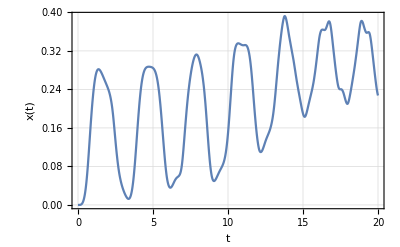

```mathematica
Plot[x[t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","x(t)"},Frame->True,GridLines-> Automatic]
```

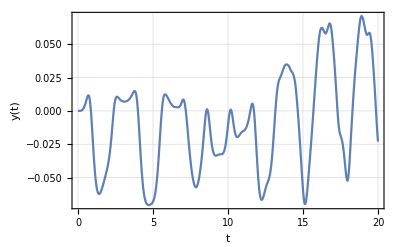

```mathematica
Plot[y[t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","y(t)"},Frame->True,GridLines-> Automatic]
```

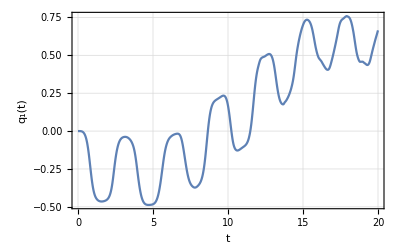

```mathematica
Plot[Subscript[q, 1][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_1(t)"},Frame->True,GridLines-> Automatic]
```

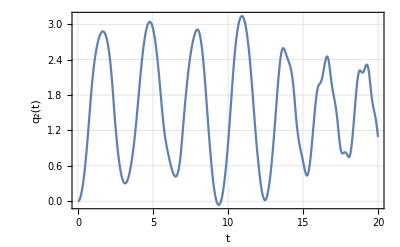

```mathematica
Plot[Subscript[q, 2][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_2(t)"},Frame->True,GridLines-> Automatic]
```

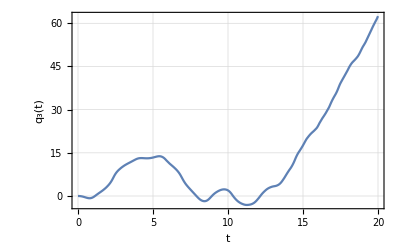

```mathematica
Plot[Subscript[q, 3][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_3(t)"},Frame->True,GridLines-> Automatic]
```

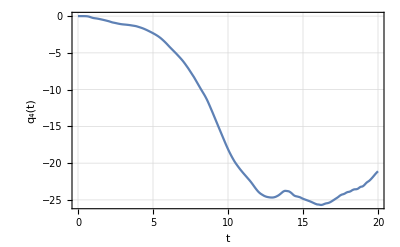

```mathematica
Plot[Subscript[q, 4][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_4(t)"},Frame->True,GridLines-> Automatic]
```

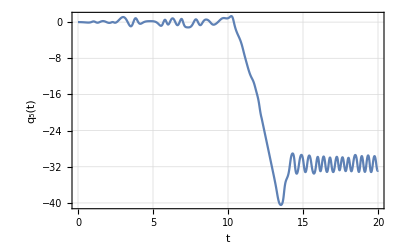

```mathematica
Plot[Subscript[q, 5][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_5(t)"},Frame->True,GridLines-> Automatic]
```

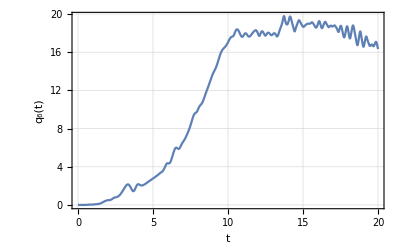

```mathematica
Plot[Subscript[q, 6][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_6(t)"},Frame->True,GridLines-> Automatic]
```

This plot may take some time to complete.

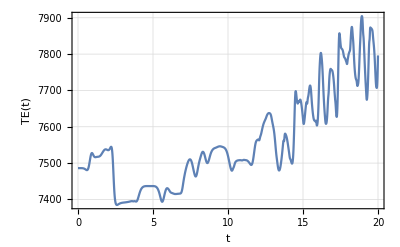

```mathematica
Plot[TEt/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","TE(t)"},Frame->True,GridLines-> Automatic]
```

```mathematica
x[t_]=x[t]/.solTest;
y[t_]=y[t]/.solTest;
Subscript[q, 1][t_]=Subscript[q, 1][t]/.solTest;
Subscript[q, 2][t_]=Subscript[q, 2][t]/.solTest;
Subscript[q, 3][t_]=Subscript[q, 3][t]/.solTest;
Subscript[q, 4][t_]=Subscript[q, 4][t]/.solTest;
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solTest;
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solTest;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicDynAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Riser graphic*)
Translate[GeometricTransformation[riserGraphic,Transpose[rotB]],{xBo,yBo,zBo}],

(*Shoulder graphic*)
Translate[GeometricTransformation[shoulderGraphic,Transpose[rotC]],{xCo,yCo,zCo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1Graphic,Transpose[rotD]],{xDo,yDo,zDo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2Graphic,Transpose[rotE]],{xEo,yEo,zEo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3Graphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wrist1Graphic,Transpose[rotG]],{xGo,yGo,zGo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wrist2Graphic,Transpose[rotH]],{xHo,yHo,zHo}]
};
```

```mathematica
robotGraphicDynAnimT[t_]=robotGraphicDynAnim;
```

Loop over time

```mathematica
tf=20;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

### Controller design

We have decided to try a proportional plus integral plus derivative (PID) control law for each motor.  To implement this we will treat each motor torque/force as a state.  So the integration will be performed by integrating the state equations, this implies that we must take two derivatives of the error, which can be problematic if the error is noisy.  This implies our desired path must be smooth up to second derivatives in time.

#### Control laws and control equations of motion

Clear everything again.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
```

```mathematica
Subscript[F, motx]=.
Subscript[F, moty]=.
Subscript[T, mot][1]=.
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
Subscript[T, mot][5]=.
Subscript[T, mot][6]=.
Subscript[F, toolx]=.
Subscript[F, tooly]=.
Subscript[F, toolz]=.
Subscript[T, toolx]=.
Subscript[T, tooly]=.
Subscript[T, toolz]=.
```

```mathematica
ω=.
```

Here are the state equations for motor force and torque, desired minus actual is the error in a given state.  I will replace the place holder symbols for motor forces and torques with the states defined here later.

Base x-motor

```mathematica
err[1]=Subscript[x, d][t] - x[t];
eqM[1]=Subscript[Fm, x]'[t] - Subscript[K, Int][1]err[1] - Subscript[K, prop][1]D[err[1],t]- Subscript[K, deriv][1]D[err[1],{t,2}]
```

-K_Int[1] (-x[t]+x_d[t])+Fm_x'[t]-K_prop[1] (-x'[t]+x_d'[t])-K_deriv[1] (-x''[t]+x_d''[t])

Base y-motor

```mathematica
err[2]=Subscript[y, d][t] - y[t];
eqM[2]=Subscript[Fm, y]'[t] - Subscript[K, Int][2]err[2] - Subscript[K, prop][2]D[err[2],t]- Subscript[K, deriv][2]D[err[2],{t,2}]
```

-K_Int[2] (-y[t]+y_d[t])+Fm_y'[t]-K_prop[2] (-y'[t]+y_d'[t])-K_deriv[2] (-y''[t]+y_d''[t])

q_1-motor

```mathematica
err[3]=Subscript[q, d1][t] - Subscript[q, 1][t];
eqM[3]=Subscript[Tm, 1]'[t] - Subscript[K, Int][3]err[3] - Subscript[K, prop][3]D[err[3],t]- Subscript[K, deriv][3]D[err[3],{t,2}]
```

-K_Int[3] (-q_1[t]+q_d1[t])-K_prop[3] (-q_1'[t]+q_d1'[t])+Tm_1'[t]-K_deriv[3] (-q_1''[t]+q_d1''[t])

q_2-motor

```mathematica
err[4]=Subscript[q, d2][t] - Subscript[q, 2][t];
eqM[4]=Subscript[Tm, 2]'[t] - Subscript[K, Int][4]err[4] - Subscript[K, prop][4]D[err[4],t]- Subscript[K, deriv][4]D[err[4],{t,2}]
```

-K_Int[4] (-q_2[t]+q_d2[t])-K_prop[4] (-q_2'[t]+q_d2'[t])+Tm_2'[t]-K_deriv[4] (-q_2''[t]+q_d2''[t])

q_3-motor

```mathematica
err[5]=Subscript[q, d3][t] - Subscript[q, 3][t];
eqM[5]=Subscript[Tm, 3]'[t] - Subscript[K, Int][5]err[5] - Subscript[K, prop][5]D[err[5],t]- Subscript[K, deriv][5]D[err[5],{t,2}]
```

-K_Int[5] (-q_3[t]+q_d3[t])-K_prop[5] (-q_3'[t]+q_d3'[t])+Tm_3'[t]-K_deriv[5] (-q_3''[t]+q_d3''[t])

q_4-motor

```mathematica
err[6]=Subscript[q, d4][t] - Subscript[q, 4][t];
eqM[6]=Subscript[Tm, 4]'[t] - Subscript[K, Int][6]err[6] - Subscript[K, prop][6]D[err[6],t]- Subscript[K, deriv][6]D[err[6],{t,2}]
```

-K_Int[6] (-q_4[t]+q_d4[t])-K_prop[6] (-q_4'[t]+q_d4'[t])+Tm_4'[t]-K_deriv[6] (-q_4''[t]+q_d4''[t])

q_5-motor

```mathematica
err[7]=Subscript[q, d5][t] - Subscript[q, 5][t];
eqM[7]=Subscript[Tm, 5]'[t] - Subscript[K, Int][7]err[7] - Subscript[K, prop][7]D[err[7],t]- Subscript[K, deriv][7]D[err[7],{t,2}]
```

-K_Int[7] (-q_5[t]+q_d5[t])-K_prop[7] (-q_5'[t]+q_d5'[t])+Tm_5'[t]-K_deriv[7] (-q_5''[t]+q_d5''[t])

q_6-motor

```mathematica
err[8]=Subscript[q, d6][t] - Subscript[q, 6][t];
eqM[8]=Subscript[Tm, 6]'[t] - Subscript[K, Int][8]err[8] - Subscript[K, prop][8]D[err[8],t]- Subscript[K, deriv][8]D[err[8],{t,2}]
```

-K_Int[8] (-q_6[t]+q_d6[t])-K_prop[8] (-q_6'[t]+q_d6'[t])+Tm_6'[t]-K_deriv[8] (-q_6''[t]+q_d6''[t])

Replace the place holders with the states for motor forces and torques.

```mathematica
eqC[1]=eqT[1]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[2]=eqT[2]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[3]=eqT[3]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[4]=eqT[4]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[5]=eqT[5]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[6]=eqT[6]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[7]=eqT[7]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[8]=eqT[8]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

Now we want to design the controller gains based on the step response of the system at a given motor.  We will do this by holding all the other states constant for the given motor control constant determination.  We will also linearize the system equations so we can then use pole placement techniques to size the gains.

#### Control gains base x-motor

Base x-motor. Here we fixate all the other movements.

```mathematica
eqG[1]=eqC[1]//.{y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Fm_x[t]-761.707 x''[t]

Linearize the equation.

```mathematica
eqL[1]=Normal[Series[eqG[1],{x[t],0,1},{x'[t],0,1}]]
```

0.+Fm_x[t]-761.707 x''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[1]=D[eqL[1],t]
```

Fm_x'[t]-761.707 x^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[1]=Solve[eqM[1]==0,Subscript[Fm, x]'[t]]//First
```

{Fm_x'[t]→-x[t] K_Int[1]+K_Int[1] x_d[t]-K_prop[1] x'[t]+K_prop[1] x_d'[t]-K_deriv[1] x''[t]+K_deriv[1] x_d''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[1]=eqLd[1]//.solM[1]
```

-x[t] K_Int[1]+K_Int[1] x_d[t]-K_prop[1] x'[t]+K_prop[1] x_d'[t]-K_deriv[1] x''[t]+K_deriv[1] x_d''[t]-761.707 x^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[1]=eqLf[1]//.{Derivative[n_][x][t]->s^n,x[t]->1,Subscript[x, d][t]->0,Subscript[x, d]'[t]->0,Subscript[x, d]''[t]->0}
```

-761.707 s^3-s^2 K_deriv[1]-K_Int[1]-s K_prop[1]

Put the characteristic equation in standard form.

```mathematica
charEq[1]=charEq[1]/Coefficient[charEq[1],s^3]//Expand
```

1. s^3+0.00131284 s^2 K_deriv[1]+0.00131284 K_Int[1]+0.00131284 s K_prop[1]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[1]=Expand[(s+Subscript[a, 1])(s^2+ 2 Subscript[ζ, 1] Subscript[ω, n1] s + Subscript[ω, n1]^2)]
```

s^3+s^2 a_1+2 s^2 ζ_1 ω_n1+2 s a_1 ζ_1 ω_n1+s ω_n1^2+a_1 ω_n1^2

The time to peak is defined as

```mathematica
eqTp[1]=Subscript[t, p1]== π/(Subscript[ω, n1] √(1-Subscript[ζ, 1]^2));
```

The two percent settling time is given by

```mathematica
eqTs[1]=Subscript[t, s1]== 4/(Subscript[ζ, 1] Subscript[ω, n1]);
```

```mathematica
solZW[1]=Solve[{eqTp[1],eqTs[1]},{Subscript[ζ, 1],Subscript[ω, n1]}][[2]]
```

{ζ_1→(4 t_p1)/(√(16 t_p1^2+π^2 t_s1^2)),ω_n1→(√(16 t_p1^2+π^2 t_s1^2))/(t_p1 t_s1)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[1]=Coefficient[charEq[1],s^2]==Coefficient[charDesired[1],s^2]/.solZW[1]
```

0.00131284 K_deriv[1]==a_1+8/t_s1

```mathematica
eqGain2[1]=Coefficient[charEq[1],s]==Coefficient[charDesired[1],s]/.solZW[1]
```

0.00131284 K_prop[1]==(8 a_1)/t_s1+(16 t_p1^2+π^2 t_s1^2)/(t_p1^2 t_s1^2)

```mathematica
eqGain3[1]=(charEq[1]/.s->0)==(charDesired[1]/.s->0)/.solZW[1]
```

0.+0.00131284 K_Int[1]==(a_1 (16 t_p1^2+π^2 t_s1^2))/(t_p1^2 t_s1^2)

Solve for the controller gains.

```mathematica
solGains[1]=Solve[{eqGain1[1],eqGain2[1],eqGain3[1]},{Subscript[K, prop][1],Subscript[K, Int][1],Subscript[K, deriv][1]}]//First
```

{K_prop[1]→761.707 ((8. a_1)/t_s1+(1. (16. t_p1^2+9.8696 t_s1^2))/(t_p1^2 t_s1^2)),K_Int[1]→761.707 (0.+(1. a_1 (16. t_p1^2+9.8696 t_s1^2))/(t_p1^2 t_s1^2)),K_deriv[1]→761.707 (1. a_1+8./t_s1)}

Now set the time constants.

```mathematica
tConstRules[1]={Subscript[a, 1]->100,Subscript[t, p1]->1/4,Subscript[t, s1]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[x, d][t_]:=stepMag UnitStep[t]
stepSol[1]=NDSolve[{(eqG[1]/.solGains[1]/.tConstRules[1])==0,(eqM[1]/.solGains[1]/.tConstRules[1])==0,x'[Subscript[t, 0]]==0,x[Subscript[t, 0]]==0,Subscript[Fm, x][Subscript[t, 0]]==0},{x,Subscript[Fm, x]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{x→InterpolatingFunction[…],Fm_x→InterpolatingFunction[…]}}

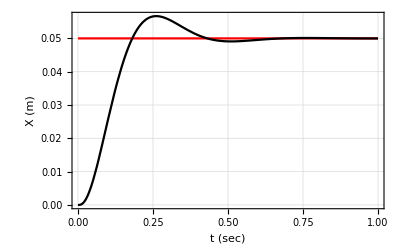

```mathematica
Plot[{Subscript[x, d][t],x[t]/.stepSol[1]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","X (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

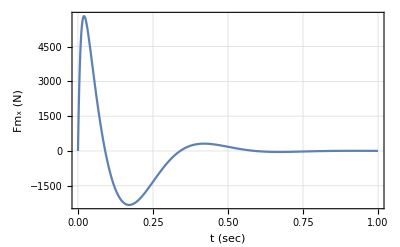

```mathematica
Plot[Subscript[Fm, x][t]/.stepSol[1],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_x (N)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 1350 pounds peak load.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[x, d][t_]:=(5 t^2+ 3 t + 1)/100 (* cm*)
trackSol[1]=NDSolve[{(eqG[1]/.solGains[1]/.tConstRules[1])==0,(eqM[1]/.solGains[1]/.tConstRules[1])==0,x'[Subscript[t, 0]]==0,x[Subscript[t, 0]]==0,Subscript[Fm, x][Subscript[t, 0]]==0},{x,Subscript[Fm, x]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{x→InterpolatingFunction[…],Fm_x→InterpolatingFunction[…]}}

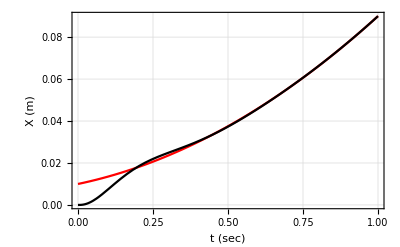

```mathematica
Plot[{Subscript[x, d][t],x[t]/.trackSol[1]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","X (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

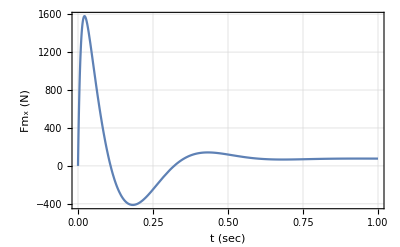

```mathematica
Plot[Subscript[Fm, x][t]/.trackSol[1],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_x (N)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[x, d][t_]=.
```

#### Control gains base y-motor

Base y-motor. Here we fixate all the other movements.

```mathematica
eqG[2]=eqC[2]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Fm_y[t]-761.707 y''[t]

Linearize the equation.

```mathematica
eqL[2]=Normal[Series[eqG[2],{y[t],0,1},{y'[t],0,1}]]
```

0.+Fm_y[t]-761.707 y''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[2]=D[eqL[2],t]
```

Fm_y'[t]-761.707 y^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[2]=Solve[eqM[2]==0,Subscript[Fm, y]'[t]]//First
```

{Fm_y'[t]→-y[t] K_Int[2]+K_Int[2] y_d[t]-K_prop[2] y'[t]+K_prop[2] y_d'[t]-K_deriv[2] y''[t]+K_deriv[2] y_d''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[2]=eqLd[2]//.solM[2]
```

-y[t] K_Int[2]+K_Int[2] y_d[t]-K_prop[2] y'[t]+K_prop[2] y_d'[t]-K_deriv[2] y''[t]+K_deriv[2] y_d''[t]-761.707 y^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[2]=eqLf[2]//.{Derivative[n_][y][t]->s^n,y[t]->1,Subscript[y, d][t]->0,Subscript[y, d]'[t]->0,Subscript[y, d]''[t]->0}
```

-761.707 s^3-s^2 K_deriv[2]-K_Int[2]-s K_prop[2]

Put the characteristic equation in standard form.

```mathematica
charEq[2]=charEq[2]/Coefficient[charEq[2],s^3]//Expand
```

1. s^3+0.00131284 s^2 K_deriv[2]+0.00131284 K_Int[2]+0.00131284 s K_prop[2]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[2]=Expand[(s+Subscript[a, 2])(s^2+ 2 Subscript[ζ, 2] Subscript[ω, n2] s + Subscript[ω, n2]^2)]
```

s^3+s^2 a_2+2 s^2 ζ_2 ω_n2+2 s a_2 ζ_2 ω_n2+s ω_n2^2+a_2 ω_n2^2

The time to peak is defined as

```mathematica
eqTp[2]=Subscript[t, p2]== π/(Subscript[ω, n2] √(1-Subscript[ζ, 2]^2));
```

The two percent settling time is given by

```mathematica
eqTs[2]=Subscript[t, s2]== 4/(Subscript[ζ, 2] Subscript[ω, n2]);
```

```mathematica
solZW[2]=Solve[{eqTp[2],eqTs[2]},{Subscript[ζ, 2],Subscript[ω, n2]}][[2]]
```

{ζ_2→(4 t_p2)/(√(16 t_p2^2+π^2 t_s2^2)),ω_n2→(√(16 t_p2^2+π^2 t_s2^2))/(t_p2 t_s2)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[2]=Coefficient[charEq[2],s^2]==Coefficient[charDesired[2],s^2]/.solZW[2]
```

0.00131284 K_deriv[2]==a_2+8/t_s2

```mathematica
eqGain2[2]=Coefficient[charEq[2],s]==Coefficient[charDesired[2],s]/.solZW[2]
```

0.00131284 K_prop[2]==(8 a_2)/t_s2+(16 t_p2^2+π^2 t_s2^2)/(t_p2^2 t_s2^2)

```mathematica
eqGain3[2]=(charEq[2]/.s->0)==(charDesired[2]/.s->0)/.solZW[2]
```

0.+0.00131284 K_Int[2]==(a_2 (16 t_p2^2+π^2 t_s2^2))/(t_p2^2 t_s2^2)

Solve for the controller gains.

```mathematica
solGains[2]=Solve[{eqGain1[2],eqGain2[2],eqGain3[2]},{Subscript[K, prop][2],Subscript[K, Int][2],Subscript[K, deriv][2]}]//First
```

{K_prop[2]→761.707 ((8. a_2)/t_s2+(1. (16. t_p2^2+9.8696 t_s2^2))/(t_p2^2 t_s2^2)),K_Int[2]→761.707 (0.+(1. a_2 (16. t_p2^2+9.8696 t_s2^2))/(t_p2^2 t_s2^2)),K_deriv[2]→761.707 (1. a_2+8./t_s2)}

Now set the time constants.

```mathematica
tConstRules[2]={Subscript[a, 2]->100,Subscript[t, p2]->1/4,Subscript[t, s2]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[y, d][t_]:=stepMag UnitStep[t]
stepSol[2]=NDSolve[{(eqG[2]/.solGains[2]/.tConstRules[2])==0,(eqM[2]/.solGains[2]/.tConstRules[2])==0,y'[Subscript[t, 0]]==0,y[Subscript[t, 0]]==0,Subscript[Fm, y][Subscript[t, 0]]==0},{y,Subscript[Fm, y]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{y→InterpolatingFunction[…],Fm_y→InterpolatingFunction[…]}}

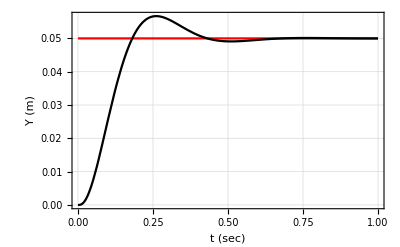

```mathematica
Plot[{Subscript[y, d][t],y[t]/.stepSol[2]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Y (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

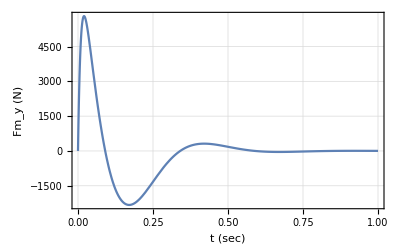

```mathematica
Plot[Subscript[Fm, y][t]/.stepSol[2],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_y (N)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 1350 pounds peak load.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[y, d][t_]:=(5 t^2+ 3 t + 1)/100 (* cm*)
trackSol[2]=NDSolve[{(eqG[2]/.solGains[2]/.tConstRules[2])==0,(eqM[2]/.solGains[2]/.tConstRules[2])==0,y'[Subscript[t, 0]]==0,y[Subscript[t, 0]]==0,Subscript[Fm, y][Subscript[t, 0]]==0},{y,Subscript[Fm, y]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{y→InterpolatingFunction[…],Fm_y→InterpolatingFunction[…]}}

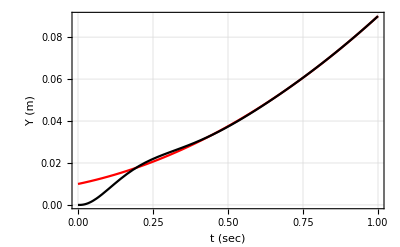

```mathematica
Plot[{Subscript[y, d][t],y[t]/.trackSol[2]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Y (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

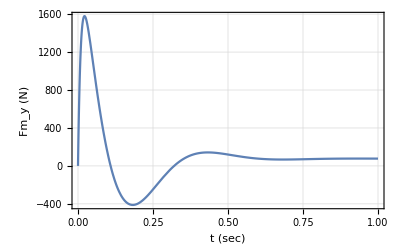

```mathematica
Plot[Subscript[Fm, y][t]/.trackSol[2],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_y (N)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[y, d][t_]=.
```

#### Control gains q_1-motor

q_1-motor. Here we fixate all the other movements.

```mathematica
eqG[3]=eqC[3]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Tm_1[t]+(1/4) (0.-79.3908 q_1'[t]^2)+(1/4) (0.-39.6954 q_1'[t]^2)+(1/6) (0.-11.0265 q_1'[t]^2)+(3/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.-11.0265 q_1'[t]^2)+(1/4) (0.-7.79417 q_1'[t]^2)+(1/4) (0.-3.46408 q_1'[t]^2)+(1/4) (0.-2.96921 q_1'[t]^2)+(2/3) (0.-2.16505 q_1'[t]^2)-(1/3) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.-2.16505 q_1'[t]^2)+(3/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.-2.16505 q_1'[t]^2)+(2/3) (0.-0.962244 q_1'[t]^2)-(5/6) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.-0.962244 q_1'[t]^2)+(3/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.-0.962244 q_1'[t]^2)+(2/3) (0.-0.82478 q_1'[t]^2)-(15/14) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.-0.82478 q_1'[t]^2)+(3/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.-0.82478 q_1'[t]^2)-(1/6) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+0.471303 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+0.471303 q_1'[t]^2)+(3/2) (0.+0.494868 q_1'[t]^2)-(73/42) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+0.494868 q_1'[t]^2)+(3/2) (0.+0.577346 q_1'[t]^2)-(3/2) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+0.577346 q_1'[t]^2)+(68/21) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+0.989736 q_1'[t]^2)+3 (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+1.15469 q_1'[t]^2)+(3/2) (0.+1.29903 q_1'[t]^2)-(-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+1.29903 q_1'[t]^2)+(5/12) (0.+1.31965 q_1'[t]^2)+(1/4) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+1.31965 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+1.31965 q_1'[t]^2)+(5/12) (0.+1.53959 q_1'[t]^2)+(1/4) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+1.53959 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+1.53959 q_1'[t]^2)-(1/6) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+1.64956 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+1.64956 q_1'[t]^2)-(1/6) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+1.73204 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+1.73204 q_1'[t]^2)-(1/6) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+1.92449 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+1.92449 q_1'[t]^2)+(5/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+2.59806 q_1'[t]^2)-(1/12) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+2.96921 q_1'[t]^2)-(1/12) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+3.46408 q_1'[t]^2)+(5/12) (0.+3.46408 q_1'[t]^2)+(1/4) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+3.46408 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+3.46408 q_1'[t]^2)+(5/12) (0.+4.4106 q_1'[t]^2)+(1/4) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+4.4106 q_1'[t]^2)-(1/2) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+4.4106 q_1'[t]^2)+(3/2) (0.+6.6159 q_1'[t]^2)-(1/6) (-Cos[q_1[t]]^2-Sin[q_1[t]]^2) (0.+6.6159 q_1'[t]^2)-(1/12) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+7.79417 q_1'[t]^2)+(5/3) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+13.2318 q_1'[t]^2)+(1/2) (0.+39.6954 q_1'[t]^2)-(1/12) (Cos[q_1[t]]^2+Sin[q_1[t]]^2) (0.+39.6954 q_1'[t]^2)-322.295 q_1''[t]-84.2373 (Cos[q_1[t]]^2+Sin[q_1[t]]^2) q_1''[t]

Linearize the equation.

```mathematica
eqL[3]=Normal[Series[eqG[3],{Subscript[q, 1][t],0,1},{Subscript[q, 1]'[t],0,1}]]
```

Tm_1[t]-406.532 q_1''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[3]=D[eqL[3],t]
```

Tm_1'[t]-406.532 q_1^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[3]=Solve[eqM[3]==0,Subscript[Tm, 1]'[t]]//First
```

{Tm_1'[t]→-K_Int[3] q_1[t]+K_Int[3] q_d1[t]-K_prop[3] q_1'[t]+K_prop[3] q_d1'[t]-K_deriv[3] q_1''[t]+K_deriv[3] q_d1''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[3]=eqLd[3]//.solM[3]
```

-K_Int[3] q_1[t]+K_Int[3] q_d1[t]-K_prop[3] q_1'[t]+K_prop[3] q_d1'[t]-K_deriv[3] q_1''[t]+K_deriv[3] q_d1''[t]-406.532 q_1^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[3]=eqLf[3]//.{Derivative[n_][Subscript[q, 1]][t]->s^n,Subscript[q, 1][t]->1,Subscript[q, d1][t]->0,Subscript[q, d1]'[t]->0,Subscript[q, d1]''[t]->0}
```

-406.532 s^3-s^2 K_deriv[3]-K_Int[3]-s K_prop[3]

Put the characteristic equation in standard form.

```mathematica
charEq[3]=charEq[3]/Coefficient[charEq[3],s^3]//Expand
```

1. s^3+0.00245983 s^2 K_deriv[3]+0.00245983 K_Int[3]+0.00245983 s K_prop[3]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[3]=Expand[(s+Subscript[a, 3])(s^2+ 2 Subscript[ζ, 3] Subscript[ω, n3] s + Subscript[ω, n3]^2)]
```

s^3+s^2 a_3+2 s^2 ζ_3 ω_n3+2 s a_3 ζ_3 ω_n3+s ω_n3^2+a_3 ω_n3^2

The time to peak is defined as

```mathematica
eqTp[3]=Subscript[t, p3]== π/(Subscript[ω, n3] √(1-Subscript[ζ, 3]^2));
```

The two percent settling time is given by

```mathematica
eqTs[3]=Subscript[t, s3]== 4/(Subscript[ζ, 3] Subscript[ω, n3]);
```

```mathematica
solZW[3]=Solve[{eqTp[3],eqTs[3]},{Subscript[ζ, 3],Subscript[ω, n3]}][[2]]
```

{ζ_3→(4 t_p3)/(√(16 t_p3^2+π^2 t_s3^2)),ω_n3→(√(16 t_p3^2+π^2 t_s3^2))/(t_p3 t_s3)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[3]=Coefficient[charEq[3],s^2]==Coefficient[charDesired[3],s^2]/.solZW[3]
```

0.00245983 K_deriv[3]==a_3+8/t_s3

```mathematica
eqGain2[3]=Coefficient[charEq[3],s]==Coefficient[charDesired[3],s]/.solZW[3]
```

0.00245983 K_prop[3]==(8 a_3)/t_s3+(16 t_p3^2+π^2 t_s3^2)/(t_p3^2 t_s3^2)

```mathematica
eqGain3[3]=(charEq[3]/.s->0)==(charDesired[3]/.s->0)/.solZW[3]
```

0.+0.00245983 K_Int[3]==(a_3 (16 t_p3^2+π^2 t_s3^2))/(t_p3^2 t_s3^2)

Solve for the controller gains.

```mathematica
solGains[3]=Solve[{eqGain1[3],eqGain2[3],eqGain3[3]},{Subscript[K, prop][3],Subscript[K, Int][3],Subscript[K, deriv][3]}]//First
```

{K_prop[3]→406.532 ((8. a_3)/t_s3+(1. (16. t_p3^2+9.8696 t_s3^2))/(t_p3^2 t_s3^2)),K_Int[3]→406.532 (0.+(1. a_3 (16. t_p3^2+9.8696 t_s3^2))/(t_p3^2 t_s3^2)),K_deriv[3]→406.532 (1. a_3+8./t_s3)}

Now set the time constants.

```mathematica
tConstRules[3]={Subscript[a, 3]->100,Subscript[t, p3]->1/4,Subscript[t, s3]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d1][t_]:=stepMag UnitStep[t]
stepSol[3]=NDSolve[{(eqG[3]/.solGains[3]/.tConstRules[3])==0,(eqM[3]/.solGains[3]/.tConstRules[3])==0,Subscript[q, 1]'[Subscript[t, 0]]==0,Subscript[q, 1][Subscript[t, 0]]==0,Subscript[Tm, 1][Subscript[t, 0]]==0},{Subscript[q, 1],Subscript[Tm, 1]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_1→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…]}}

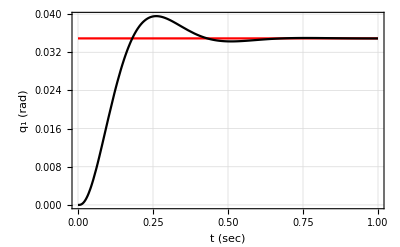

```mathematica
Plot[{Subscript[q, d1][t],Subscript[q, 1][t]/.stepSol[3]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_1 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

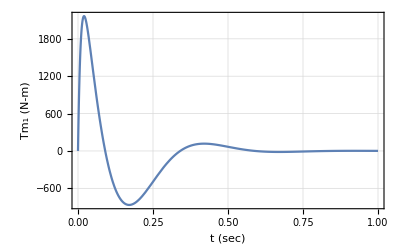

```mathematica
Plot[Subscript[Tm, 1][t]/.stepSol[3],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 1850 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d1][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[3]=NDSolve[{(eqG[3]/.solGains[3]/.tConstRules[3])==0,(eqM[3]/.solGains[3]/.tConstRules[3])==0,Subscript[q, 1]'[Subscript[t, 0]]==0,Subscript[q, 1][Subscript[t, 0]]==0,Subscript[Tm, 1][Subscript[t, 0]]==0},{Subscript[q, 1],Subscript[Tm, 1]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_1→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…]}}

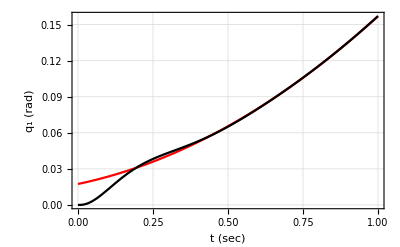

```mathematica
Plot[{Subscript[q, d1][t],Subscript[q, 1][t]/.trackSol[3]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_1 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

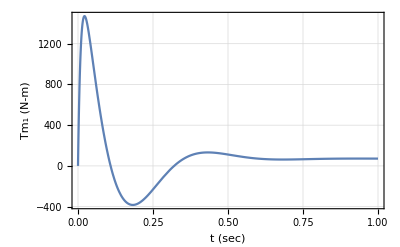

```mathematica
Plot[Subscript[Tm, 1][t]/.trackSol[3],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d1][t_]=.
```

#### Control gains q_2-motor

q_2-motor. Here we fixate all the other movements.

```mathematica
eqG[4]=eqC[4]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+1469.78 Cos[q_2[t]]+Tm_2[t]-260.631 q_2''[t]-58.0226 (Cos[q_2[t]]^2+Sin[q_2[t]]^2) q_2''[t]

Linearize the equation.

```mathematica
eqL[4]=Normal[Series[eqG[4],{Subscript[q, 2][t],0,1},{Subscript[q, 2]'[t],0,1}]]
```

1469.78+Tm_2[t]-318.653 q_2''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[4]=D[eqL[4],t]
```

Tm_2'[t]-318.653 q_2^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[4]=Solve[eqM[4]==0,Subscript[Tm, 2]'[t]]//First
```

{Tm_2'[t]→-K_Int[4] q_2[t]+K_Int[4] q_d2[t]-K_prop[4] q_2'[t]+K_prop[4] q_d2'[t]-K_deriv[4] q_2''[t]+K_deriv[4] q_d2''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[4]=eqLd[4]//.solM[4]
```

-K_Int[4] q_2[t]+K_Int[4] q_d2[t]-K_prop[4] q_2'[t]+K_prop[4] q_d2'[t]-K_deriv[4] q_2''[t]+K_deriv[4] q_d2''[t]-318.653 q_2^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[4]=eqLf[4]//.{Derivative[n_][Subscript[q, 2]][t]->s^n,Subscript[q, 2][t]->1,Subscript[q, d2][t]->0,Subscript[q, d2]'[t]->0,Subscript[q, d2]''[t]->0}
```

-318.653 s^3-s^2 K_deriv[4]-K_Int[4]-s K_prop[4]

Put the characteristic equation in standard form.

```mathematica
charEq[4]=charEq[4]/Coefficient[charEq[4],s^3]//Expand
```

1. s^3+0.00313821 s^2 K_deriv[4]+0.00313821 K_Int[4]+0.00313821 s K_prop[4]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[4]=Expand[(s+Subscript[a, 4])(s^2+ 2 Subscript[ζ, 4] Subscript[ω, n4] s + Subscript[ω, n4]^2)]
```

s^3+s^2 a_4+2 s^2 ζ_4 ω_n4+2 s a_4 ζ_4 ω_n4+s ω_n4^2+a_4 ω_n4^2

The time to peak is defined as

```mathematica
eqTp[4]=Subscript[t, p4]== π/(Subscript[ω, n4] √(1-Subscript[ζ, 4]^2));
```

The two percent settling time is given by

```mathematica
eqTs[4]=Subscript[t, s4]== 4/(Subscript[ζ, 4] Subscript[ω, n4]);
```

```mathematica
solZW[4]=Solve[{eqTp[4],eqTs[4]},{Subscript[ζ, 4],Subscript[ω, n4]}][[2]]
```

{ζ_4→(4 t_p4)/(√(16 t_p4^2+π^2 t_s4^2)),ω_n4→(√(16 t_p4^2+π^2 t_s4^2))/(t_p4 t_s4)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[4]=Coefficient[charEq[4],s^2]==Coefficient[charDesired[4],s^2]/.solZW[4]
```

0.00313821 K_deriv[4]==a_4+8/t_s4

```mathematica
eqGain2[4]=Coefficient[charEq[4],s]==Coefficient[charDesired[4],s]/.solZW[4]
```

0.00313821 K_prop[4]==(8 a_4)/t_s4+(16 t_p4^2+π^2 t_s4^2)/(t_p4^2 t_s4^2)

```mathematica
eqGain3[4]=(charEq[4]/.s->0)==(charDesired[4]/.s->0)/.solZW[4]
```

0.+0.00313821 K_Int[4]==(a_4 (16 t_p4^2+π^2 t_s4^2))/(t_p4^2 t_s4^2)

Solve for the controller gains.

```mathematica
solGains[4]=Solve[{eqGain1[4],eqGain2[4],eqGain3[4]},{Subscript[K, prop][4],Subscript[K, Int][4],Subscript[K, deriv][4]}]//First
```

{K_prop[4]→318.653 ((8. a_4)/t_s4+(1. (16. t_p4^2+9.8696 t_s4^2))/(t_p4^2 t_s4^2)),K_Int[4]→318.653 (0.+(1. a_4 (16. t_p4^2+9.8696 t_s4^2))/(t_p4^2 t_s4^2)),K_deriv[4]→318.653 (1. a_4+8./t_s4)}

Now set the time constants.

```mathematica
tConstRules[4]={Subscript[a, 4]->10,Subscript[t, p4]->1/4,Subscript[t, s4]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d2][t_]:=stepMag UnitStep[t]
stepSol[4]=NDSolve[{(eqG[4]/.solGains[4]/.tConstRules[4])==0,(eqM[4]/.solGains[4]/.tConstRules[4])==0,Subscript[q, 2]'[Subscript[t, 0]]==0,Subscript[q, 2][Subscript[t, 0]]==0,Subscript[Tm, 2][Subscript[t, 0]]==0},{Subscript[q, 2],Subscript[Tm, 2]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_2→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…]}}

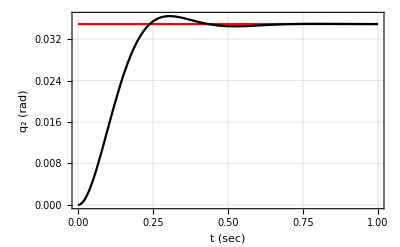

```mathematica
Plot[{Subscript[q, d2][t],Subscript[q, 2][t]/.stepSol[4]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_2 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red. Notice here how the gravity load affects the settling time.  There is more undershoot than for the motors wothout gravity load.

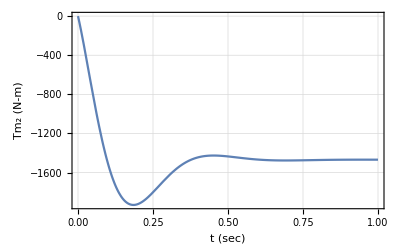

```mathematica
Plot[Subscript[Tm, 2][t]/.stepSol[4],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 1600 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d2][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[4]=NDSolve[{(eqG[4]/.solGains[4]/.tConstRules[4])==0,(eqM[4]/.solGains[4]/.tConstRules[4])==0,Subscript[q, 2]'[Subscript[t, 0]]==0,Subscript[q, 2][Subscript[t, 0]]==0,Subscript[Tm, 2][Subscript[t, 0]]==0},{Subscript[q, 2],Subscript[Tm, 2]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_2→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…]}}

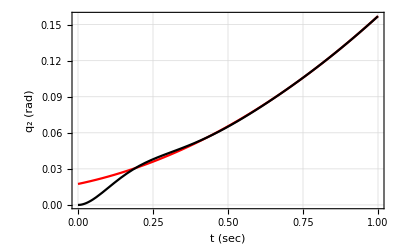

```mathematica
Plot[{Subscript[q, d2][t],Subscript[q, 2][t]/.trackSol[4]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_2 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

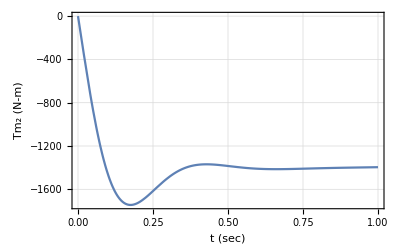

```mathematica
Plot[Subscript[Tm, 2][t]/.trackSol[4],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d2][t_]=.
```

#### Control gains q_3-motor

q_3-motor. Here we fixate all the other movements.

```mathematica
eqG[5]=eqC[5]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+161.976 Cos[q_3[t]]+Tm_3[t]-19.7913 q_3''[t]-8.48869 (Cos[q_3[t]]^2+Sin[q_3[t]]^2) q_3''[t]

Linearize the equation.

```mathematica
eqL[5]=Normal[Series[eqG[5],{Subscript[q, 3][t],0,1},{Subscript[q, 3]'[t],0,1}]]
```

161.976+Tm_3[t]-28.28 q_3''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[5]=D[eqL[5],t]
```

Tm_3'[t]-28.28 q_3^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[5]=Solve[eqM[5]==0,Subscript[Tm, 3]'[t]]//First
```

{Tm_3'[t]→-K_Int[5] q_3[t]+K_Int[5] q_d3[t]-K_prop[5] q_3'[t]+K_prop[5] q_d3'[t]-K_deriv[5] q_3''[t]+K_deriv[5] q_d3''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[5]=eqLd[5]//.solM[5]
```

-K_Int[5] q_3[t]+K_Int[5] q_d3[t]-K_prop[5] q_3'[t]+K_prop[5] q_d3'[t]-K_deriv[5] q_3''[t]+K_deriv[5] q_d3''[t]-28.28 q_3^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[5]=eqLf[5]//.{Derivative[n_][Subscript[q, 3]][t]->s^n,Subscript[q, 3][t]->1,Subscript[q, d3][t]->0,Subscript[q, d3]'[t]->0,Subscript[q, d3]''[t]->0}
```

-28.28 s^3-s^2 K_deriv[5]-K_Int[5]-s K_prop[5]

Put the characteristic equation in standard form.

```mathematica
charEq[5]=charEq[5]/Coefficient[charEq[5],s^3]//Expand
```

1. s^3+0.0353607 s^2 K_deriv[5]+0.0353607 K_Int[5]+0.0353607 s K_prop[5]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[5]=Expand[(s+Subscript[a, 5])(s^2+ 2 Subscript[ζ, 5] Subscript[ω, n5] s + Subscript[ω, n5]^2)]
```

s^3+s^2 a_5+2 s^2 ζ_5 ω_n5+2 s a_5 ζ_5 ω_n5+s ω_n5^2+a_5 ω_n5^2

The time to peak is defined as

```mathematica
eqTp[5]=Subscript[t, p5]== π/(Subscript[ω, n5] √(1-Subscript[ζ, 5]^2));
```

The two percent settling time is given by

```mathematica
eqTs[5]=Subscript[t, s5]== 4/(Subscript[ζ, 5] Subscript[ω, n5]);
```

```mathematica
solZW[5]=Solve[{eqTp[5],eqTs[5]},{Subscript[ζ, 5],Subscript[ω, n5]}][[2]]
```

{ζ_5→(4 t_p5)/(√(16 t_p5^2+π^2 t_s5^2)),ω_n5→(√(16 t_p5^2+π^2 t_s5^2))/(t_p5 t_s5)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[5]=Coefficient[charEq[5],s^2]==Coefficient[charDesired[5],s^2]/.solZW[5]
```

0.0353607 K_deriv[5]==a_5+8/t_s5

```mathematica
eqGain2[5]=Coefficient[charEq[5],s]==Coefficient[charDesired[5],s]/.solZW[5]
```

0.0353607 K_prop[5]==(8 a_5)/t_s5+(16 t_p5^2+π^2 t_s5^2)/(t_p5^2 t_s5^2)

```mathematica
eqGain3[5]=(charEq[5]/.s->0)==(charDesired[5]/.s->0)/.solZW[5]
```

0.+0.0353607 K_Int[5]==(a_5 (16 t_p5^2+π^2 t_s5^2))/(t_p5^2 t_s5^2)

Solve for the controller gains.

```mathematica
solGains[5]=Solve[{eqGain1[5],eqGain2[5],eqGain3[5]},{Subscript[K, prop][5],Subscript[K, Int][5],Subscript[K, deriv][5]}]//First
```

{K_prop[5]→28.28 ((8. a_5)/t_s5+(1. (16. t_p5^2+9.8696 t_s5^2))/(t_p5^2 t_s5^2)),K_Int[5]→28.28 (0.+(1. a_5 (16. t_p5^2+9.8696 t_s5^2))/(t_p5^2 t_s5^2)),K_deriv[5]→28.28 (1. a_5+8./t_s5)}

Now set the time constants.

```mathematica
tConstRules[5]={Subscript[a, 5]->10,Subscript[t, p5]->1/4,Subscript[t, s5]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d3][t_]:=stepMag UnitStep[t]
stepSol[5]=NDSolve[{(eqG[5]/.solGains[5]/.tConstRules[5])==0,(eqM[5]/.solGains[5]/.tConstRules[5])==0,Subscript[q, 3]'[Subscript[t, 0]]==0,Subscript[q, 3][Subscript[t, 0]]==0,Subscript[Tm, 3][Subscript[t, 0]]==0},{Subscript[q, 3],Subscript[Tm, 3]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_3→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…]}}

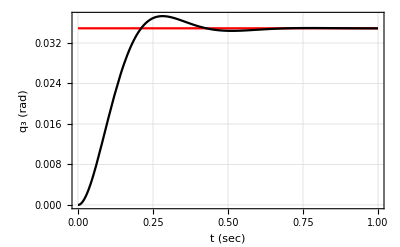

```mathematica
Plot[{Subscript[q, d3][t],Subscript[q, 3][t]/.stepSol[5]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_3 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red. Notice here how the gravity load affects the settling time.  There is more undershoot than for the motors wothout gravity load.

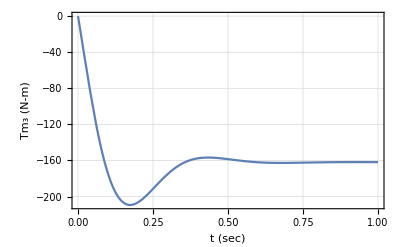

```mathematica
Plot[Subscript[Tm, 3][t]/.stepSol[5],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 175 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d3][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[5]=NDSolve[{(eqG[5]/.solGains[5]/.tConstRules[5])==0,(eqM[5]/.solGains[5]/.tConstRules[5])==0,Subscript[q, 3]'[Subscript[t, 0]]==0,Subscript[q, 3][Subscript[t, 0]]==0,Subscript[Tm, 3][Subscript[t, 0]]==0},{Subscript[q, 3],Subscript[Tm, 3]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_3→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…]}}

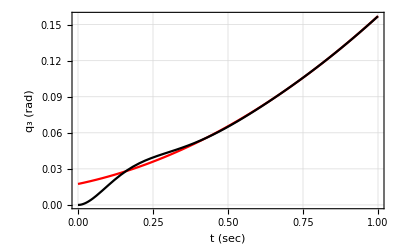

```mathematica
Plot[{Subscript[q, d3][t],Subscript[q, 3][t]/.trackSol[5]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_3 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

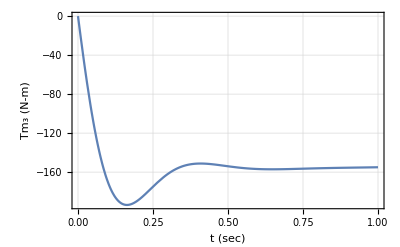

```mathematica
Plot[Subscript[Tm, 3][t]/.trackSol[5],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d3][t_]=.
```

#### Control gains q_4-motor

q_4-motor. Here we fixate all the other movements.

```mathematica
eqG[6]=eqC[6]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Tm_4[t]+(5/6) (0.-1.92449 q_4''[t])+(1/3) (0.-1.73204 q_4''[t])-1.63302 q_4''[t]

Linearize the equation.

```mathematica
eqL[6]=Normal[Series[eqG[6],{Subscript[q, 4][t],0,1},{Subscript[q, 4]'[t],0,1}]]
```

0.+Tm_4[t]+(5/6) (0.-1.92449 q_4''[t])+(1/3) (0.-1.73204 q_4''[t])-1.63302 q_4''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[6]=D[eqL[6],t]
```

Tm_4'[t]-3.81411 q_4^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[6]=Solve[eqM[6]==0,Subscript[Tm, 4]'[t]]//First
```

{Tm_4'[t]→-K_Int[6] q_4[t]+K_Int[6] q_d4[t]-K_prop[6] q_4'[t]+K_prop[6] q_d4'[t]-K_deriv[6] q_4''[t]+K_deriv[6] q_d4''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[6]=eqLd[6]//.solM[6]
```

-K_Int[6] q_4[t]+K_Int[6] q_d4[t]-K_prop[6] q_4'[t]+K_prop[6] q_d4'[t]-K_deriv[6] q_4''[t]+K_deriv[6] q_d4''[t]-3.81411 q_4^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[6]=eqLf[6]//.{Derivative[n_][Subscript[q, 4]][t]->s^n,Subscript[q, 4][t]->1,Subscript[q, d4][t]->0,Subscript[q, d4]'[t]->0,Subscript[q, d4]''[t]->0}
```

-3.81411 s^3-s^2 K_deriv[6]-K_Int[6]-s K_prop[6]

Put the characteristic equation in standard form.

```mathematica
charEq[6]=charEq[6]/Coefficient[charEq[6],s^3]//Expand
```

1. s^3+0.262184 s^2 K_deriv[6]+0.262184 K_Int[6]+0.262184 s K_prop[6]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[6]=Expand[(s+Subscript[a, 6])(s^2+ 2 Subscript[ζ, 6] Subscript[ω, n6] s + Subscript[ω, n6]^2)]
```

s^3+s^2 a_6+2 s^2 ζ_6 ω_n6+2 s a_6 ζ_6 ω_n6+s ω_n6^2+a_6 ω_n6^2

The time to peak is defined as

```mathematica
eqTp[6]=Subscript[t, p6]== π/(Subscript[ω, n6] √(1-Subscript[ζ, 6]^2));
```

The two percent settling time is given by

```mathematica
eqTs[6]=Subscript[t, s6]== 4/(Subscript[ζ, 6] Subscript[ω, n6]);
```

```mathematica
solZW[6]=Solve[{eqTp[6],eqTs[6]},{Subscript[ζ, 6],Subscript[ω, n6]}][[2]]
```

{ζ_6→(4 t_p6)/(√(16 t_p6^2+π^2 t_s6^2)),ω_n6→(√(16 t_p6^2+π^2 t_s6^2))/(t_p6 t_s6)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[6]=Coefficient[charEq[6],s^2]==Coefficient[charDesired[6],s^2]/.solZW[6]
```

0.262184 K_deriv[6]==a_6+8/t_s6

```mathematica
eqGain2[6]=Coefficient[charEq[6],s]==Coefficient[charDesired[6],s]/.solZW[6]
```

0.262184 K_prop[6]==(8 a_6)/t_s6+(16 t_p6^2+π^2 t_s6^2)/(t_p6^2 t_s6^2)

```mathematica
eqGain3[6]=(charEq[6]/.s->0)==(charDesired[6]/.s->0)/.solZW[6]
```

0.+0.262184 K_Int[6]==(a_6 (16 t_p6^2+π^2 t_s6^2))/(t_p6^2 t_s6^2)

Solve for the controller gains.

```mathematica
solGains[6]=Solve[{eqGain1[6],eqGain2[6],eqGain3[6]},{Subscript[K, prop][6],Subscript[K, Int][6],Subscript[K, deriv][6]}]//First
```

{K_prop[6]→3.81411 ((8. a_6)/t_s6+(1. (16. t_p6^2+9.8696 t_s6^2))/(t_p6^2 t_s6^2)),K_Int[6]→3.81411 (0.+(1. a_6 (16. t_p6^2+9.8696 t_s6^2))/(t_p6^2 t_s6^2)),K_deriv[6]→3.81411 (1. a_6+8./t_s6)}

Now set the time constants.

```mathematica
tConstRules[6]={Subscript[a, 6]->100,Subscript[t, p6]->1/4,Subscript[t, s6]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d4][t_]:=stepMag UnitStep[t]
stepSol[6]=NDSolve[{(eqG[6]/.solGains[6]/.tConstRules[6])==0,(eqM[6]/.solGains[6]/.tConstRules[6])==0,Subscript[q, 4]'[Subscript[t, 0]]==0,Subscript[q, 4][Subscript[t, 0]]==0,Subscript[Tm, 4][Subscript[t, 0]]==0},{Subscript[q, 4],Subscript[Tm, 4]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_4→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…]}}

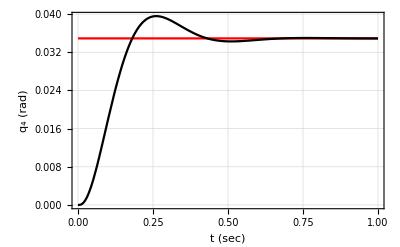

```mathematica
Plot[{Subscript[q, d4][t],Subscript[q, 4][t]/.stepSol[6]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_4 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

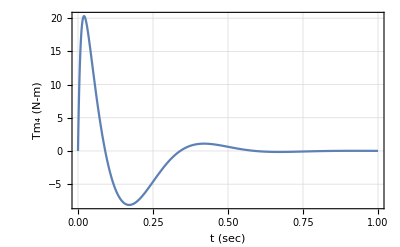

```mathematica
Plot[Subscript[Tm, 4][t]/.stepSol[6],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 7.5 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d4][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[6]=NDSolve[{(eqG[6]/.solGains[6]/.tConstRules[6])==0,(eqM[6]/.solGains[6]/.tConstRules[6])==0,Subscript[q, 4]'[Subscript[t, 0]]==0,Subscript[q, 4][Subscript[t, 0]]==0,Subscript[Tm, 4][Subscript[t, 0]]==0},{Subscript[q, 4],Subscript[Tm, 4]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_4→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…]}}

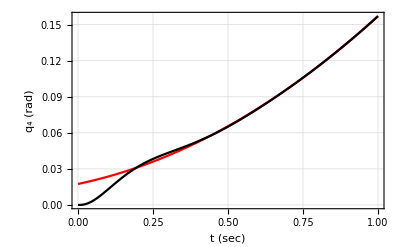

```mathematica
Plot[{Subscript[q, d4][t],Subscript[q, 4][t]/.trackSol[6]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_4 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

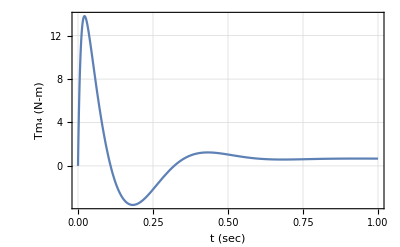

```mathematica
Plot[Subscript[Tm, 4][t]/.trackSol[6],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d4][t_]=.
```

#### Control gains q_5-motor

q_5-motor. Here we fixate all the other movements.

```mathematica
eqG[7]=eqC[7]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Tm_5[t]+(5/21) (0.+19.4186 Cos[q_5[t]]-0.471303 q_5''[t])-0.0803616 q_5''[t]

Linearize the equation.

```mathematica
eqL[7]=Normal[Series[eqG[7],{Subscript[q, 5][t],0,1},{Subscript[q, 5]'[t],0,1}]]
```

4.62348+Tm_5[t]-0.192577 q_5''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[7]=D[eqL[7],t]
```

Tm_5'[t]-0.192577 q_5^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[7]=Solve[eqM[7]==0,Subscript[Tm, 5]'[t]]//First
```

{Tm_5'[t]→-K_Int[7] q_5[t]+K_Int[7] q_d5[t]-K_prop[7] q_5'[t]+K_prop[7] q_d5'[t]-K_deriv[7] q_5''[t]+K_deriv[7] q_d5''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[7]=eqLd[7]//.solM[7]
```

-K_Int[7] q_5[t]+K_Int[7] q_d5[t]-K_prop[7] q_5'[t]+K_prop[7] q_d5'[t]-K_deriv[7] q_5''[t]+K_deriv[7] q_d5''[t]-0.192577 q_5^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[7]=eqLf[7]//.{Derivative[n_][Subscript[q, 5]][t]->s^n,Subscript[q, 5][t]->1,Subscript[q, d5][t]->0,Subscript[q, d5]'[t]->0,Subscript[q, d5]''[t]->0}
```

-0.192577 s^3-s^2 K_deriv[7]-K_Int[7]-s K_prop[7]

Put the characteristic equation in standard form.

```mathematica
charEq[7]=charEq[7]/Coefficient[charEq[7],s^3]//Expand
```

1. s^3+5.19274 s^2 K_deriv[7]+5.19274 K_Int[7]+5.19274 s K_prop[7]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[7]=Expand[(s+Subscript[a, 7])(s^2+ 2 Subscript[ζ, 7] Subscript[ω, n7] s + Subscript[ω, n7]^2)]
```

s^3+s^2 a_7+2 s^2 ζ_7 ω_n7+2 s a_7 ζ_7 ω_n7+s ω_n7^2+a_7 ω_n7^2

The time to peak is defined as

```mathematica
eqTp[7]=Subscript[t, p7]== π/(Subscript[ω, n7] √(1-Subscript[ζ, 7]^2));
```

The two percent settling time is given by

```mathematica
eqTs[7]=Subscript[t, s7]== 4/(Subscript[ζ, 7] Subscript[ω, n7]);
```

```mathematica
solZW[7]=Solve[{eqTp[7],eqTs[7]},{Subscript[ζ, 7],Subscript[ω, n7]}][[2]]
```

{ζ_7→(4 t_p7)/(√(16 t_p7^2+π^2 t_s7^2)),ω_n7→(√(16 t_p7^2+π^2 t_s7^2))/(t_p7 t_s7)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[7]=Coefficient[charEq[7],s^2]==Coefficient[charDesired[7],s^2]/.solZW[7]
```

5.19274 K_deriv[7]==a_7+8/t_s7

```mathematica
eqGain2[7]=Coefficient[charEq[7],s]==Coefficient[charDesired[7],s]/.solZW[7]
```

5.19274 K_prop[7]==(8 a_7)/t_s7+(16 t_p7^2+π^2 t_s7^2)/(t_p7^2 t_s7^2)

```mathematica
eqGain3[7]=(charEq[7]/.s->0)==(charDesired[7]/.s->0)/.solZW[7]
```

0.+5.19274 K_Int[7]==(a_7 (16 t_p7^2+π^2 t_s7^2))/(t_p7^2 t_s7^2)

Solve for the controller gains.

```mathematica
solGains[7]=Solve[{eqGain1[7],eqGain2[7],eqGain3[7]},{Subscript[K, prop][7],Subscript[K, Int][7],Subscript[K, deriv][7]}]//First
```

{K_prop[7]→0.192577 ((8. a_7)/t_s7+(1. (16. t_p7^2+9.8696 t_s7^2))/(t_p7^2 t_s7^2)),K_Int[7]→0.192577 (0.+(1. a_7 (16. t_p7^2+9.8696 t_s7^2))/(t_p7^2 t_s7^2)),K_deriv[7]→0.192577 (1. a_7+8./t_s7)}

Now set the time constants.  For this smaller system I had to make the first order pole mush faster to decrease overshoot and tracking error.

```mathematica
tConstRules[7]={Subscript[a, 7]->100,Subscript[t, p7]->1/4,Subscript[t, s7]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d5][t_]:=stepMag UnitStep[t]
stepSol[7]=NDSolve[{(eqG[7]/.solGains[7]/.tConstRules[7])==0,(eqM[7]/.solGains[7]/.tConstRules[7])==0,Subscript[q, 5]'[Subscript[t, 0]]==0,Subscript[q, 5][Subscript[t, 0]]==0,Subscript[Tm, 5][Subscript[t, 0]]==0},{Subscript[q, 5],Subscript[Tm, 5]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_5→InterpolatingFunction[…],Tm_5→InterpolatingFunction[…]}}

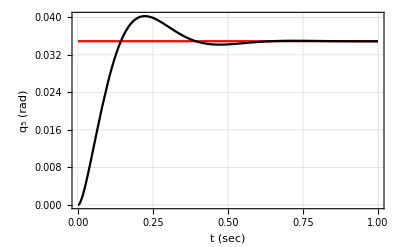

```mathematica
Plot[{Subscript[q, d5][t],Subscript[q, 5][t]/.stepSol[7]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_5 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

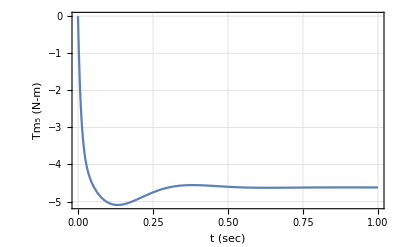

```mathematica
Plot[Subscript[Tm, 5][t]/.stepSol[7],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_5 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 4.5 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d5][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[7]=NDSolve[{(eqG[7]/.solGains[7]/.tConstRules[7])==0,(eqM[7]/.solGains[7]/.tConstRules[7])==0,Subscript[q, 5]'[Subscript[t, 0]]==0,Subscript[q, 5][Subscript[t, 0]]==0,Subscript[Tm, 5][Subscript[t, 0]]==0},{Subscript[q, 5],Subscript[Tm, 5]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_5→InterpolatingFunction[…],Tm_5→InterpolatingFunction[…]}}

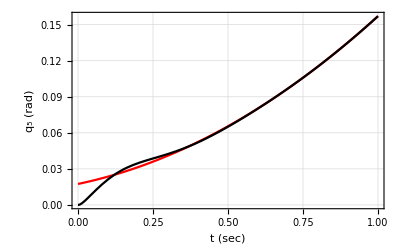

```mathematica
Plot[{Subscript[q, d5][t],Subscript[q, 5][t]/.trackSol[7]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_5 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

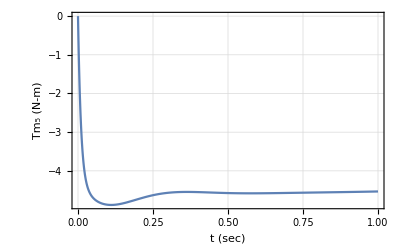

```mathematica
Plot[Subscript[Tm, 5][t]/.trackSol[7],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_5 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d5][t_]=.
```

#### Control gains q_6-motor

q_6-motor. Here we fixate all the other movements.

```mathematica
eqG[8]=eqC[8]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 1][t]->0,Subscript[q, 1]'[t]->0,Subscript[q, 1]''[t]->0,Subscript[q, 2][t]->0,Subscript[q, 2]'[t]->0,Subscript[q, 2]''[t]->0,Subscript[q, 3][t]->0,Subscript[q, 3]'[t]->0,Subscript[q, 3]''[t]->0,Subscript[q, 4][t]->0,Subscript[q, 4]'[t]->0,Subscript[q, 4]''[t]->0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Tm_6[t]-0.0449169 q_6''[t]

Linearize the equation.

```mathematica
eqL[8]=Normal[Series[eqG[8],{Subscript[q, 6][t],0,1},{Subscript[q, 6]'[t],0,1}]]
```

0.+Tm_6[t]-0.0449169 q_6''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[8]=D[eqL[8],t]
```

Tm_6'[t]-0.0449169 q_6^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[8]=Solve[eqM[8]==0,Subscript[Tm, 6]'[t]]//First
```

{Tm_6'[t]→-K_Int[8] q_6[t]+K_Int[8] q_d6[t]-K_prop[8] q_6'[t]+K_prop[8] q_d6'[t]-K_deriv[8] q_6''[t]+K_deriv[8] q_d6''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[8]=eqLd[8]//.solM[8]
```

-K_Int[8] q_6[t]+K_Int[8] q_d6[t]-K_prop[8] q_6'[t]+K_prop[8] q_d6'[t]-K_deriv[8] q_6''[t]+K_deriv[8] q_d6''[t]-0.0449169 q_6^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[8]=eqLf[8]//.{Derivative[n_][Subscript[q, 6]][t]->s^n,Subscript[q, 6][t]->1,Subscript[q, d6][t]->0,Subscript[q, d6]'[t]->0,Subscript[q, d6]''[t]->0}
```

-0.0449169 s^3-s^2 K_deriv[8]-K_Int[8]-s K_prop[8]

Put the characteristic equation in standard form.

```mathematica
charEq[8]=charEq[8]/Coefficient[charEq[8],s^3]//Expand
```

1. s^3+22.2633 s^2 K_deriv[8]+22.2633 K_Int[8]+22.2633 s K_prop[8]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[8]=Expand[(s+Subscript[a, 8])(s^2+ 2 Subscript[ζ, 8] Subscript[ω, n8] s + Subscript[ω, n8]^2)]
```

s^3+s^2 a_8+2 s^2 ζ_8 ω_n8+2 s a_8 ζ_8 ω_n8+s ω_n8^2+a_8 ω_n8^2

The time to peak is defined as

```mathematica
eqTp[8]=Subscript[t, p8]== π/(Subscript[ω, n8] √(1-Subscript[ζ, 8]^2));
```

The two percent settling time is given by

```mathematica
eqTs[8]=Subscript[t, s8]== 4/(Subscript[ζ, 8] Subscript[ω, n8]);
```

```mathematica
solZW[8]=Solve[{eqTp[8],eqTs[8]},{Subscript[ζ, 8],Subscript[ω, n8]}][[2]]
```

{ζ_8→(4 t_p8)/(√(16 t_p8^2+π^2 t_s8^2)),ω_n8→(√(16 t_p8^2+π^2 t_s8^2))/(t_p8 t_s8)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[8]=Coefficient[charEq[8],s^2]==Coefficient[charDesired[8],s^2]/.solZW[8]
```

22.2633 K_deriv[8]==a_8+8/t_s8

```mathematica
eqGain2[8]=Coefficient[charEq[8],s]==Coefficient[charDesired[8],s]/.solZW[8]
```

22.2633 K_prop[8]==(8 a_8)/t_s8+(16 t_p8^2+π^2 t_s8^2)/(t_p8^2 t_s8^2)

```mathematica
eqGain3[8]=(charEq[8]/.s->0)==(charDesired[8]/.s->0)/.solZW[8]
```

0.+22.2633 K_Int[8]==(a_8 (16 t_p8^2+π^2 t_s8^2))/(t_p8^2 t_s8^2)

Solve for the controller gains.

```mathematica
solGains[8]=Solve[{eqGain1[8],eqGain2[8],eqGain3[8]},{Subscript[K, prop][8],Subscript[K, Int][8],Subscript[K, deriv][8]}]//First
```

{K_prop[8]→0.0449169 ((8. a_8)/t_s8+(1. (16. t_p8^2+9.8696 t_s8^2))/(t_p8^2 t_s8^2)),K_Int[8]→0.0449169 (0.+(1. a_8 (16. t_p8^2+9.8696 t_s8^2))/(t_p8^2 t_s8^2)),K_deriv[8]→0.0449169 (1. a_8+8./t_s8)}

Now set the time constants.

```mathematica
tConstRules[8]={Subscript[a, 8]->100,Subscript[t, p8]->1/4,Subscript[t, s8]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d6][t_]:=stepMag UnitStep[t]
stepSol[8]=NDSolve[{(eqG[8]/.solGains[8]/.tConstRules[8])==0,(eqM[8]/.solGains[8]/.tConstRules[8])==0,Subscript[q, 6]'[Subscript[t, 0]]==0,Subscript[q, 6][Subscript[t, 0]]==0,Subscript[Tm, 6][Subscript[t, 0]]==0},{Subscript[q, 6],Subscript[Tm, 6]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_6→InterpolatingFunction[…],Tm_6→InterpolatingFunction[…]}}

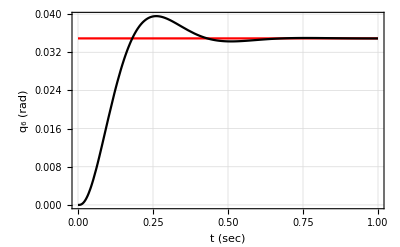

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.stepSol[8]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

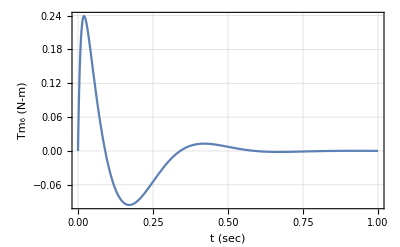

```mathematica
Plot[Subscript[Tm, 6][t]/.stepSol[8],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_6 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 0.2 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d6][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[8]=NDSolve[{(eqG[8]/.solGains[8]/.tConstRules[8])==0,(eqM[8]/.solGains[8]/.tConstRules[8])==0,Subscript[q, 6]'[Subscript[t, 0]]==0,Subscript[q, 6][Subscript[t, 0]]==0,Subscript[Tm, 6][Subscript[t, 0]]==0},{Subscript[q, 6],Subscript[Tm, 6]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_6→InterpolatingFunction[…],Tm_6→InterpolatingFunction[…]}}

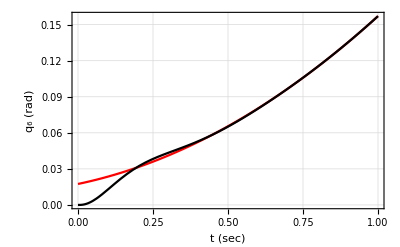

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.trackSol[8]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

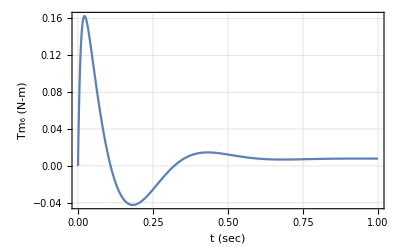

```mathematica
Plot[Subscript[Tm, 6][t]/.trackSol[8],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_6 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d6][t_]=.
```